```mathematica
(*Bloque para cargar MaTeX*)
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"]
<<MaTeX`;
MaTeX["x^2"]
```

ConfigureMaTeX[pdfLaTeX→C:\texlive\2024\bin\windows\pdflatex.exe]

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

$Failed

# Contour plots

## Simetric case

```mathematica
ν=1/3
```

1/3

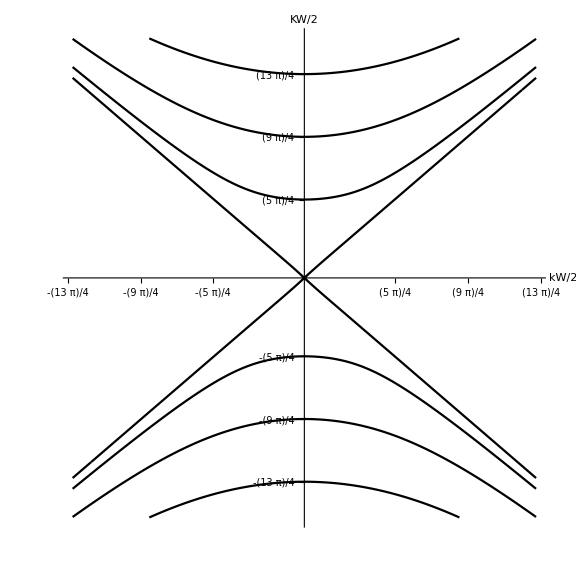

```mathematica
ContourPlot[√(Kc^2+k^2)*(Kc^2-k^2(1-ν))^2*Cos[√(Kc^2-k^2)]Sinh[√(Kc^2+k^2)]-√(Kc^2-k^2)*(Kc^2+k^2(1-ν))^2 Sin[√(Kc^2-k^2)]*Cosh[√(Kc^2+k^2)]==0,{k,-10,10},{Kc,-12,12},MaxRecursion->5,ImageSize->Large,Frame->False,Axes->True,AxesLabel->{"kW/2","KW/2"},Ticks->{{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome"]
```

## Asymmetric

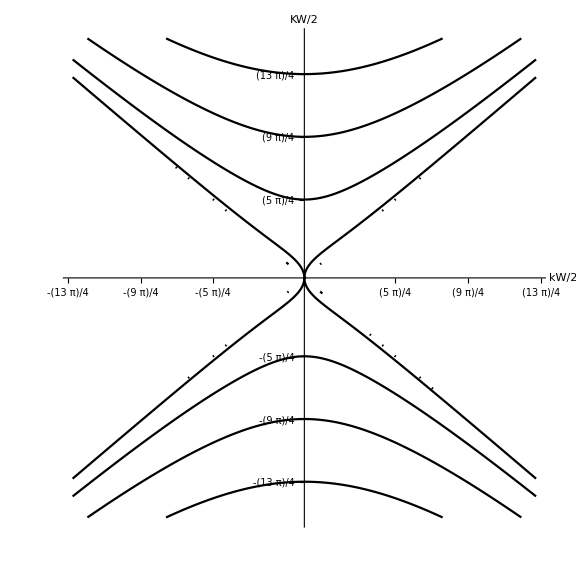

```mathematica
ContourPlot[√(Kc^2-k^2)*(Kc^2+k^2(1-ν))^2*Cos[√(Kc^2-k^2)]Sinh[√(Kc^2+k^2)]-√(Kc^2+k^2)*(Kc^2-k^2(1-ν))^2 Sin[√(Kc^2-k^2)]*Cosh[√(Kc^2+k^2)]==0,{k,-10,10},{Kc,-12,12},MaxRecursion->5,ImageSize->Large,Frame->False,Axes->True,AxesLabel->{"kW/2","KW/2"},Ticks->{{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome"]
```

## Dispersion relations

#### Symmetric case

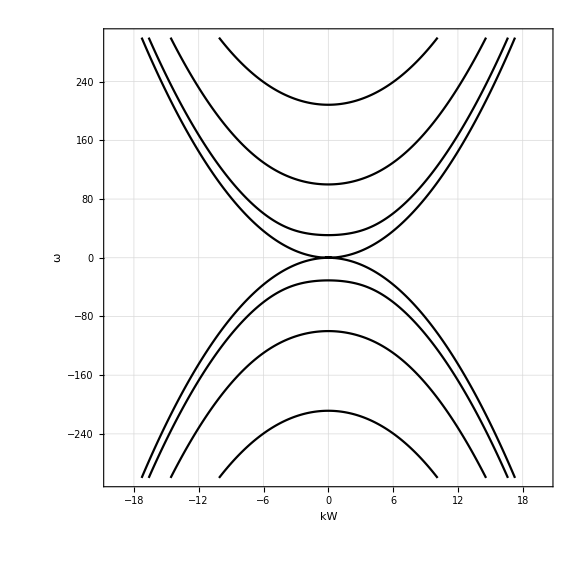

```mathematica
omegasym=ContourPlot[√(Abs[ω]+k^2)*(Abs[ω]-k^2(1-ν))^2*Cos[√((Abs[ω]-k^2)/2)]Sinh[√((Abs[ω]+k^2)/2)]-√(Abs[ω]-k^2)*(Abs[ω]+k^2(1-ν))^2 Sin[√((Abs[ω]-k^2)/2)]*Cosh[√((Abs[ω]+k^2)/2)]==0,{k,-20,20},{ω,-300,300},MaxRecursion->5,ImageSize->Large,Frame->True,Axes->True,AxesLabel->{"kW","ω"},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome"]
```

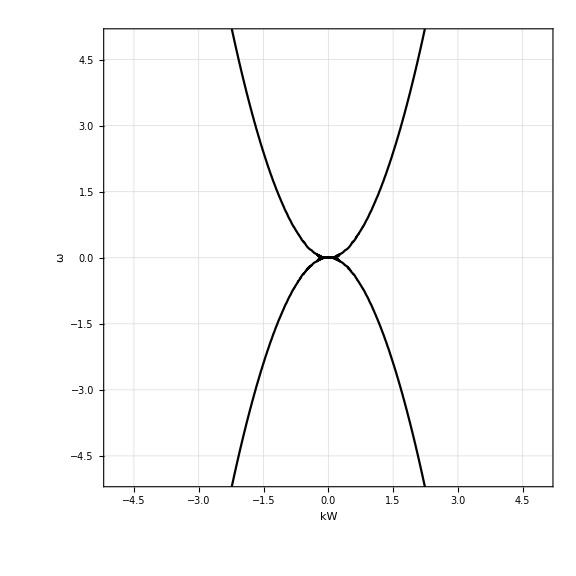

```mathematica
ContourPlot[√(Abs[ω]+k^2)*(Abs[ω]-k^2(1-ν))^2*Cos[√((Abs[ω]-k^2)/2)]Sinh[√((Abs[ω]+k^2)/2)]-√(Abs[ω]-k^2)*(Abs[ω]+k^2(1-ν))^2 Sin[√((Abs[ω]-k^2)/2)]*Cosh[√((Abs[ω]+k^2)/2)]==0,{k,-20,20},{ω,-300,300},MaxRecursion->5,ImageSize->Large,Frame->True,Axes->True,AxesLabel->{"kW","ω"},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome",PlotRange->{{-5,5},{-5,5}}]
```

#### Asymmetric case

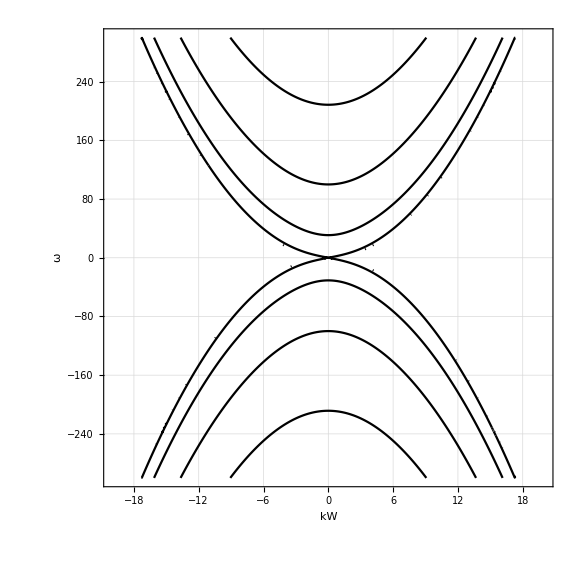

```mathematica
omegaAsym=ContourPlot[√(Abs[ω]-k^2)*(Abs[ω]+k^2(1-ν))^2*Cos[√((Abs[ω]-k^2)/2)]Sinh[√((Abs[ω]+k^2)/2)]-√(Abs[ω]+k^2)*(Abs[ω]-k^2(1-ν))^2 Sin[√((Abs[ω]-k^2)/2)]*Cosh[√((Abs[ω]+k^2)/2)]==0,{k,-20,20},{ω,-300,300},MaxRecursion->5,ImageSize->Large,Frame->True,Axes->True,AxesLabel->{"kW","ω"},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome"]
```

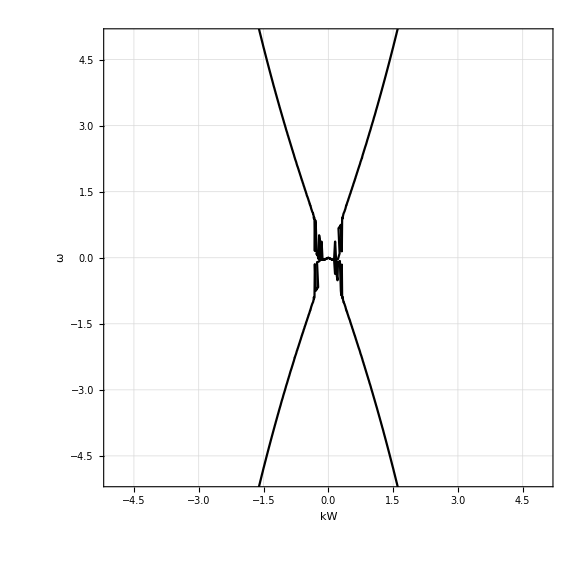

```mathematica
ContourPlot[√(Abs[ω]-k^2)*(Abs[ω]+k^2(1-ν))^2*Cos[√((Abs[ω]-k^2)/2)]Sinh[√((Abs[ω]+k^2)/2)]-√(Abs[ω]+k^2)*(Abs[ω]-k^2(1-ν))^2 Sin[√((Abs[ω]-k^2)/2)]*Cosh[√((Abs[ω]+k^2)/2)]==0,{k,-20,20},{ω,-300,300},MaxRecursion->5,ImageSize->Large,Frame->True,Axes->True,AxesLabel->{"kW","ω"},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotTheme->"Monochrome",PlotRange->{{-5,5},{-5,5}}]
```

## Approximations

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Tan[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Tanh[Sqrt[w+k^2]/2]==0,{w,Abs[k]+offset}, WorkingPrecision->20]]]];
frecuenciaωAntiSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
```

```mathematica
data1 = Table[{x,frecuenciaωAntiSimPositivo[x,0.0]}, {x,-1.0, 1.0, 0.01 }];
data2= Table[{x,frecuenciaωAntiSimPositivo[x, 30.0]}, {x,-3.0, 3.0, 0.01}];
data3=Table[{x,frecuenciaωAntiSimPositivo[x, 60.0]}, {x, -5,5, 0.05}];
data4=Table[{x,frecuenciaωAntiSimPositivo[x, 200.0]}, {x, -5,5, 0.05}];
datam1 = Table[{x,frecuenciaωAntiSimNegativo[x,0.0]}, {x,-1.0, 1.0, 0.01 }];
datam2= Table[{x,frecuenciaωAntiSimNegativo[x, -30.0]}, {x,-3.0, 3.0, 0.01}];
datam3=Table[{x,frecuenciaωAntiSimNegativo[x, -60.0]}, {x, -5,5, 0.05}];
datam4=Table[{x,frecuenciaωAntiSimNegativo[x, -200.0]}, {x, -5,5, 0.05}];
```

FindRoot::precw: The precision of the argument function ((-0.666667+w)^2 √(1.+w) Tan[(√(-1.+w))/2]-√(-1.+w) (0.666667+w)^2 Tanh[(√(1.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-0.6534+w)^2 √(0.9801+w) Tan[(√(-0.9801+w))/2]-√(-0.9801+w) (0.6534+w)^2 Tanh[(√(0.9801+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-0.640267+w)^2 √(0.9604+w) Tan[(√(-0.9604+w))/2]-√(-0.9604+w) (0.640267+w)^2 Tanh[(√(0.9604+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ((-6.+w)^2 √(9.+w) Tan[(√(-9.+w))/2]-√(-9.+w) (6.+w)^2 Tanh[(√(9.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-5.96007+w)^2 √(8.9401+w) Tan[(√(-8.9401+w))/2]-√(-8.9401+w) (5.96007+w)^2 Tanh[(√(8.9401+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-5.92027+w)^2 √(8.8804+w) Tan[(√(-8.8804+w))/2]-√(-8.8804+w) (5.92027+w)^2 Tanh[(√(8.8804+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ((-16.6667+w)^2 √(25.+w) Tan[(√(-25.+w))/2]-√(-25.+w) (16.6667+w)^2 Tanh[(√(25.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.335+w)^2 √(24.5025+w) Tan[(√(-24.5025+w))/2]-√(-24.5025+w) (16.335+w)^2 Tanh[(√(24.5025+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.0067+w)^2 √(24.01+w) Tan[(√(-24.01+w))/2]-√(-24.01+w) (16.0067+w)^2 Tanh[(√(24.01+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ((-16.6667+w)^2 √(25.+w) Tan[(√(-25.+w))/2]-√(-25.+w) (16.6667+w)^2 Tanh[(√(25.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.335+w)^2 √(24.5025+w) Tan[(√(-24.5025+w))/2]-√(-24.5025+w) (16.335+w)^2 Tanh[(√(24.5025+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.0067+w)^2 √(24.01+w) Tan[(√(-24.01+w))/2]-√(-24.01+w) (16.0067+w)^2 Tanh[(√(24.01+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
antiSimetrica1= Fit[data1, {1, x, x^2}, x]
```

-6.26473×10^-17+1. x^2

```mathematica
antiSimetrica2 = Fit[data2, {1, x, x^2}, x]
```

3.16786+2.51539×10^-17 x+0.695127 x^2

```mathematica
antiSimetrica3 = Fit[data3, {1, x, x^2}, x]
```

78.2728-1.36725×10^-15 x-3.18109 x^2

```mathematica
antiSimetrica4=Fit[data4,{1,x,x^2},x]
```

199.925-3.79237×10^-15 x+1.20877 x^2

```mathematica
antiSimetricam1=Fit[datam1,{1,x,x^2},x]
```

6.26473×10^-17-1. x^2

```mathematica
antiSimetricam2=Fit[datam2,{1,x,x^2},x]
antiSimetricam3=Fit[datam3,{1,x,x^2},x]
antiSimetricam4=Fit[datam4,{1,x,x^2},x]
```

-2.08162-1.36333×10^-16 x-1.5567 x^2

-61.9704+1.64812×10^-15 x-1.29119 x^2

-199.925+3.79237×10^-15 x-1.20877 x^2

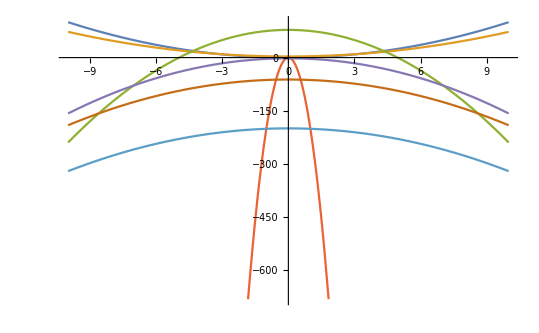

```mathematica
aproximationsASYM=Plot[{antiSimetrica1,antiSimetrica2, antiSimetrica3,antiSimetrica4 
antiSimetricam1,antiSimetricam2,antiSimetricam3,antiSimetricam4}, {x, -10, 10}]
```

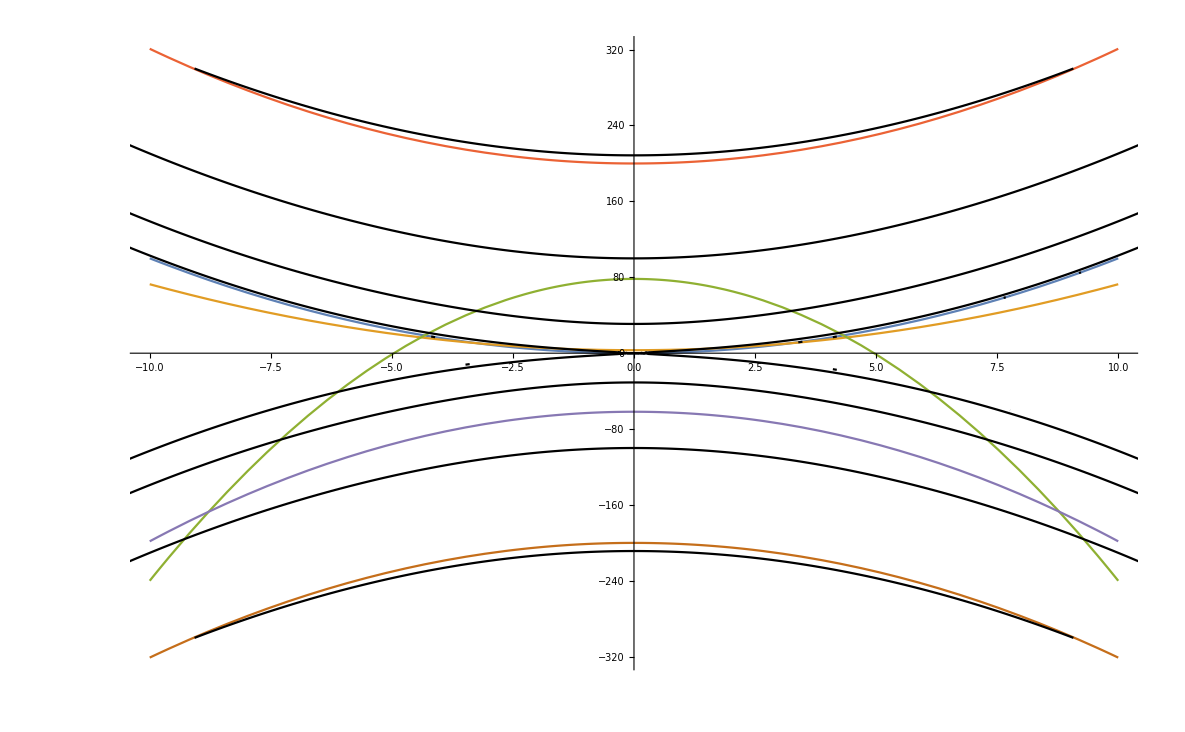

```mathematica
Show[aproximationsASYM,omegaAsym]
```

```mathematica
Asym[k_,ω_]:=√(Abs[ω]-k^2)*(Abs[ω]+k^2(1-ν))^2*Cos[√((Abs[ω]-k^2)/2)]Sinh[√((Abs[ω]+k^2)/2)]-√(Abs[ω]+k^2)*(Abs[ω]-k^2(1-ν))^2 Sin[√((Abs[ω]-k^2)/2)]*Cosh[√((Abs[ω]+k^2)/2)]

refine[Asym_,pt0:{k_,ω_}]:=Module[{grad,t},grad=N[{Derivative[1,0][Asym][k,ω],Derivative[0,1][Asym][k,ω]}];
pt0+grad*t/. FindRoot[Asym@@(pt0+grad*t),{t,0}]]

points=Join@@Cases[Normal@ContourPlot[Asym[k,ω]==0,{k,-20,20},{ω,-300,300},MaxRecursion->5],Line[pts_]->pts,Infinity]

refine[Asym,#]&/@points
```

{{14.8214,-219.675},{14.8204,-219.643},{-14.8214,219.675},{-14.8204,219.643},{-14.8214,-219.675},{-14.8204,-219.643},{7.6765,58.9286},{7.63334,58.2678},{7.76328,-60.2679},{7.76552,-60.3028},{4.10714,-16.8686},{4.18793,-17.5382},{-4.10714,16.8686},{-4.18793,17.5382},{4.10714,16.8686},{4.18793,17.5382},{-13.1696,-173.438},{-13.1372,-172.585},{13.1696,173.437},{13.1372,172.585},{7.76328,60.2679},{7.76552,60.3028},{-10.4284,-108.752},{-10.4796,-109.821},{10.4284,108.752},{10.4796,109.821},{-3.39286,-11.5114},{-3.47889,-12.1023},{3.39286,11.5114},{3.47889,12.1023},{9.19048,84.4643},{9.23054,85.2026},{15.4183,-237.723},{15.3983,-237.106},{14.707,-216.295},{14.6853,-215.658},{-15.4183,237.723},{-15.3983,237.106},{-14.707,216.295},{-14.6853,215.658},{17.2668,298.141},{17.2533,297.674},{-13.8234,-191.086},{-13.839,-191.518},{-13.8391,-191.521},{13.8234,-191.086},{13.839,-191.518},{13.8391,-191.521},{-13.8234,191.086},{-13.839,191.518},{-13.8391,191.521},{13.8234,191.086},{13.839,191.518},{13.8391,191.521},{15.8472,-251.132},{15.8678,-251.786},{-15.8472,251.132},{-15.8678,251.786},{11.802,-139.286},{11.8303,-139.955},{-11.802,139.286},{-11.8303,139.955},{16.1039,-259.335},{16.0897,-258.878},{-16.1039,259.335},{-16.0897,258.878},{-14.3967,-207.264},{-14.412,-207.705},{-14.9873,-226.674},{-15.0446,-226.339},{-14.9777,-226.404},{-14.9756,-226.339},{-14.9731,-226.271},{-14.9689,-226.137},{-14.9648,-226.004},{-14.9554,-225.74},{-14.9538,-225.693},{-14.953,-225.67},{-14.9504,-225.595},{-14.9464,-225.469},{-14.9422,-225.335},{-14.939,-225.246},{-14.9361,-225.167},{-14.933,-225.079},{-14.9314,-225.025},{-14.9304,-225.},{-14.9276,-224.919},{-14.9239,-224.802},{-14.9219,-224.748},{-14.9192,-224.665},{-14.9165,-224.578},{-14.9135,-224.498},{-14.9107,-224.417},{-14.9089,-224.358},{-14.9079,-224.33},{-14.9048,-224.241},{-14.9022,-224.163},{-14.9014,-224.135},{-14.8996,-224.086},{-14.8966,-223.996},{-14.8937,-223.915},{-14.8933,-223.901},{-14.8909,-223.828},{-14.8884,-223.756},{-14.8864,-223.691},{-14.8853,-223.661},{-14.8818,-223.562},{-14.8789,-223.469},{-14.8772,-223.426},{-14.8739,-223.326},{-14.8712,-223.249},{-14.8703,-223.222},{-14.8682,-223.158},{-14.8675,-223.137},{-14.8661,-223.097},{-14.8653,-223.075},{-14.8638,-223.026},{-14.8625,-222.991},{-14.8605,-222.932},{-14.86,-222.915},{-14.8597,-222.907},{-14.8588,-222.882},{-14.8569,-222.824},{-14.8562,-222.804},{-14.8549,-222.767},{-14.854,-222.74},{-14.8525,-222.693},{-14.8512,-222.656},{-14.8493,-222.602},{-14.8487,-222.582},{-14.8473,-222.542},{-14.8456,-222.489},{-14.8438,-222.437},{-14.8412,-222.36},{-14.8399,-222.321},{-14.8374,-222.249},{-14.8357,-222.201},{-14.8342,-222.154},{-14.8336,-222.138},{-14.8326,-222.108},{-14.8286,-221.987},{-14.8261,-221.916},{-14.8242,-221.86},{-14.8228,-221.819},{-14.8223,-221.806},{-14.8214,-221.78},{-14.82,-221.735},{-14.8185,-221.695},{-14.8184,-221.689},{-14.8171,-221.652},{-14.8158,-221.615},{-14.8148,-221.584},{-14.8126,-221.519},{-14.8114,-221.484},{-14.811,-221.473},{-14.8103,-221.451},{-14.8086,-221.401},{-14.8073,-221.361},{-14.8057,-221.317},{-14.8047,-221.287},{-14.8035,-221.251},{-14.801,-221.178},{-14.8001,-221.15},{-14.7991,-221.122},{-14.796,-221.029},{-14.7945,-220.982},{-14.7894,-220.836},{-14.7884,-220.807},{-14.7879,-220.794},{-14.7831,-220.647},{-14.7809,-220.586},{-14.7777,-220.494},{-14.7772,-220.48},{-14.7771,-220.475},{-14.7768,-220.466},{-14.7744,-220.396},{-14.7734,-220.364},{-14.7717,-220.313},{-14.7696,-220.253},{-14.7661,-220.152},{-14.7658,-220.145},{-14.7658,-220.143},{-14.7656,-220.139},{-14.7603,-219.978},{-14.7583,-219.921},{-14.7545,-219.812},{-14.7544,-219.811},{-14.7544,-219.81},{-14.7544,-219.809},{-14.7516,-219.727},{-14.7507,-219.699},{-14.7489,-219.648},{-14.7487,-219.643},{-14.7485,-219.638},{-14.7469,-219.589},{-14.7459,-219.559},{-14.7433,-219.484},{-14.7431,-219.478},{-14.743,-219.475},{-14.7427,-219.466},{-14.7412,-219.423},{-14.7402,-219.392},{-14.7393,-219.368},{-14.7377,-219.321},{-14.7373,-219.308},{-14.7356,-219.256},{-14.7345,-219.224},{-14.7321,-219.157},{-14.7318,-219.146},{-14.7316,-219.141},{-14.731,-219.123},{-14.728,-219.035},{-14.726,-218.973},{-14.7243,-218.924},{-14.721,-218.83},{-14.7204,-218.814},{-14.7202,-218.806},{-14.7192,-218.78},{-14.7167,-218.703},{-14.7154,-218.667},{-14.7144,-218.638},{-14.7129,-218.592},{-14.7098,-218.503},{-14.7087,-218.471},{-14.7075,-218.436},{-14.7053,-218.371},{-14.7031,-218.304},{-14.6987,-218.177},{-14.6977,-218.15},{-14.6973,-218.136},{-14.6957,-218.092},{-14.694,-218.039},{-14.6916,-217.969},{-14.6902,-217.928},{-14.6875,-217.851},{-14.6864,-217.818},{-14.6858,-217.801},{-14.6839,-217.748},{-14.6826,-217.708},{-14.6802,-217.634},{-14.6788,-217.597},{-14.6763,-217.525},{-14.675,-217.486},{-14.6743,-217.467},{-14.6721,-217.403},{-14.6712,-217.376},{-14.6708,-217.364},{-14.6686,-217.299},{-14.6675,-217.265},{-14.6652,-217.2},{-14.6629,-217.132},{-14.6603,-217.058},{-14.6598,-217.045},{-14.6572,-216.964},{-14.654,-216.874},{-14.6523,-216.823},{-14.6513,-216.797},{-14.6484,-216.713},{-14.6484,-216.713},{-14.6484,-216.713},{-14.6456,-216.629},{-14.6447,-216.602},{-14.6429,-216.551},{-14.6427,-216.546},{-14.6409,-216.491},{-14.6398,-216.462},{-14.6373,-216.388},{-14.6371,-216.382},{-14.6366,-216.368},{-14.6341,-216.295},{-14.6333,-216.271},{-14.6317,-216.226},{-14.6312,-216.211},{-14.6295,-216.16},{-14.6284,-216.127},{-14.6257,-216.05},{-14.6247,-216.022},{-14.6226,-215.96},{-14.6219,-215.939},{-14.6205,-215.902},{-14.6197,-215.876},{-14.6181,-215.829},{-14.6168,-215.792},{-14.615,-215.739},{-14.6143,-215.719},{-14.6128,-215.676},{-14.6111,-215.625},{-14.6094,-215.576},{-14.6067,-215.498},{-14.6054,-215.458},{-14.6029,-215.388},{-14.6008,-215.329},{-14.5995,-215.29},{-14.5991,-215.277},{-14.5982,-215.253},{-14.5953,-215.166},{-14.5938,-215.123},{-14.5915,-215.056},{-14.5889,-214.983},{-14.5879,-214.955},{-14.5877,-214.946},{-14.5871,-214.93},{-14.5851,-214.872},{-14.5839,-214.835},{-14.5822,-214.788},{-14.5815,-214.768},{-14.5801,-214.725},{-14.5769,-214.636},{-14.5764,-214.621},{-14.5762,-214.616},{-14.5759,-214.606},{-14.5735,-214.537},{-14.5725,-214.505},{-14.5706,-214.453},{-14.5703,-214.445},{-14.5686,-214.394},{-14.5649,-214.288},{-14.5648,-214.286},{-14.5648,-214.285},{-14.5647,-214.283},{-14.561,-214.174},{-14.5592,-214.118},{-14.5536,-213.96},{-14.5534,-213.954},{-14.5533,-213.951},{-14.5529,-213.941},{-14.5476,-213.783},{-14.5459,-213.73},{-14.5424,-213.637},{-14.5417,-213.616},{-14.5409,-213.593},{-14.5382,-213.513},{-14.5368,-213.476},{-14.5359,-213.449},{-14.5344,-213.402},{-14.533,-213.365},{-14.5312,-213.315},{-14.5305,-213.292},{-14.5301,-213.281},{-14.5288,-213.245},{-14.5267,-213.182},{-14.5244,-213.114},{-14.5229,-213.072},{-14.5201,-212.992},{-14.5191,-212.962},{-14.5185,-212.946},{-14.5167,-212.896},{-14.5152,-212.852},{-14.5145,-212.832},{-14.5127,-212.779},{-14.5115,-212.741},{-14.5098,-212.695},{-14.5089,-212.671},{-14.5076,-212.631},{-14.5069,-212.612},{-14.5046,-212.547},{-14.5038,-212.522},{-14.5033,-212.51},{-14.5011,-212.444},{-14.5,-212.411},{-14.4978,-212.348},{-14.4953,-212.277},{-14.4925,-212.198},{-14.4923,-212.191},{-14.4922,-212.188},{-14.4895,-212.109},{-14.4885,-212.081},{-14.4866,-212.028},{-14.4865,-212.026},{-14.4847,-211.971},{-14.4837,-211.942},{-14.481,-211.867},{-14.4808,-211.861},{-14.4804,-211.849},{-14.4778,-211.775},{-14.477,-211.751},{-14.4754,-211.705},{-14.4732,-211.64},{-14.4721,-211.607},{-14.4694,-211.531},{-14.4691,-211.523},{-14.4682,-211.499},{-14.4662,-211.44},{-14.4656,-211.421},{-14.4643,-211.385},{-14.4633,-211.356},{-14.4621,-211.324},{-14.4617,-211.311},{-14.4604,-211.272},{-14.4587,-211.225},{-14.4579,-211.201},{-14.456,-211.149},{-14.4545,-211.105},{-14.4541,-211.091},{-14.4531,-211.064},{-14.4488,-210.938},{-14.4464,-210.871},{-14.4438,-210.798},{-14.4429,-210.77},{-14.4426,-210.761},{-14.442,-210.744},{-14.44,-210.686},{-14.4388,-210.65},{-14.437,-210.603},{-14.4364,-210.584},{-14.4349,-210.541},{-14.4316,-210.447},{-14.4312,-210.435},{-14.4311,-210.431},{-14.4308,-210.424},{-14.4273,-210.321},{-14.4255,-210.268},{-14.4234,-210.211},{-14.4196,-210.104},{-14.4196,-210.102},{-14.4195,-210.1},{-14.4194,-210.096},{-14.4158,-209.991},{-14.4138,-209.933},{-14.4085,-209.784},{-14.4081,-209.772},{-14.4078,-209.766},{-14.4071,-209.745},{-14.4049,-209.682},{-14.4043,-209.662},{-14.4029,-209.624},{-14.402,-209.598},{-14.401,-209.569},{-14.4004,-209.552},{-14.3991,-209.515},{-14.3973,-209.465},{-14.3966,-209.442},{-14.3961,-209.431},{-14.3948,-209.393},{-14.3927,-209.332},{-14.3917,-209.305},{-14.3903,-209.263},{-14.3889,-209.222},{-14.3874,-209.18},{-14.3862,-209.145},{-14.3851,-209.113},{-14.3845,-209.096},{-14.3825,-209.041},{-14.3812,-209.003},{-14.3806,-208.986},{-14.3786,-208.929},{-14.3774,-208.893},{-14.375,-208.826},{-14.3735,-208.783},{-14.3728,-208.761},{-14.3702,-208.689},{-14.3697,-208.674},{-14.367,-208.594},{-14.3638,-208.507},{-14.3621,-208.453},{-14.3611,-208.426},{-14.3578,-208.336},{-14.3552,-208.259},{-14.3543,-208.234},{-14.3527,-208.188},{-14.3505,-208.125},{-14.3494,-208.092},{-14.3466,-208.015},{-14.3454,-207.983},{-14.3435,-207.924},{-14.3415,-207.87},{-14.3389,-207.795},{-14.3376,-207.757},{-14.3351,-207.686},{-14.333,-207.629},{-14.3317,-207.589},{-14.3312,-207.576},{-14.3304,-207.552},{-14.3259,-207.422},{-14.3235,-207.357},{-14.3206,-207.276},{-14.3199,-207.254},{-14.3192,-207.235},{-14.3158,-207.138},{-14.3141,-207.087},{-14.312,-207.028},{-14.3081,-206.921},{-14.3081,-206.92},{-14.3081,-206.919},{-14.308,-206.918},{-14.3043,-206.809},{-14.3023,-206.752},{-14.3004,-206.699},{-14.2969,-206.6},{-14.2963,-206.585},{-14.2957,-206.567},{-14.2927,-206.48},{-14.2913,-206.442},{-14.2904,-206.417},{-14.2894,-206.39},{-14.2888,-206.371},{-14.2885,-206.363},{-14.2875,-206.334},{-14.2869,-206.316},{-14.286,-206.292},{-14.2857,-206.284},{-14.2849,-206.262},{-14.2845,-206.25},{-14.2832,-206.212},{-14.283,-206.207},{-14.2816,-206.166},{-14.2811,-206.152},{-14.2801,-206.125},{-14.2786,-206.083},{-14.2773,-206.042},{-14.2746,-205.966},{-14.2734,-205.933},{-14.2728,-205.915},{-14.2707,-205.857},{-14.2695,-205.823},{-14.2669,-205.748},{-14.2657,-205.713},{-14.2634,-205.649},{-14.2618,-205.604},{-14.261,-205.58},{-14.2581,-205.501},{-14.2579,-205.495},{-14.2551,-205.413},{-14.2541,-205.385},{-14.2522,-205.333},{-14.2492,-205.246},{-14.2463,-205.167},{-14.2456,-205.146},{-14.2432,-205.078},{-14.2425,-205.057},{-14.2411,-205.018},{-14.2402,-204.994},{-14.2393,-204.967},{-14.2386,-204.948},{-14.2373,-204.911},{-14.2355,-204.86},{-14.2347,-204.838},{-14.233,-204.789},{-14.2314,-204.743},{-14.2309,-204.729},{-14.2299,-204.702},{-14.2256,-204.576},{-14.2231,-204.51},{-14.2204,-204.433},{-14.2195,-204.408},{-14.2187,-204.387},{-14.2154,-204.291},{-14.2137,-204.241},{-14.2077,-204.076},{-14.2076,-204.073},{-14.2076,-204.072},{-14.2019,-203.906},{-14.1999,-203.854},{-14.1964,-203.756},{-14.1958,-203.739},{-14.1951,-203.718},{-14.1929,-203.655},{-14.1922,-203.635},{-14.19,-203.571},{-14.1883,-203.526},{-14.1853,-203.441},{-14.1844,-203.417},{-14.184,-203.404},{-14.1824,-203.361},{-14.1805,-203.308},{-14.1797,-203.285},{-14.178,-203.237},{-14.1767,-203.198},{-14.1741,-203.126},{-14.1721,-203.069},{-14.1697,-203.003},{-14.1689,-202.98},{-14.1662,-202.902},{-14.1629,-202.812},{-14.1612,-202.76},{-14.1602,-202.734},{-14.157,-202.645},{-14.1543,-202.567},{-14.1535,-202.542},{-14.1518,-202.498},{-14.1483,-202.4},{-14.1458,-202.322},{-14.1424,-202.232},{-14.1406,-202.184},{-14.138,-202.104},{-14.1314,-201.927},{-14.1305,-201.897},{-14.1301,-201.888},{-14.1295,-201.871},{-14.1245,-201.73},{-14.1225,-201.667},{-14.1184,-201.563},{-14.1183,-201.559},{-14.1146,-201.451},{-14.1126,-201.395},{-14.1071,-201.245},{-14.1067,-201.234},{-14.1065,-201.228},{-14.1058,-201.207},{-14.1029,-201.124},{-14.1007,-201.06},{-14.099,-201.015},{-14.096,-200.932},{-14.0946,-200.893},{-14.0929,-200.847},{-14.0912,-200.797},{-14.0904,-200.776},{-14.0886,-200.725},{-14.0873,-200.688},{-14.0856,-200.642},{-14.0848,-200.62},{-14.0834,-200.579},{-14.0827,-200.558},{-14.08,-200.486},{-14.0795,-200.471},{-14.0792,-200.464},{-14.0766,-200.391},{-14.0756,-200.361},{-14.0737,-200.307},{-14.0717,-200.252},{-14.0707,-200.223},{-14.0678,-200.144},{-14.0671,-200.125},{-14.0647,-200.056},{-14.0639,-200.034},{-14.0625,-199.996},{-14.0617,-199.972},{-14.0606,-199.944},{-14.06,-199.926},{-14.0587,-199.888},{-14.0569,-199.84},{-14.0561,-199.817},{-14.0542,-199.764},{-14.0527,-199.721},{-14.0522,-199.708},{-14.0513,-199.683},{-14.0468,-199.554},{-14.0444,-199.49},{-14.0412,-199.402},{-14.0407,-199.386},{-14.0405,-199.381},{-14.0402,-199.372},{-14.0366,-199.272},{-14.0348,-199.219},{-14.0327,-199.163},{-14.029,-199.061},{-14.0288,-199.055},{-14.0287,-199.051},{-14.0282,-199.039},{-14.0249,-198.945},{-14.0228,-198.884},{-14.021,-198.836},{-14.0197,-198.8},{-14.0179,-198.75},{-14.0171,-198.728},{-14.0167,-198.717},{-14.0152,-198.677},{-14.0132,-198.619},{-14.0107,-198.549},{-14.0067,-198.439},{-14.0054,-198.401},{-14.0046,-198.382},{-14.0022,-198.314},{-14.0014,-198.293},{-13.9987,-198.214},{-13.9976,-198.184},{-13.9955,-198.128},{-13.9927,-198.047},{-13.9897,-197.967},{-13.9891,-197.95},{-13.9866,-197.879},{-13.9844,-197.818},{-13.9819,-197.749},{-13.9806,-197.712},{-13.9788,-197.664},{-13.978,-197.64},{-13.976,-197.587},{-13.9745,-197.545},{-13.9741,-197.532},{-13.9732,-197.509},{-13.9715,-197.461},{-13.9702,-197.423},{-13.9685,-197.377},{-13.9676,-197.354},{-13.9663,-197.314},{-13.9629,-197.223},{-13.9625,-197.21},{-13.9621,-197.199},{-13.9584,-197.097},{-13.9565,-197.042},{-13.9509,-196.889},{-13.9506,-196.88},{-13.9504,-196.875},{-13.9498,-196.858},{-13.9467,-196.771},{-13.9453,-196.735},{-13.9443,-196.708},{-13.9428,-196.662},{-13.9413,-196.624},{-13.9397,-196.58},{-13.9388,-196.554},{-13.9383,-196.54},{-13.9366,-196.493},{-13.9353,-196.456},{-13.9349,-196.445},{-13.9324,-196.373},{-13.931,-196.336},{-13.9286,-196.27},{-13.9271,-196.228},{-13.9263,-196.205},{-13.9234,-196.128},{-13.9202,-196.038},{-13.9192,-196.011},{-13.9174,-195.961},{-13.9153,-195.902},{-13.9142,-195.871},{-13.9113,-195.794},{-13.9111,-195.787},{-13.9102,-195.762},{-13.9081,-195.703},{-13.9062,-195.653},{-13.9035,-195.576},{-13.9021,-195.536},{-13.8969,-195.396},{-13.8957,-195.36},{-13.8951,-195.345},{-13.89,-195.201},{-13.8878,-195.143},{-13.8868,-195.117},{-13.8839,-195.037},{-13.8838,-195.035},{-13.8838,-195.033},{-13.8836,-195.029},{-13.8799,-194.926},{-13.8778,-194.866},{-13.876,-194.817},{-13.8747,-194.782},{-13.8728,-194.729},{-13.8721,-194.709},{-13.8717,-194.699},{-13.8703,-194.662},{-13.8681,-194.601},{-13.8672,-194.576},{-13.8656,-194.531},{-13.8642,-194.492},{-13.8625,-194.448},{-13.8616,-194.422},{-13.8603,-194.384},{-13.8595,-194.364},{-13.857,-194.294},{-13.8563,-194.276},{-13.8535,-194.196},{-13.8504,-194.114},{-13.8485,-194.059},{-13.8474,-194.029},{-13.8449,-193.961},{-13.8445,-193.951},{-13.8436,-193.926},{-13.8413,-193.862},{-13.8407,-193.841},{-13.8393,-193.807},{-13.8353,-193.694},{-13.8327,-193.626},{-13.8302,-193.558},{-13.8291,-193.527},{-13.8281,-193.5},{-13.825,-193.407},{-13.8231,-193.359},{-13.817,-193.194},{-13.8169,-193.193},{-13.8169,-193.192},{-13.8168,-193.189},{-13.813,-193.084},{-13.8109,-193.025},{-13.8091,-192.976},{-13.8058,-192.887},{-13.8047,-192.857},{-13.8033,-192.82},{-13.8012,-192.759},{-13.7987,-192.69},{-13.7946,-192.581},{-13.7933,-192.542},{-13.7925,-192.522},{-13.7899,-192.451},{-13.7865,-192.355},{-13.7855,-192.325},{-13.7835,-192.275},{-13.7803,-192.188},{-13.7775,-192.111},{-13.7763,-192.08},{-13.7742,-192.02},{-13.7723,-191.97},{-13.7696,-191.894},{-13.7681,-191.853},{-13.7628,-191.71},{-13.7617,-191.678},{-13.7612,-191.665},{-13.7559,-191.518},{-13.7538,-191.461},{-13.75,-191.36},{-13.7497,-191.35},{-13.7492,-191.339},{-13.7459,-191.245},{-13.7436,-191.183},{-13.7388,-191.055},{-13.738,-191.029},{-13.7374,-191.016},{-13.7356,-190.967},{-13.7314,-190.848},{-13.7301,-190.811},{-13.7277,-190.75},{-13.7252,-190.681},{-13.7223,-190.595},{-13.7191,-190.513},{-13.7165,-190.445},{-13.7143,-190.38},{-13.7083,-190.223},{-13.7067,-190.179},{-13.7062,-190.165},{-13.7054,-190.142},{-13.7023,-190.057},{-13.7007,-190.011},{-13.6985,-189.947},{-13.6944,-189.844},{-13.6942,-189.838},{-13.6904,-189.733},{-13.6884,-189.676},{-13.683,-189.534},{-13.6825,-189.518},{-13.6821,-189.509},{-13.6809,-189.477},{-13.676,-189.342},{-13.6746,-189.3},{-13.6719,-189.231},{-13.6698,-189.174},{-13.6671,-189.103},{-13.6665,-189.087},{-13.6663,-189.08},{-13.6636,-189.007},{-13.6626,-188.978},{-13.6607,-188.929},{-13.6605,-188.923},{-13.6586,-188.87},{-13.6575,-188.839},{-13.6551,-188.777},{-13.6546,-188.763},{-13.6534,-188.729},{-13.6513,-188.672},{-13.6507,-188.655},{-13.6496,-188.625},{-13.6452,-188.504},{-13.6427,-188.439},{-13.6395,-188.354},{-13.6389,-188.337},{-13.6384,-188.323},{-13.6348,-188.224},{-13.6328,-188.17},{-13.6272,-188.02},{-13.6268,-188.008},{-13.6266,-188.002},{-13.6257,-187.979},{-13.6205,-187.835},{-13.6189,-187.793},{-13.6161,-187.718},{-13.6149,-187.685},{-13.6142,-187.667},{-13.6118,-187.604},{-13.6109,-187.578},{-13.6081,-187.5},{-13.6049,-187.416},{-13.603,-187.362},{-13.6019,-187.333},{-13.5989,-187.255},{-13.5979,-187.227},{-13.5957,-187.165},{-13.595,-187.147},{-13.5937,-187.114},{-13.5895,-186.998},{-13.5872,-186.929},{-13.5832,-186.83},{-13.5826,-186.814},{-13.579,-186.716},{-13.5771,-186.663},{-13.5714,-186.512},{-13.571,-186.501},{-13.5708,-186.496},{-13.57,-186.474},{-13.5671,-186.394},{-13.5658,-186.362},{-13.5646,-186.328},{-13.5631,-186.286},{-13.5603,-186.211},{-13.5584,-186.161},{-13.556,-186.096},{-13.5551,-186.071},{-13.5522,-185.993},{-13.5491,-185.91},{-13.5471,-185.856},{-13.546,-185.826},{-13.542,-185.719},{-13.5398,-185.658},{-13.5391,-185.641},{-13.5379,-185.611},{-13.5366,-185.575},{-13.5351,-185.533},{-13.5335,-185.491},{-13.5324,-185.461},{-13.5311,-185.426},{-13.5279,-185.34},{-13.5273,-185.324},{-13.5268,-185.311},{-13.5231,-185.211},{-13.5211,-185.156},{-13.5156,-185.011},{-13.5151,-184.996},{-13.5138,-184.961},{-13.5087,-184.821},{-13.5073,-184.78},{-13.5045,-184.71},{-13.5024,-184.654},{-13.4993,-184.564},{-13.4962,-184.487},{-13.4933,-184.411},{-13.4912,-184.351},{-13.4899,-184.319},{-13.4855,-184.201},{-13.4836,-184.152},{-13.4831,-184.137},{-13.4821,-184.112},{-13.4791,-184.03},{-13.4774,-183.984},{-13.4751,-183.923},{-13.4712,-183.821},{-13.4711,-183.817},{-13.4711,-183.816},{-13.471,-183.814},{-13.4672,-183.706},{-13.4649,-183.65},{-13.4631,-183.601},{-13.4598,-183.515},{-13.459,-183.494},{-13.4586,-183.482},{-13.457,-183.44},{-13.455,-183.387},{-13.4542,-183.366},{-13.4523,-183.315},{-13.451,-183.279},{-13.4487,-183.216},{-13.4461,-183.147},{-13.443,-183.065},{-13.4427,-183.058},{-13.4398,-182.98},{-13.439,-182.957},{-13.4375,-182.919},{-13.4367,-182.896},{-13.435,-182.85},{-13.4335,-182.813},{-13.4319,-182.77},{-13.431,-182.743},{-13.4284,-182.676},{-13.4272,-182.645},{-13.4269,-182.636},{-13.4263,-182.621},{-13.4211,-182.478},{-13.4189,-182.422},{-13.4152,-182.323},{-13.4147,-182.31},{-13.414,-182.293},{-13.4109,-182.207},{-13.4085,-182.143},{-13.404,-182.025},{-13.4028,-181.993},{-13.4021,-181.975},{-13.3997,-181.91},{-13.3988,-181.886},{-13.3959,-181.808},{-13.3948,-181.779},{-13.3929,-181.728},{-13.3896,-181.641},{-13.3867,-181.565},{-13.3852,-181.526},{-13.3833,-181.473},{-13.3817,-181.431},{-13.3788,-181.349},{-13.3708,-181.142},{-13.3706,-181.138},{-13.3706,-181.137},{-13.3705,-181.135},{-13.3585,-180.804},{-13.3547,-180.707},{-13.3482,-180.54},{-13.3456,-180.469},{-13.3418,-180.372},{-13.3392,-180.301},{-13.3385,-180.28},{-13.3371,-180.246},{-13.3329,-180.134},{-13.3303,-180.068},{-13.3272,-179.986},{-13.3265,-179.967},{-13.3259,-179.951},{-13.3223,-179.854},{-13.3202,-179.799},{-13.3147,-179.656},{-13.3142,-179.64},{-13.3138,-179.632},{-13.3126,-179.6},{-13.3101,-179.533},{-13.3076,-179.464},{-13.3061,-179.426},{-13.3036,-179.36},{-13.3012,-179.297},{-13.298,-179.213},{-13.298,-179.213},{-13.2949,-179.129},{-13.2924,-179.065},{-13.29,-178.998},{-13.2886,-178.962},{-13.2833,-178.825},{-13.2822,-178.795},{-13.2818,-178.786},{-13.2812,-178.771},{-13.2778,-178.679},{-13.2759,-178.627},{-13.2738,-178.572},{-13.2701,-178.477},{-13.2697,-178.466},{-13.2695,-178.46},{-13.2686,-178.437},{-13.2657,-178.359},{-13.2632,-178.292},{-13.2616,-178.252},{-13.2589,-178.182},{-13.2576,-178.146},{-13.2568,-178.125},{-13.2538,-178.049},{-13.2505,-177.958},{-13.2495,-177.931},{-13.2444,-177.79},{-13.2415,-177.717},{-13.2377,-177.623},{-13.2366,-177.595},{-13.2334,-177.504},{-13.2314,-177.455},{-13.2254,-177.302},{-13.2251,-177.293},{-13.2249,-177.288},{-13.2242,-177.269},{-13.2211,-177.186},{-13.2199,-177.155},{-13.2186,-177.121},{-13.217,-177.08},{-13.2168,-177.074},{-13.2154,-177.037},{-13.215,-177.027},{-13.2143,-177.009},{-13.213,-176.973},{-13.2122,-176.953},{-13.2093,-176.879},{-13.209,-176.869},{-13.2089,-176.867},{-13.2087,-176.862},{-13.2058,-176.786},{-13.2048,-176.76},{-13.2031,-176.716},{-13.2026,-176.702},{-13.2019,-176.683},{-13.2008,-176.654},{-13.1994,-176.618},{-13.1975,-176.569},{-13.1967,-176.547},{-13.1962,-176.535},{-13.1944,-176.488},{-13.193,-176.451},{-13.1927,-176.441},{-13.192,-176.423},{-13.1898,-176.367},{-13.1886,-176.334},{-13.1866,-176.283},{-13.1864,-176.277},{-13.1845,-176.227},{-13.1808,-176.131},{-13.1803,-176.116},{-13.1795,-176.096},{-13.1771,-176.032},{-13.1764,-176.015},{-13.1752,-175.985},{-13.1739,-175.949},{-13.1724,-175.908},{-13.1707,-175.865},{-13.1703,-175.855},{-13.1696,-175.838},{-13.1683,-175.802},{-13.1675,-175.781},{-13.1645,-175.704},{-13.1642,-175.698},{-13.1642,-175.696},{-13.1641,-175.693},{-13.1611,-175.614},{-13.1602,-175.589},{-13.1585,-175.546},{-13.1547,-175.446},{-13.152,-175.376},{-13.1495,-175.311},{-13.1483,-175.279},{-13.1473,-175.255},{-13.1439,-175.163},{-13.1418,-175.112},{-13.1417,-175.109},{-13.1398,-175.058},{-13.1386,-175.028},{-13.1362,-174.964},{-13.1357,-174.951},{-13.1354,-174.944},{-13.1344,-174.918},{-13.1337,-174.898},{-13.1322,-174.86},{-13.1316,-174.845},{-13.1306,-174.818},{-13.129,-174.777},{-13.1276,-174.738},{-13.1258,-174.693},{-13.125,-174.672},{-13.1235,-174.632},{-13.1226,-174.609},{-13.1194,-174.527},{-13.1194,-174.526},{-13.1193,-174.524},{-13.1162,-174.442},{-13.1138,-174.381},{-13.1113,-174.313},{-13.1098,-174.275},{-13.1072,-174.207},{-13.1041,-174.129},{-13.1033,-174.107},{-13.1031,-174.101},{-13.1027,-174.091},{-13.097,-173.94},{-13.095,-173.888},{-13.0915,-173.8},{-13.0905,-173.772},{-13.089,-173.734},{-13.0868,-173.676},{-13.0859,-173.655},{-13.084,-173.605},{-13.0827,-173.57},{-13.0808,-173.521},{-13.0804,-173.51},{-13.0786,-173.464},{-13.0776,-173.438},{-13.0748,-173.365},{-13.0745,-173.358},{-13.0737,-173.338},{-13.0712,-173.27},{-13.0704,-173.251},{-13.0692,-173.219},{-13.0648,-173.103},{-13.0623,-173.039},{-13.0584,-172.941},{-13.0582,-172.935},{-13.058,-172.931},{-13.0541,-172.827},{-13.0519,-172.768},{-13.0469,-172.641},{-13.0459,-172.615},{-13.0453,-172.6},{-13.0431,-172.544},{-13.0418,-172.509},{-13.0389,-172.433},{-13.0378,-172.402},{-13.0357,-172.351},{-13.0325,-172.266},{-13.0295,-172.191},{-13.0278,-172.146},{-13.026,-172.098},{-13.0246,-172.062},{-13.0215,-171.977},{-13.0195,-171.931},{-13.0134,-171.774},{-13.0131,-171.767},{-13.013,-171.763},{-13.0124,-171.748},{-13.0091,-171.661},{-13.0066,-171.596},{-13.005,-171.555},{-13.0022,-171.485},{-13.0001,-171.429},{-12.9969,-171.349},{-12.9967,-171.344},{-12.9936,-171.261},{-12.9911,-171.197},{-12.9886,-171.13},{-12.9871,-171.094},{-12.9814,-170.949},{-12.9806,-170.926},{-12.9803,-170.92},{-12.9799,-170.91},{-12.9742,-170.759},{-12.9721,-170.708},{-12.9687,-170.622},{-12.9676,-170.592},{-12.9659,-170.549},{-12.9643,-170.508},{-12.9639,-170.497},{-12.9611,-170.424},{-12.9598,-170.391},{-12.9578,-170.34},{-12.9576,-170.335},{-12.9557,-170.285},{-12.9546,-170.257},{-12.9516,-170.18},{-12.9503,-170.147},{-12.9481,-170.089},{-12.9475,-170.074},{-12.9464,-170.047},{-12.9448,-170.006},{-12.9434,-169.968},{-12.9415,-169.922},{-12.9408,-169.904},{-12.9393,-169.862},{-12.9383,-169.838},{-12.9353,-169.761},{-12.9351,-169.757},{-12.935,-169.754},{-12.9347,-169.746},{-12.931,-169.651},{-12.9286,-169.587},{-12.9241,-169.473},{-12.9228,-169.439},{-12.922,-169.42},{-12.919,-169.343},{-12.9146,-169.227},{-12.9129,-169.186},{-12.909,-169.085},{-12.9063,-169.017},{-12.9033,-168.94},{-12.9024,-168.917},{-12.9022,-168.911},{-12.9018,-168.901},{-12.8981,-168.805},{-12.896,-168.75},{-12.8906,-168.615},{-12.8898,-168.594},{-12.8894,-168.583},{-12.8875,-168.536},{-12.8857,-168.489},{-12.8829,-168.415},{-12.8816,-168.383},{-12.8795,-168.329},{-12.8763,-168.248},{-12.8735,-168.17},{-12.8698,-168.08},{-12.8683,-168.044},{-12.8651,-167.961},{-12.8633,-167.913},{-12.8571,-167.759},{-12.8568,-167.75},{-12.8566,-167.746},{-12.8559,-167.726},{-12.8527,-167.645},{-12.8501,-167.578},{-12.8486,-167.539},{-12.846,-167.473},{-12.8436,-167.411},{-12.8403,-167.329},{-12.8399,-167.32},{-12.837,-167.243},{-12.8348,-167.188},{-12.8321,-167.117},{-12.8305,-167.076},{-12.824,-166.913},{-12.8238,-166.908},{-12.8237,-166.907},{-12.8237,-166.905},{-12.8173,-166.741},{-12.8155,-166.696},{-12.8125,-166.62},{-12.8114,-166.591},{-12.8107,-166.574},{-12.808,-166.506},{-12.8072,-166.486},{-12.8041,-166.406},{-12.8013,-166.336},{-12.799,-166.274},{-12.7919,-166.098},{-12.7909,-166.071},{-12.7906,-166.064},{-12.7902,-166.053},{-12.7865,-165.959},{-12.7844,-165.904},{-12.7824,-165.853},{-12.779,-165.769},{-12.7778,-165.737},{-12.7758,-165.689},{-12.7741,-165.643},{-12.7734,-165.628},{-12.7711,-165.569},{-12.7699,-165.538},{-12.7679,-165.486},{-12.7678,-165.485},{-12.7658,-165.433},{-12.7646,-165.402},{-12.7616,-165.328},{-12.7597,-165.279},{-12.758,-165.234},{-12.7575,-165.223},{-12.7567,-165.203},{-12.7534,-165.117},{-12.7514,-165.067},{-12.7492,-165.012},{-12.7455,-164.92},{-12.7447,-164.9},{-12.741,-164.8},{-12.7382,-164.732},{-12.7344,-164.637},{-12.7326,-164.591},{-12.7315,-164.565},{-12.7272,-164.458},{-12.7249,-164.397},{-12.7243,-164.382},{-12.7232,-164.355},{-12.7183,-164.23},{-12.716,-164.171},{-12.7121,-164.074},{-12.7116,-164.063},{-12.7109,-164.046},{-12.7076,-163.961},{-12.7065,-163.933},{-12.705,-163.895},{-12.7035,-163.856},{-12.7017,-163.811},{-12.7009,-163.792},{-12.6993,-163.751},{-12.6984,-163.728},{-12.6953,-163.652},{-12.6951,-163.647},{-12.6946,-163.633},{-12.6917,-163.56},{-12.691,-163.542},{-12.6897,-163.511},{-12.6884,-163.477},{-12.6868,-163.437},{-12.6864,-163.426},{-12.6851,-163.393},{-12.6842,-163.37},{-12.6826,-163.332},{-12.6818,-163.309},{-12.6786,-163.23},{-12.6785,-163.227},{-12.6784,-163.225},{-12.6782,-163.219},{-12.6751,-163.142},{-12.6743,-163.122},{-12.673,-163.089},{-12.6718,-163.058},{-12.6702,-163.017},{-12.6684,-162.974},{-12.6674,-162.948},{-12.666,-162.912},{-12.6651,-162.891},{-12.6639,-162.86},{-12.6618,-162.808},{-12.6618,-162.807},{-12.6618,-162.807},{-12.6617,-162.805},{-12.6597,-162.755},{-12.6585,-162.723},{-12.6577,-162.702},{-12.6562,-162.668},{-12.6551,-162.64},{-12.6535,-162.597},{-12.6518,-162.556},{-12.6507,-162.527},{-12.6493,-162.492},{-12.6452,-162.39},{-12.6451,-162.388},{-12.6451,-162.387},{-12.641,-162.283},{-12.6386,-162.221},{-12.6339,-162.106},{-12.6326,-162.073},{-12.6318,-162.054},{-12.6286,-161.974},{-12.6284,-161.969},{-12.6252,-161.886},{-12.6243,-161.864},{-12.6228,-161.826},{-12.6185,-161.719},{-12.6161,-161.652},{-12.6116,-161.543},{-12.6054,-161.384},{-12.5992,-161.235},{-12.5953,-161.14},{-12.5919,-161.049},{-12.5909,-161.025},{-12.5893,-160.986},{-12.5826,-160.815},{-12.5787,-160.714},{-12.5742,-160.606},{-12.567,-160.429},{-12.5657,-160.398},{-12.565,-160.379},{-12.5618,-160.302},{-12.5583,-160.212},{-12.5574,-160.188},{-12.5558,-160.151},{-12.5531,-160.084},{-12.5515,-160.045},{-12.5502,-160.013},{-12.5489,-159.98},{-12.5481,-159.961},{-12.5449,-159.882},{-12.5448,-159.877},{-12.5446,-159.874},{-12.5406,-159.771},{-12.5381,-159.71},{-12.5335,-159.595},{-12.5322,-159.562},{-12.5314,-159.542},{-12.528,-159.461},{-12.5279,-159.458},{-12.5247,-159.375},{-12.5238,-159.352},{-12.5223,-159.317},{-12.5196,-159.249},{-12.518,-159.208},{-12.5154,-159.144},{-12.5145,-159.124},{-12.5112,-159.041},{-12.5111,-159.04},{-12.5111,-159.04},{-12.5111,-159.039},{-12.507,-158.936},{-12.5056,-158.902},{-12.5044,-158.873},{-12.5028,-158.831},{-12.501,-158.789},{-12.5,-158.763},{-12.4986,-158.727},{-12.4977,-158.705},{-12.4943,-158.623},{-12.4941,-158.616},{-12.491,-158.538},{-12.4902,-158.518},{-12.4888,-158.486},{-12.4842,-158.371},{-12.4819,-158.307},{-12.4777,-158.205},{-12.4709,-158.036},{-12.465,-157.892},{-12.4599,-157.768},{-12.4572,-157.701},{-12.4565,-157.683},{-12.4554,-157.656},{-12.4504,-157.533},{-12.4482,-157.473},{-12.4442,-157.381},{-12.4436,-157.366},{-12.4426,-157.343},{-12.4396,-157.267},{-12.4369,-157.199},{-12.4354,-157.163},{-12.4334,-157.115},{-12.433,-157.105},{-12.4312,-157.059},{-12.4301,-157.031},{-12.4275,-156.967},{-12.427,-156.955},{-12.4267,-156.948},{-12.4254,-156.917},{-12.4233,-156.864},{-12.4228,-156.851},{-12.4219,-156.829},{-12.4186,-156.746},{-12.4166,-156.696},{-12.4143,-156.642},{-12.4107,-156.554},{-12.4101,-156.538},{-12.4097,-156.529},{-12.4081,-156.489},{-12.4059,-156.434},{-12.403,-156.362},{-12.3996,-156.278},{-12.3975,-156.225},{-12.3907,-156.061},{-12.3893,-156.027},{-12.389,-156.018},{-12.3884,-156.004},{-12.3826,-155.859},{-12.3805,-155.81},{-12.3772,-155.729},{-12.3757,-155.692},{-12.3722,-155.6},{-12.3689,-155.525},{-12.3661,-155.455},{-12.3636,-155.394},{-12.3621,-155.357},{-12.3594,-155.29},{-12.3557,-155.202},{-12.3552,-155.19},{-12.3551,-155.187},{-12.3549,-155.182},{-12.3485,-155.022},{-12.3467,-154.978},{-12.3438,-154.907},{-12.3416,-154.855},{-12.3383,-154.769},{-12.3348,-154.688},{-12.3326,-154.634},{-12.3297,-154.563},{-12.328,-154.52},{-12.3214,-154.361},{-12.3212,-154.356},{-12.3211,-154.353},{-12.3205,-154.339},{-12.317,-154.252},{-12.3143,-154.185},{-12.3128,-154.148},{-12.3103,-154.087},{-12.3075,-154.018},{-12.3043,-153.941},{-12.3028,-153.906},{-12.3006,-153.85},{-12.2991,-153.815},{-12.2958,-153.733},{-12.2938,-153.683},{-12.2879,-153.542},{-12.2873,-153.526},{-12.2869,-153.516},{-12.285,-153.472},{-12.28,-153.348},{-12.2788,-153.318},{-12.2768,-153.269},{-12.2732,-153.181},{-12.2704,-153.109},{-12.2663,-153.013},{-12.2656,-152.998},{-12.2619,-152.902},{-12.2545,-152.725},{-12.2533,-152.696},{-12.2526,-152.679},{-12.2493,-152.601},{-12.2448,-152.489},{-12.2433,-152.454},{-12.2388,-152.344},{-12.2364,-152.28},{-12.2321,-152.184},{-12.2318,-152.176},{-12.2313,-152.164},{-12.2277,-152.075},{-12.225,-152.009},{-12.221,-151.912},{-12.2192,-151.868},{-12.2133,-151.726},{-12.2112,-151.674},{-12.2107,-151.661},{-12.2098,-151.64},{-12.1977,-151.339},{-12.1937,-151.246},{-12.1875,-151.097},{-12.1837,-151.004},{-12.177,-150.847},{-12.1766,-150.837},{-12.1765,-150.835},{-12.1763,-150.831},{-12.1723,-150.731},{-12.1697,-150.67},{-12.168,-150.628},{-12.1652,-150.56},{-12.1637,-150.524},{-12.1628,-150.502},{-12.1594,-150.422},{-12.1587,-150.405},{-12.1558,-150.335},{-12.1551,-150.318},{-12.154,-150.291},{-12.1509,-150.214},{-12.1489,-150.167},{-12.1484,-150.157},{-12.1466,-150.112},{-12.1454,-150.084},{-12.1429,-150.022},{-12.1423,-150.008},{-12.1419,-150.},{-12.1404,-149.963},{-12.1401,-149.957},{-12.1385,-149.916},{-12.138,-149.905},{-12.1373,-149.888},{-12.135,-149.833},{-12.1338,-149.802},{-12.1317,-149.753},{-12.1315,-149.749},{-12.1295,-149.698},{-12.1281,-149.665},{-12.1261,-149.619},{-12.1252,-149.596},{-12.122,-149.52},{-12.1211,-149.498},{-12.1205,-149.484},{-12.1166,-149.389},{-12.1142,-149.33},{-12.1094,-149.215},{-12.1081,-149.182},{-12.1072,-149.163},{-12.1035,-149.075},{-12.1003,-148.996},{-12.0995,-148.976},{-12.0982,-148.947},{-12.0933,-148.828},{-12.0909,-148.771},{-12.0871,-148.679},{-12.0863,-148.661},{-12.0824,-148.563},{-12.0794,-148.493},{-12.0759,-148.411},{-12.0738,-148.358},{-12.0724,-148.326},{-12.0663,-148.182},{-12.0651,-148.153},{-12.0647,-148.144},{-12.0584,-147.991},{-12.0566,-147.945},{-12.0536,-147.876},{-12.0514,-147.824},{-12.0481,-147.739},{-12.0444,-147.656},{-12.0424,-147.609},{-12.0394,-147.534},{-12.0312,-147.342},{-12.0304,-147.321},{-12.0288,-147.285},{-12.0222,-147.122},{-12.0201,-147.075},{-12.0164,-146.987},{-12.0136,-146.916},{-12.0093,-146.819},{-12.0089,-146.81},{-12.0049,-146.712},{-12.0024,-146.652},{-12.0006,-146.61},{-11.9978,-146.543},{-11.9963,-146.507},{-11.9953,-146.484},{-11.9919,-146.405},{-11.991,-146.383},{-11.9883,-146.317},{-11.9876,-146.302},{-11.9866,-146.277},{-11.9813,-146.15},{-11.979,-146.096},{-11.9754,-146.012},{-11.9742,-145.982},{-11.972,-145.93},{-11.9704,-145.891},{-11.9672,-145.815},{-11.9643,-145.746},{-11.9617,-145.685},{-11.9602,-145.647},{-11.9531,-145.482},{-11.9531,-145.481},{-11.953,-145.48},{-11.9529,-145.476},{-11.9461,-145.313},{-11.9445,-145.274},{-11.942,-145.216},{-11.939,-145.145},{-11.9358,-145.07},{-11.9337,-145.021},{-11.9319,-144.978},{-11.9315,-144.968},{-11.9308,-144.952},{-11.9272,-144.865},{-11.9249,-144.81},{-11.9228,-144.762},{-11.9196,-144.687},{-11.9185,-144.66},{-11.9178,-144.643},{-11.9144,-144.564},{-11.9141,-144.558},{-11.9107,-144.475},{-11.9098,-144.455},{-11.9085,-144.424},{-11.9071,-144.392},{-11.9055,-144.353},{-11.9036,-144.308},{-11.9029,-144.292},{-11.9012,-144.25},{-11.8973,-144.16},{-11.8965,-144.141},{-11.8926,-144.044},{-11.8895,-143.973},{-11.8862,-143.896},{-11.8838,-143.841},{-11.8823,-143.806},{-11.8806,-143.765},{-11.8795,-143.738},{-11.8788,-143.722},{-11.8756,-143.647},{-11.8752,-143.638},{-11.8751,-143.636},{-11.875,-143.633},{-11.873,-143.585},{-11.8717,-143.555},{-11.8708,-143.534},{-11.8694,-143.502},{-11.8681,-143.471},{-11.8665,-143.432},{-11.8658,-143.417},{-11.8646,-143.387},{-11.8638,-143.37},{-11.8621,-143.329},{-11.861,-143.304},{-11.8583,-143.239},{-11.8578,-143.227},{-11.8575,-143.22},{-11.856,-143.187},{-11.8539,-143.136},{-11.8534,-143.125},{-11.8527,-143.107},{-11.8504,-143.052},{-11.8491,-143.022},{-11.8471,-142.976},{-11.8468,-142.969},{-11.8448,-142.92},{-11.8432,-142.885},{-11.8415,-142.844},{-11.8404,-142.818},{-11.8397,-142.801},{-11.8364,-142.725},{-11.8361,-142.718},{-11.836,-142.716},{-11.8359,-142.714},{-11.8326,-142.634},{-11.8317,-142.613},{-11.8304,-142.582},{-11.829,-142.55},{-11.8274,-142.511},{-11.8254,-142.467},{-11.8248,-142.451},{-11.823,-142.409},{-11.8192,-142.32},{-11.8183,-142.299},{-11.8167,-142.262},{-11.8143,-142.205},{-11.8112,-142.132},{-11.808,-142.057},{-11.8056,-142.},{-11.8041,-141.964},{-11.8013,-141.899},{-11.7969,-141.797},{-11.7969,-141.797},{-11.7969,-141.797},{-11.7969,-141.797},{-11.7898,-141.629},{-11.7882,-141.592},{-11.7857,-141.534},{-11.7826,-141.462},{-11.7795,-141.388},{-11.777,-141.331},{-11.7754,-141.295},{-11.7746,-141.274},{-11.7709,-141.183},{-11.7683,-141.127},{-11.7634,-141.012},{-11.7621,-140.98},{-11.7612,-140.96},{-11.757,-140.864},{-11.7533,-140.776},{-11.7522,-140.752},{-11.7468,-140.625},{-11.7447,-140.571},{-11.7411,-140.492},{-11.7396,-140.458},{-11.7369,-140.395},{-11.7358,-140.369},{-11.7325,-140.29},{-11.7299,-140.231},{-11.7272,-140.164},{-11.7187,-139.972},{-11.7181,-139.955},{-11.7167,-139.924},{-11.7097,-139.757},{-11.7076,-139.712},{-11.7037,-139.621},{-11.7008,-139.555},{-11.6964,-139.453},{-11.6964,-139.453},{-11.6964,-139.453},{-11.6921,-139.351},{-11.6893,-139.286},{-11.6853,-139.193},{-11.6833,-139.148},{-11.6821,-139.118},{-11.6789,-139.046},{-11.676,-138.979},{-11.6748,-138.951},{-11.6745,-138.945},{-11.6741,-138.935},{-11.6676,-138.783},{-11.6658,-138.741},{-11.6629,-138.676},{-11.6604,-138.616},{-11.657,-138.538},{-11.6555,-138.505},{-11.6531,-138.449},{-11.6518,-138.418},{-11.6483,-138.333},{-11.6459,-138.281},{-11.6406,-138.159},{-11.6395,-138.131},{-11.6349,-138.028},{-11.6315,-137.946},{-11.6295,-137.9},{-11.622,-137.724},{-11.6183,-137.644},{-11.6169,-137.612},{-11.6132,-137.521},{-11.6097,-137.444},{-11.6071,-137.386},{-11.6044,-137.319},{-11.6024,-137.277},{-11.596,-137.13},{-11.5955,-137.117},{-11.5934,-137.071},{-11.5879,-136.942},{-11.5867,-136.913},{-11.5848,-136.87},{-11.5736,-136.607},{-11.5692,-136.507},{-11.5625,-136.357},{-11.5588,-136.272},{-11.5515,-136.107},{-11.5514,-136.105},{-11.5514,-136.104},{-11.5513,-136.104},{-11.5442,-135.938},{-11.5426,-135.902},{-11.5402,-135.847},{-11.5368,-135.77},{-11.5337,-135.699},{-11.5303,-135.622},{-11.5295,-135.603},{-11.5293,-135.598},{-11.529,-135.592},{-11.5249,-135.497},{-11.5234,-135.464},{-11.5222,-135.435},{-11.5205,-135.396},{-11.5185,-135.352},{-11.5179,-135.337},{-11.5161,-135.295},{-11.5149,-135.268},{-11.5123,-135.209},{-11.5116,-135.194},{-11.5091,-135.136},{-11.5075,-135.1},{-11.5072,-135.093},{-11.5067,-135.081},{-11.5003,-134.933},{-11.4984,-134.89},{-11.4955,-134.826},{-11.4929,-134.766},{-11.4895,-134.689},{-11.4877,-134.648},{-11.4855,-134.598},{-11.4844,-134.572},{-11.4808,-134.485},{-11.4783,-134.431},{-11.4732,-134.317},{-11.4718,-134.284},{-11.4709,-134.263},{-11.4662,-134.159},{-11.4635,-134.096},{-11.463,-134.082},{-11.4564,-133.929},{-11.4542,-133.879},{-11.4509,-133.805},{-11.4453,-133.677},{-11.4414,-133.594},{-11.4397,-133.555},{-11.4364,-133.476},{-11.4341,-133.426},{-11.4286,-133.302},{-11.4274,-133.276},{-11.4267,-133.259},{-11.423,-133.175},{-11.4229,-133.174},{-11.4193,-133.092},{-11.4186,-133.074},{-11.4174,-133.048},{-11.412,-132.924},{-11.4098,-132.871},{-11.4062,-132.792},{-11.3974,-132.589},{-11.392,-132.469},{-11.3839,-132.29},{-11.3824,-132.254},{-11.3791,-132.182},{-11.3749,-132.087},{-11.3741,-132.067},{-11.3728,-132.038},{-11.3676,-131.92},{-11.3652,-131.866},{-11.3616,-131.786},{-11.3601,-131.752},{-11.357,-131.683},{-11.3562,-131.666},{-11.356,-131.661},{-11.3527,-131.585},{-11.3518,-131.565},{-11.3504,-131.535},{-11.3489,-131.501},{-11.3473,-131.464},{-11.3452,-131.417},{-11.3449,-131.41},{-11.3429,-131.364},{-11.3415,-131.334},{-11.3393,-131.284},{-11.3384,-131.263},{-11.3378,-131.25},{-11.3362,-131.213},{-11.3348,-131.182},{-11.3341,-131.166},{-11.3339,-131.163},{-11.3337,-131.158},{-11.3304,-131.083},{-11.3295,-131.062},{-11.3281,-131.032},{-11.325,-130.962},{-11.323,-130.915},{-11.3206,-130.861},{-11.317,-130.781},{-11.3155,-130.748},{-11.3124,-130.679},{-11.3116,-130.661},{-11.308,-130.58},{-11.3058,-130.53},{-11.3027,-130.46},{-11.3006,-130.413},{-11.2946,-130.28},{-11.2937,-130.259},{-11.2931,-130.246},{-11.2899,-130.175},{-11.2892,-130.159},{-11.2857,-130.078},{-11.2848,-130.059},{-11.2835,-130.03},{-11.2782,-129.911},{-11.2759,-129.856},{-11.2723,-129.78},{-11.2707,-129.743},{-11.2673,-129.668},{-11.2669,-129.658},{-11.2632,-129.576},{-11.2624,-129.557},{-11.2612,-129.53},{-11.2579,-129.457},{-11.2558,-129.408},{-11.2534,-129.357},{-11.25,-129.281},{-11.2489,-129.257},{-11.2482,-129.241},{-11.2445,-129.159},{-11.2407,-129.074},{-11.24,-129.057},{-11.2388,-129.031},{-11.2333,-128.906},{-11.2311,-128.855},{-11.2277,-128.779},{-11.2184,-128.571},{-11.2131,-128.455},{-11.2054,-128.284},{-11.2032,-128.237},{-11.1985,-128.134},{-11.1956,-128.069},{-11.1951,-128.056},{-11.1942,-128.037},{-11.1881,-127.902},{-11.1861,-127.856},{-11.183,-127.789},{-11.1806,-127.734},{-11.1771,-127.657},{-11.1753,-127.619},{-11.173,-127.567},{-11.1726,-127.557},{-11.1719,-127.542},{-11.1692,-127.483},{-11.1681,-127.457},{-11.1663,-127.418},{-11.1655,-127.4},{-11.1636,-127.357},{-11.1617,-127.316},{-11.1607,-127.294},{-11.1591,-127.257},{-11.1579,-127.232},{-11.1551,-127.171},{-11.1545,-127.157},{-11.152,-127.101},{-11.1504,-127.065},{-11.15,-127.058},{-11.1496,-127.047},{-11.1466,-126.981},{-11.1455,-126.957},{-11.1428,-126.897},{-11.141,-126.858},{-11.139,-126.814},{-11.1384,-126.8},{-11.1365,-126.758},{-11.1353,-126.73},{-11.132,-126.658},{-11.1285,-126.581},{-11.1276,-126.563},{-11.1272,-126.553},{-11.1231,-126.457},{-11.1201,-126.395},{-11.1161,-126.306},{-11.114,-126.259},{-11.1125,-126.228},{-11.1049,-126.061},{-11.1049,-126.061},{-11.1049,-126.06},{-11.1048,-126.059},{-11.0975,-125.893},{-11.096,-125.86},{-11.0937,-125.812},{-11.087,-125.66},{-11.0826,-125.569},{-11.0821,-125.558},{-11.0779,-125.461},{-11.0745,-125.391},{-11.0714,-125.323},{-11.0687,-125.263},{-11.0669,-125.223},{-11.0603,-125.078},{-11.0597,-125.065},{-11.057,-125.007},{-11.0517,-124.888},{-11.0507,-124.865},{-11.0491,-124.831},{-11.0366,-124.554},{-11.0326,-124.466},{-11.0268,-124.34},{-11.0212,-124.219},{-11.0144,-124.07},{-11.0134,-124.051},{-11.0085,-123.945},{-11.0058,-123.884},{-11.0053,-123.872},{-11.0045,-123.854},{-10.9963,-123.672},{-10.9907,-123.549},{-10.9872,-123.473},{-10.9821,-123.364},{-10.9781,-123.275},{-10.9753,-123.214},{-10.9689,-123.078},{-10.9598,-122.882},{-10.9597,-122.881},{-10.9597,-122.879},{-10.9594,-122.873},{-10.952,-122.712},{-10.9507,-122.681},{-10.9487,-122.639},{-10.9461,-122.583},{-10.9444,-122.545},{-10.9415,-122.484},{-10.9375,-122.397},{-10.937,-122.385},{-10.9366,-122.377},{-10.9345,-122.333},{-10.9324,-122.286},{-10.9289,-122.21},{-10.9263,-122.154},{-10.9233,-122.088},{-10.9212,-122.042},{-10.9152,-121.912},{-10.9142,-121.89},{-10.9135,-121.875},{-10.9095,-121.79},{-10.9051,-121.692},{-10.904,-121.67},{-10.898,-121.54},{-10.896,-121.493},{-10.8929,-121.429},{-10.8903,-121.373},{-10.8867,-121.297},{-10.8843,-121.244},{-10.8825,-121.205},{-10.8817,-121.188},{-10.8776,-121.099},{-10.8748,-121.038},{-10.8731,-121.},{-10.8709,-120.954},{-10.8705,-120.947},{-10.8685,-120.901},{-10.867,-120.871},{-10.8639,-120.803},{-10.8594,-120.706},{-10.8593,-120.704},{-10.8592,-120.703},{-10.8589,-120.696},{-10.8547,-120.605},{-10.8515,-120.536},{-10.8502,-120.507},{-10.8482,-120.465},{-10.8437,-120.368},{-10.8411,-120.308},{-10.8371,-120.225},{-10.8359,-120.201},{-10.8333,-120.144},{-10.8318,-120.112},{-10.8282,-120.033},{-10.8259,-119.985},{-10.8227,-119.914},{-10.8204,-119.866},{-10.8147,-119.745},{-10.8135,-119.717},{-10.8126,-119.699},{-10.8074,-119.589},{-10.8048,-119.531},{-10.8043,-119.52},{-10.8036,-119.505},{-10.7952,-119.322},{-10.7894,-119.196},{-10.786,-119.125},{-10.7812,-119.023},{-10.7768,-118.928},{-10.7735,-118.862},{-10.7701,-118.788},{-10.7675,-118.733},{-10.7657,-118.694},{-10.7645,-118.67},{-10.7629,-118.635},{-10.7617,-118.61},{-10.7589,-118.55},{-10.7583,-118.536},{-10.7578,-118.527},{-10.7552,-118.471},{-10.7537,-118.438},{-10.7533,-118.431},{-10.75,-118.359},{-10.7491,-118.34},{-10.7478,-118.312},{-10.7461,-118.276},{-10.7445,-118.241},{-10.7422,-118.193},{-10.7421,-118.192},{-10.7399,-118.143},{-10.7382,-118.108},{-10.7366,-118.074},{-10.7353,-118.045},{-10.7343,-118.025},{-10.731,-117.955},{-10.7306,-117.947},{-10.7287,-117.906},{-10.7264,-117.857},{-10.7254,-117.836},{-10.7214,-117.75},{-10.7186,-117.69},{-10.7143,-117.598},{-10.7122,-117.553},{-10.7107,-117.522},{-10.7031,-117.361},{-10.7029,-117.358},{-10.7028,-117.355},{-10.7021,-117.339},{-10.6983,-117.259},{-10.6975,-117.243},{-10.6949,-117.188},{-10.6937,-117.161},{-10.692,-117.124},{-10.691,-117.104},{-10.6891,-117.063},{-10.6871,-117.02},{-10.6864,-117.006},{-10.6845,-116.965},{-10.6808,-116.887},{-10.6792,-116.853},{-10.6752,-116.769},{-10.6752,-116.768},{-10.6713,-116.685},{-10.6696,-116.65},{-10.666,-116.573},{-10.6634,-116.518},{-10.6614,-116.475},{-10.6585,-116.414},{-10.6568,-116.376},{-10.648,-116.194},{-10.6475,-116.183},{-10.6474,-116.181},{-10.6473,-116.178},{-10.6319,-115.848},{-10.629,-115.788},{-10.625,-115.703},{-10.616,-115.513},{-10.6105,-115.397},{-10.6027,-115.235},{-10.6,-115.179},{-10.593,-115.034},{-10.5918,-115.007},{-10.5915,-115.002},{-10.584,-114.844},{-10.5826,-114.811},{-10.5804,-114.766},{-10.5761,-114.676},{-10.5732,-114.616},{-10.5692,-114.533},{-10.5681,-114.509},{-10.5651,-114.448},{-10.5639,-114.421},{-10.5601,-114.342},{-10.5592,-114.323},{-10.558,-114.298},{-10.5546,-114.226},{-10.5521,-114.174},{-10.5469,-114.064},{-10.5453,-114.031},{-10.5441,-114.007},{-10.5406,-113.933},{-10.537,-113.859},{-10.5361,-113.839},{-10.5359,-113.836},{-10.5357,-113.832},{-10.5321,-113.756},{-10.5313,-113.738},{-10.5301,-113.715},{-10.5281,-113.672},{-10.5266,-113.641},{-10.5246,-113.598},{-10.5241,-113.588},{-10.522,-113.543},{-10.5201,-113.504},{-10.519,-113.482},{-10.5173,-113.446},{-10.5134,-113.365},{-10.5121,-113.337},{-10.5086,-113.265},{-10.5079,-113.251},{-10.5041,-113.17},{-10.5022,-113.132},{-10.4986,-113.056},{-10.496,-113.002},{-10.4911,-112.899},{-10.4893,-112.862},{-10.488,-112.835},{-10.4799,-112.667},{-10.4799,-112.667},{-10.4799,-112.667},{-10.4799,-112.667},{-10.4753,-112.57},{-10.4719,-112.5},{-10.4706,-112.472},{-10.4687,-112.434},{-10.4659,-112.375},{-10.4639,-112.333},{-10.4612,-112.278},{-10.4598,-112.249},{-10.4576,-112.203},{-10.4565,-112.181},{-10.4558,-112.165},{-10.452,-112.088},{-10.4518,-112.084},{-10.4509,-112.065},{-10.4477,-111.998},{-10.4464,-111.971},{-10.4425,-111.889},{-10.4397,-111.83},{-10.4353,-111.739},{-10.4332,-111.694},{-10.4316,-111.663},{-10.4241,-111.509},{-10.4237,-111.501},{-10.4234,-111.496},{-10.4217,-111.459},{-10.419,-111.404},{-10.4154,-111.328},{-10.4144,-111.307},{-10.4129,-111.278},{-10.4097,-111.21},{-10.4073,-111.161},{-10.405,-111.113},{-10.4018,-111.047},{-10.4003,-111.016},{-10.3992,-110.993},{-10.3956,-110.919},{-10.3921,-110.848},{-10.391,-110.826},{-10.3906,-110.817},{-10.3862,-110.725},{-10.383,-110.658},{-10.3795,-110.586},{-10.3768,-110.531},{-10.3748,-110.491},{-10.3683,-110.357},{-10.3674,-110.338},{-10.3667,-110.324},{-10.3627,-110.243},{-10.3626,-110.241},{-10.3622,-110.232},{-10.3585,-110.156},{-10.358,-110.144},{-10.3571,-110.128},{-10.3545,-110.073},{-10.3533,-110.047},{-10.3516,-110.013},{-10.3504,-109.989},{-10.3486,-109.95},{-10.3463,-109.905},{-10.346,-109.899},{-10.3438,-109.854},{-10.3422,-109.821},{-10.3404,-109.784},{-10.3391,-109.757},{-10.3382,-109.738},{-10.3348,-109.669},{-10.3344,-109.66},{-10.3341,-109.654},{-10.332,-109.612},{-10.3297,-109.564},{-10.3259,-109.487},{-10.325,-109.467},{-10.3237,-109.44},{-10.3218,-109.403},{-10.3203,-109.37},{-10.3181,-109.326},{-10.3177,-109.319},{-10.3156,-109.273},{-10.3137,-109.235},{-10.3125,-109.212},{-10.3108,-109.177},{-10.3096,-109.152},{-10.3069,-109.097},{-10.3061,-109.08},{-10.3055,-109.068},{-10.3015,-108.987},{-10.3014,-108.984},{-10.3014,-108.984},{-10.3013,-108.984},{-10.2973,-108.901},{-10.2967,-108.887},{-10.2958,-108.869},{-10.2932,-108.817},{-10.2919,-108.79},{-10.2902,-108.755},{-10.2891,-108.733},{-10.2872,-108.694},{-10.2861,-108.672},{-10.285,-108.65},{-10.2846,-108.641},{-10.2825,-108.598},{-10.2809,-108.566},{-10.279,-108.527},{-10.2777,-108.501},{-10.2768,-108.482},{-10.2734,-108.414},{-10.273,-108.405},{-10.2727,-108.398},{-10.2706,-108.357},{-10.2706,-108.356},{-10.2686,-108.315},{-10.2683,-108.308},{-10.2679,-108.3},{-10.2645,-108.231},{-10.2636,-108.212},{-10.2623,-108.186},{-10.2604,-108.147},{-10.2588,-108.115},{-10.2567,-108.072},{-10.2563,-108.064},{-10.2541,-108.019},{-10.2522,-107.98},{-10.2494,-107.922},{-10.2455,-107.845},{-10.2446,-107.826},{-10.2439,-107.813},{-10.24,-107.732},{-10.2399,-107.73},{-10.2394,-107.72},{-10.2357,-107.645},{-10.2351,-107.634},{-10.2344,-107.618},{-10.2275,-107.478},{-10.2257,-107.44},{-10.2232,-107.391},{-10.2192,-107.31},{-10.2162,-107.248},{-10.2121,-107.165},{-10.211,-107.143},{-10.2078,-107.079},{-10.2067,-107.056},{-10.2027,-106.975},{-10.2009,-106.939},{-10.1972,-106.863},{-10.1945,-106.808},{-10.1897,-106.712},{-10.1877,-106.671},{-10.1862,-106.641},{-10.1786,-106.487},{-10.1782,-106.479},{-10.1779,-106.473},{-10.1758,-106.431},{-10.1687,-106.286},{-10.1674,-106.261},{-10.1613,-106.138},{-10.1592,-106.094},{-10.1562,-106.033},{-10.1449,-105.804},{-10.1402,-105.709},{-10.1339,-105.584},{-10.1282,-105.469},{-10.1211,-105.327},{-10.1116,-105.139},{-10.1114,-105.134},{-10.1106,-105.119},{-10.102,-104.944},{-10.0948,-104.799},{-10.0893,-104.687},{-10.0829,-104.56},{-10.0782,-104.464},{-10.067,-104.241},{-10.0638,-104.177},{-10.0612,-104.129},{-10.0558,-104.021},{-10.0542,-103.987},{-10.0528,-103.962},{-10.0446,-103.799},{-10.0445,-103.797},{-10.0444,-103.795},{-10.0437,-103.781},{-10.035,-103.605},{-10.0278,-103.46},{-10.0254,-103.413},{-10.0223,-103.354},{-10.0192,-103.292},{-10.0158,-103.223},{-10.0112,-103.132},{-10.0108,-103.125},{-10.0096,-103.101},{-10.0062,-103.033},{-10.0024,-102.958},{-10.,-102.91},{-9.99656,-102.842},{-9.99397,-102.79},{-9.98884,-102.688},{-9.98695,-102.651},{-9.98552,-102.623},{-9.97768,-102.468},{-9.97731,-102.461},{-9.97704,-102.455},{-9.97497,-102.415},{-9.96774,-102.27},{-9.96026,-102.121},{-9.95815,-102.079},{-9.95536,-102.023},{-9.94855,-101.888},{-9.94337,-101.786},{-9.93891,-101.698},{-9.93304,-101.582},{-9.92925,-101.508},{-9.92623,-101.451},{-9.92435,-101.414},{-9.92188,-101.365},{-9.91953,-101.319},{-9.91769,-101.283},{-9.91629,-101.256},{-9.91469,-101.224},{-9.91344,-101.2},{-9.91071,-101.146},{-9.90986,-101.129},{-9.9092,-101.116},{-9.90501,-101.034},{-9.90423,-101.019},{-9.90068,-100.949},{-9.9002,-100.939},{-9.89955,-100.926},{-9.89537,-100.844},{-9.89219,-100.781},{-9.8906,-100.748},{-9.88839,-100.705},{-9.88096,-100.558},{-9.87528,-100.446},{-9.8713,-100.368},{-9.86607,-100.266},{-9.86161,-100.179},{-9.85816,-100.112},{-9.8519,-99.9894},{-9.84375,-99.831},{-9.84094,-99.7768},{-9.83242,-99.6119},{-9.83126,-99.5895},{-9.82379,-99.442},{-9.82277,-99.4218},{-9.82143,-99.3955},{-9.8131,-99.232},{-9.80671,-99.1071},{-9.80341,-99.0426},{-9.79911,-98.9586},{-9.7937,-98.8535},{-9.78933,-98.7723},{-9.78795,-98.7453},{-9.78396,-98.6647},{-9.78073,-98.6049},{-9.77679,-98.5281},{-9.77415,-98.477},{-9.77211,-98.4375},{-9.76928,-98.3827},{-9.76562,-98.3119},{-9.76441,-98.2884},{-9.76346,-98.2701},{-9.75953,-98.1942},{-9.75589,-98.124},{-9.75479,-98.1027},{-9.75465,-98.0999},{-9.75446,-98.0964},{-9.75047,-98.019},{-9.74979,-98.0054},{-9.74888,-97.9882},{-9.74615,-97.9353},{-9.74492,-97.9109},{-9.7433,-97.8795},{-9.73753,-97.7679},{-9.73518,-97.7223},{-9.73214,-97.6637},{-9.7303,-97.6281},{-9.72885,-97.6004},{-9.72541,-97.534},{-9.72449,-97.5167},{-9.72098,-97.4491},{-9.72052,-97.44},{-9.72016,-97.433},{-9.71721,-97.3764},{-9.71563,-97.3459},{-9.71149,-97.2656},{-9.70982,-97.2333},{-9.70589,-97.1573},{-9.70282,-97.0982},{-9.69866,-97.0179},{-9.69612,-96.969},{-9.69413,-96.9308},{-9.6875,-96.8034},{-9.68633,-96.781},{-9.6854,-96.7634},{-9.67781,-96.6181},{-9.67667,-96.596},{-9.67653,-96.5931},{-9.67634,-96.5896},{-9.66798,-96.4286},{-9.66676,-96.4049},{-9.66518,-96.3745},{-9.65927,-96.2612},{-9.65697,-96.2169},{-9.65402,-96.1604},{-9.65052,-96.0938},{-9.64716,-96.0293},{-9.64286,-95.9472},{-9.64176,-95.9263},{-9.63769,-95.8489},{-9.63737,-95.8426},{-9.63733,-95.8419},{-9.63301,-95.7589},{-9.63244,-95.7478},{-9.6317,-95.7336},{-9.62754,-95.6539},{-9.62612,-95.6272},{-9.62424,-95.5915},{-9.62263,-95.56},{-9.62054,-95.5208},{-9.61985,-95.5078},{-9.61773,-95.4662},{-9.61551,-95.4241},{-9.60938,-95.307},{-9.6079,-95.2789},{-9.60672,-95.2567},{-9.59821,-95.095},{-9.59805,-95.0918},{-9.59791,-95.0893},{-9.59677,-95.0676},{-9.59314,-94.998},{-9.58915,-94.9219},{-9.58823,-94.9043},{-9.58705,-94.8818},{-9.58036,-94.7545},{-9.57845,-94.716},{-9.57589,-94.6669},{-9.56288,-94.4196},{-9.55879,-94.3414},{-9.55357,-94.2422},{-9.54521,-94.0848},{-9.53904,-93.9679},{-9.53125,-93.8209},{-9.52745,-93.75},{-9.51923,-93.5954},{-9.51233,-93.4662},{-9.50965,-93.4152},{-9.50934,-93.409},{-9.50893,-93.4015},{-9.5008,-93.2478},{-9.49946,-93.2224},{-9.49777,-93.1904},{-9.49193,-93.0804},{-9.48957,-93.0359},{-9.48661,-92.98},{-9.48303,-92.9129},{-9.47967,-92.8497},{-9.47545,-92.7705},{-9.47411,-92.7455},{-9.46974,-92.6637},{-9.46875,-92.6451},{-9.4652,-92.5781},{-9.46429,-92.5608},{-9.45985,-92.4772},{-9.45631,-92.4107},{-9.45313,-92.3506},{-9.44995,-92.291},{-9.4474,-92.2433},{-9.44196,-92.1413},{-9.44002,-92.105},{-9.43846,-92.0759},{-9.4308,-91.9328},{-9.43008,-91.9193},{-9.42949,-91.9085},{-9.42522,-91.8288},{-9.4251,-91.8266},{-9.42412,-91.8083},{-9.42054,-91.7411},{-9.42015,-91.7335},{-9.41964,-91.7243},{-9.41606,-91.6574},{-9.41519,-91.6405},{-9.41406,-91.6199},{-9.41158,-91.5737},{-9.41022,-91.5476},{-9.40848,-91.5149},{-9.40265,-91.4063},{-9.40028,-91.3618},{-9.39732,-91.3066},{-9.39367,-91.2388},{-9.39032,-91.1764},{-9.38616,-91.099},{-9.38467,-91.0714},{-9.38035,-90.9912},{-9.3784,-90.955},{-9.37567,-90.904},{-9.375,-90.8914},{-9.3704,-90.8056},{-9.3667,-90.7366},{-9.36384,-90.6832},{-9.36044,-90.6201},{-9.3577,-90.5692},{-9.35268,-90.4758},{-9.35047,-90.4349},{-9.34868,-90.4018},{-9.34152,-90.2691},{-9.34048,-90.2499},{-9.33962,-90.2344},{-9.33594,-90.1661},{-9.33548,-90.1576},{-9.3351,-90.1507},{-9.33298,-90.1114},{-9.3315,-90.0842},{-9.33058,-90.067},{-9.33048,-90.0651},{-9.33036,-90.0629},{-9.32606,-89.9833},{-9.3255,-89.9725},{-9.32478,-89.9594},{-9.32154,-89.8996},{-9.32051,-89.8799},{-9.3192,-89.8555},{-9.31252,-89.7321},{-9.31052,-89.6949},{-9.30804,-89.6489},{-9.30552,-89.6025},{-9.30346,-89.5647},{-9.30051,-89.5102},{-9.2989,-89.481},{-9.29688,-89.4437},{-9.2955,-89.4179},{-9.29436,-89.3973},{-9.29129,-89.3407},{-9.29048,-89.3258},{-9.28982,-89.3136},{-9.28571,-89.238},{-9.28547,-89.2335},{-9.28527,-89.2299},{-9.28332,-89.194},{-9.28047,-89.1412},{-9.27621,-89.0625},{-9.27455,-89.0319},{-9.27046,-88.9564},{-9.26897,-88.9295},{-9.2671,-88.8951},{-9.26545,-88.8642},{-9.26339,-88.827},{-9.26254,-88.8114},{-9.26044,-88.7719},{-9.25802,-88.7277},{-9.25223,-88.6211},{-9.2504,-88.5877},{-9.2489,-88.5603},{-9.24107,-88.4167},{-9.24035,-88.4036},{-9.23976,-88.3929},{-9.23532,-88.3117},{-9.23376,-88.2832},{-9.23062,-88.2254},{-9.2303,-88.2196},{-9.22991,-88.2123},{-9.22529,-88.1274},{-9.2215,-88.058},{-9.22027,-88.0353},{-9.21875,-88.0074},{-9.21236,-87.8906},{-9.21027,-87.8504},{-9.20759,-87.8031},{-9.2032,-87.7232},{-9.20015,-87.6674},{-9.19643,-87.5995},{-9.19402,-87.5558},{-9.19007,-87.4838},{-9.18527,-87.3965},{-9.18482,-87.3884},{-9.18009,-87.2986},{-9.17411,-87.1892},{-9.16657,-87.0536},{-9.1599,-86.9319},{-9.15179,-86.7847},{-9.14809,-86.7188},{-9.13965,-86.5659},{-9.12996,-86.3913},{-9.12955,-86.3839},{-9.12951,-86.3832},{-9.12946,-86.3823},{-9.12033,-86.2165},{-9.11944,-86.1994},{-9.1183,-86.1795},{-9.11109,-86.0491},{-9.10931,-86.0166},{-9.10714,-85.9773},{-9.10183,-85.8817},{-9.09925,-85.8326},{-9.09598,-85.7758},{-9.09256,-85.7143},{-9.08914,-85.6496},{-9.08482,-85.5748},{-9.08326,-85.5469},{-9.079,-85.4667},{-9.07411,-85.3795},{-9.06886,-85.2841},{-9.0625,-85.1694},{-9.0587,-85.1017},{-9.05547,-85.0446},{-9.04852,-84.9195},{-9.04018,-84.7699},{-9.03834,-84.7374},{-9.03673,-84.7098},{-9.02902,-84.5716},{-9.02814,-84.5555},{-9.01878,-84.3889},{-9.01801,-84.375},{-9.01794,-84.3737},{-9.01786,-84.3722},{-9.00868,-84.2076},{-9.0078,-84.191},{-9.0067,-84.1719},{-8.99932,-84.0402},{-8.99764,-84.0085},{-8.99554,-83.9704},{-8.98747,-83.8263},{-8.98067,-83.7054},{-8.97729,-83.6443},{-8.97321,-83.571},{-8.96709,-83.4624},{-8.96188,-83.3705},{-8.95687,-83.2808},{-8.95232,-83.2031},{-8.95089,-83.1775},{-8.94665,-83.0994},{-8.94291,-83.0357},{-8.93973,-82.979},{-8.93635,-82.919},{-8.93348,-82.8683},{-8.92857,-82.781},{-8.92612,-82.7377},{-8.92403,-82.7009},{-8.91741,-82.5835},{-8.9159,-82.5561},{-8.90625,-82.386},{-8.90563,-82.3753},{-8.9051,-82.3661},{-8.8984,-82.2484},{-8.89537,-82.1944},{-8.88617,-82.0313},{-8.88393,-81.991},{-8.87491,-81.8316},{-8.86723,-81.6964},{-8.86161,-81.5961},{-8.8544,-81.4697},{-8.84821,-81.3616},{-8.83929,-81.2033},{-8.83384,-81.1085},{-8.82912,-81.0268},{-8.81696,-80.8126},{-8.81323,-80.748},{-8.80997,-80.692},{-8.79464,-80.4237},{-8.79257,-80.3882},{-8.79076,-80.3571},{-8.77232,-80.0365},{-8.77188,-80.029},{-8.77148,-80.0223},{-8.7661,-79.929},{-8.76154,-79.8491},{-8.75228,-79.6875},{-8.75123,-79.669},{-8.75,-79.6472},{-8.73304,-79.3527},{-8.73057,-79.3092},{-8.72768,-79.2583},{-8.71372,-79.0179},{-8.70987,-78.9502},{-8.70536,-78.8714},{-8.69435,-78.683},{-8.68912,-78.5918},{-8.68304,-78.4864},{-8.67491,-78.3482},{-8.66832,-78.2341},{-8.66071,-78.103},{-8.65541,-78.0134},{-8.64748,-77.877},{-8.63839,-77.7212},{-8.63585,-77.6786},{-8.62661,-77.5205},{-8.61745,-77.3644},{-8.61625,-77.3438},{-8.61607,-77.3407},{-8.60576,-77.1636},{-8.59671,-77.0089},{-8.59534,-76.985},{-8.59375,-76.9573},{-8.58492,-76.8066},{-8.57711,-76.6741},{-8.57448,-76.6284},{-8.57143,-76.5758},{-8.56403,-76.4503},{-8.55744,-76.3393},{-8.55356,-76.2724},{-8.54911,-76.1959},{-8.54309,-76.0947},{-8.53795,-76.0107},{-8.53758,-76.0045},{-8.53261,-75.9171},{-8.5277,-75.8371},{-8.52679,-75.8214},{-8.52203,-75.7409},{-8.51781,-75.6696},{-8.51562,-75.6323},{-8.51155,-75.5634},{-8.50791,-75.5022},{-8.50446,-75.4435},{-8.50105,-75.3861},{-8.49888,-75.3502},{-8.49797,-75.3348},{-8.4958,-75.2974},{-8.4933,-75.2562},{-8.493,-75.2511},{-8.49054,-75.2088},{-8.48807,-75.1674},{-8.48528,-75.1203},{-8.48214,-75.0672},{-8.48002,-75.0318},{-8.47812,-75.},{-8.47476,-74.9433},{-8.47098,-74.8796},{-8.4695,-74.8549},{-8.46814,-74.8326},{-8.4654,-74.7864},{-8.46423,-74.7664},{-8.46316,-74.7489},{-8.45982,-74.6927},{-8.45896,-74.6781},{-8.45818,-74.6652},{-8.45424,-74.5991},{-8.45369,-74.5898},{-8.45319,-74.5815},{-8.45105,-74.5456},{-8.45069,-74.5396},{-8.44866,-74.5056},{-8.44841,-74.5015},{-8.44819,-74.4978},{-8.44587,-74.4588},{-8.44578,-74.4573},{-8.4442,-74.4308},{-8.4432,-74.4141},{-8.44314,-74.4131},{-8.44308,-74.4121},{-8.4407,-74.3722},{-8.44051,-74.3689},{-8.44029,-74.3653},{-8.4382,-74.3304},{-8.43787,-74.3248},{-8.4375,-74.3186},{-8.4357,-74.2885},{-8.43524,-74.2806},{-8.43471,-74.2718},{-8.4332,-74.2467},{-8.4326,-74.2364},{-8.43192,-74.2251},{-8.4307,-74.2048},{-8.42996,-74.1923},{-8.42821,-74.1629},{-8.42733,-74.1481},{-8.42634,-74.1318},{-8.4257,-74.1211},{-8.42469,-74.104},{-8.4232,-74.0792},{-8.42205,-74.0599},{-8.42076,-74.0383},{-8.41819,-73.9955},{-8.41679,-73.9714},{-8.41518,-73.945},{-8.41318,-73.9118},{-8.41151,-73.8832},{-8.4096,-73.8519},{-8.40817,-73.8281},{-8.40623,-73.795},{-8.40402,-73.7588},{-8.40315,-73.7444},{-8.40092,-73.7072},{-8.39844,-73.6659},{-8.39813,-73.6607},{-8.39563,-73.6191},{-8.3953,-73.6137},{-8.3931,-73.577},{-8.39286,-73.5729},{-8.39034,-73.531},{-8.38808,-73.4933},{-8.38728,-73.4799},{-8.38508,-73.4426},{-8.38305,-73.4096},{-8.3817,-73.3869},{-8.37978,-73.3546},{-8.37802,-73.3259},{-8.37612,-73.2941},{-8.37449,-73.2666},{-8.37299,-73.2422},{-8.37054,-73.2013},{-8.36919,-73.1787},{-8.36795,-73.1585},{-8.36496,-73.1087},{-8.36389,-73.0907},{-8.36291,-73.0748},{-8.35937,-73.0161},{-8.35859,-73.0029},{-8.35786,-72.9911},{-8.35379,-72.9236},{-8.35328,-72.9151},{-8.35281,-72.9074},{-8.34821,-72.8312},{-8.34798,-72.8272},{-8.34776,-72.8237},{-8.34337,-72.751},{-8.34267,-72.7394},{-8.33765,-72.6563},{-8.33705,-72.6462},{-8.33207,-72.5636},{-8.32754,-72.4888},{-8.32589,-72.4613},{-8.32145,-72.388},{-8.31741,-72.3214},{-8.31473,-72.2767},{-8.31083,-72.2125},{-8.30727,-72.154},{-8.30357,-72.0925},{-8.3002,-72.0372},{-8.29712,-71.9866},{-8.29241,-71.9086},{-8.28956,-71.8619},{-8.28694,-71.8192},{-8.28125,-71.725},{-8.27891,-71.6869},{-8.27676,-71.6518},{-8.27009,-71.5418},{-8.26825,-71.5119},{-8.26654,-71.4844},{-8.26451,-71.4509},{-8.26291,-71.4247},{-8.26144,-71.4007},{-8.26024,-71.381},{-8.25893,-71.3594},{-8.25757,-71.3373},{-8.25633,-71.317},{-8.25335,-71.268},{-8.25225,-71.2497},{-8.25122,-71.2333},{-8.24777,-71.1766},{-8.2469,-71.1625},{-8.24611,-71.1496},{-8.24219,-71.0853},{-8.24156,-71.0752},{-8.24099,-71.0658},{-8.23889,-71.0315},{-8.23661,-70.9941},{-8.23622,-70.9879},{-8.23587,-70.9821},{-8.23103,-70.903},{-8.23088,-70.9006},{-8.22754,-70.8462},{-8.22562,-70.8147},{-8.22554,-70.8134},{-8.22545,-70.8119},{-8.21537,-70.6473},{-8.21485,-70.6388},{-8.21429,-70.6294},{-8.2051,-70.4799},{-8.20416,-70.4644},{-8.20312,-70.4473},{-8.19482,-70.3125},{-8.19346,-70.2901},{-8.19196,-70.2655},{-8.18453,-70.1451},{-8.18275,-70.1159},{-8.1808,-70.0841},{-8.17739,-70.0289},{-8.17422,-69.9777},{-8.17203,-69.9419},{-8.16964,-69.9029},{-8.16667,-69.8549},{-8.16389,-69.8103},{-8.1613,-69.768},{-8.15848,-69.722},{-8.15356,-69.6429},{-8.15057,-69.5942},{-8.14732,-69.5415},{-8.1432,-69.4754},{-8.13982,-69.4205},{-8.13616,-69.3612},{-8.13284,-69.308},{-8.12907,-69.247},{-8.125,-69.1812},{-8.12245,-69.1406},{-8.11831,-69.0736},{-8.11384,-69.0015},{-8.11206,-68.9732},{-8.10754,-68.9003},{-8.10268,-68.8221},{-8.10165,-68.8058},{-8.09676,-68.7272},{-8.09152,-68.643},{-8.09123,-68.6384},{-8.08701,-68.5708},{-8.08597,-68.5541},{-8.0808,-68.471},{-8.08036,-68.4638},{-8.07529,-68.3796},{-8.07046,-68.3036},{-8.06449,-68.2068},{-8.05991,-68.1362},{-8.05804,-68.1059},{-8.05369,-68.034},{-8.04952,-67.9688},{-8.04287,-67.8614},{-8.03571,-67.7462},{-8.03205,-67.6889},{-8.02853,-67.6339},{-8.02122,-67.5165},{-8.01339,-67.3911},{-8.01038,-67.3442},{-8.00748,-67.2991},{-7.99107,-67.037},{-7.98869,-67.0001},{-7.98637,-66.9643},{-7.96875,-66.684},{-7.96696,-66.6564},{-7.96521,-66.6295},{-7.94643,-66.3321},{-7.94519,-66.3131},{-7.94399,-66.2946},{-7.92411,-65.9812},{-7.9234,-65.9704},{-7.9227,-65.9598},{-7.91295,-65.8064},{-7.91249,-65.7993},{-7.91204,-65.7924},{-7.90703,-65.7137},{-7.90179,-65.6314},{-7.90158,-65.6282},{-7.90137,-65.625},{-7.89621,-65.544},{-7.89612,-65.5426},{-7.89203,-65.4787},{-7.89069,-65.4576},{-7.89066,-65.4571},{-7.89062,-65.4566},{-7.88,-65.2902},{-7.87974,-65.2861},{-7.87946,-65.2818},{-7.86929,-65.1228},{-7.86882,-65.115},{-7.8683,-65.1072},{-7.85857,-64.9554},{-7.85787,-64.9444},{-7.85714,-64.9328},{-7.84783,-64.7879},{-7.84695,-64.7734},{-7.84598,-64.7588},{-7.83708,-64.6205},{-7.83598,-64.6032},{-7.83482,-64.585},{-7.82631,-64.4531},{-7.82502,-64.4328},{-7.82366,-64.4114},{-7.81553,-64.2857},{-7.81405,-64.2625},{-7.8125,-64.2382},{-7.80473,-64.1183},{-7.80307,-64.0923},{-7.80134,-64.0652},{-7.79392,-63.9509},{-7.79209,-63.9222},{-7.79018,-63.8932},{-7.78849,-63.8672},{-7.78659,-63.8373},{-7.7846,-63.8069},{-7.78307,-63.7835},{-7.7811,-63.7523},{-7.77902,-63.7199},{-7.7756,-63.6674},{-7.77225,-63.6161},{-7.7701,-63.5825},{-7.76786,-63.5477},{-7.76459,-63.4976},{-7.76139,-63.4487},{-7.75909,-63.4128},{-7.7567,-63.3757},{-7.75358,-63.328},{-7.75052,-63.2813},{-7.74807,-63.2432},{-7.74554,-63.204},{-7.74256,-63.1585},{-7.73963,-63.1138},{-7.73704,-63.0738},{-7.73437,-63.0335},{-7.73415,-63.0301},{-7.73153,-62.9891},{-7.72879,-62.9479},{-7.7287,-62.9464},{-7.72599,-62.9048},{-7.72441,-62.8807},{-7.72324,-62.8627},{-7.72321,-62.8623},{-7.72047,-62.8202},{-7.71778,-62.779},{-7.71763,-62.7768},{-7.71497,-62.7353},{-7.71205,-62.6903},{-7.70945,-62.6507},{-7.70687,-62.6116},{-7.70392,-62.5662},{-7.70089,-62.5196},{-7.69839,-62.4817},{-7.69592,-62.4442},{-7.69286,-62.3972},{-7.69041,-62.3605},{-7.68973,-62.35},{-7.68733,-62.3128},{-7.68493,-62.2768},{-7.68415,-62.2648},{-7.68178,-62.2287},{-7.67944,-62.1931},{-7.67857,-62.1797},{-7.67624,-62.1443},{-7.67395,-62.1094},{-7.67299,-62.0947},{-7.67073,-62.0596},{-7.66741,-62.0089},{-7.66519,-61.9753},{-7.66297,-61.942},{-7.65964,-61.891},{-7.65625,-61.8391},{-7.65196,-61.7746},{-7.64856,-61.7226},{-7.64509,-61.6696},{-7.64093,-61.6071},{-7.63746,-61.5542},{-7.63393,-61.5004},{-7.62988,-61.4397},{-7.62635,-61.386},{-7.62277,-61.3314},{-7.61882,-61.2723},{-7.61524,-61.2178},{-7.61161,-61.1627},{-7.60774,-61.1049},{-7.60412,-61.0498},{-7.60045,-60.9941},{-7.59665,-60.9375},{-7.59299,-60.882},{-7.58929,-60.8259},{-7.58554,-60.7701},{-7.58185,-60.7142},{-7.57812,-60.6579},{-7.57441,-60.6027},{-7.5707,-60.5466},{-7.56696,-60.4901},{-7.56513,-60.4628},{-7.56327,-60.4353},{-7.55955,-60.3791},{-7.55768,-60.3516},{-7.5558,-60.3233},{-7.55397,-60.2954},{-7.5521,-60.2679},{-7.55022,-60.2396},{-7.54837,-60.2119},{-7.54651,-60.1842},{-7.54464,-60.156},{-7.54279,-60.1283},{-7.54092,-60.1004},{-7.53906,-60.0724},{-7.53722,-60.0444},{-7.53348,-59.9883},{-7.53163,-59.9608},{-7.52975,-59.933},{-7.52604,-59.8773},{-7.52232,-59.8215},{-7.51854,-59.7656},{-7.51492,-59.7093},{-7.51116,-59.6549},{-7.50731,-59.5982},{-7.50366,-59.5434},{-7.5,-59.4886},{-7.49806,-59.46},{-7.49607,-59.4308},{-7.49245,-59.3766},{-7.48884,-59.3225},{-7.48481,-59.2634},{-7.48131,-59.209},{-7.47768,-59.1539},{-7.46231,-58.9286},{-7.45885,-58.8761},{-7.45536,-58.8231},{-7.43967,-58.5938},{-7.43637,-58.5437},{-7.43304,-58.4933},{-7.41696,-58.2589},{-7.41385,-58.2119},{-7.41071,-58.1646},{-7.39419,-57.9241},{-7.3913,-57.8805},{-7.38839,-57.8368},{-7.37134,-57.5893},{-7.36871,-57.5497},{-7.36607,-57.5101},{-7.34842,-57.2545},{-7.34608,-57.2194},{-7.34375,-57.1844},{-7.32542,-56.9196},{-7.32343,-56.8897},{-7.32143,-56.8598},{-7.30236,-56.5848},{-7.30073,-56.5605},{-7.29911,-56.5362},{-7.27922,-56.25},{-7.278,-56.2318},{-7.27679,-56.2137},{-7.256,-55.9152},{-7.25523,-55.9037},{-7.25446,-55.8929},{-7.24435,-55.7478},{-7.24383,-55.7399},{-7.2433,-55.7325},{-7.2327,-55.5804},{-7.23242,-55.5762},{-7.23214,-55.5722},{-7.22103,-55.4129},{-7.221,-55.4126},{-7.22098,-55.4123},{-7.22001,-55.3983},{-7.2153,-55.3308},{-7.21519,-55.3292},{-7.20982,-55.2523},{-7.20959,-55.249},{-7.20934,-55.2455},{-7.19866,-55.0924},{-7.19817,-55.0855},{-7.19764,-55.0781},{-7.19245,-55.0038},{-7.1875,-54.9329},{-7.18674,-54.9222},{-7.18592,-54.9107},{-7.17634,-54.7736},{-7.1753,-54.759},{-7.17418,-54.7433},{-7.16518,-54.6146},{-7.16385,-54.5959},{-7.16242,-54.5759},{-7.15402,-54.4558},{-7.15239,-54.4329},{-7.15064,-54.4085},{-7.14286,-54.2973},{-7.14092,-54.2701},{-7.13884,-54.2411},{-7.1317,-54.1391},{-7.12948,-54.107},{-7.12702,-54.0737},{-7.12054,-53.9811},{-7.11799,-53.9444},{-7.11522,-53.9063},{-7.1065,-53.7819},{-7.09821,-53.6636},{-7.095,-53.6196},{-7.09149,-53.5714},{-7.08349,-53.4575},{-7.07589,-53.3491},{-7.07197,-53.2954},{-7.06762,-53.2366},{-7.06473,-53.1955},{-7.06044,-53.1336},{-7.05568,-53.0692},{-7.05357,-53.0392},{-7.04882,-52.973},{-7.04372,-52.9018},{-7.04241,-52.8832},{-7.03727,-52.8115},{-7.03173,-52.7344},{-7.03125,-52.7275},{-7.02579,-52.6488},{-7.01981,-52.567},{-7.00893,-52.4122},{-7.00264,-52.3264},{-6.99574,-52.2321},{-6.98661,-52.1022},{-6.97945,-52.0046},{-6.9716,-51.8973},{-6.96429,-51.7934},{-6.95622,-51.6835},{-6.94736,-51.5625},{-6.94196,-51.4858},{-6.93295,-51.363},{-6.92303,-51.2277},{-6.91964,-51.1795},{-6.90963,-51.0431},{-6.89861,-50.8929},{-6.89732,-50.8745},{-6.88626,-50.724},{-6.88408,-50.6942},{-6.875,-50.5696},{-6.87459,-50.5642},{-6.87412,-50.558},{-6.86291,-50.4045},{-6.86184,-50.3906},{-6.85268,-50.2651},{-6.85123,-50.245},{-6.84955,-50.2232},{-6.84152,-50.1132},{-6.8395,-50.0861},{-6.83724,-50.0558},{-6.83036,-49.9616},{-6.82778,-49.927},{-6.8249,-49.8884},{-6.8192,-49.8103},{-6.81605,-49.7681},{-6.81254,-49.721},{-6.80804,-49.6593},{-6.80431,-49.6094},{-6.80015,-49.5536},{-6.79687,-49.5087},{-6.79256,-49.4509},{-6.78774,-49.3862},{-6.78571,-49.3584},{-6.7808,-49.2925},{-6.7753,-49.2188},{-6.77455,-49.2084},{-6.76902,-49.1343},{-6.76807,-49.1215},{-6.76339,-49.0585},{-6.76285,-49.0513},{-6.75725,-48.976},{-6.75223,-48.9083},{-6.75038,-48.8839},{-6.74548,-48.8179},{-6.74107,-48.7585},{-6.73789,-48.7165},{-6.73369,-48.6599},{-6.72991,-48.609},{-6.72537,-48.5491},{-6.72188,-48.5021},{-6.71875,-48.4598},{-6.71283,-48.3817},{-6.71007,-48.3445},{-6.70759,-48.311},{-6.70026,-48.2143},{-6.69824,-48.1871},{-6.69643,-48.1626},{-6.68766,-48.0469},{-6.6864,-48.0298},{-6.68527,-48.0145},{-6.67504,-47.8795},{-6.67456,-47.8727},{-6.67411,-47.8668},{-6.66701,-47.773},{-6.6627,-47.7158},{-6.6624,-47.7121},{-6.65179,-47.5711},{-6.65085,-47.5586},{-6.64975,-47.5446},{-6.64062,-47.4234},{-6.639,-47.4016},{-6.63707,-47.3772},{-6.62946,-47.2762},{-6.62713,-47.2448},{-6.62438,-47.2098},{-6.60714,-46.98},{-6.60336,-46.9318},{-6.59891,-46.875},{-6.58482,-46.6869},{-6.57953,-46.6196},{-6.57332,-46.5402},{-6.5625,-46.3954},{-6.55565,-46.3081},{-6.55134,-46.2535},{-6.54758,-46.2054},{-6.54363,-46.1536},{-6.54018,-46.1082},{-6.5347,-46.0379},{-6.53167,-45.9982},{-6.52902,-45.9633},{-6.52179,-45.8705},{-6.5197,-45.843},{-6.51786,-45.8188},{-6.50886,-45.7031},{-6.50771,-45.688},{-6.5067,-45.6747},{-6.49589,-45.5357},{-6.4957,-45.5332},{-6.49554,-45.531},{-6.49334,-45.5027},{-6.48437,-45.3868},{-6.48371,-45.3782},{-6.48291,-45.3683},{-6.47321,-45.2427},{-6.4717,-45.2236},{-6.46991,-45.2009},{-6.46205,-45.0991},{-6.45968,-45.0691},{-6.45686,-45.0335},{-6.45647,-45.0285},{-6.45367,-44.9919},{-6.45089,-44.9569},{-6.45033,-44.9498},{-6.44765,-44.9148},{-6.44381,-44.8661},{-6.44162,-44.8377},{-6.43973,-44.8138},{-6.43726,-44.7824},{-6.4356,-44.7607},{-6.43072,-44.6987},{-6.42857,-44.6707},{-6.42353,-44.6068},{-6.41759,-44.5313},{-6.41741,-44.5289},{-6.41637,-44.5157},{-6.41147,-44.453},{-6.40625,-44.3862},{-6.40544,-44.3761},{-6.40446,-44.3638},{-6.3994,-44.2992},{-6.39509,-44.2439},{-6.39129,-44.1964},{-6.38732,-44.1455},{-6.38393,-44.102},{-6.38128,-44.0688},{-6.3781,-44.029},{-6.37523,-43.9921},{-6.37277,-43.9605},{-6.36488,-43.8616},{-6.36312,-43.839},{-6.36161,-43.8196},{-6.35162,-43.6942},{-6.351,-43.6859},{-6.34422,-43.6008},{-6.33929,-43.5381},{-6.33887,-43.5331},{-6.33835,-43.5268},{-6.31696,-43.2553},{-6.31462,-43.2271},{-6.31173,-43.192},{-6.29464,-42.9742},{-6.29032,-42.9219},{-6.285,-42.8571},{-6.27232,-42.695},{-6.26596,-42.6178},{-6.25814,-42.5223},{-6.25,-42.4178},{-6.24152,-42.3147},{-6.23114,-42.1875},{-6.22768,-42.1428},{-6.21701,-42.0126},{-6.2115,-41.9448},{-6.20536,-41.8683},{-6.20477,-41.8615},{-6.20403,-41.8527},{-6.19254,-41.7101},{-6.19044,-41.6853},{-6.18304,-41.5932},{-6.1803,-41.5589},{-6.17682,-41.5179},{-6.17187,-41.4562},{-6.16798,-41.4089},{-6.16317,-41.3504},{-6.16071,-41.3198},{-6.15568,-41.2586},{-6.14986,-41.1876},{-6.14955,-41.1839},{-6.14948,-41.183},{-6.14338,-41.1082},{-6.13839,-41.0469},{-6.13578,-41.0156},{-6.13108,-40.9579},{-6.12723,-40.9104},{-6.12204,-40.8482},{-6.11876,-40.8078},{-6.11607,-40.7745},{-6.10827,-40.6808},{-6.10643,-40.658},{-6.10491,-40.6392},{-6.10025,-40.5833},{-6.09447,-40.5134},{-6.09407,-40.5085},{-6.09375,-40.5047},{-6.09075,-40.4684},{-6.08817,-40.4371},{-6.0879,-40.4338},{-6.08259,-40.3691},{-6.08173,-40.3589},{-6.08063,-40.346},{-6.07701,-40.3019},{-6.07555,-40.2841},{-6.07371,-40.2623},{-6.07143,-40.2346},{-6.06935,-40.2097},{-6.06677,-40.1786},{-6.06585,-40.1674},{-6.06317,-40.1351},{-6.06208,-40.122},{-6.06027,-40.1001},{-6.05982,-40.0949},{-6.057,-40.0602},{-6.05469,-40.0328},{-6.05287,-40.0112},{-6.0508,-39.9857},{-6.04911,-39.9656},{-6.04592,-39.9275},{-6.0446,-39.9113},{-6.04353,-39.8985},{-6.04149,-39.8742},{-6.03895,-39.8438},{-6.03839,-39.837},{-6.03795,-39.8316},{-6.03393,-39.7835},{-6.03237,-39.7647},{-6.03219,-39.7626},{-6.03197,-39.76},{-6.02679,-39.6977},{-6.026,-39.6882},{-6.02499,-39.6763},{-6.02121,-39.6307},{-6.0198,-39.6137},{-6.01562,-39.5632},{-6.01101,-39.5089},{-6.00738,-39.4651},{-6.00446,-39.4297},{-5.99699,-39.3415},{-5.99495,-39.3168},{-5.9933,-39.2968},{-5.98292,-39.1741},{-5.98249,-39.1689},{-5.98214,-39.1646},{-5.97915,-39.1291},{-5.97627,-39.0948},{-5.97098,-39.0316},{-5.97005,-39.0207},{-5.96884,-39.0067},{-5.95982,-38.8987},{-5.95759,-38.8728},{-5.95472,-38.8393},{-5.94866,-38.7665},{-5.94511,-38.7251},{-5.94057,-38.6719},{-5.9375,-38.6349},{-5.93261,-38.5778},{-5.92638,-38.5045},{-5.92634,-38.504},{-5.92621,-38.5025},{-5.92011,-38.4304},{-5.91518,-38.3718},{-5.91216,-38.3371},{-5.90767,-38.2822},{-5.90402,-38.2403},{-5.89791,-38.1696},{-5.89509,-38.1361},{-5.89286,-38.1094},{-5.88362,-38.0022},{-5.88256,-37.9892},{-5.87486,-37.8997},{-5.87054,-37.849},{-5.87001,-37.8428},{-5.8693,-37.8348},{-5.85748,-37.6958},{-5.84821,-37.5856},{-5.84494,-37.5491},{-5.84057,-37.5},{-5.83237,-37.4028},{-5.82589,-37.3253},{-5.81978,-37.2568},{-5.81473,-37.2},{-5.81166,-37.1652},{-5.80717,-37.1112},{-5.80357,-37.0706},{-5.79717,-36.9978},{-5.7945,-36.9665},{-5.79241,-36.942},{-5.78263,-36.8304},{-5.78187,-36.8211},{-5.78125,-36.8141},{-5.77667,-36.7617},{-5.77009,-36.6857},{-5.76923,-36.6758},{-5.76806,-36.6629},{-5.75893,-36.5572},{-5.75658,-36.5308},{-5.75346,-36.4955},{-5.74777,-36.4294},{-5.74391,-36.3859},{-5.73882,-36.3281},{-5.73661,-36.3024},{-5.73122,-36.2415},{-5.72959,-36.2229},{-5.72545,-36.1755},{-5.72489,-36.1691},{-5.72413,-36.1607},{-5.71987,-36.1119},{-5.71854,-36.0969},{-5.71678,-36.077},{-5.71429,-36.0484},{-5.71219,-36.0247},{-5.70942,-35.9933},{-5.70871,-35.9851},{-5.70586,-35.9523},{-5.70312,-35.9217},{-5.70204,-35.9096},{-5.6995,-35.8802},{-5.69754,-35.8583},{-5.69466,-35.8259},{-5.69314,-35.8083},{-5.69196,-35.795},{-5.68727,-35.7422},{-5.68677,-35.7364},{-5.68364,-35.7011},{-5.6808,-35.6687},{-5.68041,-35.6644},{-5.67987,-35.6585},{-5.67405,-35.5923},{-5.66964,-35.542},{-5.66769,-35.5204},{-5.66505,-35.4911},{-5.65848,-35.416},{-5.655,-35.3759},{-5.65018,-35.3237},{-5.64732,-35.2908},{-5.64225,-35.2323},{-5.6353,-35.1563},{-5.62948,-35.0891},{-5.625,-35.0367},{-5.61668,-34.9462},{-5.60536,-34.8214},{-5.60385,-34.8039},{-5.60268,-34.7901},{-5.59491,-34.705},{-5.59102,-34.6615},{-5.58036,-34.5407},{-5.57527,-34.4866},{-5.56543,-34.3756},{-5.55804,-34.2911},{-5.5526,-34.2333},{-5.54504,-34.1518},{-5.53974,-34.0914},{-5.53571,-34.045},{-5.52685,-33.95},{-5.52455,-33.9252},{-5.51461,-33.817},{-5.51392,-33.809},{-5.51339,-33.8033},{-5.51004,-33.7666},{-5.50223,-33.6805},{-5.50104,-33.6674},{-5.49934,-33.6496},{-5.49107,-33.5579},{-5.48813,-33.5263},{-5.48404,-33.4821},{-5.47991,-33.4362},{-5.4752,-33.3854},{-5.46893,-33.3175},{-5.46875,-33.3155},{-5.46868,-33.3147},{-5.46227,-33.2446},{-5.45759,-33.1931},{-5.45329,-33.1473},{-5.44938,-33.1031},{-5.44643,-33.0716},{-5.43786,-32.9799},{-5.43639,-32.9631},{-5.43527,-32.9512},{-5.4285,-32.8785},{-5.42411,-32.8307},{-5.4234,-32.8231},{-5.42238,-32.8125},{-5.41046,-32.6824},{-5.40686,-32.6451},{-5.40179,-32.5894},{-5.39742,-32.5432},{-5.39129,-32.4777},{-5.39062,-32.4703},{-5.38893,-32.4523},{-5.38441,-32.4035},{-5.37946,-32.3499},{-5.37791,-32.3336},{-5.37569,-32.3103},{-5.3714,-32.2638},{-5.3683,-32.2312},{-5.36786,-32.2266},{-5.36488,-32.1942},{-5.36003,-32.1429},{-5.35836,-32.1246},{-5.35714,-32.1117},{-5.35219,-32.0592},{-5.35183,-32.0552},{-5.35002,-32.036},{-5.34598,-31.9928},{-5.34531,-31.9856},{-5.34433,-31.9754},{-5.33879,-31.916},{-5.33482,-31.8731},{-5.33226,-31.8465},{-5.32859,-31.808},{-5.32366,-31.7547},{-5.31918,-31.7078},{-5.3128,-31.6406},{-5.3125,-31.6374},{-5.30617,-31.5682},{-5.29698,-31.4732},{-5.29305,-31.4301},{-5.29018,-31.4004},{-5.28109,-31.3058},{-5.2799,-31.2926},{-5.2741,-31.232},{-5.26786,-31.1653},{-5.26516,-31.1384},{-5.25368,-31.0163},{-5.24554,-30.9282},{-5.23318,-30.8036},{-5.22738,-30.7411},{-5.22321,-30.6955},{-5.20097,-30.4688},{-5.20092,-30.4683},{-5.20089,-30.4679},{-5.20072,-30.4661},{-5.18777,-30.3308},{-5.1848,-30.3013},{-5.18113,-30.2629},{-5.17857,-30.2368},{-5.1767,-30.2176},{-5.17452,-30.1947},{-5.17299,-30.1791},{-5.16858,-30.1339},{-5.1679,-30.1267},{-5.16741,-30.1217},{-5.16482,-30.0951},{-5.16128,-30.0585},{-5.15625,-30.006},{-5.15232,-29.9665},{-5.14805,-29.9221},{-5.14509,-29.8911},{-5.136,-29.7991},{-5.1348,-29.7861},{-5.13393,-29.7773},{-5.12941,-29.7313},{-5.12153,-29.6502},{-5.11963,-29.6317},{-5.11161,-29.5485},{-5.10823,-29.5149},{-5.10322,-29.4643},{-5.10045,-29.4354},{-5.09491,-29.3798},{-5.09461,-29.3768},{-5.08929,-29.322},{-5.08674,-29.2969},{-5.08162,-29.2444},{-5.07812,-29.2082},{-5.07022,-29.1295},{-5.06832,-29.1092},{-5.06696,-29.0957},{-5.06017,-29.0275},{-5.05496,-28.9747},{-5.05365,-28.9621},{-5.04464,-28.8701},{-5.04165,-28.8395},{-5.03703,-28.7946},{-5.02232,-28.642},{-5.01492,-28.5709},{-5.00361,-28.4598},{-5.,-28.4218},{-4.99278,-28.3515},{-4.98805,-28.3042},{-4.97768,-28.1981},{-4.96997,-28.125},{-4.96126,-28.0365},{-4.95536,-27.9751},{-4.93612,-27.7902},{-4.93429,-27.7713},{-4.93304,-27.7591},{-4.92708,-27.7009},{-4.92081,-27.6388},{-4.9191,-27.6228},{-4.91071,-27.5392},{-4.9073,-27.5065},{-4.90203,-27.4554},{-4.89955,-27.4305},{-4.89387,-27.3733},{-4.88839,-27.3212},{-4.8849,-27.2879},{-4.88028,-27.2423},{-4.87723,-27.2131},{-4.87631,-27.2042},{-4.87351,-27.1764},{-4.87165,-27.1585},{-4.86771,-27.1205},{-4.86673,-27.1107},{-4.86607,-27.1044},{-4.86303,-27.0749},{-4.85995,-27.0449},{-4.85491,-26.9952},{-4.85319,-26.979},{-4.85047,-26.9531},{-4.84375,-26.8868},{-4.83962,-26.8477},{-4.83316,-26.7857},{-4.83259,-26.78},{-4.83154,-26.77},{-4.82604,-26.7166},{-4.82449,-26.702},{-4.82143,-26.6722},{-4.81925,-26.651},{-4.81585,-26.6188},{-4.8158,-26.6183},{-4.81245,-26.5856},{-4.81027,-26.564},{-4.80564,-26.5203},{-4.80469,-26.5112},{-4.8004,-26.4702},{-4.79911,-26.4578},{-4.79882,-26.4551},{-4.79837,-26.4509},{-4.79203,-26.3897},{-4.78795,-26.3497},{-4.78522,-26.3244},{-4.78089,-26.2835},{-4.77679,-26.2433},{-4.77165,-26.1931},{-4.76334,-26.1161},{-4.75799,-26.0632},{-4.75446,-26.0303},{-4.74573,-25.9487},{-4.74427,-25.9341},{-4.73907,-25.8851},{-4.73214,-25.8179},{-4.7306,-25.8043},{-4.72805,-25.7813},{-4.71695,-25.6744},{-4.71031,-25.6138},{-4.70982,-25.6091},{-4.70898,-25.6013},{-4.70317,-25.5462},{-4.69866,-25.503},{-4.69251,-25.4464},{-4.68945,-25.4172},{-4.6875,-25.3983},{-4.67909,-25.3203},{-4.67571,-25.2885},{-4.67464,-25.279},{-4.66518,-25.1893},{-4.66201,-25.1592},{-4.6567,-25.1116},{-4.64286,-24.9775},{-4.63444,-24.903},{-4.62064,-24.7768},{-4.62054,-24.7758},{-4.62037,-24.7743},{-4.60682,-24.6477},{-4.59821,-24.5648},{-4.59302,-24.5199},{-4.58429,-24.442},{-4.57916,-24.393},{-4.57589,-24.3635},{-4.56602,-24.2746},{-4.56523,-24.2671},{-4.56473,-24.2624},{-4.5627,-24.2441},{-4.5583,-24.2037},{-4.55357,-24.1597},{-4.55137,-24.1402},{-4.54767,-24.1071},{-4.54241,-24.0581},{-4.53746,-24.014},{-4.53428,-23.9852},{-4.53125,-23.9573},{-4.52926,-23.9397},{-4.52363,-23.8867},{-4.51077,-23.7723},{-4.50964,-23.7616},{-4.50893,-23.7546},{-4.50608,-23.7295},{-4.49574,-23.6354},{-4.49221,-23.6049},{-4.48661,-23.5533},{-4.48174,-23.5105},{-4.47821,-23.4789},{-4.47545,-23.4538},{-4.47357,-23.4375},{-4.46778,-23.3851},{-4.46429,-23.3529},{-4.45486,-23.2701},{-4.45378,-23.2602},{-4.45312,-23.2541},{-4.45055,-23.2314},{-4.44679,-23.1977},{-4.44196,-23.1539},{-4.4398,-23.1352},{-4.43608,-23.1027},{-4.4308,-23.0546},{-4.42577,-23.0108},{-4.42312,-22.9875},{-4.41964,-22.9561},{-4.41722,-22.9353},{-4.41175,-22.8863},{-4.40848,-22.8565},{-4.39828,-22.7679},{-4.39768,-22.7624},{-4.39732,-22.7591},{-4.39591,-22.7467},{-4.38616,-22.6598},{-4.38368,-22.6377},{-4.37926,-22.6004},{-4.375,-22.562},{-4.36954,-22.515},{-4.36898,-22.5101},{-4.36384,-22.4643},{-4.36017,-22.433},{-4.35546,-22.3913},{-4.35268,-22.3662},{-4.3484,-22.3298},{-4.34223,-22.2763},{-4.34152,-22.27},{-4.34133,-22.2685},{-4.341,-22.2656},{-4.33594,-22.2212},{-4.33428,-22.2067},{-4.33138,-22.1819},{-4.33036,-22.1729},{-4.32722,-22.1452},{-4.32174,-22.0982},{-4.3192,-22.0755},{-4.31569,-22.0456},{-4.31306,-22.0228},{-4.30804,-21.9783},{-4.3024,-21.9308},{-4.29895,-21.8996},{-4.28931,-21.8174},{-4.28571,-21.7855},{-4.28298,-21.7634},{-4.27061,-21.6551},{-4.26348,-21.596},{-4.26339,-21.5952},{-4.25641,-21.5333},{-4.25223,-21.4984},{-4.24389,-21.4286},{-4.24211,-21.413},{-4.24107,-21.4038},{-4.23734,-21.3727},{-4.23498,-21.3525},{-4.22991,-21.3084},{-4.22787,-21.2917},{-4.22421,-21.2612},{-4.22075,-21.2312},{-4.21875,-21.2136},{-4.2136,-21.171},{-4.21163,-21.1543},{-4.20759,-21.1195},{-4.20445,-21.0938},{-4.1994,-21.0493},{-4.19643,-21.0246},{-4.18609,-20.9387},{-4.18504,-20.9298},{-4.1846,-20.9263},{-4.17411,-20.8367},{-4.17074,-20.8094},{-4.16466,-20.7589},{-4.16295,-20.7441},{-4.16076,-20.7261},{-4.15737,-20.6976},{-4.15641,-20.6896},{-4.15179,-20.6499},{-4.14925,-20.6295},{-4.14463,-20.5915},{-4.14207,-20.5698},{-4.14062,-20.5572},{-4.13561,-20.5163},{-4.13488,-20.5102},{-4.12946,-20.4642},{-4.12775,-20.4498},{-4.12451,-20.4241},{-4.1183,-20.3713},{-4.11342,-20.33},{-4.10714,-20.2795},{-4.10429,-20.2567},{-4.09901,-20.2113},{-4.09598,-20.1866},{-4.0858,-20.104},{-4.08482,-20.0959},{-4.08454,-20.0936},{-4.08398,-20.0893},{-4.07366,-20.003},{-4.07018,-19.974},{-4.06358,-19.9219},{-4.0625,-19.9127},{-4.05575,-19.8557},{-4.05134,-19.8204},{-4.04308,-19.7545},{-4.04123,-19.7386},{-4.04018,-19.7291},{-4.03665,-19.7015},{-4.02679,-19.6205},{-4.01786,-19.5439},{-4.01233,-19.5026},{-4.00177,-19.4196},{-3.99554,-19.366},{-3.9882,-19.3096},{-3.98323,-19.2694},{-3.97321,-19.1848},{-3.96874,-19.1519},{-3.96007,-19.0848},{-3.95417,-19.0357},{-3.95089,-19.0099},{-3.94044,-18.9281},{-3.93951,-18.9207},{-3.93908,-18.9174},{-3.93223,-18.8625},{-3.92857,-18.8324},{-3.92493,-18.8046},{-3.91797,-18.75},{-3.91741,-18.7454},{-3.91677,-18.7405},{-3.91031,-18.689},{-3.90625,-18.6559},{-3.90301,-18.6313},{-3.89675,-18.5826},{-3.89568,-18.5737},{-3.89319,-18.5542},{-3.88393,-18.4803},{-3.88109,-18.4578},{-3.87543,-18.4152},{-3.87277,-18.3936},{-3.86984,-18.3712},{-3.86636,-18.3439},{-3.86161,-18.3057},{-3.854,-18.2478},{-3.85168,-18.2293},{-3.85045,-18.2192},{-3.84659,-18.1899},{-3.84432,-18.1722},{-3.83929,-18.132},{-3.83702,-18.1143},{-3.83245,-18.0804},{-3.82812,-18.0458},{-3.82349,-18.0108},{-3.82224,-18.0012},{-3.81696,-17.9592},{-3.81079,-17.9129},{-3.80755,-17.8867},{-3.80043,-17.8323},{-3.79464,-17.7859},{-3.7928,-17.7732},{-3.78901,-17.7455},{-3.77807,-17.6593},{-3.77232,-17.6165},{-3.76713,-17.5781},{-3.7632,-17.5475},{-3.76116,-17.5313},{-3.75578,-17.4915},{-3.75498,-17.4854},{-3.75,-17.4466},{-3.74839,-17.4349},{-3.74513,-17.4107},{-3.73884,-17.3616},{-3.73364,-17.3213},{-3.72768,-17.2775},{-3.723,-17.2433},{-3.71876,-17.2097},{-3.70986,-17.1435},{-3.70536,-17.1081},{-3.70074,-17.0759},{-3.68929,-16.9822},{-3.68304,-16.9368},{-3.66516,-16.8078},{-3.66071,-16.7745},{-3.65917,-16.7642},{-3.65588,-16.7411},{-3.63839,-16.6051},{-3.62929,-16.5428},{-3.62129,-16.4845},{-3.61607,-16.4443},{-3.6143,-16.4328},{-3.6105,-16.4063},{-3.59936,-16.3221},{-3.59375,-16.2822},{-3.58763,-16.2388},{-3.58426,-16.2137},{-3.58259,-16.2008},{-3.57781,-16.1671},{-3.57673,-16.1593},{-3.57615,-16.1551},{-3.57143,-16.1204},{-3.56924,-16.1043},{-3.56462,-16.0714},{-3.56027,-16.0388},{-3.55618,-16.0101},{-3.55417,-15.9955},{-3.54911,-15.9577},{-3.54665,-15.9408},{-3.54146,-15.904},{-3.53913,-15.8862},{-3.5346,-15.8538},{-3.52679,-15.7968},{-3.52408,-15.7772},{-3.51817,-15.7366},{-3.51562,-15.7176},{-3.51326,-15.7012},{-3.50891,-15.6699},{-3.50446,-15.6369},{-3.50136,-15.6157},{-3.49474,-15.5692},{-3.49378,-15.5621},{-3.4933,-15.5587},{-3.49198,-15.5493},{-3.48622,-15.508},{-3.48298,-15.4855},{-3.48214,-15.4794},{-3.47865,-15.4542},{-3.47656,-15.4395},{-3.47117,-15.4018},{-3.47104,-15.4008},{-3.47098,-15.4004},{-3.47081,-15.3992},{-3.46348,-15.3469},{-3.45982,-15.3198},{-3.44969,-15.2498},{-3.44866,-15.2425},{-3.44829,-15.2399},{-3.4375,-15.1589},{-3.43318,-15.1318},{-3.42356,-15.067},{-3.41793,-15.0256},{-3.41518,-15.0066},{-3.40776,-14.9557},{-3.40266,-14.92},{-3.39956,-14.8996},{-3.39286,-14.8515},{-3.38735,-14.8147},{-3.38708,-14.8128},{-3.3817,-14.7743},{-3.37539,-14.7321},{-3.37212,-14.7083},{-3.37054,-14.6974},{-3.36628,-14.6684},{-3.35685,-14.6026},{-3.35107,-14.5647},{-3.34821,-14.5443},{-3.34156,-14.4972},{-3.33705,-14.467},{-3.32659,-14.3973},{-3.32612,-14.3939},{-3.32589,-14.3923},{-3.3253,-14.3884},{-3.31846,-14.3414},{-3.31473,-14.3148},{-3.31086,-14.2881},{-3.30357,-14.2405},{-3.30194,-14.2299},{-3.29547,-14.1841},{-3.29241,-14.1637},{-3.2845,-14.1112},{-3.28125,-14.0892},{-3.28,-14.0813},{-3.27713,-14.0625},{-3.27009,-14.0136},{-3.26456,-13.978},{-3.26437,-13.9768},{-3.25893,-13.9389},{-3.25687,-13.926},{-3.25215,-13.8951},{-3.24914,-13.8745},{-3.24777,-13.8653},{-3.24422,-13.8418},{-3.24141,-13.8231},{-3.23961,-13.8114},{-3.23661,-13.7911},{-3.23369,-13.7714},{-3.23103,-13.7539},{-3.22702,-13.7277},{-3.22594,-13.7203},{-3.22545,-13.7171},{-3.22418,-13.7087},{-3.21987,-13.6798},{-3.21821,-13.6688},{-3.21438,-13.644},{-3.21429,-13.6433},{-3.21047,-13.6176},{-3.20422,-13.5768},{-3.20312,-13.5693},{-3.2027,-13.5667},{-3.20169,-13.5603},{-3.19196,-13.4944},{-3.18719,-13.4645},{-3.18434,-13.4459},{-3.1808,-13.4219},{-3.17619,-13.3929},{-3.17166,-13.3626},{-3.16964,-13.3485},{-3.16457,-13.3168},{-3.16386,-13.3122},{-3.15848,-13.2756},{-3.1561,-13.2611},{-3.15052,-13.2254},{-3.14732,-13.2038},{-3.14061,-13.1587},{-3.12524,-13.0617},{-3.125,-13.0601},{-3.1249,-13.0595},{-3.12466,-13.058},{-3.11384,-12.9864},{-3.1093,-12.9587},{-3.10568,-12.9356},{-3.10268,-12.9157},{-3.10148,-12.9086},{-3.09861,-12.8906},{-3.09372,-12.8576},{-3.09152,-12.8437},{-3.08611,-12.8096},{-3.08036,-12.7724},{-3.07801,-12.7584},{-3.07237,-12.7232},{-3.0692,-12.7021},{-3.06242,-12.6575},{-3.05804,-12.6303},{-3.04752,-12.5655},{-3.04687,-12.5614},{-3.04661,-12.5598},{-3.03571,-12.4849},{-3.031,-12.4591},{-3.01928,-12.3884},{-3.0152,-12.3612},{-3.01339,-12.3499},{-3.00903,-12.3229},{-2.99947,-12.2625},{-2.99248,-12.221},{-2.99149,-12.2146},{-2.99107,-12.2118},{-2.99005,-12.2057},{-2.98362,-12.1654},{-2.97991,-12.141},{-2.97571,-12.1165},{-2.97103,-12.0878},{-2.96875,-12.0732},{-2.96782,-12.0675},{-2.96542,-12.0536},{-2.95209,-11.9687},{-2.94643,-11.935},{-2.94407,-11.9215},{-2.93818,-11.8862},{-2.93613,-11.8732},{-2.93527,-11.8675},{-2.93322,-11.8555},{-2.92821,-11.8246},{-2.92448,-11.8025},{-2.92411,-11.8001},{-2.92027,-11.7762},{-2.91443,-11.741},{-2.91295,-11.7317},{-2.91072,-11.7188},{-2.90439,-11.6797},{-2.90179,-11.6627},{-2.89559,-11.6258},{-2.88853,-11.5828},{-2.88303,-11.5513},{-2.87946,-11.5289},{-2.87704,-11.5149},{-2.87254,-11.4877},{-2.8683,-11.4608},{-2.86458,-11.4399},{-2.85845,-11.4036},{-2.85714,-11.3954},{-2.85658,-11.3924},{-2.85512,-11.3839},{-2.84598,-11.3275},{-2.84072,-11.2954},{-2.83482,-11.2614},{-2.82697,-11.2165},{-2.82464,-11.2018},{-2.8214,-11.1826},{-2.8125,-11.1288},{-2.80861,-11.1074},{-2.80307,-11.075},{-2.80134,-11.0645},{-2.80059,-11.0604},{-2.7986,-11.0491},{-2.79258,-11.0131},{-2.79018,-10.9991},{-2.78477,-10.9679},{-2.7846,-10.9669},{-2.78452,-10.9665},{-2.77902,-10.9325},{-2.77652,-10.9191},{-2.76998,-10.8817},{-2.76786,-10.8687},{-2.76053,-10.8242},{-2.7567,-10.8023},{-2.74819,-10.7541},{-2.74554,-10.7387},{-2.74433,-10.7323},{-2.74112,-10.7143},{-2.73437,-10.6737},{-2.73013,-10.6506},{-2.7282,-10.6395},{-2.72321,-10.6091},{-2.72015,-10.5928},{-2.71207,-10.5472},{-2.71205,-10.5471},{-2.71204,-10.547},{-2.71202,-10.5469},{-2.70089,-10.4812},{-2.69589,-10.4545},{-2.69403,-10.4439},{-2.68973,-10.4191},{-2.68782,-10.4082},{-2.68415,-10.3878},{-2.68265,-10.3795},{-2.67971,-10.3623},{-2.67857,-10.3559},{-2.67605,-10.3417},{-2.67161,-10.3164},{-2.66787,-10.2958},{-2.66741,-10.2931},{-2.66351,-10.2706},{-2.65816,-10.2406},{-2.65625,-10.2294},{-2.65539,-10.225},{-2.65301,-10.2121},{-2.64728,-10.1791},{-2.64509,-10.1669},{-2.64033,-10.1406},{-2.63914,-10.1339},{-2.6381,-10.1283},{-2.63393,-10.1045},{-2.63103,-10.0881},{-2.62312,-10.0446},{-2.62277,-10.0426},{-2.62255,-10.0414},{-2.61476,-9.99738},{-2.61161,-9.98017},{-2.60807,-9.96094},{-2.60659,-9.95247},{-2.6048,-9.94256},{-2.60045,-9.91812},{-2.59846,-9.90703},{-2.59294,-9.87723},{-2.58929,-9.85602},{-2.58224,-9.81548},{-2.56943,-9.74674},{-2.56696,-9.73319},{-2.56582,-9.72697},{-2.56248,-9.70982},{-2.5558,-9.67164},{-2.55194,-9.65184},{-2.54942,-9.6381},{-2.54715,-9.62612},{-2.54464,-9.6121},{-2.54125,-9.59328},{-2.53444,-9.55677},{-2.53348,-9.55133},{-2.53303,-9.54915},{-2.53174,-9.54241},{-2.52232,-9.48937},{-2.517,-9.46258},{-2.51662,-9.46053},{-2.51627,-9.45871},{-2.51116,-9.43065},{-2.50844,-9.41579},{-2.50558,-9.40065},{-2.50071,-9.375},{-2.50019,-9.37211},{-2.5,-9.37107},{-2.4996,-9.36897},{-2.49609,-9.35},{-2.49442,-9.34068},{-2.49197,-9.32805},{-2.49091,-9.32241},{-2.48884,-9.31096},{-2.48508,-9.29129},{-2.48375,-9.28394},{-2.48223,-9.27582},{-2.47768,-9.24999},{-2.46936,-9.20759},{-2.46728,-9.19613},{-2.46652,-9.1916},{-2.46492,-9.18361},{-2.45905,-9.15215},{-2.45536,-9.13087},{-2.45079,-9.10866},{-2.44978,-9.1033},{-2.44767,-9.09221},{-2.4442,-9.07276},{-2.43771,-9.04018},{-2.43428,-9.02153},{-2.43304,-9.01502},{-2.43046,-9.00161},{-2.42601,-8.97808},{-2.42187,-8.95454},{-2.41774,-8.93476},{-2.41332,-8.9118},{-2.41071,-8.89739},{-2.40574,-8.87277},{-2.40118,-8.84832},{-2.39955,-8.8399},{-2.39622,-8.82274},{-2.39289,-8.80536},{-2.38965,-8.78906},{-2.38839,-8.78236},{-2.3846,-8.76223},{-2.37917,-8.73444},{-2.37723,-8.72437},{-2.37629,-8.7195},{-2.37346,-8.70536},{-2.37165,-8.69577},{-2.368,-8.67648},{-2.36607,-8.66666},{-2.36381,-8.65554},{-2.3622,-8.64726},{-2.36049,-8.63819},{-2.35966,-8.63415},{-2.35719,-8.62165},{-2.35491,-8.60964},{-2.35137,-8.59107},{-2.34522,-8.56},{-2.34375,-8.55204},{-2.34083,-8.53795},{-2.33472,-8.506},{-2.33259,-8.49395},{-2.32832,-8.47384},{-2.32636,-8.46391},{-2.32143,-8.43673},{-2.31805,-8.42127},{-2.31146,-8.38837},{-2.31027,-8.382},{-2.30786,-8.37054},{-2.30135,-8.33688},{-2.29911,-8.3257},{-2.29464,-8.30358},{-2.29297,-8.29517},{-2.28795,-8.26776},{-2.28463,-8.25282},{-2.27787,-8.21946},{-2.27679,-8.21368},{-2.27454,-8.20313},{-2.26796,-8.16808},{-2.261,-8.1338},{-2.25446,-8.10056},{-2.25113,-8.08573},{-2.24447,-8.05321},{-2.2433,-8.04707},{-2.24086,-8.03571},{-2.23434,-8.00269},{-2.23214,-7.99054},{-2.22783,-7.97105},{-2.22592,-7.96164},{-2.22098,-7.93513},{-2.21754,-7.92},{-2.21124,-7.88954},{-2.20982,-7.88215},{-2.20681,-7.8683},{-2.20077,-7.83669},{-2.19455,-7.80664},{-2.1875,-7.77146},{-2.18385,-7.75563},{-2.17818,-7.72844},{-2.17634,-7.71892},{-2.17238,-7.70089},{-2.16703,-7.67311},{-2.16518,-7.66417},{-2.16171,-7.64884},{-2.15852,-7.6334},{-2.15402,-7.60955},{-2.15019,-7.59085},{-2.14286,-7.55737},{-2.13756,-7.53348},{-2.1332,-7.51096},{-2.1317,-7.50377},{-2.1288,-7.49006},{-2.12054,-7.44942},{-2.11634,-7.42903},{-2.10937,-7.39752},{-2.10235,-7.36607},{-2.09923,-7.35077},{-2.09821,-7.34526},{-2.09626,-7.33681},{-2.09076,-7.31053},{-2.08705,-7.29108},{-2.08224,-7.27086},{-2.08001,-7.2604},{-2.07589,-7.23938},{-2.06673,-7.19866},{-2.06524,-7.19106},{-2.06376,-7.18413},{-2.05357,-7.13457},{-2.04818,-7.11212},{-2.04763,-7.10956},{-2.04241,-7.08297},{-2.03969,-7.072},{-2.03683,-7.05898},{-2.03149,-7.03486},{-2.03125,-7.03375},{-2.03112,-7.03317},{-2.03069,-7.03125},{-2.02263,-6.99319},{-2.02009,-6.97991},{-2.01422,-6.95184},{-2.00893,-6.92833},{-2.00554,-6.91474},{-1.99928,-6.88658},{-1.99777,-6.87908},{-1.99696,-6.87595},{-1.99419,-6.86384},{-1.98661,-6.82718},{-1.98324,-6.81339},{-1.97984,-6.79786},{-1.9758,-6.78013},{-1.97545,-6.77846},{-1.97529,-6.77778},{-1.97125,-6.7593},{-1.96987,-6.75258},{-1.9673,-6.74158},{-1.96696,-6.74005},{-1.96429,-6.72731},{-1.96268,-6.72053},{-1.95931,-6.70545},{-1.95871,-6.70263},{-1.95728,-6.69643},{-1.95411,-6.68161},{-1.95312,-6.67716},{-1.95129,-6.66898},{-1.94554,-6.64276},{-1.94196,-6.62457},{-1.93692,-6.60466},{-1.93539,-6.59779},{-1.9308,-6.57514},{-1.92835,-6.56576},{-1.9199,-6.52902},{-1.9197,-6.5281},{-1.91964,-6.52777},{-1.91953,-6.52731},{-1.91114,-6.48914},{-1.90848,-6.47754},{-1.90366,-6.45663},{-1.90249,-6.45148},{-1.90103,-6.44531},{-1.89732,-6.42839},{-1.8939,-6.41289},{-1.89174,-6.40347},{-1.88782,-6.38649},{-1.88616,-6.37915},{-1.88526,-6.37518},{-1.88205,-6.36161},{-1.88058,-6.35491},{-1.87996,-6.35232},{-1.87661,-6.33747},{-1.875,-6.3299},{-1.87203,-6.31704},{-1.868,-6.29924},{-1.86384,-6.2786},{-1.85935,-6.26158},{-1.85629,-6.24829},{-1.85268,-6.2309},{-1.85071,-6.22369},{-1.84371,-6.1942},{-1.84203,-6.18653},{-1.84152,-6.18431},{-1.84059,-6.18029},{-1.8334,-6.14852},{-1.83036,-6.13565},{-1.82493,-6.11286},{-1.82469,-6.11181},{-1.82437,-6.11049},{-1.8192,-6.08756},{-1.81606,-6.07376},{-1.80925,-6.04505},{-1.80804,-6.03982},{-1.80736,-6.03693},{-1.80488,-6.02679},{-1.7987,-5.9994},{-1.79687,-5.99167},{-1.79362,-5.97798},{-1.79,-5.96244},{-1.78571,-5.94482},{-1.78529,-5.94308},{-1.78129,-5.9258},{-1.78013,-5.9205},{-1.77808,-5.91232},{-1.77693,-5.90742},{-1.77455,-5.89663},{-1.77258,-5.88891},{-1.7703,-5.87928},{-1.76897,-5.87335},{-1.76555,-5.85938},{-1.76388,-5.85212},{-1.76339,-5.84988},{-1.76251,-5.84617},{-1.75521,-5.81468},{-1.75223,-5.80241},{-1.74701,-5.78103},{-1.74645,-5.77869},{-1.74569,-5.77567},{-1.74107,-5.75564},{-1.73926,-5.74852},{-1.73773,-5.74209},{-1.73549,-5.73202},{-1.73337,-5.72381},{-1.73152,-5.71611},{-1.72991,-5.70897},{-1.72902,-5.70527},{-1.72568,-5.69196},{-1.72031,-5.66863},{-1.71875,-5.6622},{-1.71602,-5.65096},{-1.71317,-5.63897},{-1.71157,-5.63227},{-1.70759,-5.61631},{-1.70557,-5.60826},{-1.70281,-5.59628},{-1.7006,-5.58718},{-1.69643,-5.56768},{-1.68531,-5.52455},{-1.68528,-5.52441},{-1.68525,-5.52429},{-1.67411,-5.47559},{-1.66984,-5.46053},{-1.66778,-5.45208},{-1.6649,-5.44085},{-1.66295,-5.43251},{-1.6622,-5.42964},{-1.65899,-5.41643},{-1.65737,-5.4092},{-1.65459,-5.39873},{-1.65455,-5.39854},{-1.65179,-5.38648},{-1.65025,-5.38018},{-1.64621,-5.36432},{-1.64436,-5.35714},{-1.64145,-5.34475},{-1.64062,-5.3414},{-1.63922,-5.33608},{-1.63704,-5.3272},{-1.63504,-5.31843},{-1.63264,-5.30948},{-1.63158,-5.30519},{-1.62946,-5.29603},{-1.62395,-5.27448},{-1.62384,-5.27404},{-1.62369,-5.27344},{-1.6183,-5.25102},{-1.6151,-5.23777},{-1.60865,-5.21238},{-1.60714,-5.20629},{-1.60627,-5.2028},{-1.60286,-5.18973},{-1.60156,-5.1843},{-1.59748,-5.1673},{-1.59598,-5.16004},{-1.59342,-5.15123},{-1.58867,-5.13204},{-1.58482,-5.11723},{-1.58189,-5.10603},{-1.57982,-5.09736},{-1.57825,-5.0911},{-1.57366,-5.07017},{-1.57103,-5.06176},{-1.56309,-5.03117},{-1.5625,-5.02884},{-1.56216,-5.02749},{-1.56078,-5.02232},{-1.55692,-5.0065},{-1.55336,-4.99199},{-1.55134,-4.98413},{-1.54791,-4.97088},{-1.54451,-4.9574},{-1.54018,-4.93731},{-1.53565,-4.92277},{-1.5328,-4.91164},{-1.52902,-4.89462},{-1.52682,-4.88782},{-1.5181,-4.85491},{-1.51791,-4.85412},{-1.51786,-4.85386},{-1.50922,-4.81708},{-1.5067,-4.80735},{-1.50245,-4.79118},{-1.49554,-4.76333},{-1.49135,-4.75027},{-1.4876,-4.73594},{-1.48437,-4.72326},{-1.48248,-4.71589},{-1.47879,-4.70218},{-1.47482,-4.6875},{-1.47355,-4.68249},{-1.47321,-4.68105},{-1.47264,-4.67882},{-1.46472,-4.64755},{-1.46205,-4.63758},{-1.45763,-4.62113},{-1.45579,-4.6141},{-1.45294,-4.60379},{-1.45089,-4.59561},{-1.44691,-4.5798},{-1.44264,-4.56376},{-1.43973,-4.55252},{-1.43801,-4.54592},{-1.4309,-4.52009},{-1.42857,-4.51031},{-1.42774,-4.50767},{-1.4202,-4.47832},{-1.41741,-4.46807},{-1.41283,-4.45131},{-1.41123,-4.44533},{-1.40872,-4.43638},{-1.40625,-4.42664},{-1.40234,-4.41134},{-1.40067,-4.40514},{-1.39791,-4.39494},{-1.39509,-4.38422},{-1.39341,-4.37787},{-1.38951,-4.36387},{-1.38637,-4.35268},{-1.38443,-4.34521},{-1.38393,-4.34311},{-1.3831,-4.34029},{-1.37996,-4.32846},{-1.37835,-4.32174},{-1.37569,-4.31283},{-1.37548,-4.31204},{-1.37277,-4.30096},{-1.36823,-4.28463},{-1.36719,-4.28075},{-1.36656,-4.27843},{-1.36386,-4.26897},{-1.36161,-4.2602},{-1.36085,-4.25764},{-1.3576,-4.24545},{-1.35603,-4.23974},{-1.35346,-4.23041},{-1.3531,-4.22911},{-1.35045,-4.2183},{-1.34864,-4.2124},{-1.34604,-4.20292},{-1.34487,-4.19821},{-1.34118,-4.18527},{-1.33967,-4.17952},{-1.33929,-4.17791},{-1.33864,-4.17552},{-1.33077,-4.14566},{-1.32812,-4.13621},{-1.32384,-4.12098},{-1.32176,-4.11336},{-1.31834,-4.10156},{-1.31696,-4.09624},{-1.3128,-4.08031},{-1.30907,-4.06685},{-1.3058,-4.0547},{-1.30383,-4.04743},{-1.30022,-4.03481},{-1.29534,-4.01786},{-1.29478,-4.01577},{-1.29464,-4.01519},{-1.29441,-4.01443},{-1.2903,-3.99927},{-1.28906,-3.99418},{-1.28705,-3.98765},{-1.2858,-3.98312},{-1.28348,-3.97378},{-1.2813,-3.96685},{-1.2797,-3.96108},{-1.2779,-3.95396},{-1.27681,-3.95055},{-1.27237,-3.93488},{-1.27232,-3.93469},{-1.27216,-3.93415},{-1.26784,-3.91771},{-1.26496,-3.90744},{-1.26116,-3.89343},{-1.25886,-3.885},{-1.25035,-3.85569},{-1.25,-3.85423},{-1.24978,-3.85368},{-1.24881,-3.85045},{-1.24083,-3.82063},{-1.23884,-3.81142},{-1.23564,-3.80252},{-1.2318,-3.78868},{-1.22768,-3.77474},{-1.2253,-3.76674},{-1.22274,-3.75708},{-1.22106,-3.7511},{-1.21652,-3.73148},{-1.21376,-3.72442},{-1.20645,-3.69945},{-1.20536,-3.69487},{-1.20468,-3.69321},{-1.20161,-3.68304},{-1.19978,-3.67621},{-1.19567,-3.66098},{-1.1942,-3.65586},{-1.19184,-3.6477},{-1.18663,-3.62906},{-1.18304,-3.61697},{-1.17775,-3.59933},{-1.17751,-3.59845},{-1.17736,-3.59791},{-1.17187,-3.57407},{-1.16853,-3.56573},{-1.16274,-3.54603},{-1.16071,-3.53751},{-1.15369,-3.51563},{-1.15043,-3.50251},{-1.14955,-3.49943},{-1.14815,-3.49453},{-1.13839,-3.45784},{-1.13375,-3.44597},{-1.13223,-3.44073},{-1.12723,-3.41884},{-1.12318,-3.40895},{-1.11923,-3.39554},{-1.11607,-3.38217},{-1.11411,-3.3776},{-1.1051,-3.34821},{-1.10491,-3.34746},{-1.09608,-3.31321},{-1.09375,-3.3053},{-1.09007,-3.293},{-1.08259,-3.26587},{-1.07801,-3.24952},{-1.07143,-3.2289},{-1.06141,-3.19801},{-1.06027,-3.19417},{-1.05954,-3.19176},{-1.05577,-3.1808},{-1.04911,-3.15541},{-1.04153,-3.12699},{-1.03239,-3.09742},{-1.02679,-3.07779},{-1.02305,-3.06946},{-1.01833,-3.05404},{-1.01562,-3.04266},{-1.00575,-3.01339},{-1.00472,-3.00963},{-1.00446,-3.00879},{-1.00407,-3.00747},{-0.995654,-2.97814},{-0.993304,-2.96728},{-0.989672,-2.95892},{-0.986484,-2.94828},{-0.982143,-2.92898},{-0.975052,-2.90703},{-0.968406,-2.88463},{-0.959821,-2.85976},{-0.954987,-2.84598},{-0.949867,-2.8279},{-0.948661,-2.82216},{-0.94679,-2.81792},{-0.940734,-2.79747},{-0.9375,-2.7827},{-0.932578,-2.77216},{-0.931495,-2.76865},{-0.926339,-2.74602},{-0.922378,-2.73799},{-0.918265,-2.72488},{-0.915179,-2.71183},{-0.913355,-2.70593},{-0.903449,-2.67857},{-0.895013,-2.64623},{-0.892857,-2.6393},{-0.88954,-2.62881},{-0.881696,-2.60131},{-0.876808,-2.58448},{-0.870536,-2.56608},{-0.861251,-2.53931},{-0.859375,-2.5333},{-0.858155,-2.52947},{-0.85135,-2.51116},{-0.848214,-2.49929},{-0.847296,-2.49738},{-0.839675,-2.47184},{-0.837054,-2.46381},{-0.833096,-2.4518},{-0.83042,-2.44325},{-0.825893,-2.43},{-0.825014,-2.42746},{-0.821194,-2.41423},{-0.818961,-2.40719},{-0.814732,-2.39313},{-0.812033,-2.38424},{-0.804827,-2.36259},{-0.803571,-2.35736},{-0.802752,-2.35604},{-0.798463,-2.34375},{-0.792411,-2.32119},{-0.784647,-2.29279},{-0.78125,-2.26927},{-0.776151,-2.26726},{-0.766233,-2.23419},{-0.758929,-2.21409},{-0.748387,-2.18562},{-0.747357,-2.18251},{-0.744894,-2.17634},{-0.736607,-2.14579},{-0.729255,-2.11921},{-0.725446,-2.10793},{-0.720336,-2.09968},{-0.719555,-2.0973},{-0.714286,-2.0733},{-0.710383,-2.06747},{-0.706186,-2.05484},{-0.703125,-2.04505},{-0.701137,-2.03875},{-0.692266,-2.01346},{-0.691964,-2.01254},{-0.691764,-2.01194},{-0.690658,-2.00893},{-0.686384,-1.99456},{-0.6826,-1.98198},{-0.680804,-1.9766},{-0.678117,-1.96863},{-0.673337,-1.95351},{-0.669643,-1.94304},{-0.664239,-1.92787},{-0.664062,-1.92734},{-0.663945,-1.92699},{-0.663287,-1.92522},{-0.658482,-1.90915},{-0.654788,-1.89693},{-0.650092,-1.88308},{-0.647321,-1.87434},{-0.64551,-1.86868},{-0.636252,-1.84289},{-0.636161,-1.84262},{-0.6361,-1.84244},{-0.635752,-1.84152},{-0.625,-1.80213},{-0.622109,-1.79815},{-0.617657,-1.78425},{-0.613839,-1.76534},{-0.608302,-1.75846},{-0.60823,-1.75825},{-0.602679,-1.73211},{-0.599081,-1.72808},{-0.594166,-1.71382},{-0.591518,-1.70194},{-0.589779,-1.70018},{-0.580388,-1.67456},{-0.580357,-1.67443},{-0.580337,-1.67441},{-0.580217,-1.67411},{-0.569196,-1.63346},{-0.566259,-1.63005},{-0.561878,-1.61647},{-0.558036,-1.60602},{-0.552506,-1.59115},{-0.552455,-1.59101},{-0.552421,-1.59091},{-0.546875,-1.56402},{-0.54327,-1.56077},{-0.538388,-1.54681},{-0.535714,-1.5385},{-0.533954,-1.5331},{-0.524654,-1.50821},{-0.524554,-1.50776},{-0.524485,-1.50772},{-0.524079,-1.5067},{-0.513393,-1.46666},{-0.510551,-1.46407},{-0.506009,-1.45004},{-0.502232,-1.43994},{-0.496831,-1.42569},{-0.49653,-1.42482},{-0.4958,-1.42299},{-0.491071,-1.40715},{-0.487364,-1.39489},{-0.485491,-1.38954},{-0.482746,-1.38181},{-0.479911,-1.373},{-0.478045,-1.36728},{-0.47433,-1.35743},{-0.469035,-1.34356},{-0.46875,-1.34274},{-0.468557,-1.34219},{-0.467373,-1.33929},{-0.457589,-1.30161},{-0.454971,-1.30001},{-0.450061,-1.2848},{-0.446429,-1.27523},{-0.441264,-1.26181},{-0.440566,-1.25981},{-0.438836,-1.25558},{-0.435268,-1.24342},{-0.431371,-1.23033},{-0.427225,-1.21865},{-0.424107,-1.20304},{-0.422061,-1.20257},{-0.413515,-1.1804},{-0.412946,-1.17771},{-0.412561,-1.17766},{-0.410147,-1.17188},{-0.401786,-1.13823},{-0.394709,-1.11061},{-0.384806,-1.08459},{-0.379464,-1.06681},{-0.376043,-1.05579},{-0.357908,-1.01595},{-0.357143,-1.0138},{-0.356615,-1.01238},{-0.352453,-1.00446},{-0.345982,-0.976572},{-0.338702,-0.946261},{-0.334821,-0.894054},{-0.329311,-0.92181},{-0.320095,-0.890545},{-0.3125,-0.155302},{-0.311991,-0.145587},{-0.290179,-0.749419},{-0.271198,-0.719749},{-0.267857,-0.687114},{-0.265632,-0.70302},{-0.235109,-0.669643},{-0.261219,-0.0995737},{-0.223214,-0.0888624},{-0.179169,-0.05026},{-0.178571,-0.0419887},{-0.178477,-0.0431801},{-0.133929,-0.0428851},{-0.0893206,-0.0423426},{-0.0892857,-0.0418974},{-0.0000435965,-1.42109×10^-14},{0.0892857,-0.0418974},{-0.0000435965,-1.42109×10^-14},{-0.0892857,-0.0418051},{-0.0893206,-0.0412974},{-0.133929,-0.0406825},{-0.154815,0.356345},{-0.158438,0.367634},{-0.178571,-0.0394764},{-0.196082,0.406988},{-0.21265,0.511179},{-0.223214,-0.031299},{-0.261219,0.0995737},{-0.266587,0.0902056},{-0.267831,0.0743373},{-0.267857,0.0736027},{-0.267899,0.0749815},{-0.290179,0.749419},{-0.300597,0.84819},{-0.302418,0.853241},{-0.3125,0.155302},{-0.320095,0.890545},{-0.329311,0.92181},{-0.334821,0.894054},{-0.338702,0.946261},{-0.352372,1.00446},{-0.356615,1.01238},{-0.357143,1.01107},{-0.357908,1.01595},{-0.376043,1.05579},{-0.379464,1.06681},{-0.384806,1.08459},{-0.394709,1.11061},{-0.401786,1.13823},{-0.410147,1.17187},{-0.412561,1.17766},{-0.412946,1.17771},{-0.413515,1.1804},{-0.422061,1.20257},{-0.424107,1.20304},{-0.427225,1.21865},{-0.431371,1.23033},{-0.435268,1.23165},{-0.440566,1.25981},{-0.441264,1.26181},{-0.446429,1.27523},{-0.450061,1.2848},{-0.454971,1.30001},{-0.457589,1.30736},{-0.459378,1.31245},{-0.46317,1.32507},{-0.467383,1.33929},{-0.468557,1.34219},{-0.46875,1.34274},{-0.469035,1.34356},{-0.47433,1.35743},{-0.475969,1.36387},{-0.477899,1.36946},{-0.479911,1.373},{-0.482746,1.38181},{-0.485491,1.38954},{-0.487364,1.39489},{-0.491071,1.39729},{-0.496,1.41321},{-0.502232,1.42986},{-0.506009,1.45004},{-0.510551,1.46407},{-0.513393,1.46666},{-0.524079,1.5067},{-0.524493,1.5076},{-0.524554,1.50776},{-0.524641,1.50801},{-0.535714,1.53449},{-0.538388,1.54681},{-0.54327,1.56077},{-0.546875,1.56402},{-0.552421,1.59091},{-0.552506,1.59115},{-0.558036,1.60602},{-0.561878,1.61647},{-0.566259,1.63005},{-0.569196,1.63346},{-0.580217,1.67411},{-0.580337,1.67441},{-0.580357,1.67443},{-0.580388,1.67456},{-0.589779,1.70018},{-0.591518,1.70194},{-0.594166,1.71382},{-0.599081,1.72808},{-0.602679,1.73991},{-0.608063,1.75781},{-0.60823,1.75825},{-0.608302,1.75846},{-0.613839,1.76534},{-0.617657,1.78425},{-0.622109,1.79815},{-0.625,1.80213},{-0.635752,1.84152},{-0.6361,1.84244},{-0.636161,1.84262},{-0.636252,1.84289},{-0.64551,1.86868},{-0.647321,1.87434},{-0.650092,1.88308},{-0.654788,1.89693},{-0.658482,1.90915},{-0.663287,1.92522},{-0.663945,1.92699},{-0.664239,1.92787},{-0.669643,1.94304},{-0.673337,1.95351},{-0.678117,1.96863},{-0.680804,1.9766},{-0.6826,1.98198},{-0.686384,1.99456},{-0.690658,2.00893},{-0.691764,2.01194},{-0.691964,2.01254},{-0.692266,2.01346},{-0.701137,2.03875},{-0.703125,2.04505},{-0.706186,2.05484},{-0.710383,2.06747},{-0.714286,2.0733},{-0.71979,2.0915},{-0.729255,2.11921},{-0.736607,2.14579},{-0.744894,2.17634},{-0.747357,2.18251},{-0.748387,2.18562},{-0.758929,2.21409},{-0.766233,2.23419},{-0.776151,2.26726},{-0.78125,2.28247},{-0.784647,2.29279},{-0.792411,2.32119},{-0.798463,2.34375},{-0.802818,2.35505},{-0.803571,2.35736},{-0.804827,2.36259},{-0.812033,2.38424},{-0.814732,2.38886},{-0.818961,2.40719},{-0.820312,2.41143},{-0.821194,2.41423},{-0.825014,2.42746},{-0.825893,2.43},{-0.83042,2.44325},{-0.833096,2.4518},{-0.837054,2.4595},{-0.839675,2.47184},{-0.847296,2.49738},{-0.848214,2.50031},{-0.84881,2.50222},{-0.851364,2.51116},{-0.853795,2.51832},{-0.854427,2.52065},{-0.858,2.53179},{-0.859375,2.53522},{-0.861516,2.54328},{-0.862586,2.5467},{-0.864955,2.55276},{-0.86719,2.56135},{-0.868604,2.5659},{-0.870536,2.57097},{-0.871798,2.57593},{-0.875712,2.5888},{-0.876116,2.5901},{-0.876378,2.59094},{-0.877546,2.59487},{-0.878906,2.59907},{-0.880986,2.60552},{-0.881696,2.60729},{-0.882798,2.61138},{-0.884487,2.61672},{-0.885587,2.62021},{-0.887277,2.62579},{-0.889924,2.63458},{-0.890159,2.63534},{-0.890568,2.63672},{-0.892857,2.64384},{-0.894773,2.64983},{-0.897007,2.65712},{-0.898437,2.66096},{-0.903545,2.67857},{-0.903937,2.67978},{-0.904018,2.67998},{-0.904137,2.68036},{-0.909598,2.69697},{-0.913213,2.70806},{-0.915179,2.71457},{-0.918265,2.72488},{-0.922378,2.73799},{-0.926339,2.75172},{-0.929362,2.76228},{-0.931495,2.76865},{-0.932578,2.77216},{-0.9375,2.7827},{-0.946631,2.81554},{-0.948661,2.82216},{-0.949867,2.8279},{-0.954987,2.84598},{-0.95901,2.85816},{-0.959821,2.85976},{-0.968406,2.88463},{-0.970982,2.89322},{-0.975052,2.90703},{-0.982143,2.92898},{-0.986484,2.94828},{-0.989672,2.95892},{-0.993304,2.96728},{-0.995654,2.97814},{-1.00407,3.00747},{-1.00446,3.00879},{-1.00472,3.00963},{-1.00575,3.01339},{-1.01562,3.04266},{-1.01833,3.05404},{-1.02305,3.06946},{-1.02679,3.07779},{-1.03211,3.10096},{-1.03277,3.10316},{-1.03795,3.11966},{-1.0413,3.13045},{-1.04708,3.15041},{-1.04911,3.15714},{-1.0504,3.16146},{-1.05469,3.17684},{-1.05578,3.1808},{-1.05949,3.19247},{-1.06027,3.19509},{-1.0615,3.19926},{-1.06585,3.2134},{-1.06864,3.22256},{-1.07143,3.2323},{-1.07592,3.24814},{-1.0777,3.25418},{-1.08053,3.26451},{-1.08259,3.27107},{-1.08683,3.28468},{-1.09031,3.29669},{-1.09375,3.30807},{-1.09594,3.31538},{-1.10485,3.3473},{-1.10491,3.34751},{-1.10495,3.34764},{-1.1051,3.34821},{-1.11049,3.36574},{-1.11411,3.3776},{-1.11607,3.38217},{-1.11923,3.39554},{-1.12318,3.40895},{-1.12723,3.41884},{-1.13223,3.44073},{-1.13375,3.44597},{-1.13839,3.46139},{-1.14135,3.47127},{-1.14397,3.48061},{-1.14824,3.49591},{-1.14955,3.50044},{-1.15038,3.5033},{-1.1537,3.51562},{-1.15513,3.52029},{-1.15946,3.5345},{-1.16071,3.5389},{-1.16274,3.54603},{-1.16853,3.56573},{-1.17187,3.57785},{-1.17736,3.59791},{-1.17751,3.59845},{-1.17775,3.59933},{-1.18304,3.61697},{-1.18663,3.62906},{-1.18862,3.63612},{-1.19184,3.6477},{-1.1942,3.65586},{-1.19567,3.66098},{-1.19978,3.67621},{-1.20013,3.67767},{-1.20161,3.68304},{-1.20466,3.6935},{-1.20536,3.69558},{-1.20645,3.69945},{-1.21094,3.71473},{-1.21376,3.72442},{-1.21652,3.73148},{-1.22106,3.7511},{-1.2221,3.75479},{-1.22274,3.75708},{-1.2253,3.76674},{-1.22768,3.77474},{-1.2284,3.77754},{-1.23176,3.7893},{-1.23326,3.79392},{-1.23564,3.80252},{-1.23884,3.81142},{-1.24083,3.82063},{-1.24881,3.85045},{-1.25,3.85423},{-1.25898,3.88319},{-1.26116,3.89104},{-1.26474,3.9041},{-1.27232,3.92996},{-1.27684,3.95012},{-1.27964,3.96029},{-1.28348,3.97378},{-1.28586,3.98219},{-1.29441,4.01433},{-1.29464,4.01519},{-1.29478,4.01577},{-1.29534,4.01786},{-1.30022,4.03481},{-1.30176,4.04093},{-1.30378,4.04822},{-1.3058,4.0547},{-1.30907,4.06685},{-1.3128,4.08031},{-1.31696,4.09624},{-1.31834,4.10156},{-1.32176,4.11336},{-1.32384,4.12098},{-1.32812,4.13621},{-1.33077,4.14566},{-1.33864,4.17552},{-1.33929,4.17791},{-1.33967,4.17952},{-1.34118,4.18527},{-1.34487,4.19821},{-1.34604,4.20292},{-1.34864,4.2124},{-1.35045,4.2183},{-1.3531,4.22911},{-1.35346,4.23041},{-1.35603,4.23895},{-1.3576,4.24545},{-1.36085,4.25764},{-1.36161,4.2602},{-1.36386,4.26897},{-1.36656,4.27843},{-1.36719,4.28075},{-1.36823,4.28463},{-1.37277,4.30096},{-1.37548,4.31204},{-1.37569,4.31283},{-1.37835,4.32174},{-1.37996,4.32846},{-1.3831,4.34029},{-1.38393,4.34311},{-1.38443,4.34521},{-1.38637,4.35268},{-1.3889,4.36187},{-1.38951,4.36387},{-1.39053,4.36799},{-1.39337,4.3785},{-1.39509,4.38422},{-1.39782,4.39543},{-1.39798,4.39603},{-1.40067,4.40514},{-1.4023,4.41194},{-1.40541,4.42374},{-1.40625,4.42664},{-1.40872,4.43638},{-1.41123,4.44533},{-1.41283,4.45131},{-1.41741,4.46807},{-1.4202,4.47832},{-1.42774,4.50767},{-1.42857,4.51031},{-1.4309,4.52009},{-1.43801,4.54592},{-1.43973,4.55252},{-1.44264,4.56376},{-1.44691,4.5798},{-1.45089,4.59561},{-1.45294,4.60379},{-1.45579,4.6141},{-1.45763,4.62113},{-1.46205,4.63758},{-1.46472,4.64755},{-1.47264,4.67882},{-1.47321,4.68105},{-1.47355,4.68249},{-1.47482,4.6875},{-1.47879,4.70218},{-1.48248,4.71589},{-1.48437,4.72326},{-1.4876,4.73594},{-1.49135,4.75027},{-1.49554,4.76333},{-1.50245,4.79118},{-1.5067,4.80735},{-1.50922,4.81708},{-1.51786,4.85386},{-1.51791,4.85412},{-1.5181,4.85491},{-1.52682,4.88782},{-1.52902,4.89462},{-1.5328,4.91164},{-1.53565,4.92277},{-1.54018,4.93731},{-1.54451,4.9574},{-1.54791,4.97088},{-1.55134,4.98413},{-1.55336,4.99199},{-1.55692,5.0065},{-1.56078,5.02232},{-1.56216,5.02749},{-1.5625,5.02856},{-1.56309,5.03117},{-1.57103,5.06176},{-1.57366,5.07017},{-1.57825,5.0911},{-1.57982,5.09736},{-1.58482,5.11393},{-1.59329,5.14937},{-1.59754,5.16631},{-1.60284,5.18973},{-1.60714,5.20558},{-1.60865,5.21238},{-1.6151,5.23777},{-1.6183,5.25102},{-1.62369,5.27344},{-1.62384,5.27404},{-1.62395,5.27448},{-1.62946,5.29603},{-1.63269,5.30874},{-1.63919,5.33559},{-1.64062,5.3414},{-1.64145,5.34475},{-1.64436,5.35714},{-1.64621,5.36432},{-1.65025,5.38018},{-1.65179,5.38648},{-1.65448,5.3976},{-1.65903,5.41592},{-1.66295,5.42928},{-1.66778,5.45208},{-1.66984,5.46053},{-1.67411,5.47559},{-1.68525,5.52429},{-1.68527,5.52436},{-1.68528,5.52441},{-1.68531,5.52455},{-1.69643,5.56768},{-1.7006,5.58718},{-1.70281,5.59628},{-1.70759,5.61313},{-1.71157,5.63227},{-1.71602,5.65096},{-1.71875,5.6622},{-1.72031,5.66863},{-1.72433,5.68602},{-1.7257,5.69196},{-1.72902,5.70527},{-1.72991,5.70897},{-1.73149,5.71559},{-1.73549,5.73202},{-1.73777,5.74144},{-1.74107,5.75564},{-1.74569,5.77567},{-1.74645,5.77869},{-1.74701,5.78103},{-1.75223,5.80241},{-1.75521,5.81468},{-1.76251,5.84617},{-1.76339,5.84948},{-1.76389,5.85198},{-1.76555,5.85937},{-1.77262,5.88836},{-1.77455,5.89663},{-1.77804,5.91167},{-1.78131,5.92547},{-1.78529,5.94308},{-1.78571,5.94482},{-1.79,5.96244},{-1.79129,5.96796},{-1.79362,5.97798},{-1.79687,5.99167},{-1.7987,5.9994},{-1.80246,6.01598},{-1.80489,6.02679},{-1.80736,6.03693},{-1.80804,6.03982},{-1.80925,6.04505},{-1.81606,6.07376},{-1.8192,6.08756},{-1.82437,6.11049},{-1.82469,6.11181},{-1.82493,6.11286},{-1.83036,6.13565},{-1.8334,6.14852},{-1.84059,6.18029},{-1.84152,6.18431},{-1.84203,6.18653},{-1.84372,6.1942},{-1.8471,6.20841},{-1.85071,6.22369},{-1.85268,6.23233},{-1.85629,6.24829},{-1.85935,6.26158},{-1.86384,6.2786},{-1.868,6.29924},{-1.87203,6.31704},{-1.875,6.3299},{-1.87661,6.33747},{-1.87996,6.35232},{-1.88058,6.35491},{-1.88205,6.36161},{-1.88526,6.37518},{-1.88616,6.37915},{-1.88782,6.38649},{-1.89174,6.40347},{-1.8939,6.41289},{-1.89732,6.42839},{-1.89818,6.43247},{-1.90103,6.44531},{-1.90249,6.45148},{-1.90366,6.45663},{-1.90848,6.47754},{-1.91114,6.48914},{-1.91953,6.52731},{-1.91964,6.52782},{-1.9197,6.5281},{-1.9199,6.52902},{-1.92844,6.56453},{-1.9308,6.57514},{-1.93521,6.59516},{-1.94196,6.62457},{-1.94554,6.64276},{-1.94754,6.65185},{-1.95129,6.66898},{-1.95312,6.67716},{-1.95411,6.68161},{-1.95728,6.69643},{-1.95871,6.70263},{-1.95931,6.70545},{-1.96268,6.72053},{-1.96429,6.72731},{-1.96696,6.74005},{-1.9673,6.74158},{-1.96987,6.75258},{-1.97125,6.7593},{-1.97529,6.77778},{-1.97545,6.77846},{-1.9758,6.78013},{-1.97984,6.79786},{-1.98103,6.80324},{-1.98324,6.81339},{-1.98661,6.82718},{-1.99419,6.86384},{-1.99696,6.87595},{-1.99777,6.87908},{-1.99928,6.88658},{-2.00554,6.91474},{-2.00893,6.92833},{-2.01422,6.95184},{-2.02009,6.97991},{-2.03069,7.03125},{-2.03112,7.03317},{-2.03125,7.03375},{-2.03149,7.03486},{-2.03969,7.072},{-2.04241,7.08297},{-2.04763,7.10956},{-2.04818,7.11212},{-2.05357,7.13457},{-2.06376,7.18413},{-2.06473,7.18866},{-2.06524,7.19106},{-2.06673,7.19866},{-2.07589,7.23938},{-2.08001,7.2604},{-2.08224,7.27086},{-2.08705,7.29108},{-2.09076,7.31053},{-2.09626,7.33681},{-2.09821,7.34526},{-2.09923,7.35077},{-2.10235,7.36607},{-2.10937,7.39752},{-2.11634,7.42903},{-2.12054,7.44942},{-2.1288,7.49006},{-2.1317,7.50377},{-2.1332,7.51096},{-2.13756,7.53348},{-2.14286,7.55737},{-2.15019,7.59085},{-2.16159,7.64704},{-2.16518,7.66417},{-2.16703,7.67311},{-2.17238,7.70089},{-2.17634,7.71892},{-2.18396,7.754},{-2.1875,7.77146},{-2.19455,7.80664},{-2.19866,7.82644},{-2.20077,7.83669},{-2.20681,7.8683},{-2.20982,7.88215},{-2.21124,7.88954},{-2.21754,7.92},{-2.22098,7.93731},{-2.22389,7.95201},{-2.22592,7.96164},{-2.22783,7.97105},{-2.23214,7.99196},{-2.23431,8.00318},{-2.23617,8.01235},{-2.23772,8.01975},{-2.24087,8.03571},{-2.24272,8.04453},{-2.2433,8.04742},{-2.24447,8.05321},{-2.24888,8.07472},{-2.25113,8.08573},{-2.25446,8.10056},{-2.261,8.1338},{-2.26562,8.1565},{-2.26796,8.16808},{-2.27454,8.20312},{-2.27679,8.21368},{-2.27787,8.21946},{-2.28463,8.25282},{-2.28795,8.26776},{-2.29297,8.29517},{-2.29464,8.30358},{-2.29911,8.3257},{-2.30135,8.33688},{-2.30469,8.35407},{-2.30787,8.37054},{-2.30968,8.37938},{-2.31027,8.382},{-2.31146,8.38837},{-2.31585,8.41025},{-2.31805,8.42127},{-2.32143,8.43673},{-2.32636,8.46391},{-2.32832,8.47384},{-2.33259,8.49527},{-2.33472,8.506},{-2.33817,8.52399},{-2.34083,8.53795},{-2.34303,8.54878},{-2.34375,8.55246},{-2.34522,8.56},{-2.35137,8.59107},{-2.35491,8.60964},{-2.35719,8.62165},{-2.35967,8.63397},{-2.36217,8.64686},{-2.36607,8.66666},{-2.368,8.67648},{-2.37165,8.69577},{-2.37346,8.70536},{-2.37629,8.7195},{-2.37723,8.72437},{-2.37917,8.73444},{-2.3846,8.76223},{-2.38839,8.78236},{-2.38965,8.78906},{-2.39289,8.80536},{-2.39622,8.82274},{-2.39955,8.8399},{-2.40118,8.84832},{-2.40513,8.86944},{-2.40575,8.87277},{-2.40944,8.89181},{-2.41071,8.89811},{-2.41332,8.9118},{-2.41774,8.93476},{-2.42178,8.95647},{-2.42187,8.95696},{-2.42601,8.97808},{-2.42746,8.98567},{-2.43046,9.00161},{-2.43304,9.01502},{-2.43428,9.02153},{-2.43772,9.04018},{-2.43862,9.04476},{-2.44255,9.06495},{-2.4442,9.07371},{-2.44665,9.08713},{-2.4477,9.09268},{-2.44978,9.1033},{-2.45078,9.10886},{-2.45358,9.12388},{-2.45536,9.13302},{-2.45905,9.15215},{-2.46492,9.18361},{-2.46652,9.19206},{-2.46728,9.19613},{-2.46936,9.20759},{-2.47768,9.24999},{-2.48223,9.27582},{-2.48375,9.28394},{-2.48508,9.29129},{-2.48884,9.31096},{-2.49091,9.32241},{-2.49197,9.32805},{-2.49442,9.34068},{-2.49609,9.35},{-2.4996,9.36897},{-2.5,9.37107},{-2.50019,9.37215},{-2.50071,9.375},{-2.50558,9.40065},{-2.50844,9.41579},{-2.51116,9.43065},{-2.51627,9.45871},{-2.51662,9.46053},{-2.517,9.46258},{-2.52232,9.48937},{-2.53174,9.54241},{-2.53304,9.54898},{-2.53441,9.55637},{-2.54464,9.61018},{-2.54942,9.6381},{-2.55194,9.65184},{-2.5558,9.67269},{-2.55762,9.68254},{-2.56138,9.7036},{-2.56249,9.70982},{-2.56579,9.7274},{-2.56696,9.73319},{-2.5695,9.7478},{-2.57397,9.77216},{-2.57812,9.79326},{-2.58214,9.81704},{-2.58712,9.8447},{-2.58929,9.85602},{-2.59294,9.87723},{-2.59846,9.90703},{-2.60045,9.91812},{-2.6048,9.94256},{-2.60659,9.95247},{-2.60807,9.96094},{-2.61161,9.98017},{-2.61476,9.99738},{-2.62255,10.0414},{-2.62277,10.0426},{-2.62287,10.0432},{-2.62312,10.0446},{-2.62835,10.0733},{-2.63103,10.0881},{-2.63393,10.1045},{-2.6381,10.1283},{-2.63914,10.1339},{-2.64033,10.1406},{-2.64509,10.1669},{-2.64728,10.1791},{-2.65301,10.2121},{-2.65625,10.2294},{-2.65816,10.2406},{-2.66351,10.2706},{-2.66741,10.291},{-2.67161,10.3164},{-2.67605,10.3417},{-2.67857,10.3552},{-2.67971,10.3623},{-2.68264,10.3795},{-2.68973,10.4181},{-2.69403,10.4439},{-2.69589,10.4545},{-2.70089,10.4812},{-2.704,10.5003},{-2.71202,10.5469},{-2.71204,10.547},{-2.71205,10.5471},{-2.71207,10.5472},{-2.72015,10.5928},{-2.72321,10.6091},{-2.7282,10.6395},{-2.73013,10.6506},{-2.73437,10.6737},{-2.74112,10.7143},{-2.74433,10.7323},{-2.74554,10.7387},{-2.74819,10.7541},{-2.7567,10.8023},{-2.76053,10.8242},{-2.76786,10.8687},{-2.76998,10.8817},{-2.77652,10.9191},{-2.77902,10.9325},{-2.78452,10.9665},{-2.78477,10.9679},{-2.79018,10.9991},{-2.79258,11.0131},{-2.7986,11.0491},{-2.80134,11.0645},{-2.80307,11.075},{-2.80861,11.1074},{-2.8125,11.1288},{-2.8214,11.1826},{-2.82366,11.1959},{-2.82464,11.2018},{-2.82697,11.2165},{-2.83482,11.2614},{-2.84072,11.2954},{-2.84598,11.3275},{-2.85512,11.3839},{-2.85658,11.3924},{-2.85714,11.3954},{-2.85845,11.4036},{-2.86458,11.4399},{-2.8683,11.4608},{-2.87254,11.4877},{-2.87704,11.5149},{-2.87946,11.5289},{-2.88051,11.5357},{-2.88303,11.5513},{-2.88853,11.5828},{-2.89559,11.6258},{-2.90179,11.6627},{-2.90439,11.6797},{-2.91072,11.7187},{-2.91295,11.7317},{-2.91443,11.741},{-2.92027,11.7762},{-2.92411,11.8001},{-2.92448,11.8025},{-2.92821,11.8246},{-2.92969,11.8337},{-2.93322,11.8555},{-2.93527,11.8679},{-2.93613,11.8732},{-2.93818,11.8862},{-2.94407,11.9215},{-2.94643,11.935},{-2.95196,11.9706},{-2.95212,11.9715},{-2.95759,12.0035},{-2.96543,12.0536},{-2.9678,12.0678},{-2.96875,12.0732},{-2.97097,12.0869},{-2.97991,12.141},{-2.9837,12.1641},{-2.99107,12.2118},{-2.99248,12.221},{-2.99947,12.2625},{-3.00903,12.3229},{-3.01339,12.3499},{-3.0152,12.3612},{-3.01928,12.3884},{-3.03571,12.4849},{-3.04661,12.5598},{-3.04752,12.5655},{-3.05804,12.6303},{-3.06242,12.6575},{-3.0692,12.7021},{-3.07237,12.7232},{-3.07801,12.7584},{-3.08036,12.7724},{-3.08611,12.8096},{-3.09152,12.8437},{-3.09372,12.8576},{-3.09861,12.8906},{-3.10268,12.9157},{-3.10568,12.9356},{-3.1093,12.9587},{-3.11384,12.9864},{-3.12466,13.058},{-3.1249,13.0595},{-3.125,13.0601},{-3.12524,13.0617},{-3.14061,13.1587},{-3.14732,13.2038},{-3.15052,13.2254},{-3.15615,13.2604},{-3.16446,13.3151},{-3.16964,13.3485},{-3.17166,13.3626},{-3.17619,13.3929},{-3.1808,13.4219},{-3.18729,13.463},{-3.19196,13.4944},{-3.20169,13.5603},{-3.20271,13.5666},{-3.2042,13.5764},{-3.21429,13.6376},{-3.21829,13.6676},{-3.22698,13.7277},{-3.23375,13.7705},{-3.23661,13.7897},{-3.24414,13.8406},{-3.24777,13.8647},{-3.24917,13.874},{-3.25215,13.8951},{-3.25893,13.9389},{-3.26437,13.9768},{-3.26456,13.978},{-3.27009,14.0136},{-3.27713,14.0625},{-3.28,14.0813},{-3.28125,14.0892},{-3.2845,14.1112},{-3.29241,14.1637},{-3.29547,14.1841},{-3.30194,14.2299},{-3.30357,14.2405},{-3.30489,14.2496},{-3.31078,14.2892},{-3.31429,14.3136},{-3.31473,14.3166},{-3.31846,14.3414},{-3.3253,14.3884},{-3.32589,14.3925},{-3.32612,14.394},{-3.32659,14.3973},{-3.33705,14.467},{-3.34156,14.4972},{-3.34821,14.5443},{-3.35107,14.5647},{-3.35685,14.6026},{-3.35937,14.6202},{-3.36628,14.6684},{-3.37054,14.6974},{-3.37209,14.7088},{-3.37539,14.7321},{-3.3817,14.7743},{-3.38708,14.8128},{-3.38735,14.8147},{-3.39286,14.8515},{-3.39956,14.8996},{-3.40263,14.9204},{-3.40402,14.9294},{-3.40784,14.9569},{-3.41024,14.9736},{-3.41518,15.0066},{-3.41788,15.0265},{-3.42358,15.067},{-3.42634,15.0855},{-3.42872,15.1026},{-3.43309,15.1331},{-3.4375,15.1627},{-3.44745,15.2344},{-3.44829,15.2399},{-3.44866,15.2425},{-3.44969,15.2498},{-3.45982,15.3198},{-3.46348,15.3469},{-3.47081,15.3992},{-3.47098,15.4004},{-3.47104,15.4008},{-3.47117,15.4018},{-3.47865,15.4542},{-3.48214,15.4794},{-3.48298,15.4855},{-3.48622,15.508},{-3.49198,15.5493},{-3.4933,15.5585},{-3.49378,15.5621},{-3.49474,15.5692},{-3.50446,15.6369},{-3.509,15.6686},{-3.51815,15.7366},{-3.52679,15.7945},{-3.5346,15.8538},{-3.53795,15.8777},{-3.53913,15.8862},{-3.54146,15.904},{-3.54911,15.9577},{-3.55417,15.9955},{-3.55618,16.0101},{-3.56027,16.0388},{-3.56462,16.0714},{-3.56924,16.1043},{-3.57143,16.1204},{-3.57615,16.1551},{-3.57673,16.1593},{-3.57781,16.1671},{-3.58259,16.2008},{-3.58426,16.2137},{-3.58763,16.2388},{-3.59375,16.2822},{-3.59936,16.3221},{-3.60491,16.3638},{-3.61052,16.4062},{-3.6143,16.4328},{-3.61607,16.4458},{-3.62129,16.4845},{-3.62929,16.5428},{-3.63327,16.5737},{-3.63839,16.6103},{-3.64429,16.6527},{-3.64955,16.6927},{-3.65589,16.7411},{-3.65914,16.7647},{-3.66071,16.7758},{-3.66543,16.8118},{-3.66659,16.8204},{-3.67187,16.8585},{-3.67411,16.875},{-3.68304,16.9368},{-3.68905,16.9858},{-3.70074,17.0759},{-3.70536,17.1081},{-3.70986,17.1435},{-3.71876,17.2097},{-3.72768,17.2723},{-3.73364,17.3213},{-3.74512,17.4107},{-3.74842,17.4345},{-3.75,17.4466},{-3.75489,17.484},{-3.76324,17.5469},{-3.77232,17.6115},{-3.77807,17.6593},{-3.78901,17.7455},{-3.7928,17.7732},{-3.79464,17.7859},{-3.80043,17.8323},{-3.80755,17.8867},{-3.81079,17.9129},{-3.81696,17.9592},{-3.82234,17.9997},{-3.82812,18.0458},{-3.83245,18.0804},{-3.83702,18.1143},{-3.83929,18.132},{-3.84652,18.1889},{-3.8517,18.2289},{-3.854,18.2478},{-3.86161,18.3057},{-3.86645,18.3426},{-3.87541,18.4152},{-3.88393,18.478},{-3.89319,18.5542},{-3.89568,18.5737},{-3.89675,18.5826},{-3.90625,18.6559},{-3.91031,18.689},{-3.91677,18.7405},{-3.91741,18.7454},{-3.91797,18.75},{-3.92493,18.8046},{-3.92857,18.8324},{-3.93223,18.8625},{-3.93908,18.9174},{-3.93951,18.9207},{-3.94044,18.9281},{-3.95089,19.0099},{-3.95417,19.0357},{-3.96007,19.0848},{-3.96874,19.1519},{-3.97321,19.1848},{-3.98323,19.2694},{-3.9882,19.3096},{-3.99554,19.368},{-3.99779,19.3859},{-4.00178,19.4196},{-4.0067,19.4582},{-4.01233,19.5026},{-4.01786,19.5485},{-4.02248,19.5871},{-4.02675,19.6211},{-4.02902,19.6388},{-4.03397,19.6801},{-4.03671,19.7025},{-4.04018,19.7301},{-4.04121,19.7389},{-4.04308,19.7545},{-4.05134,19.8204},{-4.05575,19.8557},{-4.0625,19.9127},{-4.06358,19.9219},{-4.07012,19.9749},{-4.07366,20.003},{-4.08398,20.0893},{-4.08454,20.0936},{-4.08482,20.0959},{-4.0858,20.104},{-4.09901,20.2113},{-4.10714,20.2744},{-4.11342,20.33},{-4.1245,20.4241},{-4.12775,20.4498},{-4.12946,20.4642},{-4.13553,20.5151},{-4.14062,20.5572},{-4.1421,20.5694},{-4.14463,20.5915},{-4.14925,20.6295},{-4.15179,20.6499},{-4.15641,20.6896},{-4.16076,20.7261},{-4.16295,20.7441},{-4.16466,20.7589},{-4.1708,20.8085},{-4.17411,20.8367},{-4.1846,20.9263},{-4.18504,20.9298},{-4.18609,20.9387},{-4.19643,21.0221},{-4.20444,21.0937},{-4.21369,21.1697},{-4.21875,21.2136},{-4.22421,21.2612},{-4.22791,21.2912},{-4.23728,21.3718},{-4.24107,21.4038},{-4.24211,21.413},{-4.24389,21.4286},{-4.25223,21.4984},{-4.25634,21.5344},{-4.26328,21.5942},{-4.26339,21.5952},{-4.26348,21.596},{-4.27061,21.6551},{-4.28298,21.7634},{-4.28571,21.7855},{-4.28931,21.8174},{-4.29895,21.8996},{-4.3024,21.9308},{-4.30804,21.9783},{-4.31315,22.0215},{-4.3192,22.0755},{-4.32174,22.0982},{-4.32722,22.1452},{-4.33036,22.1716},{-4.33428,22.2067},{-4.341,22.2656},{-4.34133,22.2685},{-4.34152,22.27},{-4.34223,22.2763},{-4.3484,22.3298},{-4.35268,22.3662},{-4.35546,22.3913},{-4.35826,22.4161},{-4.36017,22.433},{-4.3625,22.4531},{-4.36384,22.4648},{-4.36898,22.5101},{-4.36954,22.515},{-4.375,22.562},{-4.37926,22.6004},{-4.38364,22.6383},{-4.38616,22.6598},{-4.39066,22.7003},{-4.39593,22.747},{-4.39732,22.7591},{-4.39769,22.7623},{-4.39828,22.7679},{-4.40848,22.8565},{-4.41175,22.8863},{-4.41722,22.9353},{-4.41964,22.9561},{-4.42585,23.0096},{-4.4308,23.0546},{-4.43608,23.1027},{-4.4398,23.1352},{-4.44196,23.1539},{-4.44679,23.1977},{-4.45055,23.2314},{-4.45312,23.2541},{-4.45378,23.2602},{-4.45486,23.2701},{-4.46079,23.3225},{-4.46429,23.3529},{-4.46778,23.3851},{-4.47357,23.4375},{-4.47476,23.4479},{-4.47545,23.4538},{-4.47821,23.4789},{-4.48174,23.5105},{-4.48661,23.5533},{-4.49221,23.6049},{-4.49574,23.6354},{-4.50608,23.7295},{-4.50893,23.7546},{-4.50964,23.7616},{-4.51077,23.7723},{-4.52363,23.8867},{-4.52926,23.9397},{-4.53125,23.9573},{-4.53428,23.9852},{-4.53746,24.014},{-4.54241,24.0581},{-4.54767,24.1071},{-4.55137,24.1402},{-4.55357,24.1597},{-4.56267,24.2436},{-4.56524,24.267},{-4.56602,24.2746},{-4.57589,24.3635},{-4.57916,24.393},{-4.58429,24.442},{-4.59302,24.5199},{-4.59821,24.5648},{-4.60682,24.6477},{-4.60937,24.6715},{-4.62037,24.7743},{-4.62054,24.7758},{-4.62064,24.7768},{-4.63444,24.903},{-4.64286,24.9775},{-4.6567,25.1116},{-4.6621,25.1578},{-4.66518,25.1869},{-4.67885,25.3166},{-4.6875,25.3967},{-4.68948,25.4167},{-4.69251,25.4464},{-4.70982,25.6039},{-4.71695,25.6744},{-4.72098,25.7132},{-4.72374,25.7399},{-4.72805,25.7812},{-4.73058,25.8047},{-4.73214,25.819},{-4.73907,25.8851},{-4.7433,25.925},{-4.74427,25.9341},{-4.74573,25.9487},{-4.75446,26.0303},{-4.75793,26.0641},{-4.76334,26.1161},{-4.76562,26.1373},{-4.76959,26.1756},{-4.77157,26.1944},{-4.77679,26.2433},{-4.78089,26.2835},{-4.78522,26.3244},{-4.78795,26.3497},{-4.79837,26.4509},{-4.79882,26.4551},{-4.79911,26.4578},{-4.8004,26.4702},{-4.80564,26.5203},{-4.81027,26.564},{-4.81245,26.5856},{-4.8158,26.6183},{-4.81925,26.651},{-4.82143,26.6714},{-4.82604,26.7166},{-4.82701,26.7261},{-4.83154,26.77},{-4.83259,26.7801},{-4.83282,26.7823},{-4.83316,26.7857},{-4.83817,26.8338},{-4.83961,26.8479},{-4.84182,26.8694},{-4.84375,26.8878},{-4.84641,26.9132},{-4.84933,26.942},{-4.85047,26.9531},{-4.85319,26.979},{-4.85491,26.9959},{-4.8591,27.0368},{-4.85995,27.0449},{-4.86303,27.0749},{-4.86607,27.1044},{-4.86673,27.1107},{-4.86771,27.1205},{-4.87165,27.1585},{-4.87351,27.1764},{-4.87631,27.2042},{-4.87723,27.2131},{-4.88028,27.2423},{-4.8849,27.2879},{-4.88839,27.3212},{-4.89387,27.3733},{-4.89955,27.4305},{-4.90054,27.4405},{-4.90203,27.4554},{-4.9073,27.5065},{-4.91071,27.5392},{-4.9191,27.6228},{-4.92079,27.639},{-4.92187,27.6494},{-4.92716,27.702},{-4.92752,27.7055},{-4.92761,27.7065},{-4.93304,27.7596},{-4.93427,27.7717},{-4.93611,27.7902},{-4.93862,27.8146},{-4.94101,27.838},{-4.9442,27.8687},{-4.94774,27.9044},{-4.95307,27.9576},{-4.95536,27.9797},{-4.96126,28.0365},{-4.96652,28.0899},{-4.96997,28.125},{-4.97468,28.17},{-4.97768,28.2003},{-4.98681,28.2924},{-4.98805,28.3042},{-4.98884,28.3121},{-4.99283,28.3523},{-4.99474,28.3713},{-5.,28.423},{-5.00146,28.438},{-5.0036,28.4598},{-5.00816,28.5048},{-5.01116,28.5341},{-5.01492,28.5709},{-5.02034,28.6272},{-5.02232,28.6466},{-5.0283,28.7049},{-5.03348,28.7582},{-5.03492,28.7731},{-5.03702,28.7946},{-5.03906,28.815},{-5.0416,28.8402},{-5.04464,28.8701},{-5.04828,28.9075},{-5.05365,28.9621},{-5.05495,28.9749},{-5.0558,28.9833},{-5.06017,29.0275},{-5.06696,29.0957},{-5.06829,29.1095},{-5.07022,29.1295},{-5.07812,29.2082},{-5.08162,29.2444},{-5.08674,29.2969},{-5.08929,29.322},{-5.09461,29.3768},{-5.09491,29.3798},{-5.10045,29.4354},{-5.10322,29.4643},{-5.10823,29.5149},{-5.11161,29.5485},{-5.11963,29.6317},{-5.12151,29.6505},{-5.12277,29.6634},{-5.12782,29.7154},{-5.12814,29.7186},{-5.12946,29.7321},{-5.13393,29.7777},{-5.13478,29.7863},{-5.136,29.7991},{-5.13951,29.8348},{-5.14142,29.8541},{-5.14417,29.8828},{-5.14509,29.8922},{-5.14805,29.9221},{-5.15232,29.9665},{-5.15467,29.9902},{-5.15625,30.006},{-5.16128,30.0585},{-5.16183,30.0642},{-5.16482,30.0951},{-5.16741,30.1215},{-5.1679,30.1267},{-5.16859,30.1339},{-5.17452,30.1947},{-5.17857,30.2358},{-5.18113,30.2629},{-5.1848,30.3013},{-5.18774,30.3312},{-5.18973,30.3513},{-5.19434,30.3997},{-5.20072,30.4662},{-5.20089,30.4679},{-5.20092,30.4683},{-5.20097,30.4687},{-5.21205,30.5827},{-5.21417,30.6044},{-5.21709,30.6362},{-5.22321,30.6988},{-5.22731,30.7421},{-5.23316,30.8036},{-5.23388,30.811},{-5.23437,30.8159},{-5.24054,30.8784},{-5.24554,30.932},{-5.24918,30.971},{-5.25368,31.0163},{-5.26516,31.1384},{-5.26678,31.1546},{-5.26786,31.1653},{-5.2741,31.232},{-5.2799,31.2926},{-5.28109,31.3058},{-5.29018,31.4004},{-5.293,31.4308},{-5.29697,31.4732},{-5.30134,31.5184},{-5.30609,31.5694},{-5.31177,31.6297},{-5.3125,31.6374},{-5.3128,31.6406},{-5.31918,31.7078},{-5.32366,31.7547},{-5.32859,31.808},{-5.33226,31.8465},{-5.33482,31.8741},{-5.33647,31.8917},{-5.33879,31.916},{-5.3404,31.9333},{-5.34433,31.9754},{-5.34531,31.9856},{-5.34598,31.9928},{-5.35002,32.036},{-5.35156,32.0524},{-5.35183,32.0552},{-5.35219,32.0592},{-5.35714,32.1117},{-5.35835,32.1248},{-5.36003,32.1429},{-5.36272,32.1714},{-5.36488,32.1942},{-5.36786,32.2266},{-5.3683,32.2312},{-5.3714,32.2638},{-5.37388,32.2908},{-5.37568,32.3103},{-5.37791,32.3336},{-5.37946,32.3505},{-5.38349,32.394},{-5.38441,32.4035},{-5.38893,32.4523},{-5.39062,32.4703},{-5.39129,32.4777},{-5.39742,32.5432},{-5.40179,32.5894},{-5.40686,32.6451},{-5.41042,32.683},{-5.41295,32.7096},{-5.42238,32.8125},{-5.42339,32.8232},{-5.42411,32.8307},{-5.4285,32.8785},{-5.43527,32.9512},{-5.43639,32.9631},{-5.44643,33.0693},{-5.44938,33.1031},{-5.45331,33.1473},{-5.46234,33.2435},{-5.46868,33.3147},{-5.46875,33.3155},{-5.46893,33.3175},{-5.4752,33.3854},{-5.47991,33.4362},{-5.48167,33.4558},{-5.48404,33.4821},{-5.48813,33.5263},{-5.49107,33.5579},{-5.49458,33.5969},{-5.49934,33.6496},{-5.50103,33.6677},{-5.50223,33.6805},{-5.50746,33.7385},{-5.51007,33.7672},{-5.51339,33.8035},{-5.51391,33.8092},{-5.5146,33.817},{-5.51897,33.8647},{-5.52036,33.8798},{-5.52455,33.9252},{-5.52681,33.9506},{-5.52983,33.9844},{-5.53571,34.0481},{-5.53967,34.0924},{-5.54502,34.1518},{-5.5461,34.1635},{-5.54687,34.1719},{-5.55208,34.2298},{-5.55251,34.2346},{-5.55804,34.2951},{-5.56016,34.3192},{-5.56538,34.3765},{-5.5692,34.4182},{-5.57526,34.4866},{-5.57821,34.5188},{-5.58036,34.5422},{-5.59032,34.654},{-5.59101,34.6616},{-5.59152,34.6672},{-5.59495,34.7055},{-5.59742,34.7329},{-5.59784,34.7377},{-5.60268,34.7914},{-5.60383,34.8042},{-5.60534,34.8214},{-5.60826,34.8537},{-5.61023,34.8755},{-5.61284,34.9051},{-5.61384,34.9162},{-5.61663,34.9469},{-5.61942,34.9786},{-5.62033,34.9888},{-5.62302,35.0185},{-5.625,35.0409},{-5.62781,35.0725},{-5.62941,35.0901},{-5.63058,35.1034},{-5.63527,35.1562},{-5.63579,35.1619},{-5.63616,35.1661},{-5.63879,35.1957},{-5.64217,35.2335},{-5.64732,35.2908},{-5.64856,35.3051},{-5.65018,35.3237},{-5.6529,35.354},{-5.65494,35.3767},{-5.65762,35.4074},{-5.65848,35.417},{-5.66132,35.4485},{-5.66406,35.4799},{-5.66504,35.4911},{-5.66769,35.5204},{-5.66964,35.542},{-5.67987,35.6585},{-5.68041,35.6644},{-5.6808,35.6687},{-5.68361,35.7006},{-5.69196,35.7946},{-5.69314,35.8083},{-5.69466,35.8259},{-5.69754,35.8583},{-5.6995,35.8802},{-5.70204,35.9096},{-5.70312,35.9217},{-5.70586,35.9523},{-5.70871,35.9851},{-5.70942,35.9933},{-5.71221,36.0245},{-5.71429,36.0484},{-5.71678,36.077},{-5.71855,36.0968},{-5.71987,36.1119},{-5.72413,36.1607},{-5.72489,36.1691},{-5.72545,36.1755},{-5.72959,36.2229},{-5.73122,36.2415},{-5.73661,36.3024},{-5.73882,36.3281},{-5.74391,36.3859},{-5.74777,36.4294},{-5.75346,36.4955},{-5.75658,36.5308},{-5.75893,36.5572},{-5.76806,36.6629},{-5.76923,36.6758},{-5.77009,36.6857},{-5.77667,36.7617},{-5.78125,36.8136},{-5.78264,36.8304},{-5.79453,36.966},{-5.80357,37.0679},{-5.81169,37.1652},{-5.81978,37.2568},{-5.82589,37.3299},{-5.82612,37.3326},{-5.83237,37.4028},{-5.83705,37.4586},{-5.84055,37.5},{-5.84489,37.5499},{-5.84821,37.588},{-5.85494,37.6674},{-5.85748,37.6958},{-5.85937,37.7182},{-5.86929,37.8348},{-5.87001,37.8428},{-5.87054,37.8486},{-5.87486,37.8997},{-5.88256,37.9892},{-5.88362,38.0022},{-5.89286,38.1094},{-5.89509,38.1361},{-5.89791,38.1696},{-5.90402,38.2403},{-5.90767,38.2822},{-5.91216,38.3371},{-5.91518,38.3718},{-5.92011,38.4304},{-5.92621,38.5025},{-5.92634,38.504},{-5.92638,38.5045},{-5.93269,38.5766},{-5.9375,38.6349},{-5.94057,38.6719},{-5.94511,38.7251},{-5.94866,38.7665},{-5.95472,38.8393},{-5.95759,38.8728},{-5.95982,38.8987},{-5.96884,39.0067},{-5.97006,39.0205},{-5.97912,39.1287},{-5.98214,39.1646},{-5.98249,39.1689},{-5.98292,39.1741},{-5.9933,39.2968},{-5.99495,39.3168},{-5.99699,39.3415},{-6.00446,39.4297},{-6.00738,39.4651},{-6.01101,39.5089},{-6.01562,39.5632},{-6.01987,39.6127},{-6.02499,39.6763},{-6.02679,39.6974},{-6.03228,39.7613},{-6.03795,39.8314},{-6.03895,39.8437},{-6.04467,39.9103},{-6.04911,39.9649},{-6.05288,40.0112},{-6.057,40.0602},{-6.06027,40.0991},{-6.06678,40.1786},{-6.06937,40.2094},{-6.07143,40.2338},{-6.07555,40.2841},{-6.08064,40.346},{-6.08174,40.3587},{-6.09072,40.4679},{-6.09375,40.5045},{-6.09408,40.5085},{-6.09447,40.5134},{-6.10645,40.6576},{-6.11607,40.7724},{-6.11881,40.8071},{-6.12207,40.8482},{-6.13839,41.0431},{-6.14346,41.107},{-6.14953,41.183},{-6.16071,41.3161},{-6.16804,41.408},{-6.17685,41.5179},{-6.18304,41.5912},{-6.19254,41.7101},{-6.20403,41.8527},{-6.20536,41.8683},{-6.2115,41.9448},{-6.21701,42.0126},{-6.21759,42.0201},{-6.22768,42.1441},{-6.22928,42.1635},{-6.23113,42.1875},{-6.23884,42.2821},{-6.24148,42.3153},{-6.24463,42.3549},{-6.25,42.4207},{-6.25369,42.467},{-6.2581,42.5223},{-6.26116,42.5597},{-6.26596,42.6178},{-6.27154,42.6897},{-6.27232,42.6993},{-6.27815,42.7697},{-6.28348,42.8383},{-6.28496,42.8571},{-6.29025,42.923},{-6.29464,42.9774},{-6.29835,43.0246},{-6.30248,43.0744},{-6.3058,43.1169},{-6.31171,43.192},{-6.31462,43.2271},{-6.31696,43.2553},{-6.33835,43.5268},{-6.33887,43.5331},{-6.33929,43.5381},{-6.34422,43.6008},{-6.351,43.6859},{-6.36161,43.8183},{-6.36314,43.8386},{-6.3649,43.8616},{-6.38393,44.0993},{-6.38738,44.1447},{-6.39133,44.1964},{-6.40625,44.3823},{-6.41155,44.4517},{-6.41741,44.5289},{-6.41759,44.5312},{-6.42353,44.6068},{-6.42857,44.6707},{-6.43072,44.6987},{-6.4356,44.7607},{-6.43973,44.8131},{-6.44381,44.8661},{-6.44765,44.9148},{-6.45089,44.9559},{-6.45687,45.0335},{-6.45968,45.0691},{-6.46205,45.0991},{-6.46991,45.2009},{-6.47172,45.2233},{-6.47321,45.2427},{-6.48291,45.3683},{-6.48371,45.3782},{-6.48437,45.3868},{-6.49334,45.5027},{-6.49554,45.531},{-6.4957,45.5332},{-6.49589,45.5357},{-6.5067,45.6747},{-6.50772,45.6877},{-6.50886,45.7031},{-6.51786,45.8188},{-6.5197,45.843},{-6.52179,45.8705},{-6.52902,45.9633},{-6.53172,45.9975},{-6.54018,46.1055},{-6.54369,46.1527},{-6.54763,46.2054},{-6.55565,46.3081},{-6.5625,46.3954},{-6.57332,46.5402},{-6.57953,46.6196},{-6.58482,46.6869},{-6.59891,46.875},{-6.60336,46.9318},{-6.60714,46.98},{-6.62438,47.2098},{-6.62713,47.2448},{-6.62946,47.2762},{-6.63707,47.3772},{-6.639,47.4016},{-6.64062,47.4234},{-6.64975,47.5446},{-6.65085,47.5586},{-6.65179,47.5711},{-6.6624,47.7121},{-6.6627,47.7158},{-6.66701,47.773},{-6.67411,47.8664},{-6.67456,47.8727},{-6.67504,47.8795},{-6.68527,48.0145},{-6.6864,48.0298},{-6.68766,48.0469},{-6.69643,48.1626},{-6.69824,48.1871},{-6.70026,48.2143},{-6.70759,48.311},{-6.71007,48.3445},{-6.71283,48.3817},{-6.71875,48.4598},{-6.72188,48.5021},{-6.72537,48.5491},{-6.72991,48.609},{-6.73369,48.6599},{-6.73789,48.7165},{-6.74107,48.7585},{-6.74548,48.8179},{-6.75038,48.8839},{-6.75223,48.9083},{-6.75734,48.9748},{-6.76285,49.0513},{-6.76339,49.0585},{-6.76911,49.1329},{-6.77537,49.2187},{-6.78088,49.2913},{-6.78571,49.3548},{-6.79263,49.4498},{-6.80019,49.5536},{-6.80437,49.6085},{-6.80804,49.6566},{-6.8161,49.7674},{-6.8192,49.8103},{-6.8249,49.8884},{-6.82782,49.9264},{-6.83036,49.9616},{-6.83724,50.0558},{-6.8395,50.0861},{-6.84152,50.1132},{-6.84955,50.2232},{-6.85123,50.245},{-6.85268,50.2651},{-6.86184,50.3906},{-6.86291,50.4045},{-6.87412,50.558},{-6.875,50.5696},{-6.88408,50.6942},{-6.88626,50.724},{-6.89732,50.8745},{-6.89861,50.8929},{-6.90963,51.0431},{-6.91964,51.1795},{-6.92303,51.2277},{-6.93295,51.363},{-6.94196,51.4858},{-6.94736,51.5625},{-6.95622,51.6835},{-6.96429,51.7934},{-6.9716,51.8973},{-6.97945,52.0046},{-6.98661,52.1022},{-6.99574,52.2321},{-7.00264,52.3264},{-7.00893,52.4122},{-7.01981,52.567},{-7.02579,52.6488},{-7.03125,52.7275},{-7.03173,52.7344},{-7.03727,52.8115},{-7.04241,52.8832},{-7.04372,52.9018},{-7.0489,52.9718},{-7.05357,53.0392},{-7.05568,53.0692},{-7.06044,53.1336},{-7.06473,53.1955},{-7.06762,53.2366},{-7.07197,53.2954},{-7.07589,53.352},{-7.07954,53.404},{-7.08343,53.4583},{-7.08705,53.5089},{-7.09144,53.5714},{-7.09495,53.6204},{-7.09821,53.666},{-7.10332,53.7388},{-7.1065,53.7819},{-7.10937,53.8234},{-7.11518,53.9062},{-7.11795,53.945},{-7.12054,53.9811},{-7.12702,54.0737},{-7.12948,54.107},{-7.1317,54.1391},{-7.13884,54.2411},{-7.14092,54.2701},{-7.14286,54.2973},{-7.15064,54.4085},{-7.15239,54.4329},{-7.15402,54.4558},{-7.16242,54.5759},{-7.16387,54.5956},{-7.16518,54.6146},{-7.17418,54.7433},{-7.17531,54.7587},{-7.17634,54.7736},{-7.18592,54.9107},{-7.18674,54.9222},{-7.1875,54.9329},{-7.19764,55.0781},{-7.19817,55.0855},{-7.19866,55.0924},{-7.20934,55.2455},{-7.20959,55.249},{-7.20982,55.2522},{-7.2153,55.3308},{-7.22001,55.3983},{-7.22098,55.4123},{-7.221,55.4126},{-7.22103,55.4129},{-7.23214,55.5722},{-7.23242,55.5762},{-7.2327,55.5804},{-7.2433,55.7325},{-7.24383,55.7399},{-7.24435,55.7478},{-7.25446,55.8929},{-7.25523,55.9037},{-7.256,55.9152},{-7.27679,56.2137},{-7.278,56.2318},{-7.27922,56.25},{-7.29911,56.5362},{-7.30073,56.5605},{-7.30236,56.5848},{-7.32143,56.8598},{-7.32343,56.8897},{-7.32542,56.9196},{-7.34375,57.1844},{-7.34608,57.2194},{-7.34837,57.2545},{-7.35491,57.3491},{-7.3574,57.3845},{-7.35984,57.4219},{-7.36607,57.5122},{-7.36866,57.5504},{-7.37129,57.5893},{-7.37723,57.6755},{-7.38001,57.7151},{-7.38272,57.7567},{-7.38839,57.8391},{-7.39125,57.8813},{-7.39413,57.9241},{-7.39955,58.0029},{-7.40258,58.0461},{-7.40553,58.0915},{-7.41071,58.167},{-7.41379,58.2127},{-7.41691,58.2589},{-7.41943,58.2957},{-7.42187,58.3314},{-7.42511,58.3777},{-7.42827,58.4263},{-7.43304,58.4959},{-7.43631,58.5446},{-7.43961,58.5937},{-7.4442,58.6608},{-7.44762,58.7099},{-7.45094,58.7612},{-7.45536,58.8258},{-7.45879,58.877},{-7.46225,58.9286},{-7.46441,58.9602},{-7.46652,58.9912},{-7.47002,59.0434},{-7.47354,59.096},{-7.47768,59.1567},{-7.48124,59.21},{-7.48481,59.2634},{-7.48884,59.3225},{-7.49245,59.3766},{-7.49607,59.4308},{-7.5,59.4886},{-7.50366,59.5434},{-7.50731,59.5982},{-7.51116,59.6549},{-7.51485,59.7103},{-7.51854,59.7656},{-7.52232,59.8215},{-7.52604,59.8773},{-7.52975,59.933},{-7.53348,59.9883},{-7.53722,60.0444},{-7.54094,60.1004},{-7.54464,60.1553},{-7.54839,60.2117},{-7.55211,60.2679},{-7.5558,60.3226},{-7.55955,60.3791},{-7.56327,60.4353},{-7.56696,60.4901},{-7.5707,60.5466},{-7.57441,60.6027},{-7.57628,60.6304},{-7.57812,60.6579},{-7.58185,60.7142},{-7.58371,60.7426},{-7.58552,60.7701},{-7.58742,60.7981},{-7.58929,60.8266},{-7.59108,60.8538},{-7.59297,60.8822},{-7.59487,60.9107},{-7.59663,60.9375},{-7.59854,60.9661},{-7.60045,60.9949},{-7.60218,61.0212},{-7.60412,61.0498},{-7.60774,61.1049},{-7.60968,61.1338},{-7.61161,61.1627},{-7.61524,61.2178},{-7.61882,61.2723},{-7.6208,61.3019},{-7.62277,61.3314},{-7.62635,61.386},{-7.62835,61.4166},{-7.62986,61.4397},{-7.63191,61.4701},{-7.63393,61.5012},{-7.63539,61.5234},{-7.63744,61.5545},{-7.63951,61.5858},{-7.64091,61.6071},{-7.64299,61.6386},{-7.64509,61.6704},{-7.64643,61.6908},{-7.64856,61.7226},{-7.65196,61.7746},{-7.6541,61.8068},{-7.65625,61.8391},{-7.65964,61.891},{-7.66297,61.942},{-7.66741,62.0089},{-7.67079,62.0587},{-7.67397,62.1094},{-7.67857,62.1788},{-7.6818,62.2284},{-7.68495,62.2768},{-7.68733,62.3128},{-7.68973,62.3491},{-7.69292,62.3963},{-7.69592,62.4442},{-7.70089,62.5196},{-7.70392,62.5662},{-7.70687,62.6116},{-7.71205,62.6903},{-7.71503,62.7344},{-7.7178,62.779},{-7.72321,62.8613},{-7.72601,62.9045},{-7.72872,62.9464},{-7.73153,62.9891},{-7.73437,63.0325},{-7.73709,63.073},{-7.73963,63.1138},{-7.74554,63.204},{-7.74807,63.2432},{-7.75052,63.2812},{-7.7567,63.3757},{-7.75913,63.4121},{-7.76139,63.4487},{-7.76786,63.5477},{-7.7701,63.5825},{-7.77225,63.6161},{-7.7756,63.6674},{-7.77902,63.7199},{-7.78114,63.7517},{-7.78309,63.7835},{-7.79018,63.8924},{-7.79213,63.9217},{-7.79396,63.9509},{-7.8125,64.2369},{-7.81408,64.262},{-7.81556,64.2857},{-7.83482,64.584},{-7.836,64.6028},{-7.83711,64.6205},{-7.84695,64.7734},{-7.85714,64.9322},{-7.85789,64.9442},{-7.85858,64.9554},{-7.86882,65.115},{-7.87946,65.2815},{-7.87974,65.286},{-7.88,65.2902},{-7.89062,65.4566},{-7.89066,65.4571},{-7.89069,65.4576},{-7.89203,65.4787},{-7.89612,65.5426},{-7.89621,65.544},{-7.90137,65.625},{-7.90158,65.6282},{-7.90179,65.6314},{-7.90703,65.7137},{-7.91204,65.7924},{-7.91249,65.7993},{-7.91295,65.8064},{-7.91794,65.8849},{-7.9227,65.9598},{-7.92339,65.9706},{-7.92411,65.9817},{-7.93334,66.1272},{-7.93429,66.142},{-7.93527,66.1572},{-7.94397,66.2946},{-7.94519,66.3131},{-7.94643,66.333},{-7.95458,66.4621},{-7.95608,66.4847},{-7.95759,66.5091},{-7.96518,66.6295},{-7.96696,66.6564},{-7.96875,66.684},{-7.97783,66.8282},{-7.98637,66.9643},{-7.98869,67.0001},{-7.99107,67.037},{-7.99954,67.1721},{-8.00748,67.2991},{-8.01038,67.3442},{-8.01339,67.3911},{-8.02853,67.6339},{-8.03205,67.6889},{-8.03571,67.7462},{-8.04952,67.9687},{-8.05369,68.034},{-8.05804,68.1024},{-8.07046,68.3036},{-8.07529,68.3796},{-8.08036,68.4598},{-8.09134,68.6384},{-8.09686,68.7257},{-8.10268,68.8183},{-8.11216,68.9732},{-8.11839,69.0724},{-8.125,69.1779},{-8.13293,69.308},{-8.13989,69.4195},{-8.1432,69.4754},{-8.14732,69.5415},{-8.15063,69.5932},{-8.15356,69.6429},{-8.15848,69.722},{-8.1613,69.768},{-8.16389,69.8103},{-8.16964,69.9029},{-8.17208,69.9412},{-8.17422,69.9777},{-8.1808,70.0841},{-8.18275,70.1159},{-8.18453,70.1451},{-8.19196,70.2655},{-8.19349,70.2896},{-8.19482,70.3125},{-8.20312,70.4473},{-8.20418,70.464},{-8.2051,70.4799},{-8.21429,70.6294},{-8.21487,70.6386},{-8.21537,70.6473},{-8.22545,70.8119},{-8.22554,70.8133},{-8.22752,70.8458},{-8.23587,70.9821},{-8.23623,70.9878},{-8.23661,70.994},{-8.24612,71.1496},{-8.24692,71.1622},{-8.25637,71.317},{-8.25761,71.3368},{-8.25893,71.3579},{-8.26828,71.5115},{-8.2768,71.6518},{-8.27895,71.6863},{-8.28125,71.7233},{-8.28961,71.8612},{-8.29241,71.9086},{-8.29712,71.9866},{-8.30026,72.0363},{-8.30357,72.0925},{-8.30727,72.154},{-8.31083,72.2125},{-8.31473,72.2767},{-8.31741,72.3214},{-8.32145,72.388},{-8.32589,72.4613},{-8.32754,72.4888},{-8.33216,72.5623},{-8.33777,72.6562},{-8.34277,72.7378},{-8.34821,72.827},{-8.35338,72.9136},{-8.35798,72.9911},{-8.36398,73.0894},{-8.37054,73.1975},{-8.37457,73.2655},{-8.37814,73.3259},{-8.38514,73.4416},{-8.39286,73.5695},{-8.39571,73.6179},{-8.39823,73.6607},{-8.40627,73.7943},{-8.41518,73.943},{-8.41682,73.9709},{-8.41821,73.9955},{-8.42634,74.1312},{-8.42736,74.1477},{-8.42822,74.1629},{-8.4375,74.3183},{-8.43788,74.3247},{-8.43821,74.3304},{-8.44415,74.4301},{-8.4482,74.4978},{-8.44842,74.5014},{-8.44866,74.5055},{-8.45818,74.6652},{-8.45896,74.6781},{-8.45982,74.6924},{-8.46816,74.8326},{-8.4695,74.8549},{-8.47098,74.8796},{-8.47812,75.},{-8.48002,75.0318},{-8.48214,75.0672},{-8.48807,75.1674},{-8.49059,75.2081},{-8.4933,75.2552},{-8.498,75.3348},{-8.50111,75.3851},{-8.50446,75.4409},{-8.51162,75.5623},{-8.51792,75.6696},{-8.52212,75.7396},{-8.52679,75.8176},{-8.53771,76.0045},{-8.54309,76.0947},{-8.54911,76.1959},{-8.55744,76.3393},{-8.56403,76.4503},{-8.57143,76.5758},{-8.57711,76.6741},{-8.58492,76.8066},{-8.59375,76.9573},{-8.59671,77.0089},{-8.60576,77.1636},{-8.61607,77.3407},{-8.61625,77.3437},{-8.61745,77.3644},{-8.62661,77.5205},{-8.63585,77.6786},{-8.63839,77.7212},{-8.64748,77.877},{-8.65541,78.0134},{-8.66071,78.103},{-8.66832,78.2341},{-8.67491,78.3482},{-8.68304,78.4864},{-8.68912,78.5918},{-8.69435,78.683},{-8.6995,78.7709},{-8.70536,78.8714},{-8.70987,78.9502},{-8.71372,79.0179},{-8.72023,79.1296},{-8.72768,79.2583},{-8.73057,79.3092},{-8.73296,79.3527},{-8.73884,79.4543},{-8.74087,79.4897},{-8.74261,79.5201},{-8.75,79.6482},{-8.75121,79.6694},{-8.75224,79.6875},{-8.76116,79.8427},{-8.76154,79.8491},{-8.7661,79.929},{-8.77148,80.0223},{-8.77188,80.029},{-8.77232,80.0365},{-8.79076,80.3571},{-8.79257,80.3882},{-8.79464,80.4237},{-8.80997,80.692},{-8.81323,80.748},{-8.81696,80.8126},{-8.82912,81.0268},{-8.83384,81.1085},{-8.83929,81.2033},{-8.84821,81.3616},{-8.8544,81.4697},{-8.85762,81.529},{-8.85946,81.5612},{-8.86161,81.5987},{-8.8646,81.6515},{-8.86714,81.6964},{-8.86974,81.7419},{-8.87277,81.7951},{-8.87487,81.8323},{-8.87665,81.8638},{-8.88393,81.9921},{-8.88515,82.0129},{-8.88613,82.0312},{-8.89509,82.1895},{-8.89537,82.1944},{-8.8984,82.2484},{-8.90508,82.3661},{-8.90563,82.3753},{-8.90625,82.3865},{-8.91456,82.5335},{-8.9159,82.5561},{-8.92408,82.7009},{-8.92616,82.737},{-8.92857,82.779},{-8.93641,82.9181},{-8.94301,83.0357},{-8.94665,83.0994},{-8.95089,83.174},{-8.95687,83.2808},{-8.96188,83.3705},{-8.96709,83.4624},{-8.97321,83.571},{-8.97729,83.6443},{-8.98067,83.7054},{-8.98747,83.8263},{-8.99554,83.9704},{-8.99764,84.0085},{-8.99932,84.0402},{-9.0067,84.1719},{-9.0078,84.191},{-9.00868,84.2076},{-9.01786,84.3722},{-9.01794,84.3737},{-9.01801,84.375},{-9.01878,84.3889},{-9.02814,84.5555},{-9.02902,84.5716},{-9.03673,84.7098},{-9.03834,84.7374},{-9.04018,84.7713},{-9.04606,84.8772},{-9.04852,84.9195},{-9.05134,84.9717},{-9.05538,85.0446},{-9.0587,85.1017},{-9.0625,85.1726},{-9.06468,85.2121},{-9.06876,85.2856},{-9.07366,85.3741},{-9.07396,85.3795},{-9.07539,85.4054},{-9.0789,85.4683},{-9.08326,85.5469},{-9.08482,85.5748},{-9.08905,85.6509},{-9.09256,85.7143},{-9.09598,85.7758},{-9.09918,85.8337},{-9.10183,85.8817},{-9.10714,85.9773},{-9.10931,86.0166},{-9.11109,86.0491},{-9.1183,86.1795},{-9.11942,86.1998},{-9.12033,86.2165},{-9.12946,86.3823},{-9.12951,86.3832},{-9.12955,86.3839},{-9.12996,86.3913},{-9.13881,86.5513},{-9.13965,86.5659},{-9.14062,86.5841},{-9.14804,86.7187},{-9.14974,86.7494},{-9.15179,86.7863},{-9.15726,86.8862},{-9.15984,86.9328},{-9.16295,86.9892},{-9.16647,87.0536},{-9.16992,87.1164},{-9.17411,87.1927},{-9.17565,87.221},{-9.17999,87.3002},{-9.18269,87.3497},{-9.18482,87.3884},{-9.18502,87.3921},{-9.18527,87.3965},{-9.19007,87.4838},{-9.19402,87.5558},{-9.19511,87.5756},{-9.19643,87.5995},{-9.20015,87.6674},{-9.2032,87.7232},{-9.20518,87.7593},{-9.20759,87.8031},{-9.21022,87.8512},{-9.21232,87.8906},{-9.21317,87.906},{-9.21524,87.9432},{-9.2169,87.9743},{-9.21875,88.008},{-9.22027,88.0353},{-9.22148,88.058},{-9.22433,88.1102},{-9.22528,88.1275},{-9.22605,88.1417},{-9.22991,88.2125},{-9.2303,88.2196},{-9.23062,88.2254},{-9.23281,88.2657},{-9.23377,88.2833},{-9.23518,88.3092},{-9.23532,88.3117},{-9.23549,88.3148},{-9.23975,88.3929},{-9.24035,88.4037},{-9.24107,88.417},{-9.24432,88.4766},{-9.24538,88.4956},{-9.24665,88.5193},{-9.24888,88.5603},{-9.2504,88.5877},{-9.25223,88.6219},{-9.25343,88.644},{-9.25543,88.6798},{-9.25781,88.7245},{-9.25798,88.7277},{-9.26044,88.7719},{-9.26339,88.8261},{-9.26713,88.8951},{-9.27054,88.9552},{-9.27455,89.0319},{-9.27547,89.0488},{-9.27621,89.0625},{-9.28047,89.1412},{-9.28332,89.194},{-9.28528,89.2299},{-9.28571,89.2379},{-9.29049,89.3257},{-9.29438,89.3973},{-9.29688,89.4431},{-9.30059,89.509},{-9.30346,89.5647},{-9.30804,89.6489},{-9.31057,89.6941},{-9.31252,89.7321},{-9.3192,89.8555},{-9.32051,89.8799},{-9.32156,89.8996},{-9.33036,90.0628},{-9.33048,90.0651},{-9.33058,90.067},{-9.33149,90.084},{-9.33963,90.2344},{-9.3405,90.2497},{-9.34873,90.4018},{-9.35051,90.4343},{-9.35268,90.474},{-9.36051,90.6191},{-9.36384,90.6832},{-9.3667,90.7366},{-9.37049,90.8042},{-9.375,90.8914},{-9.37567,90.904},{-9.3784,90.955},{-9.38035,90.9912},{-9.38467,91.0714},{-9.38616,91.099},{-9.39032,91.1764},{-9.39367,91.2388},{-9.39732,91.3066},{-9.40028,91.3618},{-9.40265,91.4062},{-9.40848,91.5149},{-9.41022,91.5476},{-9.41161,91.5737},{-9.41964,91.7241},{-9.42015,91.7335},{-9.42054,91.7411},{-9.42412,91.8083},{-9.4251,91.8266},{-9.42522,91.8288},{-9.42949,91.9085},{-9.43008,91.9193},{-9.4308,91.9328},{-9.43846,92.0759},{-9.44002,92.105},{-9.44196,92.1413},{-9.4474,92.2433},{-9.44995,92.291},{-9.45313,92.3506},{-9.45631,92.4107},{-9.45985,92.4772},{-9.46429,92.5608},{-9.4652,92.5781},{-9.46875,92.6451},{-9.46974,92.6637},{-9.47411,92.7455},{-9.47545,92.7705},{-9.47967,92.8497},{-9.48303,92.9129},{-9.48661,92.98},{-9.48957,93.0359},{-9.49193,93.0804},{-9.49777,93.1904},{-9.49946,93.2224},{-9.5008,93.2478},{-9.50893,93.4015},{-9.50933,93.4092},{-9.50965,93.4152},{-9.51235,93.4665},{-9.51427,93.5025},{-9.51852,93.5826},{-9.51922,93.5957},{-9.52009,93.612},{-9.52739,93.75},{-9.52915,93.7816},{-9.53125,93.8226},{-9.53625,93.9174},{-9.53904,93.9679},{-9.54241,94.0341},{-9.54508,94.0848},{-9.54883,94.156},{-9.55357,94.2464},{-9.55388,94.2522},{-9.55501,94.2738},{-9.55868,94.3431},{-9.56272,94.4196},{-9.56473,94.4575},{-9.56855,94.5299},{-9.57156,94.5871},{-9.57589,94.6692},{-9.5784,94.7169},{-9.58036,94.7545},{-9.58331,94.8105},{-9.58705,94.8818},{-9.58823,94.9043},{-9.58915,94.9219},{-9.59314,94.998},{-9.59677,95.0676},{-9.59791,95.0893},{-9.59805,95.0918},{-9.59821,95.095},{-9.60672,95.2567},{-9.60792,95.2785},{-9.60938,95.307},{-9.61551,95.4241},{-9.61778,95.4654},{-9.62054,95.5175},{-9.62762,95.6526},{-9.63317,95.7589},{-9.63745,95.8401},{-9.64286,95.9434},{-9.64725,96.0278},{-9.65067,96.0937},{-9.65703,96.2159},{-9.66518,96.373},{-9.66804,96.4286},{-9.67653,96.5931},{-9.67781,96.6181},{-9.6854,96.7634},{-9.68635,96.7807},{-9.6875,96.8034},{-9.69413,96.9308},{-9.69617,96.9682},{-9.69866,97.0179},{-9.70282,97.0982},{-9.70589,97.1573},{-9.70982,97.2333},{-9.71149,97.2656},{-9.71563,97.3459},{-9.71721,97.3764},{-9.72016,97.433},{-9.72052,97.44},{-9.72098,97.4489},{-9.72541,97.534},{-9.72885,97.6004},{-9.7303,97.6281},{-9.73214,97.6637},{-9.73518,97.7223},{-9.73753,97.7679},{-9.74005,97.8166},{-9.7433,97.8795},{-9.74492,97.9109},{-9.74615,97.9353},{-9.74888,97.9882},{-9.74979,98.0054},{-9.75047,98.019},{-9.75446,98.0964},{-9.75465,98.0999},{-9.75479,98.1027},{-9.75589,98.124},{-9.75953,98.1942},{-9.76346,98.2701},{-9.76441,98.2884},{-9.76562,98.3119},{-9.76928,98.3827},{-9.77211,98.4375},{-9.77415,98.477},{-9.77679,98.5281},{-9.78073,98.6049},{-9.78388,98.666},{-9.78501,98.6886},{-9.78795,98.7457},{-9.78873,98.7606},{-9.78931,98.7723},{-9.79353,98.8543},{-9.79358,98.8553},{-9.7939,98.8616},{-9.79793,98.9397},{-9.79911,98.9624},{-9.80332,99.044},{-9.80656,99.1071},{-9.81027,99.1791},{-9.81304,99.233},{-9.81512,99.2746},{-9.81585,99.2887},{-9.81787,99.328},{-9.81942,99.3583},{-9.82143,99.3973},{-9.82274,99.4223},{-9.82372,99.442},{-9.82701,99.5062},{-9.82758,99.5171},{-9.83127,99.5895},{-9.83229,99.6094},{-9.83242,99.6119},{-9.83259,99.6152},{-9.84089,99.7768},{-9.84217,99.8005},{-9.84375,99.8323},{-9.84947,99.9442},{-9.85184,99.9903},{-9.85491,100.051},{-9.85802,100.112},{-9.86151,100.18},{-9.86607,100.27},{-9.86654,100.279},{-9.86803,100.308},{-9.87118,100.37},{-9.87511,100.446},{-9.87723,100.488},{-9.88088,100.559},{-9.88366,100.614},{-9.88839,100.707},{-9.89055,100.749},{-9.89219,100.781},{-9.89537,100.844},{-9.89955,100.926},{-9.9002,100.939},{-9.90068,100.949},{-9.90423,101.019},{-9.90501,101.034},{-9.9092,101.116},{-9.90986,101.129},{-9.91071,101.146},{-9.91773,101.283},{-9.91953,101.319},{-9.92188,101.366},{-9.92193,101.367},{-9.92435,101.414},{-9.92619,101.451},{-9.92746,101.476},{-9.92917,101.509},{-9.93304,101.585},{-9.9347,101.618},{-9.93879,101.699},{-9.93987,101.721},{-9.94317,101.786},{-9.9442,101.806},{-9.94845,101.889},{-9.95168,101.953},{-9.95536,102.026},{-9.95815,102.079},{-9.96016,102.121},{-9.96652,102.247},{-9.96774,102.27},{-9.97497,102.415},{-9.97704,102.455},{-9.97731,102.461},{-9.97768,102.468},{-9.98552,102.623},{-9.98695,102.651},{-9.98884,102.688},{-9.99397,102.79},{-9.99656,102.842},{-10.,102.91},{-10.0024,102.958},{-10.0062,103.033},{-10.0096,103.101},{-10.0108,103.125},{-10.0112,103.132},{-10.0158,103.223},{-10.0192,103.292},{-10.0223,103.354},{-10.0254,103.413},{-10.0277,103.46},{-10.0335,103.576},{-10.035,103.605},{-10.0437,103.781},{-10.0444,103.795},{-10.0445,103.797},{-10.0446,103.799},{-10.0528,103.962},{-10.0542,103.987},{-10.0558,104.021},{-10.0612,104.129},{-10.0638,104.177},{-10.067,104.241},{-10.0782,104.464},{-10.0829,104.56},{-10.0893,104.687},{-10.0948,104.799},{-10.102,104.944},{-10.1106,105.119},{-10.1114,105.134},{-10.1116,105.139},{-10.1211,105.327},{-10.1282,105.469},{-10.1306,105.518},{-10.1339,105.584},{-10.1402,105.709},{-10.1449,105.804},{-10.1497,105.901},{-10.1562,106.033},{-10.1592,106.094},{-10.1613,106.138},{-10.1674,106.261},{-10.1687,106.287},{-10.1696,106.306},{-10.1734,106.383},{-10.1758,106.431},{-10.1779,106.473},{-10.1782,106.479},{-10.1786,106.487},{-10.1862,106.641},{-10.1877,106.671},{-10.1897,106.713},{-10.1903,106.724},{-10.1925,106.767},{-10.1944,106.808},{-10.1953,106.826},{-10.1972,106.863},{-10.2009,106.939},{-10.2027,106.975},{-10.2067,107.056},{-10.2078,107.079},{-10.211,107.143},{-10.2121,107.165},{-10.2162,107.248},{-10.2192,107.31},{-10.2232,107.391},{-10.2257,107.44},{-10.2275,107.478},{-10.2344,107.618},{-10.2352,107.633},{-10.2357,107.645},{-10.2394,107.72},{-10.2399,107.73},{-10.24,107.732},{-10.2439,107.812},{-10.2446,107.826},{-10.2455,107.845},{-10.2494,107.922},{-10.2522,107.98},{-10.2541,108.019},{-10.2567,108.071},{-10.2588,108.115},{-10.2604,108.147},{-10.2636,108.212},{-10.2679,108.3},{-10.2683,108.308},{-10.2686,108.315},{-10.2706,108.356},{-10.273,108.405},{-10.2768,108.482},{-10.2778,108.501},{-10.279,108.527},{-10.2825,108.597},{-10.285,108.65},{-10.2902,108.754},{-10.2919,108.79},{-10.2932,108.817},{-10.2967,108.887},{-10.3013,108.984},{-10.3014,108.984},{-10.3014,108.984},{-10.3015,108.987},{-10.3061,109.08},{-10.3069,109.097},{-10.3096,109.152},{-10.3108,109.177},{-10.3125,109.212},{-10.3137,109.235},{-10.3156,109.273},{-10.3177,109.319},{-10.3181,109.326},{-10.3203,109.37},{-10.3237,109.44},{-10.325,109.467},{-10.3259,109.487},{-10.3297,109.564},{-10.332,109.612},{-10.3341,109.654},{-10.3348,109.669},{-10.3391,109.757},{-10.3423,109.821},{-10.346,109.898},{-10.3486,109.95},{-10.3504,109.989},{-10.3571,110.127},{-10.358,110.144},{-10.3585,110.156},{-10.3622,110.232},{-10.3626,110.241},{-10.3667,110.324},{-10.3674,110.337},{-10.3683,110.357},{-10.3748,110.491},{-10.3768,110.531},{-10.3795,110.586},{-10.383,110.658},{-10.3862,110.725},{-10.3906,110.817},{-10.391,110.826},{-10.3957,110.917},{-10.3992,110.993},{-10.4018,111.047},{-10.405,111.113},{-10.4073,111.161},{-10.4129,111.278},{-10.4144,111.307},{-10.4154,111.328},{-10.419,111.404},{-10.4217,111.459},{-10.4234,111.496},{-10.4237,111.501},{-10.4241,111.509},{-10.4316,111.663},{-10.4332,111.694},{-10.4353,111.739},{-10.4378,111.792},{-10.4397,111.83},{-10.4425,111.889},{-10.4464,111.971},{-10.4477,111.998},{-10.4509,112.065},{-10.4518,112.084},{-10.4558,112.165},{-10.4576,112.203},{-10.4612,112.278},{-10.4639,112.333},{-10.4659,112.375},{-10.4687,112.434},{-10.4706,112.472},{-10.4719,112.5},{-10.4753,112.57},{-10.4799,112.667},{-10.4799,112.667},{-10.4799,112.667},{-10.4799,112.667},{-10.488,112.835},{-10.4893,112.862},{-10.4911,112.899},{-10.496,113.002},{-10.4986,113.056},{-10.5022,113.132},{-10.5041,113.17},{-10.5079,113.251},{-10.5086,113.265},{-10.5121,113.337},{-10.5134,113.365},{-10.5173,113.446},{-10.519,113.482},{-10.5201,113.504},{-10.522,113.543},{-10.5241,113.588},{-10.5246,113.598},{-10.5266,113.641},{-10.5281,113.672},{-10.5357,113.831},{-10.5359,113.836},{-10.5361,113.839},{-10.537,113.859},{-10.5406,113.933},{-10.5441,114.007},{-10.5453,114.031},{-10.5469,114.064},{-10.5521,114.174},{-10.5546,114.226},{-10.558,114.298},{-10.5601,114.342},{-10.5639,114.421},{-10.5651,114.448},{-10.5681,114.509},{-10.5692,114.533},{-10.5732,114.616},{-10.5761,114.676},{-10.5804,114.766},{-10.5825,114.812},{-10.584,114.844},{-10.5915,115.002},{-10.5918,115.007},{-10.592,115.011},{-10.593,115.034},{-10.5964,115.105},{-10.5999,115.179},{-10.6011,115.202},{-10.6027,115.236},{-10.6079,115.346},{-10.6105,115.397},{-10.6138,115.471},{-10.6158,115.513},{-10.6196,115.594},{-10.6206,115.615},{-10.6238,115.681},{-10.625,115.707},{-10.6289,115.789},{-10.6317,115.848},{-10.6362,115.942},{-10.6382,115.985},{-10.6397,116.016},{-10.6473,116.179},{-10.6474,116.181},{-10.6475,116.183},{-10.648,116.194},{-10.6521,116.279},{-10.6555,116.35},{-10.6567,116.377},{-10.6585,116.414},{-10.6614,116.475},{-10.6634,116.518},{-10.666,116.573},{-10.6696,116.65},{-10.6706,116.671},{-10.6713,116.685},{-10.6752,116.768},{-10.6752,116.769},{-10.6792,116.853},{-10.6808,116.887},{-10.6845,116.965},{-10.6871,117.02},{-10.692,117.123},{-10.6938,117.16},{-10.695,117.187},{-10.7021,117.339},{-10.703,117.358},{-10.7108,117.522},{-10.7143,117.596},{-10.7215,117.749},{-10.7254,117.836},{-10.7264,117.857},{-10.7287,117.906},{-10.7306,117.947},{-10.7343,118.025},{-10.7366,118.073},{-10.7399,118.143},{-10.7422,118.192},{-10.7478,118.311},{-10.7491,118.34},{-10.75,118.359},{-10.7537,118.438},{-10.7552,118.471},{-10.7578,118.527},{-10.7583,118.536},{-10.7589,118.55},{-10.7657,118.694},{-10.7676,118.732},{-10.7701,118.788},{-10.7735,118.862},{-10.7768,118.928},{-10.7812,119.023},{-10.786,119.125},{-10.7894,119.196},{-10.7952,119.322},{-10.8036,119.505},{-10.8043,119.52},{-10.8048,119.531},{-10.8074,119.589},{-10.8135,119.717},{-10.8205,119.866},{-10.8259,119.982},{-10.8319,120.11},{-10.8362,120.201},{-10.8482,120.463},{-10.8502,120.506},{-10.8516,120.536},{-10.8588,120.695},{-10.8671,120.871},{-10.8686,120.9},{-10.8705,120.944},{-10.8827,121.205},{-10.8869,121.295},{-10.8929,121.425},{-10.8982,121.54},{-10.9051,121.692},{-10.9095,121.79},{-10.9135,121.875},{-10.9142,121.89},{-10.9152,121.911},{-10.9234,122.087},{-10.9263,122.154},{-10.9289,122.21},{-10.9325,122.284},{-10.9366,122.377},{-10.9375,122.397},{-10.9415,122.484},{-10.9444,122.545},{-10.9461,122.583},{-10.9487,122.639},{-10.9507,122.682},{-10.952,122.712},{-10.9552,122.781},{-10.9594,122.873},{-10.9597,122.879},{-10.9597,122.881},{-10.9598,122.882},{-10.9674,123.047},{-10.9689,123.078},{-10.971,123.124},{-10.9751,123.214},{-10.978,123.277},{-10.9821,123.368},{-10.9828,123.382},{-10.9841,123.41},{-10.9871,123.475},{-10.9905,123.549},{-10.9933,123.611},{-10.9963,123.672},{-11.0045,123.854},{-11.0053,123.872},{-11.0058,123.884},{-11.0085,123.945},{-11.0134,124.051},{-11.0144,124.07},{-11.0212,124.219},{-11.0235,124.268},{-11.0268,124.34},{-11.0326,124.466},{-11.0366,124.554},{-11.0417,124.665},{-11.044,124.721},{-11.0491,124.832},{-11.0507,124.865},{-11.0517,124.888},{-11.057,125.007},{-11.0593,125.056},{-11.0597,125.065},{-11.0603,125.078},{-11.0669,125.223},{-11.0687,125.263},{-11.0714,125.323},{-11.0745,125.391},{-11.0778,125.463},{-11.081,125.534},{-11.0821,125.558},{-11.0826,125.569},{-11.087,125.66},{-11.0937,125.812},{-11.0975,125.893},{-11.1048,126.059},{-11.1049,126.061},{-11.1049,126.061},{-11.1125,126.228},{-11.114,126.259},{-11.1161,126.306},{-11.1201,126.395},{-11.1231,126.457},{-11.1272,126.553},{-11.1276,126.562},{-11.1285,126.581},{-11.132,126.658},{-11.1353,126.73},{-11.1384,126.799},{-11.141,126.858},{-11.1428,126.897},{-11.1455,126.957},{-11.1496,127.047},{-11.15,127.058},{-11.1504,127.065},{-11.152,127.101},{-11.1545,127.157},{-11.1551,127.171},{-11.1579,127.232},{-11.1591,127.257},{-11.1607,127.294},{-11.1617,127.316},{-11.1636,127.357},{-11.1655,127.4},{-11.1663,127.418},{-11.1681,127.457},{-11.1719,127.541},{-11.1726,127.557},{-11.173,127.567},{-11.1753,127.619},{-11.1771,127.657},{-11.1806,127.734},{-11.183,127.789},{-11.1861,127.856},{-11.1881,127.902},{-11.1942,128.037},{-11.1951,128.056},{-11.1956,128.069},{-11.1985,128.134},{-11.2032,128.237},{-11.2054,128.284},{-11.2131,128.455},{-11.2184,128.571},{-11.2277,128.779},{-11.2311,128.855},{-11.2333,128.906},{-11.2388,129.031},{-11.24,129.057},{-11.2407,129.074},{-11.2444,129.157},{-11.2445,129.159},{-11.2482,129.241},{-11.2489,129.257},{-11.25,129.281},{-11.2534,129.357},{-11.2558,129.408},{-11.2579,129.457},{-11.2594,129.492},{-11.2612,129.531},{-11.2624,129.558},{-11.2632,129.576},{-11.2667,129.656},{-11.2669,129.658},{-11.2669,129.66},{-11.2673,129.668},{-11.2707,129.743},{-11.2713,129.758},{-11.2723,129.78},{-11.2744,129.827},{-11.2758,129.858},{-11.2779,129.905},{-11.2781,129.911},{-11.2803,129.958},{-11.2819,129.994},{-11.2835,130.03},{-11.2848,130.059},{-11.2856,130.078},{-11.2891,130.155},{-11.2892,130.159},{-11.2899,130.175},{-11.2931,130.246},{-11.2937,130.259},{-11.2946,130.28},{-11.3006,130.413},{-11.3027,130.46},{-11.3058,130.53},{-11.308,130.58},{-11.3116,130.661},{-11.3124,130.679},{-11.3155,130.748},{-11.317,130.781},{-11.3206,130.861},{-11.323,130.915},{-11.325,130.962},{-11.3281,131.032},{-11.3295,131.062},{-11.3304,131.083},{-11.3337,131.158},{-11.3339,131.163},{-11.3341,131.166},{-11.3348,131.182},{-11.3362,131.213},{-11.3378,131.25},{-11.3384,131.263},{-11.3393,131.284},{-11.3415,131.334},{-11.3428,131.364},{-11.3449,131.41},{-11.3452,131.417},{-11.3459,131.433},{-11.3473,131.465},{-11.3489,131.501},{-11.3504,131.535},{-11.3518,131.565},{-11.3527,131.585},{-11.356,131.661},{-11.3562,131.666},{-11.357,131.683},{-11.3601,131.752},{-11.3616,131.786},{-11.3652,131.866},{-11.3676,131.92},{-11.3728,132.038},{-11.3741,132.067},{-11.3749,132.087},{-11.3783,132.165},{-11.3785,132.168},{-11.3791,132.182},{-11.3823,132.254},{-11.383,132.269},{-11.3839,132.291},{-11.3874,132.369},{-11.3895,132.417},{-11.3897,132.422},{-11.3919,132.47},{-11.3951,132.543},{-11.3971,132.589},{-11.4008,132.672},{-11.4011,132.679},{-11.4045,132.757},{-11.4052,132.772},{-11.4062,132.796},{-11.4097,132.873},{-11.412,132.924},{-11.4141,132.973},{-11.4174,133.048},{-11.4186,133.074},{-11.4193,133.092},{-11.4229,133.174},{-11.423,133.175},{-11.423,133.176},{-11.4267,133.259},{-11.4274,133.276},{-11.4286,133.302},{-11.4304,133.343},{-11.4319,133.377},{-11.434,133.426},{-11.4342,133.429},{-11.4363,133.477},{-11.4377,133.51},{-11.4397,133.556},{-11.4408,133.578},{-11.4414,133.594},{-11.4446,133.667},{-11.4452,133.68},{-11.4488,133.761},{-11.4509,133.809},{-11.4541,133.881},{-11.4562,133.929},{-11.4621,134.063},{-11.4629,134.083},{-11.4635,134.096},{-11.4662,134.159},{-11.4674,134.184},{-11.4709,134.263},{-11.4718,134.285},{-11.4732,134.317},{-11.4783,134.431},{-11.4807,134.486},{-11.4844,134.572},{-11.4855,134.598},{-11.4877,134.648},{-11.4895,134.689},{-11.4929,134.766},{-11.4955,134.826},{-11.4984,134.89},{-11.5003,134.933},{-11.5028,134.991},{-11.5067,135.081},{-11.5072,135.093},{-11.5075,135.1},{-11.5091,135.136},{-11.5149,135.268},{-11.5161,135.294},{-11.5179,135.334},{-11.525,135.495},{-11.529,135.592},{-11.5295,135.603},{-11.5303,135.622},{-11.5337,135.699},{-11.5368,135.77},{-11.5402,135.847},{-11.5426,135.902},{-11.5442,135.937},{-11.5513,136.104},{-11.5514,136.104},{-11.5515,136.107},{-11.5587,136.272},{-11.5603,136.306},{-11.5625,136.359},{-11.566,136.44},{-11.569,136.509},{-11.5725,136.59},{-11.5733,136.607},{-11.5734,136.611},{-11.5737,136.616},{-11.578,136.71},{-11.5806,136.775},{-11.5823,136.813},{-11.5848,136.872},{-11.5867,136.914},{-11.5878,136.942},{-11.5904,137.001},{-11.5911,137.016},{-11.5934,137.071},{-11.5951,137.109},{-11.5955,137.117},{-11.596,137.13},{-11.5999,137.218},{-11.6024,137.277},{-11.6043,137.32},{-11.6071,137.386},{-11.6097,137.444},{-11.613,137.523},{-11.6142,137.55},{-11.6169,137.612},{-11.6183,137.644},{-11.6219,137.726},{-11.6242,137.779},{-11.6295,137.901},{-11.6307,137.929},{-11.6314,137.946},{-11.6349,138.028},{-11.635,138.031},{-11.6387,138.114},{-11.6394,138.132},{-11.6406,138.159},{-11.6459,138.281},{-11.6482,138.335},{-11.6518,138.418},{-11.6531,138.449},{-11.6555,138.505},{-11.657,138.538},{-11.6604,138.616},{-11.6629,138.676},{-11.6658,138.741},{-11.6676,138.783},{-11.6741,138.935},{-11.6745,138.945},{-11.6748,138.951},{-11.676,138.979},{-11.6789,139.046},{-11.6821,139.118},{-11.6833,139.148},{-11.6853,139.193},{-11.6893,139.286},{-11.6921,139.351},{-11.6964,139.453},{-11.6964,139.453},{-11.6964,139.453},{-11.701,139.553},{-11.7037,139.621},{-11.7076,139.712},{-11.7097,139.757},{-11.7167,139.924},{-11.7181,139.955},{-11.7187,139.972},{-11.7272,140.164},{-11.7299,140.231},{-11.7325,140.29},{-11.7358,140.369},{-11.7369,140.395},{-11.7396,140.458},{-11.7411,140.492},{-11.7446,140.573},{-11.7468,140.625},{-11.7522,140.752},{-11.7533,140.777},{-11.754,140.792},{-11.757,140.864},{-11.7576,140.879},{-11.7611,140.96},{-11.762,140.98},{-11.7634,141.012},{-11.7683,141.127},{-11.7709,141.183},{-11.7746,141.274},{-11.7751,141.286},{-11.7754,141.295},{-11.777,141.331},{-11.7795,141.388},{-11.7826,141.462},{-11.7857,141.534},{-11.7882,141.592},{-11.7898,141.629},{-11.7969,141.797},{-11.7969,141.797},{-11.7969,141.797},{-11.7969,141.797},{-11.8041,141.964},{-11.8056,142.},{-11.808,142.057},{-11.81,142.103},{-11.8112,142.132},{-11.8143,142.205},{-11.8167,142.262},{-11.8183,142.299},{-11.8187,142.307},{-11.8192,142.32},{-11.823,142.409},{-11.8248,142.451},{-11.8254,142.467},{-11.8274,142.511},{-11.829,142.55},{-11.8304,142.582},{-11.8317,142.613},{-11.8326,142.634},{-11.8359,142.714},{-11.836,142.716},{-11.8364,142.725},{-11.8397,142.801},{-11.8404,142.818},{-11.8415,142.844},{-11.8448,142.92},{-11.8469,142.969},{-11.8491,143.022},{-11.8527,143.107},{-11.8539,143.136},{-11.856,143.187},{-11.8578,143.227},{-11.8611,143.304},{-11.8638,143.369},{-11.8665,143.431},{-11.8682,143.471},{-11.875,143.633},{-11.8751,143.636},{-11.8752,143.638},{-11.8756,143.647},{-11.8824,143.806},{-11.8839,143.84},{-11.8862,143.896},{-11.8895,143.973},{-11.8925,144.046},{-11.895,144.106},{-11.8965,144.141},{-11.8973,144.16},{-11.9012,144.25},{-11.9036,144.308},{-11.9055,144.353},{-11.9085,144.423},{-11.9098,144.455},{-11.9107,144.475},{-11.9141,144.556},{-11.9141,144.558},{-11.9142,144.559},{-11.9144,144.564},{-11.9163,144.609},{-11.9177,144.643},{-11.9185,144.66},{-11.9196,144.688},{-11.9213,144.727},{-11.9228,144.762},{-11.9248,144.81},{-11.9252,144.82},{-11.9272,144.865},{-11.9283,144.894},{-11.9308,144.952},{-11.9315,144.968},{-11.9319,144.978},{-11.9337,145.021},{-11.9358,145.07},{-11.9364,145.085},{-11.9389,145.145},{-11.9401,145.173},{-11.942,145.217},{-11.9425,145.229},{-11.9445,145.275},{-11.946,145.313},{-11.9475,145.349},{-11.9488,145.378},{-11.9529,145.476},{-11.953,145.48},{-11.9531,145.481},{-11.9531,145.482},{-11.9566,145.564},{-11.9574,145.583},{-11.9587,145.614},{-11.9601,145.647},{-11.9617,145.686},{-11.9624,145.703},{-11.9636,145.731},{-11.9643,145.747},{-11.966,145.788},{-11.9671,145.815},{-11.9699,145.88},{-11.9704,145.891},{-11.972,145.93},{-11.9742,145.982},{-11.9747,145.994},{-11.9754,146.012},{-11.9777,146.066},{-11.979,146.096},{-11.981,146.145},{-11.9812,146.15},{-11.9833,146.199},{-11.9847,146.233},{-11.9866,146.278},{-11.9876,146.302},{-11.9883,146.317},{-11.991,146.383},{-11.9919,146.405},{-11.9953,146.484},{-11.9963,146.507},{-11.9978,146.543},{-12.0006,146.61},{-12.0024,146.652},{-12.0049,146.712},{-12.0089,146.81},{-12.0093,146.819},{-12.0136,146.916},{-12.0164,146.987},{-12.0201,147.075},{-12.0222,147.122},{-12.0234,147.154},{-12.0288,147.285},{-12.0304,147.321},{-12.0307,147.329},{-12.0312,147.342},{-12.0394,147.534},{-12.0424,147.609},{-12.0444,147.656},{-12.0481,147.739},{-12.0514,147.824},{-12.0536,147.876},{-12.0566,147.945},{-12.0584,147.991},{-12.0647,148.144},{-12.0651,148.153},{-12.0653,148.158},{-12.0663,148.182},{-12.0694,148.256},{-12.0724,148.326},{-12.0738,148.358},{-12.0759,148.411},{-12.0794,148.493},{-12.0824,148.563},{-12.0863,148.661},{-12.0871,148.679},{-12.0909,148.771},{-12.0933,148.828},{-12.0982,148.947},{-12.0995,148.976},{-12.1003,148.996},{-12.1035,149.075},{-12.1081,149.182},{-12.1094,149.215},{-12.1142,149.33},{-12.1166,149.389},{-12.1205,149.484},{-12.1211,149.498},{-12.122,149.52},{-12.1252,149.596},{-12.1281,149.665},{-12.1295,149.698},{-12.1317,149.752},{-12.1338,149.802},{-12.135,149.833},{-12.1373,149.888},{-12.138,149.905},{-12.1385,149.916},{-12.1401,149.957},{-12.1404,149.963},{-12.1419,150.},{-12.1423,150.008},{-12.1429,150.022},{-12.1454,150.084},{-12.1466,150.112},{-12.1484,150.157},{-12.1489,150.167},{-12.1496,150.184},{-12.1508,150.215},{-12.1524,150.251},{-12.154,150.292},{-12.1551,150.318},{-12.1558,150.335},{-12.1587,150.405},{-12.1594,150.422},{-12.1628,150.502},{-12.1652,150.56},{-12.168,150.628},{-12.1697,150.67},{-12.1763,150.831},{-12.1765,150.835},{-12.177,150.847},{-12.1837,151.004},{-12.1875,151.097},{-12.1937,151.246},{-12.1977,151.339},{-12.2098,151.64},{-12.2107,151.661},{-12.2112,151.674},{-12.2133,151.726},{-12.2192,151.868},{-12.221,151.912},{-12.225,152.009},{-12.2278,152.073},{-12.2321,152.179},{-12.2364,152.28},{-12.2388,152.344},{-12.2433,152.454},{-12.2448,152.489},{-12.2493,152.601},{-12.2525,152.679},{-12.2533,152.697},{-12.2545,152.726},{-12.2594,152.846},{-12.2619,152.902},{-12.2656,152.998},{-12.2663,153.013},{-12.2704,153.109},{-12.2732,153.181},{-12.2768,153.269},{-12.2788,153.318},{-12.28,153.348},{-12.285,153.472},{-12.2869,153.516},{-12.2873,153.526},{-12.2879,153.542},{-12.2915,153.629},{-12.2938,153.683},{-12.2958,153.733},{-12.2991,153.815},{-12.3006,153.85},{-12.3028,153.906},{-12.3043,153.941},{-12.3075,154.018},{-12.3103,154.087},{-12.3129,154.146},{-12.3205,154.339},{-12.3211,154.353},{-12.3212,154.356},{-12.3214,154.361},{-12.328,154.52},{-12.3297,154.563},{-12.3326,154.634},{-12.3348,154.688},{-12.3383,154.769},{-12.3416,154.855},{-12.3438,154.907},{-12.3467,154.978},{-12.3485,155.022},{-12.3549,155.182},{-12.3551,155.187},{-12.3552,155.19},{-12.3557,155.202},{-12.3594,155.29},{-12.3605,155.319},{-12.3621,155.357},{-12.3636,155.394},{-12.3661,155.455},{-12.3678,155.498},{-12.3689,155.525},{-12.372,155.602},{-12.3732,155.632},{-12.3757,155.692},{-12.3772,155.729},{-12.3805,155.81},{-12.3826,155.859},{-12.3884,156.004},{-12.389,156.018},{-12.3893,156.027},{-12.3907,156.061},{-12.3975,156.225},{-12.3996,156.278},{-12.403,156.362},{-12.4059,156.434},{-12.4081,156.489},{-12.4097,156.529},{-12.4101,156.538},{-12.4107,156.554},{-12.4143,156.642},{-12.4166,156.696},{-12.4186,156.746},{-12.4219,156.829},{-12.4228,156.851},{-12.4233,156.864},{-12.4254,156.917},{-12.427,156.955},{-12.4275,156.967},{-12.4301,157.031},{-12.4312,157.059},{-12.433,157.104},{-12.4369,157.199},{-12.4396,157.267},{-12.4426,157.343},{-12.4436,157.366},{-12.4442,157.381},{-12.4481,157.475},{-12.4504,157.533},{-12.4554,157.656},{-12.4565,157.684},{-12.4572,157.701},{-12.4598,157.768},{-12.4607,157.789},{-12.464,157.868},{-12.4649,157.892},{-12.4665,157.932},{-12.4707,158.036},{-12.4735,158.099},{-12.4774,158.203},{-12.4777,158.21},{-12.4817,158.309},{-12.4842,158.371},{-12.486,158.414},{-12.4888,158.486},{-12.4902,158.518},{-12.4909,158.538},{-12.4941,158.616},{-12.4943,158.623},{-12.4944,158.625},{-12.4977,158.705},{-12.4986,158.727},{-12.5,158.763},{-12.501,158.789},{-12.5028,158.831},{-12.5044,158.873},{-12.5056,158.902},{-12.507,158.936},{-12.5111,159.039},{-12.5111,159.04},{-12.5111,159.04},{-12.5112,159.041},{-12.5145,159.124},{-12.5154,159.144},{-12.518,159.208},{-12.5223,159.317},{-12.5238,159.352},{-12.5247,159.375},{-12.5279,159.458},{-12.528,159.461},{-12.5314,159.542},{-12.5322,159.562},{-12.5335,159.595},{-12.5381,159.71},{-12.5406,159.771},{-12.5446,159.874},{-12.5448,159.877},{-12.5449,159.882},{-12.5481,159.961},{-12.5489,159.98},{-12.5516,160.045},{-12.5531,160.084},{-12.5558,160.151},{-12.5573,160.189},{-12.5582,160.212},{-12.5614,160.292},{-12.5615,160.294},{-12.5615,160.296},{-12.5618,160.302},{-12.5636,160.346},{-12.5649,160.379},{-12.5657,160.398},{-12.567,160.431},{-12.5683,160.463},{-12.5699,160.503},{-12.5716,160.547},{-12.5725,160.57},{-12.5741,160.607},{-12.5781,160.71},{-12.5782,160.713},{-12.5783,160.714},{-12.5786,160.721},{-12.5825,160.817},{-12.5851,160.882},{-12.5867,160.921},{-12.5893,160.988},{-12.5908,161.026},{-12.5918,161.049},{-12.5953,161.14},{-12.5992,161.235},{-12.6004,161.267},{-12.6052,161.384},{-12.6076,161.445},{-12.6116,161.547},{-12.6117,161.55},{-12.6118,161.551},{-12.612,161.557},{-12.6159,161.654},{-12.6185,161.719},{-12.6201,161.759},{-12.6228,161.826},{-12.6243,161.864},{-12.6251,161.886},{-12.6283,161.967},{-12.6284,161.969},{-12.6285,161.97},{-12.6286,161.974},{-12.6305,162.021},{-12.6318,162.054},{-12.6326,162.073},{-12.6339,162.107},{-12.6351,162.137},{-12.6368,162.178},{-12.6385,162.221},{-12.6395,162.247},{-12.641,162.283},{-12.6418,162.305},{-12.6451,162.387},{-12.6451,162.388},{-12.6451,162.388},{-12.6452,162.39},{-12.6493,162.492},{-12.6507,162.527},{-12.6518,162.556},{-12.6534,162.597},{-12.6535,162.598},{-12.6551,162.64},{-12.6562,162.668},{-12.6577,162.702},{-12.6585,162.723},{-12.6617,162.805},{-12.6618,162.807},{-12.6652,162.891},{-12.666,162.912},{-12.6674,162.948},{-12.6684,162.974},{-12.6702,163.017},{-12.6718,163.058},{-12.673,163.089},{-12.6743,163.122},{-12.6751,163.142},{-12.6764,163.174},{-12.6782,163.219},{-12.6784,163.225},{-12.6785,163.227},{-12.6786,163.23},{-12.6818,163.309},{-12.6826,163.332},{-12.6842,163.37},{-12.6851,163.393},{-12.6864,163.426},{-12.6868,163.437},{-12.6884,163.477},{-12.6897,163.511},{-12.691,163.541},{-12.6917,163.56},{-12.6946,163.633},{-12.6951,163.647},{-12.6953,163.652},{-12.6984,163.728},{-12.6993,163.751},{-12.7009,163.791},{-12.7051,163.895},{-12.7076,163.961},{-12.7109,164.046},{-12.7116,164.063},{-12.7121,164.074},{-12.716,164.171},{-12.7183,164.23},{-12.7232,164.355},{-12.7243,164.382},{-12.7249,164.397},{-12.7272,164.458},{-12.7284,164.487},{-12.7288,164.497},{-12.7315,164.565},{-12.7326,164.592},{-12.7344,164.637},{-12.7382,164.732},{-12.7409,164.802},{-12.7435,164.869},{-12.7447,164.9},{-12.7455,164.92},{-12.7492,165.012},{-12.7514,165.067},{-12.7534,165.117},{-12.7567,165.203},{-12.7575,165.223},{-12.758,165.234},{-12.7597,165.279},{-12.7616,165.328},{-12.7646,165.402},{-12.7658,165.433},{-12.7679,165.485},{-12.7712,165.569},{-12.7741,165.643},{-12.7758,165.689},{-12.7778,165.737},{-12.779,165.769},{-12.7824,165.853},{-12.7844,165.904},{-12.7902,166.053},{-12.7906,166.064},{-12.7909,166.071},{-12.7919,166.098},{-12.799,166.274},{-12.8013,166.336},{-12.8041,166.406},{-12.8072,166.486},{-12.808,166.506},{-12.8107,166.574},{-12.8114,166.591},{-12.8125,166.62},{-12.8155,166.696},{-12.8173,166.741},{-12.8237,166.905},{-12.8237,166.907},{-12.8238,166.908},{-12.824,166.913},{-12.8279,167.012},{-12.8305,167.076},{-12.8321,167.117},{-12.8348,167.188},{-12.837,167.243},{-12.8399,167.32},{-12.8403,167.329},{-12.8436,167.411},{-12.846,167.473},{-12.8487,167.538},{-12.8559,167.726},{-12.8566,167.746},{-12.8568,167.75},{-12.8571,167.759},{-12.8633,167.913},{-12.8651,167.961},{-12.8683,168.044},{-12.8698,168.08},{-12.8735,168.17},{-12.8763,168.248},{-12.8795,168.329},{-12.8816,168.383},{-12.8829,168.415},{-12.8857,168.489},{-12.8875,168.536},{-12.8894,168.583},{-12.8898,168.594},{-12.8906,168.615},{-12.894,168.7},{-12.896,168.75},{-12.8981,168.805},{-12.9018,168.901},{-12.9022,168.911},{-12.9024,168.917},{-12.9033,168.94},{-12.9063,169.017},{-12.909,169.085},{-12.9129,169.186},{-12.9146,169.228},{-12.9155,169.252},{-12.9187,169.334},{-12.919,169.343},{-12.922,169.42},{-12.9228,169.439},{-12.9241,169.473},{-12.9286,169.587},{-12.931,169.651},{-12.9347,169.746},{-12.935,169.754},{-12.9351,169.757},{-12.9353,169.761},{-12.9393,169.862},{-12.9408,169.904},{-12.9415,169.922},{-12.9434,169.968},{-12.9448,170.006},{-12.9464,170.047},{-12.9475,170.074},{-12.9481,170.089},{-12.9503,170.147},{-12.9516,170.18},{-12.9546,170.257},{-12.9557,170.285},{-12.9576,170.334},{-12.9598,170.391},{-12.9611,170.424},{-12.9639,170.497},{-12.9659,170.549},{-12.9676,170.592},{-12.9687,170.622},{-12.9721,170.708},{-12.9742,170.759},{-12.9799,170.91},{-12.9803,170.92},{-12.9806,170.926},{-12.9814,170.949},{-12.9871,171.094},{-12.9886,171.13},{-12.9911,171.197},{-12.9936,171.261},{-12.9967,171.344},{-12.9969,171.349},{-13.0001,171.429},{-13.0022,171.485},{-13.0051,171.553},{-13.0124,171.748},{-13.013,171.763},{-13.0131,171.767},{-13.0134,171.774},{-13.0195,171.931},{-13.0214,171.979},{-13.0246,172.062},{-13.026,172.098},{-13.0278,172.146},{-13.0295,172.191},{-13.0325,172.266},{-13.0357,172.351},{-13.0377,172.403},{-13.0389,172.433},{-13.0418,172.509},{-13.0431,172.544},{-13.0453,172.6},{-13.0459,172.615},{-13.0469,172.641},{-13.0519,172.768},{-13.0541,172.827},{-13.058,172.931},{-13.0582,172.935},{-13.0584,172.941},{-13.0623,173.039},{-13.0648,173.103},{-13.0692,173.219},{-13.0705,173.251},{-13.0712,173.27},{-13.0737,173.338},{-13.0776,173.437},{-13.0786,173.464},{-13.0804,173.509},{-13.0841,173.605},{-13.0869,173.674},{-13.0905,173.772},{-13.0915,173.8},{-13.0951,173.886},{-13.097,173.94},{-13.1027,174.091},{-13.1031,174.101},{-13.1033,174.107},{-13.1041,174.129},{-13.1114,174.312},{-13.1138,174.381},{-13.1162,174.442},{-13.1196,174.523},{-13.1226,174.609},{-13.125,174.671},{-13.1277,174.737},{-13.1291,174.777},{-13.1316,174.845},{-13.1344,174.918},{-13.1354,174.944},{-13.1357,174.951},{-13.1362,174.963},{-13.1398,175.057},{-13.1419,175.112},{-13.1439,175.163},{-13.1473,175.255},{-13.1483,175.279},{-13.1522,175.374},{-13.1547,175.446},{-13.1585,175.546},{-13.1602,175.589},{-13.1611,175.614},{-13.1642,175.696},{-13.1645,175.704},{-13.1675,175.781},{-13.1683,175.802},{-13.1696,175.838},{-13.1739,175.949},{-13.1764,176.015},{-13.1795,176.096},{-13.1803,176.116},{-13.1808,176.131},{-13.1845,176.227},{-13.1867,176.283},{-13.192,176.423},{-13.1927,176.441},{-13.193,176.451},{-13.1944,176.488},{-13.1967,176.547},{-13.1995,176.618},{-13.2008,176.653},{-13.2031,176.715},{-13.2049,176.76},{-13.2059,176.786},{-13.2091,176.864},{-13.2143,177.004},{-13.2171,177.078},{-13.2186,177.121},{-13.2242,177.269},{-13.2249,177.288},{-13.2251,177.293},{-13.2254,177.302},{-13.2314,177.455},{-13.2333,177.506},{-13.2366,177.595},{-13.2377,177.623},{-13.239,177.659},{-13.2413,177.719},{-13.2441,177.79},{-13.2478,177.888},{-13.2495,177.932},{-13.2505,177.958},{-13.2535,178.039},{-13.2538,178.048},{-13.2568,178.125},{-13.2576,178.145},{-13.2589,178.182},{-13.2632,178.292},{-13.2657,178.359},{-13.2686,178.437},{-13.2695,178.46},{-13.2701,178.477},{-13.2739,178.57},{-13.2812,178.77},{-13.2822,178.795},{-13.2833,178.825},{-13.29,178.998},{-13.2924,179.065},{-13.2949,179.129},{-13.298,179.213},{-13.298,179.213},{-13.3012,179.297},{-13.3036,179.36},{-13.3061,179.426},{-13.3076,179.464},{-13.3101,179.533},{-13.3126,179.6},{-13.3138,179.632},{-13.3142,179.64},{-13.3147,179.656},{-13.3202,179.799},{-13.3224,179.852},{-13.3259,179.947},{-13.3305,180.065},{-13.3332,180.134},{-13.3385,180.28},{-13.3418,180.372},{-13.3455,180.469},{-13.3465,180.494},{-13.3482,180.542},{-13.3518,180.636},{-13.3545,180.709},{-13.3563,180.757},{-13.3581,180.804},{-13.3594,180.838},{-13.3627,180.921},{-13.3645,180.971},{-13.3705,181.136},{-13.3706,181.137},{-13.3706,181.138},{-13.3708,181.142},{-13.377,181.306},{-13.3788,181.349},{-13.3817,181.431},{-13.3833,181.473},{-13.3852,181.526},{-13.3867,181.565},{-13.3896,181.641},{-13.3929,181.728},{-13.3948,181.779},{-13.3959,181.808},{-13.3984,181.877},{-13.3988,181.886},{-13.3997,181.91},{-13.4021,181.975},{-13.4028,181.993},{-13.404,182.025},{-13.4085,182.143},{-13.4109,182.207},{-13.414,182.293},{-13.4147,182.31},{-13.4149,182.315},{-13.4152,182.323},{-13.4189,182.422},{-13.4211,182.478},{-13.4229,182.529},{-13.4263,182.621},{-13.4269,182.636},{-13.4272,182.645},{-13.4284,182.676},{-13.431,182.743},{-13.4319,182.77},{-13.4335,182.812},{-13.435,182.85},{-13.4375,182.918},{-13.4399,182.98},{-13.4427,183.058},{-13.443,183.065},{-13.4461,183.147},{-13.4487,183.216},{-13.451,183.279},{-13.4524,183.315},{-13.457,183.44},{-13.4587,183.482},{-13.4591,183.493},{-13.4598,183.514},{-13.4672,183.706},{-13.471,183.814},{-13.4711,183.816},{-13.4711,183.817},{-13.4712,183.821},{-13.4751,183.923},{-13.4766,183.963},{-13.4774,183.984},{-13.4783,184.011},{-13.4791,184.03},{-13.4805,184.068},{-13.4821,184.113},{-13.4831,184.138},{-13.4836,184.152},{-13.4851,184.192},{-13.4854,184.201},{-13.4867,184.235},{-13.4871,184.245},{-13.4877,184.262},{-13.4899,184.319},{-13.4911,184.352},{-13.4933,184.411},{-13.4951,184.459},{-13.4962,184.487},{-13.4991,184.567},{-13.4996,184.581},{-13.5024,184.654},{-13.5031,184.674},{-13.5045,184.71},{-13.5071,184.781},{-13.5087,184.821},{-13.5111,184.889},{-13.5138,184.961},{-13.5148,184.989},{-13.5151,184.997},{-13.5156,185.011},{-13.5211,185.156},{-13.5231,185.211},{-13.5268,185.311},{-13.5273,185.324},{-13.5279,185.34},{-13.5311,185.426},{-13.5336,185.491},{-13.5351,185.533},{-13.5379,185.61},{-13.5391,185.641},{-13.5397,185.658},{-13.5419,185.718},{-13.5431,185.749},{-13.5435,185.761},{-13.546,185.826},{-13.5471,185.856},{-13.549,185.91},{-13.5491,185.911},{-13.5511,185.963},{-13.5522,185.993},{-13.5547,186.062},{-13.5551,186.071},{-13.556,186.096},{-13.5584,186.161},{-13.5591,186.179},{-13.5603,186.212},{-13.5615,186.244},{-13.5631,186.286},{-13.5646,186.328},{-13.5658,186.362},{-13.5671,186.394},{-13.57,186.474},{-13.5708,186.496},{-13.571,186.502},{-13.5714,186.513},{-13.5739,186.579},{-13.575,186.609},{-13.577,186.663},{-13.577,186.663},{-13.579,186.716},{-13.5826,186.814},{-13.583,186.824},{-13.5832,186.83},{-13.584,186.851},{-13.587,186.932},{-13.5882,186.964},{-13.5894,186.998},{-13.591,187.039},{-13.5925,187.081},{-13.5937,187.115},{-13.595,187.147},{-13.5957,187.165},{-13.5979,187.227},{-13.5989,187.255},{-13.6019,187.333},{-13.603,187.362},{-13.6049,187.416},{-13.6081,187.5},{-13.6109,187.578},{-13.6118,187.604},{-13.6142,187.667},{-13.6161,187.718},{-13.619,187.791},{-13.6205,187.835},{-13.6257,187.979},{-13.6266,188.002},{-13.6268,188.008},{-13.6272,188.02},{-13.6328,188.17},{-13.6348,188.224},{-13.6384,188.323},{-13.6389,188.337},{-13.6395,188.354},{-13.6427,188.439},{-13.6452,188.504},{-13.6467,188.547},{-13.6496,188.625},{-13.6507,188.654},{-13.6513,188.672},{-13.6534,188.729},{-13.6575,188.839},{-13.6587,188.869},{-13.6607,188.925},{-13.6667,189.084},{-13.6698,189.174},{-13.6719,189.231},{-13.6746,189.3},{-13.676,189.342},{-13.6785,189.41},{-13.6809,189.477},{-13.6821,189.509},{-13.6825,189.518},{-13.683,189.534},{-13.6884,189.676},{-13.6904,189.733},{-13.6942,189.838},{-13.6944,189.844},{-13.6985,189.947},{-13.7007,190.011},{-13.7054,190.142},{-13.7062,190.165},{-13.7067,190.179},{-13.7083,190.223},{-13.7143,190.38},{-13.7165,190.445},{-13.7191,190.513},{-13.7223,190.595},{-13.7252,190.681},{-13.7277,190.75},{-13.7301,190.811},{-13.7314,190.848},{-13.734,190.921},{-13.7356,190.967},{-13.7374,191.016},{-13.7379,191.029},{-13.7388,191.055},{-13.7436,191.183},{-13.7459,191.245},{-13.7492,191.339},{-13.7497,191.35},{-13.7498,191.354},{-13.75,191.36},{-13.7538,191.461},{-13.7559,191.518},{-13.7577,191.569},{-13.7612,191.665},{-13.7616,191.678},{-13.7619,191.685},{-13.7628,191.71},{-13.7656,191.786},{-13.7667,191.818},{-13.768,191.853},{-13.7696,191.894},{-13.7723,191.97},{-13.7735,192.002},{-13.7742,192.02},{-13.7763,192.08},{-13.7775,192.111},{-13.7803,192.187},{-13.7835,192.275},{-13.7855,192.325},{-13.7865,192.355},{-13.7899,192.451},{-13.7925,192.522},{-13.7933,192.542},{-13.7946,192.581},{-13.7987,192.69},{-13.8012,192.759},{-13.8033,192.82},{-13.8047,192.857},{-13.8058,192.887},{-13.8091,192.976},{-13.8109,193.025},{-13.813,193.084},{-13.8168,193.189},{-13.8169,193.192},{-13.8169,193.193},{-13.817,193.194},{-13.8231,193.359},{-13.8248,193.409},{-13.8281,193.5},{-13.8291,193.527},{-13.8302,193.558},{-13.8327,193.626},{-13.8353,193.694},{-13.8393,193.807},{-13.8406,193.842},{-13.8413,193.862},{-13.8436,193.926},{-13.8445,193.951},{-13.8449,193.961},{-13.8474,194.029},{-13.8485,194.059},{-13.8504,194.114},{-13.8535,194.196},{-13.8563,194.276},{-13.857,194.294},{-13.8595,194.364},{-13.8603,194.384},{-13.8616,194.421},{-13.8642,194.492},{-13.8656,194.531},{-13.8672,194.576},{-13.8681,194.601},{-13.8703,194.662},{-13.8717,194.699},{-13.8721,194.709},{-13.8728,194.729},{-13.876,194.817},{-13.8778,194.866},{-13.8799,194.926},{-13.8836,195.029},{-13.8838,195.033},{-13.8839,195.037},{-13.888,195.14},{-13.89,195.201},{-13.8951,195.345},{-13.8957,195.36},{-13.8969,195.396},{-13.9022,195.536},{-13.9062,195.649},{-13.9115,195.791},{-13.9142,195.871},{-13.9174,195.961},{-13.9192,196.011},{-13.9202,196.038},{-13.9231,196.12},{-13.9234,196.127},{-13.9262,196.205},{-13.9271,196.228},{-13.9286,196.27},{-13.931,196.336},{-13.9324,196.373},{-13.9349,196.445},{-13.9366,196.493},{-13.9383,196.54},{-13.9388,196.554},{-13.9397,196.58},{-13.9413,196.624},{-13.9427,196.663},{-13.9432,196.675},{-13.9443,196.708},{-13.9453,196.735},{-13.9466,196.771},{-13.9474,196.791},{-13.9486,196.826},{-13.9498,196.858},{-13.9504,196.875},{-13.9506,196.88},{-13.9509,196.889},{-13.9534,196.959},{-13.9545,196.988},{-13.9564,197.042},{-13.9565,197.044},{-13.9584,197.097},{-13.9621,197.199},{-13.9625,197.21},{-13.9629,197.223},{-13.9663,197.314},{-13.9676,197.354},{-13.9685,197.377},{-13.9702,197.423},{-13.9715,197.461},{-13.9732,197.509},{-13.9741,197.532},{-13.9745,197.545},{-13.976,197.587},{-13.978,197.64},{-13.9788,197.664},{-13.9806,197.712},{-13.9819,197.749},{-13.9844,197.818},{-13.9858,197.858},{-13.9866,197.879},{-13.9891,197.95},{-13.9897,197.967},{-13.99,197.974},{-13.9926,198.047},{-13.9936,198.076},{-13.9955,198.129},{-13.9956,198.131},{-13.9956,198.132},{-13.9975,198.184},{-13.9986,198.214},{-14.0011,198.284},{-14.0014,198.293},{-14.0022,198.314},{-14.0047,198.382},{-14.0054,198.401},{-14.0067,198.439},{-14.0076,198.465},{-14.0093,198.51},{-14.0107,198.549},{-14.0123,198.595},{-14.0132,198.619},{-14.0137,198.633},{-14.0151,198.674},{-14.0152,198.677},{-14.0167,198.717},{-14.0171,198.728},{-14.0179,198.75},{-14.019,198.783},{-14.0197,198.8},{-14.021,198.837},{-14.0217,198.858},{-14.0227,198.884},{-14.0234,198.906},{-14.0249,198.945},{-14.0282,199.039},{-14.0287,199.051},{-14.0288,199.055},{-14.029,199.061},{-14.0327,199.163},{-14.0348,199.219},{-14.0366,199.272},{-14.0402,199.372},{-14.0407,199.386},{-14.0446,199.487},{-14.0468,199.554},{-14.0513,199.683},{-14.0522,199.708},{-14.0527,199.721},{-14.0542,199.764},{-14.0561,199.817},{-14.0588,199.888},{-14.06,199.925},{-14.0625,199.995},{-14.0647,200.056},{-14.0671,200.125},{-14.0678,200.144},{-14.0707,200.223},{-14.0717,200.252},{-14.0737,200.307},{-14.0756,200.361},{-14.0766,200.391},{-14.0792,200.464},{-14.0795,200.471},{-14.08,200.486},{-14.0826,200.558},{-14.0834,200.579},{-14.0848,200.619},{-14.0887,200.725},{-14.0912,200.797},{-14.0929,200.847},{-14.0946,200.893},{-14.096,200.932},{-14.0991,201.013},{-14.1007,201.06},{-14.1058,201.207},{-14.1065,201.228},{-14.1067,201.234},{-14.1071,201.245},{-14.1126,201.395},{-14.1146,201.451},{-14.1183,201.559},{-14.1184,201.562},{-14.1225,201.667},{-14.1245,201.73},{-14.1295,201.871},{-14.1301,201.888},{-14.1305,201.897},{-14.1314,201.927},{-14.138,202.104},{-14.1406,202.184},{-14.1424,202.232},{-14.1442,202.286},{-14.1456,202.325},{-14.1483,202.4},{-14.1518,202.498},{-14.1535,202.542},{-14.1543,202.567},{-14.157,202.645},{-14.1602,202.734},{-14.1612,202.76},{-14.1629,202.812},{-14.1662,202.902},{-14.1689,202.98},{-14.1697,203.003},{-14.1721,203.069},{-14.1728,203.089},{-14.1741,203.126},{-14.1767,203.198},{-14.178,203.237},{-14.1797,203.285},{-14.1805,203.308},{-14.1824,203.361},{-14.184,203.404},{-14.1844,203.417},{-14.1853,203.441},{-14.1883,203.526},{-14.19,203.571},{-14.1922,203.635},{-14.1929,203.655},{-14.1951,203.718},{-14.1958,203.739},{-14.1964,203.756},{-14.1999,203.854},{-14.2019,203.906},{-14.2076,204.072},{-14.2076,204.073},{-14.2077,204.074},{-14.2077,204.076},{-14.2115,204.182},{-14.2137,204.241},{-14.2154,204.291},{-14.2166,204.325},{-14.2187,204.387},{-14.2193,204.401},{-14.2195,204.408},{-14.2204,204.433},{-14.2231,204.51},{-14.2256,204.576},{-14.227,204.619},{-14.2299,204.702},{-14.2309,204.729},{-14.2314,204.743},{-14.233,204.789},{-14.2347,204.838},{-14.2355,204.86},{-14.2373,204.911},{-14.2386,204.948},{-14.2393,204.967},{-14.2402,204.994},{-14.2411,205.018},{-14.2425,205.057},{-14.2432,205.078},{-14.2456,205.146},{-14.2463,205.167},{-14.2492,205.246},{-14.2522,205.333},{-14.2541,205.385},{-14.2551,205.413},{-14.2579,205.495},{-14.2581,205.501},{-14.261,205.58},{-14.2618,205.604},{-14.2634,205.649},{-14.2669,205.748},{-14.2695,205.823},{-14.2707,205.857},{-14.2728,205.915},{-14.2734,205.933},{-14.2746,205.966},{-14.2773,206.042},{-14.2786,206.083},{-14.2801,206.125},{-14.2811,206.152},{-14.2816,206.166},{-14.283,206.207},{-14.2832,206.212},{-14.2845,206.25},{-14.2849,206.262},{-14.2857,206.284},{-14.2875,206.334},{-14.2888,206.371},{-14.2894,206.39},{-14.2904,206.417},{-14.2907,206.426},{-14.2913,206.442},{-14.2927,206.48},{-14.2934,206.501},{-14.2946,206.535},{-14.2957,206.567},{-14.2963,206.585},{-14.2965,206.59},{-14.2969,206.601},{-14.2993,206.669},{-14.3004,206.699},{-14.3022,206.752},{-14.3025,206.759},{-14.3043,206.809},{-14.3052,206.836},{-14.308,206.918},{-14.3081,206.919},{-14.3081,206.92},{-14.3081,206.921},{-14.312,207.028},{-14.3136,207.077},{-14.314,207.087},{-14.3158,207.138},{-14.3192,207.235},{-14.3199,207.254},{-14.3206,207.276},{-14.3235,207.357},{-14.3259,207.422},{-14.3274,207.466},{-14.3304,207.552},{-14.3312,207.576},{-14.3316,207.589},{-14.333,207.629},{-14.3351,207.686},{-14.3376,207.757},{-14.3389,207.795},{-14.3415,207.87},{-14.3428,207.905},{-14.3435,207.924},{-14.3454,207.983},{-14.3466,208.015},{-14.3494,208.092},{-14.3527,208.188},{-14.3543,208.234},{-14.3552,208.259},{-14.3578,208.336},{-14.3621,208.453},{-14.3638,208.507},{-14.367,208.594},{-14.3697,208.674},{-14.3702,208.689},{-14.3727,208.761},{-14.3735,208.783},{-14.375,208.827},{-14.3756,208.845},{-14.3763,208.865},{-14.3773,208.893},{-14.3786,208.929},{-14.3806,208.986},{-14.3812,209.003},{-14.3825,209.041},{-14.3844,209.096},{-14.3851,209.113},{-14.3862,209.145},{-14.3889,209.222},{-14.3904,209.263},{-14.3927,209.332},{-14.3948,209.393},{-14.3961,209.431},{-14.3966,209.442},{-14.3973,209.465},{-14.3991,209.515},{-14.4004,209.552},{-14.401,209.569},{-14.402,209.598},{-14.4029,209.624},{-14.4043,209.662},{-14.4049,209.682},{-14.4071,209.745},{-14.4078,209.766},{-14.4081,209.772},{-14.4085,209.784},{-14.4138,209.933},{-14.4158,209.991},{-14.4194,210.096},{-14.4195,210.1},{-14.4196,210.102},{-14.4196,210.104},{-14.4234,210.211},{-14.4255,210.268},{-14.4273,210.321},{-14.4308,210.424},{-14.4311,210.431},{-14.4312,210.435},{-14.4316,210.447},{-14.4349,210.541},{-14.4372,210.603},{-14.4388,210.65},{-14.44,210.686},{-14.442,210.744},{-14.4426,210.761},{-14.4429,210.77},{-14.4438,210.798},{-14.4464,210.871},{-14.4488,210.937},{-14.4531,211.064},{-14.4541,211.091},{-14.4545,211.105},{-14.456,211.149},{-14.4579,211.201},{-14.4587,211.225},{-14.4604,211.272},{-14.4617,211.311},{-14.4621,211.324},{-14.4633,211.356},{-14.4643,211.385},{-14.4655,211.421},{-14.4662,211.44},{-14.4682,211.499},{-14.4691,211.523},{-14.4694,211.531},{-14.4699,211.546},{-14.472,211.607},{-14.4732,211.641},{-14.4743,211.674},{-14.4749,211.691},{-14.4754,211.706},{-14.477,211.751},{-14.4778,211.775},{-14.4804,211.849},{-14.4808,211.861},{-14.481,211.867},{-14.4837,211.942},{-14.4847,211.971},{-14.4866,212.026},{-14.4896,212.109},{-14.4923,212.191},{-14.4925,212.198},{-14.4953,212.277},{-14.4978,212.348},{-14.5001,212.409},{-14.5012,212.444},{-14.5047,212.548},{-14.5069,212.612},{-14.5077,212.631},{-14.5089,212.67},{-14.5128,212.779},{-14.5152,212.852},{-14.5167,212.896},{-14.5185,212.946},{-14.5201,212.992},{-14.5229,213.072},{-14.5244,213.114},{-14.5267,213.182},{-14.5288,213.245},{-14.5301,213.281},{-14.5305,213.292},{-14.5312,213.315},{-14.533,213.365},{-14.5344,213.402},{-14.5359,213.449},{-14.5368,213.476},{-14.5382,213.513},{-14.5388,213.532},{-14.54,213.568},{-14.5409,213.593},{-14.5417,213.616},{-14.5419,213.623},{-14.5424,213.637},{-14.5446,213.7},{-14.5458,213.733},{-14.5475,213.783},{-14.548,213.799},{-14.5496,213.843},{-14.5529,213.941},{-14.5533,213.951},{-14.5534,213.954},{-14.5536,213.96},{-14.5562,214.035},{-14.5572,214.064},{-14.559,214.118},{-14.5592,214.122},{-14.561,214.174},{-14.5647,214.283},{-14.5648,214.285},{-14.5648,214.286},{-14.5649,214.288},{-14.5686,214.394},{-14.5703,214.445},{-14.5706,214.453},{-14.5725,214.505},{-14.5735,214.537},{-14.5759,214.606},{-14.5762,214.616},{-14.5764,214.621},{-14.5769,214.636},{-14.5781,214.671},{-14.5793,214.704},{-14.58,214.726},{-14.5815,214.768},{-14.5822,214.788},{-14.5839,214.835},{-14.5871,214.929},{-14.5877,214.946},{-14.588,214.955},{-14.5889,214.983},{-14.5915,215.056},{-14.5926,215.091},{-14.5937,215.123},{-14.5948,215.156},{-14.5952,215.167},{-14.5966,215.206},{-14.5982,215.253},{-14.5991,215.277},{-14.5995,215.29},{-14.6008,215.329},{-14.6029,215.388},{-14.6054,215.458},{-14.6067,215.498},{-14.6094,215.576},{-14.6111,215.625},{-14.6145,215.716},{-14.6169,215.792},{-14.6205,215.9},{-14.6219,215.939},{-14.6226,215.96},{-14.6247,216.022},{-14.6284,216.127},{-14.6296,216.159},{-14.6317,216.225},{-14.6333,216.271},{-14.6342,216.295},{-14.6366,216.368},{-14.6371,216.382},{-14.6373,216.388},{-14.6398,216.462},{-14.6409,216.492},{-14.6425,216.54},{-14.6427,216.546},{-14.6429,216.551},{-14.6447,216.603},{-14.6456,216.629},{-14.6465,216.658},{-14.6484,216.713},{-14.6484,216.713},{-14.6484,216.713},{-14.6484,216.713},{-14.6513,216.797},{-14.6523,216.823},{-14.654,216.876},{-14.6542,216.881},{-14.6561,216.933},{-14.6571,216.964},{-14.6596,217.038},{-14.6598,217.045},{-14.6599,217.048},{-14.6603,217.058},{-14.6628,217.132},{-14.6637,217.155},{-14.6652,217.201},{-14.6657,217.215},{-14.6675,217.265},{-14.6686,217.299},{-14.6708,217.364},{-14.6712,217.376},{-14.6721,217.403},{-14.6743,217.467},{-14.675,217.486},{-14.6763,217.525},{-14.6788,217.597},{-14.6802,217.634},{-14.6826,217.708},{-14.6839,217.748},{-14.6858,217.801},{-14.6875,217.851},{-14.6902,217.928},{-14.6916,217.969},{-14.6957,218.092},{-14.6973,218.136},{-14.6978,218.149},{-14.7034,218.304},{-14.7055,218.368},{-14.7098,218.499},{-14.7131,218.59},{-14.7146,218.638},{-14.7193,218.78},{-14.7202,218.806},{-14.7205,218.814},{-14.721,218.83},{-14.7243,218.924},{-14.726,218.973},{-14.728,219.035},{-14.731,219.123},{-14.7316,219.141},{-14.7321,219.157},{-14.7356,219.256},{-14.7373,219.308},{-14.7377,219.321},{-14.7394,219.367},{-14.7427,219.466},{-14.743,219.475},{-14.7431,219.478},{-14.7433,219.484},{-14.7489,219.643},{-14.7507,219.699},{-14.7544,219.809},{-14.7544,219.81},{-14.7545,219.812},{-14.7583,219.921},{-14.7603,219.978},{-14.7656,220.139},{-14.7658,220.143},{-14.7658,220.145},{-14.7661,220.152},{-14.7717,220.313},{-14.7734,220.364},{-14.7768,220.466},{-14.7773,220.48},{-14.7811,220.583},{-14.7831,220.647},{-14.7879,220.794},{-14.7884,220.807},{-14.7894,220.836},{-14.7947,220.982},{-14.7991,221.117},{-14.8037,221.248},{-14.8058,221.317},{-14.8103,221.45},{-14.811,221.473},{-14.8115,221.484},{-14.8126,221.519},{-14.8148,221.584},{-14.8172,221.652},{-14.8186,221.694},{-14.8214,221.779},{-14.8223,221.805},{-14.8228,221.819},{-14.8242,221.86},{-14.8261,221.916},{-14.8286,221.987},{-14.8326,222.108},{-14.8337,222.137},{-14.8342,222.154},{-14.8358,222.202},{-14.8399,222.321},{-14.8412,222.36},{-14.8438,222.437},{-14.8456,222.489},{-14.8473,222.542},{-14.8487,222.582},{-14.8513,222.656},{-14.8549,222.766},{-14.8562,222.804},{-14.8569,222.824},{-14.8588,222.882},{-14.86,222.915},{-14.8605,222.932},{-14.8625,222.991},{-14.8638,223.026},{-14.8661,223.096},{-14.8683,223.158},{-14.8703,223.222},{-14.8712,223.249},{-14.8739,223.326},{-14.8772,223.426},{-14.8789,223.469},{-14.8818,223.562},{-14.8853,223.661},{-14.8864,223.691},{-14.8884,223.756},{-14.8909,223.828},{-14.8933,223.901},{-14.8937,223.915},{-14.8966,223.996},{-14.8975,224.026},{-14.8996,224.086},{-14.9013,224.137},{-14.9021,224.163},{-14.9047,224.24},{-14.905,224.249},{-14.9051,224.253},{-14.9078,224.33},{-14.9088,224.359},{-14.9106,224.414},{-14.9107,224.418},{-14.9126,224.47},{-14.9134,224.498},{-14.9161,224.579},{-14.9162,224.582},{-14.9192,224.665},{-14.9201,224.693},{-14.9219,224.748},{-14.9239,224.802},{-14.9248,224.833},{-14.9276,224.919},{-14.9304,225.},{-14.9313,225.026},{-14.933,225.079},{-14.9361,225.167},{-14.939,225.246},{-14.9417,225.335},{-14.9442,225.41},{-14.9464,225.469},{-14.9504,225.595},{-14.953,225.67},{-14.9538,225.693},{-14.9554,225.74},{-14.9648,226.004},{-14.9689,226.137},{-14.9731,226.271},{-14.9756,226.339},{-14.9777,226.404},{-15.0446,226.339},{-14.9873,226.674},{-14.9913,226.805},{-14.9958,226.945},{-14.998,227.009},{-14.9987,227.029},{-15.,227.069},{-15.0063,227.249},{-15.0092,227.344},{-15.0112,227.404},{-15.0137,227.473},{-15.0183,227.619},{-15.0205,227.679},{-15.0211,227.697},{-15.0223,227.735},{-15.0287,227.918},{-15.0316,228.013},{-15.0335,228.071},{-15.0361,228.141},{-15.0373,228.181},{-15.0409,228.291},{-15.0428,228.348},{-15.0435,228.366},{-15.0446,228.402},{-15.0511,228.587},{-15.054,228.683},{-15.0558,228.738},{-15.0585,228.81},{-15.0633,228.963},{-15.0653,229.018},{-15.0658,229.035},{-15.067,229.07},{-15.0734,229.256},{-15.0764,229.353},{-15.0781,229.407},{-15.0808,229.48},{-15.0857,229.633},{-15.0875,229.687},{-15.0881,229.705},{-15.0893,229.741},{-15.0932,229.855},{-15.0955,229.929},{-15.0968,229.967},{-15.0987,230.022},{-15.1004,230.076},{-15.1031,230.149},{-15.108,230.303},{-15.1098,230.357},{-15.1104,230.375},{-15.1116,230.411},{-15.1155,230.525},{-15.1178,230.598},{-15.1191,230.636},{-15.121,230.692},{-15.1216,230.71},{-15.1228,230.747},{-15.1253,230.821},{-15.1265,230.859},{-15.1283,230.915},{-15.129,230.934},{-15.1302,230.971},{-15.1321,231.027},{-15.1327,231.045},{-15.1339,231.083},{-15.1348,231.11},{-15.1364,231.156},{-15.1376,231.194},{-15.1395,231.251},{-15.1401,231.269},{-15.1413,231.304},{-15.1433,231.362},{-15.1451,231.418},{-15.1476,231.492},{-15.1489,231.529},{-15.1513,231.604},{-15.1524,231.638},{-15.1544,231.696},{-15.155,231.715},{-15.1563,231.754},{-15.16,231.864},{-15.1624,231.939},{-15.1634,231.971},{-15.1655,232.031},{-15.1661,232.051},{-15.1674,232.091},{-15.1698,232.162},{-15.1711,232.199},{-15.1735,232.275},{-15.1745,232.304},{-15.1765,232.366},{-15.1772,232.386},{-15.1786,232.427},{-15.181,232.498},{-15.1822,232.533},{-15.1846,232.61},{-15.1855,232.637},{-15.1876,232.701},{-15.1884,232.722},{-15.1897,232.765},{-15.1904,232.785},{-15.1921,232.833},{-15.1933,232.868},{-15.1957,232.946},{-15.1965,232.97},{-15.1988,233.036},{-15.1995,233.057},{-15.2009,233.101},{-15.2044,233.203},{-15.2068,233.281},{-15.2075,233.302},{-15.2099,233.371},{-15.2106,233.393},{-15.2121,233.438},{-15.2143,233.504},{-15.2154,233.538},{-15.2179,233.617},{-15.2185,233.635},{-15.2209,233.705},{-15.2217,233.728},{-15.2232,233.776},{-15.2265,233.873},{-15.2293,233.949},{-15.232,234.04},{-15.2344,234.114},{-15.2366,234.174},{-15.2405,234.299},{-15.2431,234.375},{-15.2439,234.4},{-15.2455,234.452},{-15.2486,234.542},{-15.2512,234.625},{-15.2513,234.63},{-15.254,234.71},{-15.2549,234.736},{-15.2567,234.792},{-15.2568,234.794},{-15.2586,234.848},{-15.2596,234.877},{-15.2623,234.961},{-15.2623,234.961},{-15.2623,234.961},{-15.2623,234.961},{-15.2651,235.045},{-15.266,235.073},{-15.2677,235.126},{-15.2678,235.128},{-15.2678,235.129},{-15.2679,235.13},{-15.2697,235.185},{-15.2706,235.212},{-15.2715,235.241},{-15.2732,235.292},{-15.2733,235.296},{-15.2733,235.297},{-15.2734,235.3},{-15.2761,235.379},{-15.2771,235.408},{-15.2788,235.463},{-15.279,235.469},{-15.2808,235.52},{-15.2817,235.547},{-15.2841,235.623},{-15.2844,235.633},{-15.2872,235.714},{-15.2882,235.744},{-15.2902,235.807},{-15.2927,235.882},{-15.2949,235.953},{-15.2955,235.969},{-15.2982,236.049},{-15.2992,236.081},{-15.3013,236.146},{-15.3029,236.193},{-15.3036,236.217},{-15.3058,236.284},{-15.3066,236.306},{-15.3069,236.317},{-15.3091,236.384},{-15.3102,236.418},{-15.3112,236.449},{-15.3119,236.468},{-15.3125,236.487},{-15.314,236.529},{-15.3146,236.551},{-15.3167,236.614},{-15.3176,236.642},{-15.3202,236.719},{-15.3213,236.754},{-15.3237,236.826},{-15.325,236.866},{-15.3257,236.886},{-15.3275,236.944},{-15.3287,236.979},{-15.3312,237.054},{-15.3325,237.089},{-15.3348,237.166},{-15.3367,237.221},{-15.3383,237.273},{-15.3397,237.315},{-15.3422,237.388},{-15.3434,237.427},{-15.346,237.506},{-15.3471,237.539},{-15.3477,237.556},{-15.3491,237.603},{-15.3508,237.652},{-15.3516,237.678},{-15.3531,237.723},{-15.3545,237.763},{-15.3571,237.847},{-15.3581,237.876},{-15.3586,237.891},{-15.3599,237.932},{-15.3618,237.988},{-15.3642,238.058},{-15.3683,238.188},{-15.3691,238.213},{-15.3696,238.225},{-15.3707,238.261},{-15.3728,238.325},{-15.3739,238.359},{-15.375,238.393},{-15.376,238.425},{-15.3765,238.438},{-15.3777,238.477},{-15.3795,238.53},{-15.3801,238.55},{-15.3805,238.56},{-15.3814,238.589},{-15.3838,238.662},{-15.3861,238.728},{-15.3875,238.774},{-15.3906,238.871},{-15.3912,238.887},{-15.3914,238.895},{-15.3921,238.918},{-15.3949,238.999},{-15.3962,239.042},{-15.3969,239.062},{-15.3986,239.111},{-15.4018,239.213},{-15.4024,239.23},{-15.4029,239.246},{-15.4059,239.336},{-15.408,239.397},{-15.4096,239.448},{-15.4129,239.555},{-15.4132,239.561},{-15.4133,239.565},{-15.4136,239.574},{-15.4169,239.673},{-15.4189,239.732},{-15.4206,239.785},{-15.4241,239.897},{-15.4242,239.9},{-15.4243,239.902},{-15.4279,240.01},{-15.4296,240.067},{-15.4297,240.068},{-15.4316,240.123},{-15.435,240.23},{-15.4351,240.234},{-15.4352,240.236},{-15.4353,240.239},{-15.4389,240.348},{-15.4407,240.402},{-15.4425,240.46},{-15.4456,240.557},{-15.446,240.569},{-15.4462,240.573},{-15.4464,240.582},{-15.4488,240.653},{-15.4498,240.686},{-15.4509,240.721},{-15.4515,240.737},{-15.452,240.753},{-15.4535,240.798},{-15.4563,240.884},{-15.4569,240.904},{-15.4572,240.911},{-15.4576,240.924},{-15.4625,241.071},{-15.4645,241.135},{-15.4669,241.211},{-15.4678,241.239},{-15.4681,241.248},{-15.4688,241.268},{-15.4706,241.323},{-15.4718,241.36},{-15.4733,241.406},{-15.4743,241.439},{-15.4755,241.473},{-15.4775,241.538},{-15.4787,241.574},{-15.4791,241.585},{-15.4799,241.61},{-15.4828,241.697},{-

FindRoot::nlnum: The function value {-√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[-219.675+Times[«2»]]) ((1.05769×10^12-2.48916×10^7 ⅈ)+Abs[-219.675+Times[«2»]])^2 Cosh[(√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)] Sin[(√((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)]+((-1.05769×10^12+2.48916×10^7 ⅈ)+Abs[-219.675+Times[«2»]])^2 √((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[-219.675+Times[«2»]]) Cos[(√((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)] Sinh[(√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)]} is not a list of numbers with dimensions {1} at {t$29939} = {1.49012×10^-8}.

FindRoot::nlnum: The function value {-√((-1.19457×10^12+3.23962×10^7 ⅈ)+Abs[-219.643+Times[«2»]]) ((7.9638×10^11-2.15975×10^7 ⅈ)+Abs[-219.643+Times[«2»]])^2 Cosh[(√((-1.19457×10^12+3.23962×10^7 ⅈ)+Abs[«1»]))/(√2)] Sin[(√((1.19457×10^12-3.23962×10^7 ⅈ)+Abs[«1»]))/(√2)]+((-7.9638×10^11+2.15975×10^7 ⅈ)+Abs[-219.643+Times[«2»]])^2 √((1.19457×10^12-3.23962×10^7 ⅈ)+Abs[-219.643+Times[«2»]]) Cos[(√((1.19457×10^12-3.23962×10^7 ⅈ)+Abs[«1»]))/(√2)] Sinh[(√((-1.19457×10^12+3.23962×10^7 ⅈ)+Abs[«1»]))/(√2)]} is not a list of numbers with dimensions {1} at {t$29942} = {1.49012×10^-8}.

FindRoot::nlnum: The function value {-√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[219.675+Times[«2»]]) ((1.05769×10^12-2.48916×10^7 ⅈ)+Abs[219.675+Times[«2»]])^2 Cosh[(√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)] Sin[(√((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)]+((-1.05769×10^12+2.48916×10^7 ⅈ)+Abs[219.675+Times[«2»]])^2 √((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[219.675+Times[«2»]]) Cos[(√((1.58653×10^12-3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)] Sinh[(√((-1.58653×10^12+3.73374×10^7 ⅈ)+Abs[«1»]))/(√2)]} is not a list of numbers with dimensions {1} at {t$29945} = {1.49012×10^-8}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

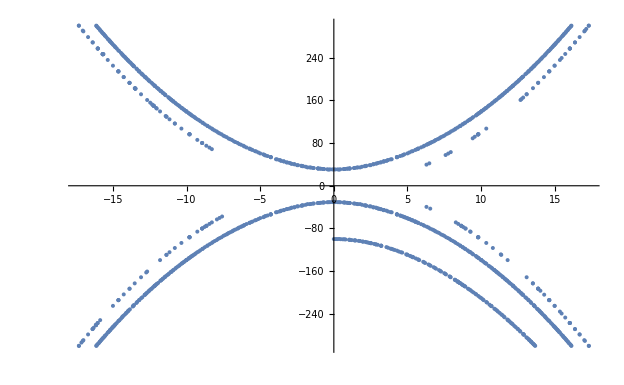

```mathematica
ListPlot[{{-17.31054021564049,-300.},{-17.315899476383507,-299.95508449359374},{-17.142857142857142,-293.873814174107},{-17.049560546875,-290.68516322544644},{-17.008579799107146,-289.2857142857143},{-16.690499441964285,-278.57142857142856},{-16.384517695062076,-268.5179488597833},{-16.38363122942811,-268.4934960286062},{-16.313650948660708,-266.13333565848217},{-16.160358253231802,-261.17697488059287},{-16.159862900990106,-261.17348505657696},{-16.159726126883832,-261.1657675800842},{-16.15951254899122,-261.15817993963816},{-16.047101702008923,-257.5077601841517},{-16.03567940848214,-257.14285714285717},{-15.867919921875,-251.7857142857143},{17.31054021564075,300.},{17.315899476383628,299.95508449359494},{17.142857142857146,293.873814174107},{17.049560546875,290.68516322544644},{17.008579799107146,289.2857142857143},{16.690499441964292,278.57142857142856},{16.375100959095324,268.65919989928443},{16.37780882659563,268.49309098296715},{16.03365628038849,257.20452202035966},{16.029299818127846,257.1918607091365},{16.015825155668217,257.1428571428571},{16.028395008648086,257.0867081402748},{15.714285714285719,246.93603515625},{15.468699171264566,239.398083859603},{15.353306361607148,235.7142857142857},{14.990411829444605,225.13349479755328},{14.992599101603572,224.99482009172527},{14.636038742332376,214.35512630335543},{14.631233841063203,214.33922340532712},{14.619029748431208,214.28571428571428},{14.267926897321432,203.57142857142856},{13.879732616294412,192.91554832970635},{13.868665024319643,192.85714285714283},{13.522949218750005,182.87004743303567},{-15.000348772321429,-225.00523158482144},{-14.636038742332342,-214.3551263033564},{-14.631233841063104,-214.33922340532786},{-14.619029748430947,-214.2857142857143},{-14.267926897321427,-203.5714285714286},{-13.879732616294264,-192.91554832970755},{-13.868665024319284,-192.8571428571429},{-13.522949218749998,-182.87004743303572},{-10.351213727678568,-107.14285714285715},{-9.81636681288849,-96.49514608159548},{-9.790472856312054,-96.67930854503078},{-9.80089300489773,-96.42857142857144},{-9.80109261043682,-96.316800529727},{-9.270542689732142,-85.94185965401786},{-8.947597728431148,-80.16323417413176},{-8.944293893718642,-80.12130587993464},{-8.940185394813495,-80.07276114758479},{-8.780953499802505,-77.21426893153382},{-8.659091092684266,-75.06639108312531},{-8.65635901059339,-75.03839615888535},{-8.652609209375804,-75.},{-8.448239062058855,-71.49069978340287},{-8.283168247767854,-68.609619140625},{-10.798339843749998,-116.59633091517857},{-11.159667968749998,-124.53787667410715},{-11.36663468485469,-129.37264957331598},{-11.369487181724494,-129.45769227413254},{-11.802106584821429,-139.28571428571428},{10.351213727678575,-107.14285714285715},{9.816366812888596,-96.4951460815935},{9.790472856312917,-96.67930854502342},{9.800893004898294,-96.42857142857144},{9.801092610437374,-96.3168005297303},{9.285714285714288,-86.22174944196429},{9.258335658482146,-85.71428571428572},{8.944293893718738,-80.12130587993325},{8.940185394813694,-80.07276114758463},{8.780953499802683,-77.21426893153127},{8.659091092684298,-75.0663910831236},{8.656359010593492,-75.03839615888435},{8.652609209376001,-75.},{8.44823906205899,-71.49069978340094},{8.283168247767858,-68.609619140625},{10.798339843750005,-116.59633091517857},{11.33893694196429,-128.57142857142858},{11.369487181724628,-129.45769227413066},{11.802106584821432,-139.28571428571428},{-10.351213727678568,107.14285714285712},{-9.816366812888509,96.49514608159505},{-9.790472856312224,96.67930854502927},{-9.800893004897842,96.42857142857142},{-9.80109261043693,96.31680052972764},{-9.270542689732142,85.94185965401783},{-8.947597728431152,80.16323417413075},{-8.945241127852897,80.10709736792076},{-8.940185394813573,80.0727611475847},{-8.660365513392856,74.99999999999997},{-8.448239062058887,71.49069978340236},{-8.283168247767854,68.60961914062497},{-10.798339843749998,116.59633091517854},{-11.366634684854729,129.372649573316},{-11.369487181724521,129.45769227413214},{-11.421036503231552,130.70842382709668},{-11.802106584821429,139.28571428571428},{-10.798339843749998,116.59633091517854},{-11.159667968749998,124.53787667410712},{10.351213727678575,107.14285714285712},{9.816366812888615,96.49514608159308},{9.811117787749543,96.48007355108578},{9.800893004898406,96.42857142857142},{9.801092610437482,96.31680052973093},{9.780308683522696,96.03352520783426},{9.56880937953555,91.86071801945948},{9.429495675223219,88.91470772879461},{-15.703299386160715,246.5933663504464},{-15.695622247276129,246.4642778144276},{-15.689432310121113,246.5584690534415},{-15.644987345289621,246.69721183633808},{-15.67852801017421,246.4285714285714},{-15.683361608577986,246.35478347836147},{-15.353306361607144,235.7142857142857},{-15.703299386160715,246.5933663504464},{-16.028395008647934,257.0867081402737},{-16.02951261222799,257.1428571428571},{-16.02929981812771,257.19186070913753},{-16.03365628038845,257.2045220203609},{-16.37780882659563,268.49309098296715},{-16.375100959095324,268.65919989928443},{-16.690499441964285,278.57142857142856},{-17.008579799107146,289.2857142857143},{-17.049560546875,290.68516322544644},{-17.315899476383507,299.95508449359374},{-17.31703351324652,300.},{13.093261718750005,-171.42857142857144},{13.51358945874255,-182.86259228241562},{13.519178800775865,-182.92660370264784},{13.875596941078992,-192.7658063470942},{13.868665024319565,-192.8571428571429},{13.879732616294381,-192.91554832970667},{13.884708709886707,-192.93721215879458},{14.026576450892861,-196.74421037946433},{-12.67752511160714,160.71428571428572},{-12.469122321425823,155.68612832901903},{-12.3431396484375,152.3529052734375},{-12.245895289378126,150.07278248798661},{-12.24373871828095,150.03384059593628},{-12.241039368782058,150.},{-12.228070270183728,149.81787390635986},{-12.06785714959725,145.76785704175552},{-12.026890345982142,144.64285714285714},{-13.093261718749998,171.42857142857142},{-13.477064070624728,182.04235320858496},{-13.477549416074883,182.1428571428571},{-13.48394021763025,182.1815513627338},{-13.488279117401365,182.20548718865604},{-13.492462090943388,182.20534182718475},{-13.519178800775823,182.92660370264832},{-13.875596941078863,192.76580634709316},{-13.868665024319363,192.85714285714283},{-13.879732616294294,192.91554832970724},{-14.267926897321427,203.57142857142856},{-13.093261718749998,-171.42857142857144},{-12.74127195707188,-162.4523492153504},{-12.67752511160714,-160.71428571428572},{13.093261718750005,171.42857142857142},{12.741271957071941,162.45234921534947},{12.677525111607148,160.71428571428572},{13.093261718750005,171.42857142857142},{12.857142857142861,165.30238560267856},{-15.000348772321429,225.00523158482144},{-14.636038742332348,214.3551263033562},{-14.631233841063123,214.3392234053277},{-14.631093063814818,214.28571428571428},{-14.629204091225823,214.21688479386455},{-14.274030412946427,203.74668666294644},{16.690499441964292,-278.57142857142856},{16.375100959095267,-268.6591998992854},{16.377808826595587,-268.4930909829672},{16.033656280388485,-257.20452202036},{16.029299818127814,-257.19186070913685},{16.015825155668118,-257.14285714285717},{16.021420387791792,-256.99712458214634},{15.714285714285719,-246.93603515625006},{15.468699171264541,-239.39808385960342},{15.353306361607148,-235.71428571428572},{14.996943843269056,-225.03545857675857},{14.992599101603572,-224.99482009172527},{14.63603874233237,-214.35512630335566},{14.631233841063183,-214.3392234053273},{14.619029748431156,-214.2857142857143},{14.621047486971689,-214.11222395733395},{14.28571428571429,-204.07889229910722},{16.690499441964292,-278.57142857142856},{17.008579799107146,-289.2857142857143},{17.049560546875,-290.68516322544644},{17.315899476383628,-299.95508449359494},{17.317033513246614,-300.},{-7.93997628348214,-63.04321289062501},{-7.764404445702623,-60.31964760017492},{-7.589111328124998,-57.59190150669644},{6.290544782366075,-39.570399693080375},{6.546630859375003,-42.85714285714287},{6.290544782366075,39.57039969308035},{6.4835030691964315,42.03316824776784},{7.939976283482145,63.04321289062498},{7.76440444570309,60.319647600167954},{7.5891113281250036,57.59190150669641},{-16.13259631843635,-300.},{-16.116735098202504,-299.32040209839096},{-16.07142857142857,-297.72048889142235},{-16.00187655181547,-295.6861374370536},{-15.956952400615652,-294.6428571428571},{-15.887688327742332,-292.0418179410078},{-15.876867794366913,-291.7244454869322},{-15.795197785525374,-289.2857142857143},{-15.773844553633587,-288.3923316954962},{-15.714285714285714,-286.36393285014833},{-15.657284395808544,-284.783591205729},{-15.618798930950257,-283.92857142857144},{-15.55091965030743,-281.4780804688972},{-15.54204587721408,-281.15502612750305},{-15.451133250323934,-278.57142857142856},{-15.357142857142858,-275.2698290804363},{-15.307680801628027,-273.9562165470081},{-15.273117907385531,-273.2142857142857},{-15.209616080249992,-271.0013840608928},{-15.190946408372048,-270.35008958870503},{-15.178571428571429,-269.96329799143314},{-15.10477146728735,-267.8571428571429},{-15.072728445782507,-266.76621617040524},{-15.01819508106449,-265.17857142857144},{-15.,-264.56850748998},{-14.952779277682868,-263.20831083475696},{-14.918967404572173,-262.5},{-14.854443679743648,-260.3166551961547},{-14.834188301789743,-259.63003261601096},{-14.741322895661357,-257.14285714285717},{-14.642857142857142,-253.81688230283652},{-14.588892055951778,-252.5951905892948},{-14.555604192943747,-251.7857142857143},{-14.458247209751237,-249.0165652891257},{-14.37453233320413,-246.42857142857144},{-14.356509622897535,-245.3666413708227},{-14.285714285714285,-243.45603319368368},{-14.182551592071531,-241.07142857142858},{-14.1026417822063,-238.46037326690552},{-14.090527849333922,-238.14363202572318},{-13.999091237627592,-235.71428571428572},{-13.979455845656984,-234.95101945800238},{-13.928571428571427,-233.35544621138695},{-13.8500955930711,-231.53428038964776},{-13.653263931531713,-226.22753040154717},{-13.618615406878494,-225.},{-13.60665977400123,-224.4715319614101},{-13.57142857142857,-223.54841486852484},{-13.406717781034935,-219.64285714285717},{-13.352050340898025,-217.57638774367246},{-13.219664136744315,-214.2857142857143},{-13.214285714285712,-214.09983313260423},{-13.089530316187385,-210.79990240004636},{-13.00390363160006,-208.92857142857144},{-12.857142857142856,-204.6437722497792},{-12.825190736838003,-204.05071037600138},{-12.801608157171845,-203.5714285714286},{-12.736564319263358,-201.76275050323613},{-12.696082198951068,-200.63019558716258},{-12.590910978751761,-198.21428571428575},{-12.563634203658474,-197.25977265940867},{-12.5,-195.45925329564906},{-12.429399648520668,-193.91614812933287},{-12.372709825712786,-192.8571428571429},{-12.294494633188256,-190.58258050217617},{-12.204014216277496,-188.41735610130533},{-12.166856489217228,-187.50000000000003},{-12.159965203469806,-187.24337909081007},{-12.142857142857142,-186.8040075741986},{-12.055914434973465,-184.8214285714286},{-12.024070992989975,-183.9246493908647},{-11.935057318207772,-182.14285714285717},{-11.785714285714285,-178.07574751034335},{-11.747681747184698,-177.3562023636581},{-11.713403766332078,-176.7857142857143},{-11.612776391759374,-174.19164587639068},{-11.60868573813642,-174.08399964223943},{-11.487715413455856,-171.42857142857144},{-11.46958683860808,-170.81334027802166},{-11.428571428571427,-169.68354449299144},{-11.328359386457604,-167.5746092031359},{-11.24610811977473,-166.07142857142858},{-11.185708230602597,-164.35723368381818},{-11.07142857142857,-161.65777355068994},{-11.042105988557536,-161.15412445735123},{-11.013663124102994,-160.71428571428572},{-10.914989068184672,-158.36769316562726},{-10.89807148030685,-157.95749922396865},{-10.771887530326332,-155.35714285714286},{-10.714285714285712,-153.72754751778044},{-10.607201900085592,-151.6062572130018},{-10.515386921874104,-150.},{-10.459236584840482,-148.46859408453557},{-10.357142857142854,-146.12637704769196},{-10.310012624509405,-145.3498106323589},{-10.27159922158747,-144.64285714285714},{-10.178571428571427,-142.58855042685101},{-10.159704734823757,-142.24728612050077},{-10.047880392690084,-140.00392017606555},{-10.013619413964395,-139.28571428571428},{-10.008830811986517,-139.1532521059165},{-9.999999999999998,-138.95861128025794},{-9.878579934243408,-136.60714285714286},{-9.857194512965146,-136.07065373409424},{-9.82142857142857,-135.3276899721859},{-9.743525663601345,-133.92857142857144},{-9.703707951986788,-133.01580929162674},{-9.642857142857142,-131.82268954235408},{-9.608579997898742,-131.25},{-9.548579832747432,-129.98558822307422},{-9.45753377299761,-128.57142857142858},{-9.391937635474386,-126.97807832502706},{-9.285714285714285,-124.74565236144471},{-9.177380721047218,-123.21428571428572},{-9.07434254189064,-121.02771901449752},{-8.928571428571427,-118.27569638660675},{-8.894963965807676,-117.85714285714286},{-8.758126881283555,-115.05666820931808},{-8.597172996807767,-112.5},{-8.57142857142857,-111.8410299113697},{-8.423653245356917,-109.35948703393194},{-8.282371946025187,-107.14285714285715},{-8.214285714285712,-105.54670073779693},{-8.09276983537208,-103.60845246941878},{-7.95879255522577,-101.7857142857143},{-7.857142857142855,-99.57409428016972},{-7.750667100436985,-98.02570777915949},{-7.624764823716887,-96.42857142857144},{-7.499999999999998,-93.87320374014683},{-7.401866781085896,-92.54342685514011},{-7.278321077062512,-91.07142857142858},{-7.22113201801403,-89.89730544407524},{-7.142857142857141,-88.41755584766784},{-7.041927532513184,-87.22822986944507},{-6.917459711297235,-85.71428571428572},{-6.860719862664244,-84.58920206003631},{-6.785714285714283,-83.19930442873365},{-6.677427859254082,-81.98143925404588},{-6.540376732565945,-80.35714285714286},{-6.4919488802108765,-79.40648108255111},{-6.428571428571426,-78.23097808618243},{-6.304150080996574,-76.8663202136228},{-6.249999999999998,-76.12856104623494},{-6.152284922827194,-75.},{-6.113855854453973,-74.36359075461894},{-6.071428571428569,-73.55563612337183},{-5.932912891317957,-71.72059234451632},{-5.732120832539565,-69.64285714285714},{-5.714285714285712,-69.27452907364855},{-5.61259652992565,-68.11751937745622},{-5.527098769766796,-67.09351845349804},{-5.357142857142854,-64.88964183610764},{-5.275566991541669,-64.28571428571429},{-5.127598248415211,-62.371740559486085},{-4.999999999999997,-60.58388517068343},{-4.7888978636198996,-58.92857142857144},{-4.715164607938179,-57.84395945235587},{-4.642857142857141,-56.70067506506976},{-4.502238251425673,-55.68071194290059},{-4.2943119418008635,-53.700393412727294},{-4.285714285714283,-53.60986860719936},{-4.2838631257884225,-53.59919597031649},{-4.2786831747420395,-53.571428571428584},{-3.9285714285714257,-49.72811909050577},{-3.8502370041774867,-49.38930208019481},{-3.6843373886331356,-48.21428571428572},{-3.6238389809542384,-47.428129571400675},{-3.5714285714285685,-46.619384732350454},{-3.4057965258862652,-45.729805031151166},{-3.3885890425436735,-45.5997357904163},{-3.2142857142857117,-43.78903198588921},{-3.160790002964164,-43.65957852696608},{-3.017457869454986,-42.85714285714287},{-2.922958621126528,-41.869906397387766},{-2.8571428571428545,-40.95252625442738},{-2.6947590721245316,-40.42138608186802},{-2.671852446719504,-40.279356156350275},{-2.4999999999999973,-38.61634655834907},{-2.4302506270901256,-38.546240593648086},{-2.209909692440334,-37.500000000000014},{-2.1692009748337573,-37.10484252035075},{-2.14285714285714,-36.71907961858294},{-2.0844004761510764,-36.62314999940906},{-1.9103324149538659,-35.630728061406266},{-1.785714285714283,-34.35768526033771},{-1.6343189437618222,-34.41378727214407},{-1.5569785482724492,-34.068963938372505},{-1.428571428571426,-33.4526081076753},{-1.3594542109758385,-33.179615406790965},{-1.0903399396917293,-32.42652766680456},{-1.0714285714285687,-32.37033108724292},{-1.058334917664771,-32.33926194931412},{-0.9577715401078373,-32.14285714285715},{-0.8928571428571401,-31.88943178046796},{-0.7585687600532967,-31.478611456343376},{-0.7142857142857116,-31.374714425309968},{-0.6562271955763698,-31.271979362217024},{-0.44174827190928145,-30.87377592136075},{-0.3571428571428545,-30.774219801592043},{-0.26146922980151294,-30.70775273273703},{-0.10181462374970779,-30.615637786611497},{2.6645352591003757*^-15,-29.94184584869288},{0.10181462374971298,-30.6156377866115},{0.26146922980151843,-30.70775273273703},{0.3571428571428598,-30.77421980159205},{0.44174827190928667,-30.87377592136075},{0.6562271955763758,-31.271979362217035},{0.714285714285717,-31.37471442530998},{0.7585687600533012,-31.47861145634339},{0.8928571428571455,-31.88943178046797},{0.957771540107839,-32.14285714285715},{1.0583349176647756,-32.33926194931413},{1.071428571428574,-32.370331087242924},{1.0903399396917355,-32.426527666804574},{1.3594542109758427,-33.17961540679098},{1.4285714285714313,-33.452608107675324},{1.556978548272457,-34.06896393837254},{1.634318943761826,-34.41378727214409},{1.7857142857142883,-34.35768526033774},{1.91033241495387,-35.63072806140629},{2.0844004761510857,-36.62314999940912},{2.1428571428571455,-36.71907961858299},{2.169200974833761,-37.104842520350786},{2.209909692440334,-37.500000000000014},{2.4302506270901296,-38.54624059364811},{2.5000000000000027,-38.6163465583491},{2.671852446719508,-40.279356156350296},{2.69475907212454,-40.42138608186807},{2.85714285714286,-40.95252625442743},{2.9229586211265315,-41.869906397387794},{3.032587820405883,-42.85714285714287},{3.0357142857142883,-42.873668631881785},{3.160790002964168,-43.6595785269661},{3.214285714285717,-44.06177378861082},{3.377359648810834,-45.53571428571429},{3.388589042543677,-45.59973579041632},{3.405796525886276,-45.72980503115125},{3.571428571428574,-46.61938473235051},{3.684337388633136,-48.21428571428572},{3.85023700417749,-49.389302080194845},{3.928571428571431,-49.728119090505814},{4.278683174742039,-53.571428571428584},{4.283667530843261,-53.60212989449399},{4.285714285714288,-53.609868607199395},{4.294311941800877,-53.700393412727415},{4.502238251425676,-55.68071194290063},{4.544254677816794,-56.250000000000014},{4.642857142857146,-57.103211568041424},{4.715164607938181,-57.843959452355904},{4.803052075474248,-58.92857142857144},{4.821428571428575,-59.07961394531977},{4.9232934666598585,-60.0791694286736},{5.000000000000003,-60.95781849013677},{5.047092350045029,-61.60714285714286},{5.1275982484152145,-62.37174055948611},{5.178571428571431,-62.92173266928075},{5.2827433659497585,-64.28571428571429},{5.328722697143487,-64.71201668570488},{5.357142857142859,-65.00435652959895},{5.512924680437443,-66.96428571428572},{5.527098769766799,-67.09351845349806},{5.535714285714288,-67.17886905897998},{5.6125965299256775,-68.11751937745655},{5.714285714285717,-69.27452907364864},{5.732120832539565,-69.64285714285714},{5.920829669312934,-71.90184067459174},{6.071428571428575,-73.55563612337191},{6.145620727707166,-75.},{6.312067546636958,-76.74755822901712},{6.4285714285714315,-78.2309780861825},{6.540376732565945,-80.35714285714286},{6.68291271342369,-81.89916644150185},{6.785714285714288,-83.19930442873373},{6.860719862664246,-84.58920206003636},{6.917459711297236,-85.71428571428572},{7.041927532513187,-87.22822986944512},{7.142857142857146,-88.41755584766791},{7.278321077062512,-91.07142857142858},{7.401866781085898,-92.54342685514015},{7.5000000000000036,-93.87320374014693},{7.6247648237168875,-96.42857142857144},{7.7506671004369885,-98.02570777915953},{7.85714285714286,-99.57409428016982},{7.95879255522577,-101.7857142857143},{8.092769835372083,-103.60845246941882},{8.214285714285717,-105.54670073779701},{8.282371946025188,-107.14285714285715},{8.423653245356919,-109.35948703393198},{8.571428571428575,-111.84102991136979},{8.59717299680777,-112.5},{8.751105949679452,-115.16198218337969},{8.759272654811822,-115.3176612507487},{8.894963965807674,-117.85714285714286},{8.92857142857143,-118.27569638660681},{9.074342541890642,-121.02771901449755},{9.177380721047218,-123.21428571428572},{9.233850013212482,-123.99224980181282},{9.285714285714288,-124.74565236144478},{9.391937635474388,-126.97807832502708},{9.45753377299761,-128.57142857142858},{9.642857142857146,-131.57934120602377},{9.703707951986791,-133.01580929162677},{9.743525663601345,-133.92857142857144},{9.821428571428575,-135.32768997218602},{9.857194512965147,-136.07065373409426},{10.000000000000004,-138.9165191924739},{10.008830811986519,-139.15325210591655},{10.012862369517292,-139.28571428571428},{10.047880392690072,-140.0039201760653},{10.15970473482376,-142.2472861205008},{10.263092896962286,-144.64285714285714},{10.308715514088393,-145.36926728867417},{10.357142857142861,-146.1263770476921},{10.515386921874104,-150.},{10.607201900085593,-151.60625721300187},{10.714285714285719,-153.7275475177806},{10.771887530326334,-155.35714285714286},{10.898071480306852,-157.9574992239687},{10.900656866059776,-158.03571428571428},{10.91498906818466,-158.36769316562697},{11.019174609107068,-160.71428571428572},{11.042223319665764,-161.1523644907279},{11.071428571428577,-161.74703672334394},{11.13877752498724,-163.39285714285717},{11.185708230602598,-164.35723368381824},{11.24610811977473,-166.07142857142858},{11.328359386457606,-167.57460920313596},{11.428571428571432,-169.68354449299156},{11.469586838608082,-170.81334027802168},{11.487715413455858,-171.42857142857144},{11.608685738136423,-174.0839996422395},{11.612776391759365,-174.19164587639045},{11.713403766332076,-176.7857142857143},{11.7476817471847,-177.35620236365813},{11.785714285714288,-178.07574751034343},{11.886359118451102,-180.63318465180498},{11.935057318207772,-182.14285714285717},{12.024070992989975,-183.92464939086474},{12.142857142857146,-186.73082619981653},{12.159965203469808,-187.2433790908101},{12.16789475964199,-187.50000000000003},{12.204014216277493,-188.41735610130522},{12.294494633188258,-190.5825805021762},{12.372709825712786,-192.8571428571429},{12.500000000000004,-195.45925329564915},{12.563634203658474,-197.2597726594087},{12.590910978751761,-198.21428571428575},{12.69608219895107,-200.63019558716263},{12.736564319263351,-201.76275050323596},{12.801608157171845,-203.5714285714286},{12.825190736838005,-204.05071037600143},{12.857142857142861,-204.64377224977932},{13.00390363160006,-208.92857142857144},{13.089530316187389,-210.79990240004642},{13.214285714285719,-214.09983313260443},{13.219664136744317,-214.2857142857143},{13.352050340898028,-217.5763877436725},{13.406717781034937,-219.64285714285717},{13.571428571428577,-223.54841486852501},{13.602518565509467,-224.53365008878666},{13.614398600402806,-225.},{13.65326393153171,-226.227530401547},{13.799598322891173,-230.35714285714286},{13.850095593071103,-231.53428038964785},{13.928571428571434,-233.35544621138715},{13.979455845656986,-234.95101945800243},{13.999091237627592,-235.71428571428572},{14.090527849333913,-238.14363202572295},{14.1026417822063,-238.46037326690558},{14.182551592071531,-241.07142857142858},{14.28571428571429,-243.4560331936838},{14.349826520474878,-245.46688790716263},{14.374532333204131,-246.42857142857144},{14.458247209751233,-249.0165652891256},{14.555604192943747,-251.7857142857143},{14.58889205595178,-252.59519058929482},{14.642857142857146,-253.8168823028366},{14.741322895661357,-257.14285714285717},{14.83435129467357,-259.6275877227537},{14.918967404572173,-262.5},{14.95277927768287,-263.208310834757},{15.000000000000004,-264.5685074899801},{15.01819508106449,-265.17857142857144},{15.07272844578251,-266.7662161704053},{15.104771467287348,-267.8571428571429},{15.178571428571432,-269.96329799143325},{15.19094640837205,-270.3500895887051},{15.20961608024999,-271.0013840608927},{15.273117907385531,-273.2142857142857},{15.30768080162803,-273.9562165470082},{15.357142857142861,-275.2698290804364},{15.451133250323934,-278.57142857142856},{15.542045877214083,-281.1550261275031},{15.550919650307426,-281.4780804688971},{15.618798930950257,-283.92857142857144},{15.657284395808546,-284.78359120572907},{15.714285714285719,-286.3639328501485},{15.77384455363359,-288.39233169549624},{15.795197785525374,-289.2857142857143},{15.876867794366907,-291.72444548693204},{15.887688327742334,-292.0418179410079},{15.956952400615652,-294.6428571428571},{16.00187655181547,-295.6861374370537},{16.071428571428577,-297.7204888914226},{16.116735098202508,-299.32040209839107},{16.132596318436352,-300.},{16.132596318436352,300.},{16.116735098202508,299.32040209839107},{16.071428571428577,297.7204888914226},{16.00187655181547,295.6861374370537},{15.956952400615652,294.6428571428571},{15.887688327742334,292.0418179410079},{15.876867794366907,291.72444548693204},{15.795197785525374,289.2857142857143},{15.77384455363359,288.39233169549624},{15.714285714285719,286.3639328501485},{15.657284395808546,284.78359120572907},{15.618798930950257,283.92857142857144},{15.550919650307426,281.4780804688971},{15.542045877214083,281.1550261275031},{15.451133250323934,278.57142857142856},{15.357142857142861,275.2698290804364},{15.30768080162803,273.9562165470082},{15.27311790738553,273.21428571428567},{15.209616080249983,271.00138406089246},{15.190946408372046,270.35008958870503},{15.10001035956197,267.85714285714283},{15.072728445782507,266.7662161704053},{15.01819508106449,265.17857142857144},{15.000000000000004,264.5685074899801},{14.95277927768287,263.208310834757},{14.918967404572173,262.5},{14.854443679743644,260.3166551961546},{14.834188301789744,259.630032616011},{14.741322895661355,257.1428571428571},{14.714133199313238,256.07371629601573},{14.642857142857146,253.8168823028366},{14.588892055951778,252.59519058929476},{14.555604192943745,251.78571428571425},{14.45824720975123,249.01656528912548},{14.37453233320413,246.4285714285714},{14.356509622897535,245.3666413708227},{14.28571428571429,243.4560331936838},{14.182551592071531,241.07142857142856},{14.1026417822063,238.46037326690555},{14.09052784933391,238.14363202572284},{13.99909123762759,235.7142857142857},{13.928571428571434,233.35544621138715},{13.853740371751478,231.4796087094422},{13.799598322891171,230.35714285714283},{13.727671504990235,228.01349885371798},{13.66792547308798,226.44745352489105},{13.614398600402806,225.},{13.602518565509467,224.53365008878663},{13.571428571428577,223.66906807189403},{13.516779763670963,222.32142857142856},{13.475079995109049,221.08808578765007},{13.419162922199478,219.64285714285714},{13.392857142857148,218.84945085666334},{13.346428098604205,217.66072137807987},{13.225858156572977,214.45930092002314},{13.219664136744315,214.28571428571428},{13.214285714285719,214.09983313260446},{13.089530316187387,210.7999024000464},{13.00390363160006,208.92857142857142},{12.857142857142861,204.64377224977932},{12.825190736838005,204.0507103760014},{12.801608157171842,203.57142857142856},{12.736564319263346,201.76275050323582},{12.696082198951068,200.63019558716258},{12.59091097875176,198.2142857142857},{12.563634203658474,197.25977265940867},{12.500000000000004,195.45925329564915},{12.429399648520668,193.91614812933287},{12.372709825712782,192.85714285714283},{12.294494633188256,190.58258050217617},{12.204014216277486,188.41735610130507},{12.166856489217226,187.49999999999997},{12.159965203469806,187.24337909081007},{12.142857142857146,186.8040075741987},{12.055914434973463,184.82142857142856},{12.024070992989975,183.9246493908647},{11.93505731820777,182.1428571428571},{11.8863591184511,180.63318465180492},{11.785714285714288,178.07574751034343},{11.7476817471847,177.35620236365813},{11.713403766332076,176.78571428571428},{11.61277639175936,174.1916458763903},{11.60868573813642,174.08399964223946},{11.487715413455856,171.42857142857142},{11.469586838608082,170.81334027802168},{11.428571428571432,169.84695136932106},{11.375005928702674,168.75},{11.328359386457606,167.57460920313596},{11.26004478958106,166.07142857142856},{11.250000000000004,165.80453471743226},{11.185708230602598,164.3572336838182},{11.071428571428577,161.65777355069008},{11.013663124102992,160.71428571428572},{10.91498906818466,158.36769316562697},{10.898071480306852,157.9574992239687},{10.771887530326334,155.35714285714286},{10.714285714285719,153.7275475177806},{10.607201900085593,151.60625721300187},{10.515386921874104,150.},{10.459236584840486,148.46859408453562},{10.357142857142861,146.1263770476921},{10.310012624509406,145.34981063235895},{10.27159922158747,144.64285714285714},{10.178571428571432,142.58855042685113},{10.15970473482376,142.2472861205008},{10.047880392690072,140.0039201760653},{10.013619413964397,139.28571428571428},{10.008830811986519,139.15325210591655},{10.000000000000004,138.95861128025805},{9.878579934243408,136.60714285714283},{9.857194512965147,136.07065373409426},{9.821428571428575,135.32768997218602},{9.743525663601343,133.92857142857142},{9.70370795198679,133.01580929162677},{9.642857142857146,131.5793412060238},{9.457533772997609,128.57142857142856},{9.391937635474388,126.97807832502707},{9.285714285714288,124.74565236144478},{9.23385001321248,123.9922498018128},{9.177380721047216,123.2142857142857},{9.074342541890642,121.02771901449753},{8.92857142857143,118.2756963866068},{8.894963965807674,117.85714285714283},{8.759272654811813,115.31766125074856},{8.751105949679452,115.16198218337968},{8.597172996807767,112.49999999999997},{8.58829729730324,112.24696911187999},{8.571428571428575,111.8410299113698},{8.423653245356919,109.35948703393197},{8.282371946025187,107.14285714285712},{8.214285714285717,105.54670073779702},{8.092769835372081,103.60845246941881},{7.958792555225768,101.78571428571428},{7.85714285714286,99.57409428016982},{7.750667100436987,98.02570777915952},{7.624764823716886,96.42857142857142},{7.5000000000000036,93.87320374014693},{7.401866781085897,92.54342685514014},{7.27832107706251,91.07142857142856},{7.221132018014032,89.89730544407527},{7.142857142857146,88.41755584766793},{7.041927532513186,87.2282298694451},{6.9174597112972345,85.7142857142857},{6.860719862664245,84.58920206003634},{6.785714285714288,83.19930442873373},{6.677427859254083,81.98143925404591},{6.607142857142859,81.01240437061999},{6.550775454124466,80.35714285714283},{6.491948880210878,79.40648108255112},{6.4285714285714315,78.54004758657499},{6.35401148635549,77.6785714285714},{6.304150080996576,76.86632021362283},{6.145620727707164,74.99999999999997},{6.071428571428575,73.55563612337191},{5.920829669312933,71.90184067459172},{5.732120832539564,69.64285714285711},{5.724747396909399,69.48593190350188},{5.714285714285717,69.27452907364865},{5.612596529925687,68.11751937745667},{5.527098769766798,67.09351845349805},{5.357142857142859,64.88964183610769},{5.275566991541664,64.28571428571426},{5.127598248415213,62.3717405594861},{5.000000000000003,60.58388517068348},{4.788897863619898,58.92857142857141},{4.71516460793818,57.8439594523559},{4.642857142857146,56.70067506506983},{4.502238251425674,55.68071194290062},{4.294311941800882,53.70039341272746},{4.285714285714288,53.60986860719939},{4.283863125788425,53.5991959703165},{4.278683174742035,53.571428571428555},{3.928571428571431,49.728119090505814},{3.8502370041774885,49.38930208019483},{3.684337388633133,48.214285714285694},{3.6238389809542406,47.428129571400696},{3.571428571428574,46.61938473235052},{3.405796525886278,45.72980503115125},{3.388589042543676,45.599735790416304},{3.377359648810832,45.53571428571426},{3.214285714285717,44.06177378861082},{3.1607900029641667,43.659578526966094},{3.017457869454982,42.85714285714284},{2.9229586211265297,41.86990639738779},{2.85714285714286,41.40209417131263},{2.6947590721245427,40.421386081868086},{2.671852446719507,40.27935615635028},{2.5000000000000027,38.61634655834909},{2.4302506270901283,38.5462405936481},{2.209909692440331,37.499999999999986},{2.16920097483376,37.10484252035077},{2.1428571428571455,36.71907961858299},{2.084400476151088,36.62314999940912},{1.910332414953869,35.63072806140627},{1.7857142857142883,34.357685260337725},{1.6343189437618242,34.41378727214409},{1.5569785482724603,34.06896393837256},{1.4285714285714313,33.452608107675324},{1.3594542109758414,33.17961540679097},{1.0903399396917373,32.426527666804574},{1.071428571428574,32.37033108724292},{1.0583349176647745,32.33926194931412},{0.9577715401078291,32.142857142857125},{0.8928571428571455,31.88943178046798},{0.7585687600532991,31.47861145634339},{0.714285714285717,31.374714425309985},{0.6562271955763785,31.27197936221705},{0.4417482719092848,30.87377592136075},{0.3571428571428598,30.187435183900767},{0.2614692298015204,30.707752732737035},{0.10181462374971112,30.615637786611497},{2.6645352591003757*^-15,30.592589815864617},{-0.10181462374970587,30.615637786611497},{-0.26146922980151494,30.70775273273703},{-0.3571428571428545,30.187435183900764},{-0.4417482719092797,30.873775921360746},{-0.6562271955763725,31.27197936221704},{-0.7142857142857116,31.374714425309975},{-0.7585687600532944,31.478611456343383},{-0.8928571428571401,31.88943178046797},{-0.9577715401078263,32.142857142857125},{-1.0583349176647696,32.339261949314114},{-1.0714285714285687,32.37033108724291},{-1.0903399396917313,32.42652766680456},{-1.359454210975837,33.17961540679096},{-1.428571428571426,33.45260810767531},{-1.5569785482724523,34.06896393837252},{-1.6343189437618204,34.41378727214407},{-1.785714285714283,34.35768526033771},{-1.9103324149538647,35.63072806140626},{-2.08440047615108,36.62314999940908},{-2.14285714285714,36.71907961858295},{-2.169200974833756,37.10484252035075},{-2.2099096924403296,37.499999999999986},{-2.4302506270901247,38.54624059364808},{-2.4999999999999973,38.616346558349065},{-2.671852446719503,40.27935615635027},{-2.6947590721245342,40.421386081868036},{-2.8571428571428545,40.95252625442739},{-2.9229586211265266,41.86990639738776},{-3.017457869454982,42.85714285714284},{-3.1607900029641627,43.65957852696607},{-3.2142857142857117,43.78903198588921},{-3.388589042543672,45.59973579041628},{-3.4057965258862684,45.72980503115119},{-3.5714285714285685,46.61938473235047},{-3.623838980954237,47.42812957140067},{-3.684337388633132,48.214285714285694},{-3.8502370041774854,49.3893020801948},{-3.9285714285714257,49.72811909050577},{-4.278683174742036,53.571428571428555},{-4.283667530843257,53.60212989449395},{-4.285714285714283,53.60986860719935},{-4.294311941800869,53.70039341272734},{-4.5022382514256725,55.68071194290058},{-4.642857142857141,56.70067506506977},{-4.715164607938178,57.84395945235586},{-4.788897863619897,58.92857142857141},{-4.999999999999997,60.58388517068342},{-5.12759824841521,62.37174055948607},{-5.275566991541665,64.28571428571426},{-5.357142857142854,64.88964183610763},{-5.527098769766795,67.09351845349802},{-5.612596529925661,68.11751937745635},{-5.714285714285712,69.27452907364855},{-5.732120832539563,69.64285714285711},{-5.932912891317956,71.7205923445163},{-6.071428571428569,73.55563612337184},{-6.145620727707163,74.99999999999997},{-6.304150080996572,76.86632021362279},{-6.428571428571426,78.23097808618243},{-6.540376732565942,80.35714285714283},{-6.682912713423685,81.89916644150179},{-6.785714285714283,83.19930442873365},{-6.917459711297234,85.7142857142857},{-7.041927532513183,87.22822986944506},{-7.142857142857141,88.41755584766784},{-7.27832107706251,91.07142857142856},{-7.401866781085895,92.5434268551401},{-7.499999999999998,93.87320374014685},{-7.624764823716885,96.42857142857142},{-7.750667100436984,98.02570777915948},{-7.857142857142855,99.57409428016973},{-7.958792555225768,101.78571428571428},{-8.09276983537208,103.60845246941876},{-8.214285714285712,105.54670073779693},{-8.282371946025185,107.14285714285712},{-8.423653245356917,109.35948703393193},{-8.57142857142857,111.8410299113697},{-8.597172996807767,112.49999999999997},{-8.758126881283554,115.05666820931806},{-8.894963965807674,117.85714285714283},{-8.928571428571427,118.27569638660675},{-9.07434254189064,121.0277190144975},{-9.177380721047216,123.2142857142857},{-9.285714285714285,124.74565236144471},{-9.399174734531009,126.86952183917771},{-9.45753377299761,128.57142857142856},{-9.548579832747432,129.98558822307422},{-9.642857142857142,131.5793412060237},{-9.703707951986788,133.01580929162674},{-9.743525663601343,133.92857142857142},{-9.82142857142857,135.32768997218594},{-9.857194512965144,136.0706537340942},{-9.999999999999998,138.9165191924738},{-10.008830811986517,139.1532521059165},{-10.01286236951729,139.28571428571428},{-10.047880392690084,140.00392017606555},{-10.159704734823757,142.24728612050077},{-10.178571428571427,142.58855042685101},{-10.27159922158747,144.64285714285714},{-10.310012624509405,145.3498106323589},{-10.357142857142854,146.12637704769196},{-10.459236584840482,148.46859408453557},{-10.515386921874104,150.},{-10.607201900085592,151.6062572130018},{-10.714285714285712,153.72754751778044},{-10.771887530326332,155.35714285714286},{-10.89807148030685,157.95749922396865},{-10.900656866059776,158.03571428571428},{-10.914989068184672,158.36769316562726},{-11.019174609107068,160.71428571428572},{-11.04222331966576,161.15236449072785},{-11.07142857142857,161.74703672334377},{-11.13877752498724,163.39285714285714},{-11.185708230602597,164.35723368381815},{-11.246108119774728,166.07142857142856},{-11.428571428571427,169.68354449299144},{-11.46958683860808,170.81334027802163},{-11.487715413455856,171.42857142857142},{-11.608685738136419,174.0839996422394},{-11.612776391759368,174.1916458763905},{-11.713403766332076,176.78571428571428},{-11.747681747184698,177.35620236365807},{-11.785714285714285,178.07574751034335},{-11.886359118451098,180.6331846518049},{-11.93505731820777,182.1428571428571},{-12.024070992989973,183.92464939086466},{-12.142857142857142,186.73082619981645},{-12.159965203469804,187.24337909081004},{-12.167894759641989,187.49999999999997},{-12.204014216277491,188.41735610130522},{-12.294494633188254,190.58258050217614},{-12.372709825712782,192.85714285714283},{-12.5,195.4592532956491},{-12.569643679550765,197.16963052102423},{-12.59091097875176,198.2142857142857},{-12.696082198951066,200.63019558716255},{-12.736564319263353,201.76275050323602},{-12.801608157171843,203.57142857142856},{-12.827065102559681,204.02259489017618},{-12.857142857142856,204.64377224977918},{-12.958637562880387,207.40615084250845},{-13.015088897543308,208.92857142857142},{-13.035714285714285,209.39559487527058},{-13.089530316187385,210.79990240004634},{-13.214285714285712,214.09983313260423},{-13.219664136744315,214.28571428571428},{-13.225858156572983,214.45930092002334},{-13.346428098604202,217.66072137807978},{-13.406717781034935,219.64285714285714},{-13.57142857142857,223.54841486852484},{-13.602518565509463,224.53365008878657},{-13.615972909683595,225.},{-13.667925473087989,226.44745352489127},{-13.727671504990232,228.0134988537179},{-13.799598322891171,230.35714285714283},{-13.853740371751474,231.47960870944212},{-13.928571428571427,233.35544621138698},{-13.979455845656982,234.95101945800238},{-13.99909123762759,235.7142857142857},{-14.090527849333919,238.14363202572304},{-14.102641782206298,238.4603732669055},{-14.182551592071531,241.07142857142856},{-14.226046500195885,241.96644535420452},{-14.285714285714285,243.45603319368368},{-14.349826520474874,245.46688790716254},{-14.374532333204128,246.4285714285714},{-14.458247209751232,249.0165652891256},{-14.588892055951776,252.59519058929473},{-14.642857142857142,253.81688230283652},{-14.741322895661355,257.1428571428571},{-14.834188301789743,259.63003261601096},{-14.854443679743648,260.3166551961547},{-14.918967404572173,262.5},{-15.,264.42269418779824},{-15.072728445782507,266.76621617040524},{-15.104771467287346,267.85714285714283},{-15.178571428571429,269.96329799143314},{-15.190946408372046,270.350089588705},{-15.209616080249987,271.0013840608926},{-15.27311790738553,273.21428571428567},{-15.307680801628027,273.9562165470081},{-15.357142857142858,275.2698290804363},{-15.451133250323934,278.57142857142856},{-15.54204587721408,281.15502612750305},{-15.55091965030743,281.4780804688972},{-15.618798930950257,283.92857142857144},{-15.657284395808544,284.783591205729},{-15.714285714285714,286.36393285014833},{-15.773844553633587,288.3923316954962},{-15.795197785525374,289.2857142857143},{-15.876867794366913,291.7244454869322},{-15.887688327742332,292.0418179410078},{-15.956952400615652,294.6428571428571},{-16.00187655181547,295.6861374370536},{-16.07142857142857,297.72048889142235},{-16.116735098202504,299.32040209839096},{-16.13259631843635,300.},{13.673990740523514,-300.},{13.639743017547135,-298.9752833082216},{13.58051543528006,-297.32142857142856},{13.571428571428577,-297.03403635622743},{13.513991305763602,-295.50441612783175},{13.480303655645978,-294.6428571428571},{13.392857142857148,-292.1328003564271},{13.388510955709636,-292.02947852149833},{13.376084966018539,-291.7127030617065},{13.279003811304465,-289.2857142857143},{13.261170182169225,-288.5824472674617},{13.214285714285719,-287.130958516862},{13.130143835896526,-285.1906996044093},{13.07423923848554,-283.92857142857144},{12.910330699089517,-279.3692462006284},{12.882988320410508,-278.57142857142856},{12.876000084909817,-278.28857015492423},{12.857142857142861,-277.69102315921555},{12.666905687596321,-273.2142857142857},{12.614124464382408,-271.5024187485497},{12.500000000000004,-268.44824518030293},{12.469322473504189,-267.8571428571429},{12.348212561383715,-264.77681157924434},{12.250087140682442,-262.5},{12.142857142857146,-259.31634702662933},{12.081281155136972,-258.06649695865974},{12.035344547468565,-257.14285714285717},{11.948575829077603,-254.69993399240744},{11.893248208973494,-253.3987231346024},{11.824085810257111,-251.7857142857143},{11.81334903692634,-251.37119301753353},{11.785714285714288,-250.5832411371826},{11.592714146530053,-246.42857142857144},{11.538318767919929,-244.78236133834397},{11.428571428571432,-242.05424639426946},{11.374020879052217,-241.07142857142858},{11.258896300960133,-238.2594126284552},{11.141991554591227,-235.71428571428572},{11.071428571428577,-233.68579970594243},{10.978204267084918,-231.75550742229774},{10.901922127436215,-230.35714285714286},{10.714285714285719,-225.71577561555125},{10.691658704947034,-225.3394051400803},{10.671430782209491,-225.},{10.570979664948933,-222.85040925994824},{10.403141187921548,-218.95288218117688},{10.357142857142861,-217.80468815649655},{10.168983724614064,-214.2857142857143},{10.107556287092322,-212.67236997932952},{10.000000000000004,-210.24806029473325},{9.91844356881326,-208.92857142857144},{9.809118539047564,-206.4346504857152},{9.6642475596876,-203.5714285714286},{9.642857142857146,-202.98590136097297},{9.504786529243528,-200.28534491849},{9.387846995175392,-198.21428571428575},{9.285714285714288,-195.73943645609432},{9.195574546860763,-194.20923893994578},{9.110820835230225,-192.8571428571429},{8.92857142857143,-188.9142809760732},{8.881504046662954,-188.20601072862718},{8.839798928888587,-187.50000000000003},{8.750000000000004,-185.70469586196722},{8.722171397775611,-185.2388576047945},{8.696368005598416,-184.8214285714286},{8.571428571428575,-182.44920164833866},{8.56150001479101,-182.29178549242062},{8.551833686387896,-182.14285714285717},{8.480605234050461,-180.82663577495742},{8.463788109395638,-180.5282502123631},{8.403967583915408,-179.46428571428572},{8.39942324852939,-179.36579412920207},{8.392857142857146,-179.23096230662998},{8.251671568749549,-176.7857142857143},{8.23619282469965,-176.45710762950532},{8.214285714285717,-175.96044955563303},{7.935139507151182,-171.42857142857144},{7.904701129127178,-170.71519734880667},{7.85714285714286,-169.7170302663193},{7.612847416699861,-166.07142857142858},{7.56893353908795,-165.0374254851094},{7.5000000000000036,-163.76803821189725},{7.279922797807368,-160.71428571428572},{7.224253784732254,-159.4933360861591},{7.142857142857146,-158.082433683816},{6.934107499142248,-155.35714285714286},{6.871909451036618,-154.0642153773079},{6.785714285714288,-152.6440311548061},{6.573099861856017,-150.},{6.511268907773242,-148.75953781197285},{6.4285714285714315,-147.4503300760849},{6.1946563322587975,-144.64285714285714},{6.141456796846029,-143.59243376159532},{6.071428571428575,-142.51417611686085},{5.796646086107361,-139.28571428571428},{5.758543064507394,-138.62185403238914},{5.714285714285717,-137.86913578675208},{5.564744745237922,-136.17168596428837},{5.37702717050673,-133.92857142857144},{5.3678851955368,-133.76743635266234},{5.357142857142859,-133.58133938679273},{5.259692396115128,-132.46681451315547},{5.16881437534218,-131.39635579843875},{5.000000000000003,-129.29764746084766},{4.969395206138913,-129.03050047934494},{4.912383860732568,-128.57142857142858},{4.642857142857146,-125.20345322877994},{4.555535420895998,-124.52411154370294},{4.410169303645468,-123.21428571428572},{4.285714285714288,-121.56344636045189},{4.125826663583103,-120.25545718911064},{4.023192299779081,-119.27645592525762},{3.928571428571431,-118.31599650693744},{3.8577314498218653,-117.85714285714286},{3.6837012851072903,-116.17305215196211},{3.571428571428574,-114.93359222187395},{3.2222763224460618,-112.5},{3.217648751308325,-112.44955444466089},{3.214285714285717,-112.40774678668572},{3.203398665641787,-112.33669427034106},{2.9814187485257304,-110.63586162925695},{2.85714285714286,-109.84417462976303},{2.8530658548542673,-109.82142857142858},{2.7362373777907574,-108.95643933313869},{2.540763305585776,-107.75430672664375},{2.5000000000000027,-107.50476667700322},{2.4821958124078476,-107.40991995673949},{2.4283391977368445,-107.14285714285715},{2.321428571428574,-106.43956715928856},{2.226176857893707,-105.89306141730873},{2.1428571428571455,-105.19557567408941},{1.9808439552837713,-104.71265932925654},{1.955436934618497,-104.59701740929403},{1.7857142857142883,-103.48301456220781},{1.6837442488091066,-103.31526483929203},{1.480094138960317,-102.55855494154758},{1.4285714285714313,-102.28931671661893},{1.3963652515334535,-102.26880694128397},{1.2121965566248227,-101.7857142857143},{1.0992410670446962,-101.36852685147248},{1.071428571428574,-101.19892854434606},{1.0313973617404526,-101.18524614039248},{0.7927325375220609,-100.60901193716914},{0.714285714285717,-100.23710198264776},{0.6159245921542541,-100.31029745374236},{0.4689030157420504,-100.10931190672645},{0.3571428571428598,-99.70414344229597},{0.23256776679837116,-99.91708793054697},{0.12767149111426082,-99.87064191900043},{2.6645352591003757*^-15,-99.84468796604831}}]
```

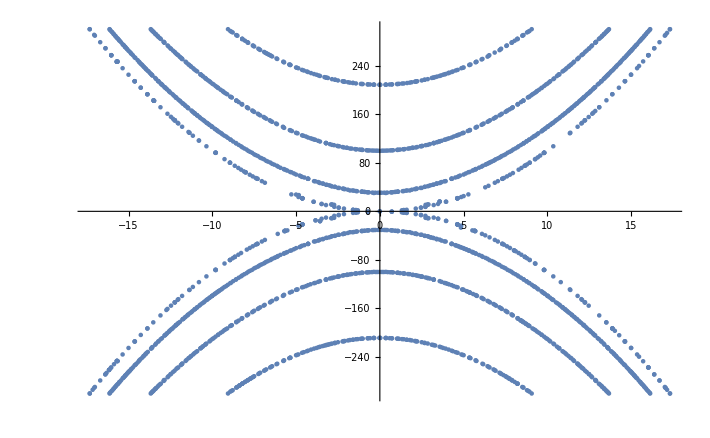

```mathematica
Contornoasym=ListPlot[{{{-17.31054021564049,-300.},{-17.315899476383507,-299.95508449359374},{-17.142857142857142,-293.873814174107},{-17.049560546875,-290.68516322544644},{-17.008579799107146,-289.2857142857143},{-16.690499441964285,-278.57142857142856},{-16.384517695062076,-268.5179488597833},{-16.38363122942811,-268.4934960286062},{-16.313650948660708,-266.13333565848217},{-16.160358253231802,-261.17697488059287},{-16.159862900990106,-261.17348505657696},{-16.159726126883832,-261.1657675800842},{-16.15951254899122,-261.15817993963816},{-16.047101702008923,-257.5077601841517},{-16.03567940848214,-257.14285714285717},{-15.867919921875,-251.7857142857143},{17.31054021564075,300.},{17.315899476383628,299.95508449359494},{17.142857142857146,293.873814174107},{17.049560546875,290.68516322544644},{17.008579799107146,289.2857142857143},{16.690499441964292,278.57142857142856},{16.375100959095324,268.65919989928443},{16.37780882659563,268.49309098296715},{16.03365628038849,257.20452202035966},{16.029299818127846,257.1918607091365},{16.015825155668217,257.1428571428571},{16.028395008648086,257.0867081402748},{15.714285714285719,246.93603515625},{15.468699171264566,239.398083859603},{15.353306361607148,235.7142857142857},{14.990411829444605,225.13349479755328},{14.992599101603572,224.99482009172527},{14.636038742332376,214.35512630335543},{14.631233841063203,214.33922340532712},{14.619029748431208,214.28571428571428},{14.267926897321432,203.57142857142856},{13.879732616294412,192.91554832970635},{13.868665024319643,192.85714285714283},{13.522949218750005,182.87004743303567},{-15.000348772321429,-225.00523158482144},{-14.636038742332342,-214.3551263033564},{-14.631233841063104,-214.33922340532786},{-14.619029748430947,-214.2857142857143},{-14.267926897321427,-203.5714285714286},{-13.879732616294264,-192.91554832970755},{-13.868665024319284,-192.8571428571429},{-13.522949218749998,-182.87004743303572},{-10.351213727678568,-107.14285714285715},{-9.81636681288849,-96.49514608159548},{-9.790472856312054,-96.67930854503078},{-9.80089300489773,-96.42857142857144},{-9.80109261043682,-96.316800529727},{-9.270542689732142,-85.94185965401786},{-8.947597728431148,-80.16323417413176},{-8.944293893718642,-80.12130587993464},{-8.940185394813495,-80.07276114758479},{-8.780953499802505,-77.21426893153382},{-8.659091092684266,-75.06639108312531},{-8.65635901059339,-75.03839615888535},{-8.652609209375804,-75.},{-8.448239062058855,-71.49069978340287},{-8.283168247767854,-68.609619140625},{-10.798339843749998,-116.59633091517857},{-11.159667968749998,-124.53787667410715},{-11.36663468485469,-129.37264957331598},{-11.369487181724494,-129.45769227413254},{-11.802106584821429,-139.28571428571428},{10.351213727678575,-107.14285714285715},{9.816366812888596,-96.4951460815935},{9.790472856312917,-96.67930854502342},{9.800893004898294,-96.42857142857144},{9.801092610437374,-96.3168005297303},{9.285714285714288,-86.22174944196429},{9.258335658482146,-85.71428571428572},{8.944293893718738,-80.12130587993325},{8.940185394813694,-80.07276114758463},{8.780953499802683,-77.21426893153127},{8.659091092684298,-75.0663910831236},{8.656359010593492,-75.03839615888435},{8.652609209376001,-75.},{8.44823906205899,-71.49069978340094},{8.283168247767858,-68.609619140625},{10.798339843750005,-116.59633091517857},{11.33893694196429,-128.57142857142858},{11.369487181724628,-129.45769227413066},{11.802106584821432,-139.28571428571428},{-10.351213727678568,107.14285714285712},{-9.816366812888509,96.49514608159505},{-9.790472856312224,96.67930854502927},{-9.800893004897842,96.42857142857142},{-9.80109261043693,96.31680052972764},{-9.270542689732142,85.94185965401783},{-8.947597728431152,80.16323417413075},{-8.945241127852897,80.10709736792076},{-8.940185394813573,80.0727611475847},{-8.660365513392856,74.99999999999997},{-8.448239062058887,71.49069978340236},{-8.283168247767854,68.60961914062497},{-10.798339843749998,116.59633091517854},{-11.366634684854729,129.372649573316},{-11.369487181724521,129.45769227413214},{-11.421036503231552,130.70842382709668},{-11.802106584821429,139.28571428571428},{-10.798339843749998,116.59633091517854},{-11.159667968749998,124.53787667410712},{10.351213727678575,107.14285714285712},{9.816366812888615,96.49514608159308},{9.811117787749543,96.48007355108578},{9.800893004898406,96.42857142857142},{9.801092610437482,96.31680052973093},{9.780308683522696,96.03352520783426},{9.56880937953555,91.86071801945948},{9.429495675223219,88.91470772879461},{-15.703299386160715,246.5933663504464},{-15.695622247276129,246.4642778144276},{-15.689432310121113,246.5584690534415},{-15.644987345289621,246.69721183633808},{-15.67852801017421,246.4285714285714},{-15.683361608577986,246.35478347836147},{-15.353306361607144,235.7142857142857},{-15.703299386160715,246.5933663504464},{-16.028395008647934,257.0867081402737},{-16.02951261222799,257.1428571428571},{-16.02929981812771,257.19186070913753},{-16.03365628038845,257.2045220203609},{-16.37780882659563,268.49309098296715},{-16.375100959095324,268.65919989928443},{-16.690499441964285,278.57142857142856},{-17.008579799107146,289.2857142857143},{-17.049560546875,290.68516322544644},{-17.315899476383507,299.95508449359374},{-17.31703351324652,300.},{13.093261718750005,-171.42857142857144},{13.51358945874255,-182.86259228241562},{13.519178800775865,-182.92660370264784},{13.875596941078992,-192.7658063470942},{13.868665024319565,-192.8571428571429},{13.879732616294381,-192.91554832970667},{13.884708709886707,-192.93721215879458},{14.026576450892861,-196.74421037946433},{-12.67752511160714,160.71428571428572},{-12.469122321425823,155.68612832901903},{-12.3431396484375,152.3529052734375},{-12.245895289378126,150.07278248798661},{-12.24373871828095,150.03384059593628},{-12.241039368782058,150.},{-12.228070270183728,149.81787390635986},{-12.06785714959725,145.76785704175552},{-12.026890345982142,144.64285714285714},{-13.093261718749998,171.42857142857142},{-13.477064070624728,182.04235320858496},{-13.477549416074883,182.1428571428571},{-13.48394021763025,182.1815513627338},{-13.488279117401365,182.20548718865604},{-13.492462090943388,182.20534182718475},{-13.519178800775823,182.92660370264832},{-13.875596941078863,192.76580634709316},{-13.868665024319363,192.85714285714283},{-13.879732616294294,192.91554832970724},{-14.267926897321427,203.57142857142856},{-13.093261718749998,-171.42857142857144},{-12.74127195707188,-162.4523492153504},{-12.67752511160714,-160.71428571428572},{13.093261718750005,171.42857142857142},{12.741271957071941,162.45234921534947},{12.677525111607148,160.71428571428572},{13.093261718750005,171.42857142857142},{12.857142857142861,165.30238560267856},{-15.000348772321429,225.00523158482144},{-14.636038742332348,214.3551263033562},{-14.631233841063123,214.3392234053277},{-14.631093063814818,214.28571428571428},{-14.629204091225823,214.21688479386455},{-14.274030412946427,203.74668666294644},{16.690499441964292,-278.57142857142856},{16.375100959095267,-268.6591998992854},{16.377808826595587,-268.4930909829672},{16.033656280388485,-257.20452202036},{16.029299818127814,-257.19186070913685},{16.015825155668118,-257.14285714285717},{16.021420387791792,-256.99712458214634},{15.714285714285719,-246.93603515625006},{15.468699171264541,-239.39808385960342},{15.353306361607148,-235.71428571428572},{14.996943843269056,-225.03545857675857},{14.992599101603572,-224.99482009172527},{14.63603874233237,-214.35512630335566},{14.631233841063183,-214.3392234053273},{14.619029748431156,-214.2857142857143},{14.621047486971689,-214.11222395733395},{14.28571428571429,-204.07889229910722},{16.690499441964292,-278.57142857142856},{17.008579799107146,-289.2857142857143},{17.049560546875,-290.68516322544644},{17.315899476383628,-299.95508449359494},{17.317033513246614,-300.},{-7.93997628348214,-63.04321289062501},{-7.764404445702623,-60.31964760017492},{-7.589111328124998,-57.59190150669644},{6.290544782366075,-39.570399693080375},{6.546630859375003,-42.85714285714287},{6.290544782366075,39.57039969308035},{6.4835030691964315,42.03316824776784},{7.939976283482145,63.04321289062498},{7.76440444570309,60.319647600167954},{7.5891113281250036,57.59190150669641},{-16.13259631843635,-300.},{-16.116735098202504,-299.32040209839096},{-16.07142857142857,-297.72048889142235},{-16.00187655181547,-295.6861374370536},{-15.956952400615652,-294.6428571428571},{-15.887688327742332,-292.0418179410078},{-15.876867794366913,-291.7244454869322},{-15.795197785525374,-289.2857142857143},{-15.773844553633587,-288.3923316954962},{-15.714285714285714,-286.36393285014833},{-15.657284395808544,-284.783591205729},{-15.618798930950257,-283.92857142857144},{-15.55091965030743,-281.4780804688972},{-15.54204587721408,-281.15502612750305},{-15.451133250323934,-278.57142857142856},{-15.357142857142858,-275.2698290804363},{-15.307680801628027,-273.9562165470081},{-15.273117907385531,-273.2142857142857},{-15.209616080249992,-271.0013840608928},{-15.190946408372048,-270.35008958870503},{-15.178571428571429,-269.96329799143314},{-15.10477146728735,-267.8571428571429},{-15.072728445782507,-266.76621617040524},{-15.01819508106449,-265.17857142857144},{-15.,-264.56850748998},{-14.952779277682868,-263.20831083475696},{-14.918967404572173,-262.5},{-14.854443679743648,-260.3166551961547},{-14.834188301789743,-259.63003261601096},{-14.741322895661357,-257.14285714285717},{-14.642857142857142,-253.81688230283652},{-14.588892055951778,-252.5951905892948},{-14.555604192943747,-251.7857142857143},{-14.458247209751237,-249.0165652891257},{-14.37453233320413,-246.42857142857144},{-14.356509622897535,-245.3666413708227},{-14.285714285714285,-243.45603319368368},{-14.182551592071531,-241.07142857142858},{-14.1026417822063,-238.46037326690552},{-14.090527849333922,-238.14363202572318},{-13.999091237627592,-235.71428571428572},{-13.979455845656984,-234.95101945800238},{-13.928571428571427,-233.35544621138695},{-13.8500955930711,-231.53428038964776},{-13.653263931531713,-226.22753040154717},{-13.618615406878494,-225.},{-13.60665977400123,-224.4715319614101},{-13.57142857142857,-223.54841486852484},{-13.406717781034935,-219.64285714285717},{-13.352050340898025,-217.57638774367246},{-13.219664136744315,-214.2857142857143},{-13.214285714285712,-214.09983313260423},{-13.089530316187385,-210.79990240004636},{-13.00390363160006,-208.92857142857144},{-12.857142857142856,-204.6437722497792},{-12.825190736838003,-204.05071037600138},{-12.801608157171845,-203.5714285714286},{-12.736564319263358,-201.76275050323613},{-12.696082198951068,-200.63019558716258},{-12.590910978751761,-198.21428571428575},{-12.563634203658474,-197.25977265940867},{-12.5,-195.45925329564906},{-12.429399648520668,-193.91614812933287},{-12.372709825712786,-192.8571428571429},{-12.294494633188256,-190.58258050217617},{-12.204014216277496,-188.41735610130533},{-12.166856489217228,-187.50000000000003},{-12.159965203469806,-187.24337909081007},{-12.142857142857142,-186.8040075741986},{-12.055914434973465,-184.8214285714286},{-12.024070992989975,-183.9246493908647},{-11.935057318207772,-182.14285714285717},{-11.785714285714285,-178.07574751034335},{-11.747681747184698,-177.3562023636581},{-11.713403766332078,-176.7857142857143},{-11.612776391759374,-174.19164587639068},{-11.60868573813642,-174.08399964223943},{-11.487715413455856,-171.42857142857144},{-11.46958683860808,-170.81334027802166},{-11.428571428571427,-169.68354449299144},{-11.328359386457604,-167.5746092031359},{-11.24610811977473,-166.07142857142858},{-11.185708230602597,-164.35723368381818},{-11.07142857142857,-161.65777355068994},{-11.042105988557536,-161.15412445735123},{-11.013663124102994,-160.71428571428572},{-10.914989068184672,-158.36769316562726},{-10.89807148030685,-157.95749922396865},{-10.771887530326332,-155.35714285714286},{-10.714285714285712,-153.72754751778044},{-10.607201900085592,-151.6062572130018},{-10.515386921874104,-150.},{-10.459236584840482,-148.46859408453557},{-10.357142857142854,-146.12637704769196},{-10.310012624509405,-145.3498106323589},{-10.27159922158747,-144.64285714285714},{-10.178571428571427,-142.58855042685101},{-10.159704734823757,-142.24728612050077},{-10.047880392690084,-140.00392017606555},{-10.013619413964395,-139.28571428571428},{-10.008830811986517,-139.1532521059165},{-9.999999999999998,-138.95861128025794},{-9.878579934243408,-136.60714285714286},{-9.857194512965146,-136.07065373409424},{-9.82142857142857,-135.3276899721859},{-9.743525663601345,-133.92857142857144},{-9.703707951986788,-133.01580929162674},{-9.642857142857142,-131.82268954235408},{-9.608579997898742,-131.25},{-9.548579832747432,-129.98558822307422},{-9.45753377299761,-128.57142857142858},{-9.391937635474386,-126.97807832502706},{-9.285714285714285,-124.74565236144471},{-9.177380721047218,-123.21428571428572},{-9.07434254189064,-121.02771901449752},{-8.928571428571427,-118.27569638660675},{-8.894963965807676,-117.85714285714286},{-8.758126881283555,-115.05666820931808},{-8.597172996807767,-112.5},{-8.57142857142857,-111.8410299113697},{-8.423653245356917,-109.35948703393194},{-8.282371946025187,-107.14285714285715},{-8.214285714285712,-105.54670073779693},{-8.09276983537208,-103.60845246941878},{-7.95879255522577,-101.7857142857143},{-7.857142857142855,-99.57409428016972},{-7.750667100436985,-98.02570777915949},{-7.624764823716887,-96.42857142857144},{-7.499999999999998,-93.87320374014683},{-7.401866781085896,-92.54342685514011},{-7.278321077062512,-91.07142857142858},{-7.22113201801403,-89.89730544407524},{-7.142857142857141,-88.41755584766784},{-7.041927532513184,-87.22822986944507},{-6.917459711297235,-85.71428571428572},{-6.860719862664244,-84.58920206003631},{-6.785714285714283,-83.19930442873365},{-6.677427859254082,-81.98143925404588},{-6.540376732565945,-80.35714285714286},{-6.4919488802108765,-79.40648108255111},{-6.428571428571426,-78.23097808618243},{-6.304150080996574,-76.8663202136228},{-6.249999999999998,-76.12856104623494},{-6.152284922827194,-75.},{-6.113855854453973,-74.36359075461894},{-6.071428571428569,-73.55563612337183},{-5.932912891317957,-71.72059234451632},{-5.732120832539565,-69.64285714285714},{-5.714285714285712,-69.27452907364855},{-5.61259652992565,-68.11751937745622},{-5.527098769766796,-67.09351845349804},{-5.357142857142854,-64.88964183610764},{-5.275566991541669,-64.28571428571429},{-5.127598248415211,-62.371740559486085},{-4.999999999999997,-60.58388517068343},{-4.7888978636198996,-58.92857142857144},{-4.715164607938179,-57.84395945235587},{-4.642857142857141,-56.70067506506976},{-4.502238251425673,-55.68071194290059},{-4.2943119418008635,-53.700393412727294},{-4.285714285714283,-53.60986860719936},{-4.2838631257884225,-53.59919597031649},{-4.2786831747420395,-53.571428571428584},{-3.9285714285714257,-49.72811909050577},{-3.8502370041774867,-49.38930208019481},{-3.6843373886331356,-48.21428571428572},{-3.6238389809542384,-47.428129571400675},{-3.5714285714285685,-46.619384732350454},{-3.4057965258862652,-45.729805031151166},{-3.3885890425436735,-45.5997357904163},{-3.2142857142857117,-43.78903198588921},{-3.160790002964164,-43.65957852696608},{-3.017457869454986,-42.85714285714287},{-2.922958621126528,-41.869906397387766},{-2.8571428571428545,-40.95252625442738},{-2.6947590721245316,-40.42138608186802},{-2.671852446719504,-40.279356156350275},{-2.4999999999999973,-38.61634655834907},{-2.4302506270901256,-38.546240593648086},{-2.209909692440334,-37.500000000000014},{-2.1692009748337573,-37.10484252035075},{-2.14285714285714,-36.71907961858294},{-2.0844004761510764,-36.62314999940906},{-1.9103324149538659,-35.630728061406266},{-1.785714285714283,-34.35768526033771},{-1.6343189437618222,-34.41378727214407},{-1.5569785482724492,-34.068963938372505},{-1.428571428571426,-33.4526081076753},{-1.3594542109758385,-33.179615406790965},{-1.0903399396917293,-32.42652766680456},{-1.0714285714285687,-32.37033108724292},{-1.058334917664771,-32.33926194931412},{-0.9577715401078373,-32.14285714285715},{-0.8928571428571401,-31.88943178046796},{-0.7585687600532967,-31.478611456343376},{-0.7142857142857116,-31.374714425309968},{-0.6562271955763698,-31.271979362217024},{-0.44174827190928145,-30.87377592136075},{-0.3571428571428545,-30.774219801592043},{-0.26146922980151294,-30.70775273273703},{-0.10181462374970779,-30.615637786611497},{2.6645352591003757*^-15,-29.94184584869288},{0.10181462374971298,-30.6156377866115},{0.26146922980151843,-30.70775273273703},{0.3571428571428598,-30.77421980159205},{0.44174827190928667,-30.87377592136075},{0.6562271955763758,-31.271979362217035},{0.714285714285717,-31.37471442530998},{0.7585687600533012,-31.47861145634339},{0.8928571428571455,-31.88943178046797},{0.957771540107839,-32.14285714285715},{1.0583349176647756,-32.33926194931413},{1.071428571428574,-32.370331087242924},{1.0903399396917355,-32.426527666804574},{1.3594542109758427,-33.17961540679098},{1.4285714285714313,-33.452608107675324},{1.556978548272457,-34.06896393837254},{1.634318943761826,-34.41378727214409},{1.7857142857142883,-34.35768526033774},{1.91033241495387,-35.63072806140629},{2.0844004761510857,-36.62314999940912},{2.1428571428571455,-36.71907961858299},{2.169200974833761,-37.104842520350786},{2.209909692440334,-37.500000000000014},{2.4302506270901296,-38.54624059364811},{2.5000000000000027,-38.6163465583491},{2.671852446719508,-40.279356156350296},{2.69475907212454,-40.42138608186807},{2.85714285714286,-40.95252625442743},{2.9229586211265315,-41.869906397387794},{3.032587820405883,-42.85714285714287},{3.0357142857142883,-42.873668631881785},{3.160790002964168,-43.6595785269661},{3.214285714285717,-44.06177378861082},{3.377359648810834,-45.53571428571429},{3.388589042543677,-45.59973579041632},{3.405796525886276,-45.72980503115125},{3.571428571428574,-46.61938473235051},{3.684337388633136,-48.21428571428572},{3.85023700417749,-49.389302080194845},{3.928571428571431,-49.728119090505814},{4.278683174742039,-53.571428571428584},{4.283667530843261,-53.60212989449399},{4.285714285714288,-53.609868607199395},{4.294311941800877,-53.700393412727415},{4.502238251425676,-55.68071194290063},{4.544254677816794,-56.250000000000014},{4.642857142857146,-57.103211568041424},{4.715164607938181,-57.843959452355904},{4.803052075474248,-58.92857142857144},{4.821428571428575,-59.07961394531977},{4.9232934666598585,-60.0791694286736},{5.000000000000003,-60.95781849013677},{5.047092350045029,-61.60714285714286},{5.1275982484152145,-62.37174055948611},{5.178571428571431,-62.92173266928075},{5.2827433659497585,-64.28571428571429},{5.328722697143487,-64.71201668570488},{5.357142857142859,-65.00435652959895},{5.512924680437443,-66.96428571428572},{5.527098769766799,-67.09351845349806},{5.535714285714288,-67.17886905897998},{5.6125965299256775,-68.11751937745655},{5.714285714285717,-69.27452907364864},{5.732120832539565,-69.64285714285714},{5.920829669312934,-71.90184067459174},{6.071428571428575,-73.55563612337191},{6.145620727707166,-75.},{6.312067546636958,-76.74755822901712},{6.4285714285714315,-78.2309780861825},{6.540376732565945,-80.35714285714286},{6.68291271342369,-81.89916644150185},{6.785714285714288,-83.19930442873373},{6.860719862664246,-84.58920206003636},{6.917459711297236,-85.71428571428572},{7.041927532513187,-87.22822986944512},{7.142857142857146,-88.41755584766791},{7.278321077062512,-91.07142857142858},{7.401866781085898,-92.54342685514015},{7.5000000000000036,-93.87320374014693},{7.6247648237168875,-96.42857142857144},{7.7506671004369885,-98.02570777915953},{7.85714285714286,-99.57409428016982},{7.95879255522577,-101.7857142857143},{8.092769835372083,-103.60845246941882},{8.214285714285717,-105.54670073779701},{8.282371946025188,-107.14285714285715},{8.423653245356919,-109.35948703393198},{8.571428571428575,-111.84102991136979},{8.59717299680777,-112.5},{8.751105949679452,-115.16198218337969},{8.759272654811822,-115.3176612507487},{8.894963965807674,-117.85714285714286},{8.92857142857143,-118.27569638660681},{9.074342541890642,-121.02771901449755},{9.177380721047218,-123.21428571428572},{9.233850013212482,-123.99224980181282},{9.285714285714288,-124.74565236144478},{9.391937635474388,-126.97807832502708},{9.45753377299761,-128.57142857142858},{9.642857142857146,-131.57934120602377},{9.703707951986791,-133.01580929162677},{9.743525663601345,-133.92857142857144},{9.821428571428575,-135.32768997218602},{9.857194512965147,-136.07065373409426},{10.000000000000004,-138.9165191924739},{10.008830811986519,-139.15325210591655},{10.012862369517292,-139.28571428571428},{10.047880392690072,-140.0039201760653},{10.15970473482376,-142.2472861205008},{10.263092896962286,-144.64285714285714},{10.308715514088393,-145.36926728867417},{10.357142857142861,-146.1263770476921},{10.515386921874104,-150.},{10.607201900085593,-151.60625721300187},{10.714285714285719,-153.7275475177806},{10.771887530326334,-155.35714285714286},{10.898071480306852,-157.9574992239687},{10.900656866059776,-158.03571428571428},{10.91498906818466,-158.36769316562697},{11.019174609107068,-160.71428571428572},{11.042223319665764,-161.1523644907279},{11.071428571428577,-161.74703672334394},{11.13877752498724,-163.39285714285717},{11.185708230602598,-164.35723368381824},{11.24610811977473,-166.07142857142858},{11.328359386457606,-167.57460920313596},{11.428571428571432,-169.68354449299156},{11.469586838608082,-170.81334027802168},{11.487715413455858,-171.42857142857144},{11.608685738136423,-174.0839996422395},{11.612776391759365,-174.19164587639045},{11.713403766332076,-176.7857142857143},{11.7476817471847,-177.35620236365813},{11.785714285714288,-178.07574751034343},{11.886359118451102,-180.63318465180498},{11.935057318207772,-182.14285714285717},{12.024070992989975,-183.92464939086474},{12.142857142857146,-186.73082619981653},{12.159965203469808,-187.2433790908101},{12.16789475964199,-187.50000000000003},{12.204014216277493,-188.41735610130522},{12.294494633188258,-190.5825805021762},{12.372709825712786,-192.8571428571429},{12.500000000000004,-195.45925329564915},{12.563634203658474,-197.2597726594087},{12.590910978751761,-198.21428571428575},{12.69608219895107,-200.63019558716263},{12.736564319263351,-201.76275050323596},{12.801608157171845,-203.5714285714286},{12.825190736838005,-204.05071037600143},{12.857142857142861,-204.64377224977932},{13.00390363160006,-208.92857142857144},{13.089530316187389,-210.79990240004642},{13.214285714285719,-214.09983313260443},{13.219664136744317,-214.2857142857143},{13.352050340898028,-217.5763877436725},{13.406717781034937,-219.64285714285717},{13.571428571428577,-223.54841486852501},{13.602518565509467,-224.53365008878666},{13.614398600402806,-225.},{13.65326393153171,-226.227530401547},{13.799598322891173,-230.35714285714286},{13.850095593071103,-231.53428038964785},{13.928571428571434,-233.35544621138715},{13.979455845656986,-234.95101945800243},{13.999091237627592,-235.71428571428572},{14.090527849333913,-238.14363202572295},{14.1026417822063,-238.46037326690558},{14.182551592071531,-241.07142857142858},{14.28571428571429,-243.4560331936838},{14.349826520474878,-245.46688790716263},{14.374532333204131,-246.42857142857144},{14.458247209751233,-249.0165652891256},{14.555604192943747,-251.7857142857143},{14.58889205595178,-252.59519058929482},{14.642857142857146,-253.8168823028366},{14.741322895661357,-257.14285714285717},{14.83435129467357,-259.6275877227537},{14.918967404572173,-262.5},{14.95277927768287,-263.208310834757},{15.000000000000004,-264.5685074899801},{15.01819508106449,-265.17857142857144},{15.07272844578251,-266.7662161704053},{15.104771467287348,-267.8571428571429},{15.178571428571432,-269.96329799143325},{15.19094640837205,-270.3500895887051},{15.20961608024999,-271.0013840608927},{15.273117907385531,-273.2142857142857},{15.30768080162803,-273.9562165470082},{15.357142857142861,-275.2698290804364},{15.451133250323934,-278.57142857142856},{15.542045877214083,-281.1550261275031},{15.550919650307426,-281.4780804688971},{15.618798930950257,-283.92857142857144},{15.657284395808546,-284.78359120572907},{15.714285714285719,-286.3639328501485},{15.77384455363359,-288.39233169549624},{15.795197785525374,-289.2857142857143},{15.876867794366907,-291.72444548693204},{15.887688327742334,-292.0418179410079},{15.956952400615652,-294.6428571428571},{16.00187655181547,-295.6861374370537},{16.071428571428577,-297.7204888914226},{16.116735098202508,-299.32040209839107},{16.132596318436352,-300.},{16.132596318436352,300.},{16.116735098202508,299.32040209839107},{16.071428571428577,297.7204888914226},{16.00187655181547,295.6861374370537},{15.956952400615652,294.6428571428571},{15.887688327742334,292.0418179410079},{15.876867794366907,291.72444548693204},{15.795197785525374,289.2857142857143},{15.77384455363359,288.39233169549624},{15.714285714285719,286.3639328501485},{15.657284395808546,284.78359120572907},{15.618798930950257,283.92857142857144},{15.550919650307426,281.4780804688971},{15.542045877214083,281.1550261275031},{15.451133250323934,278.57142857142856},{15.357142857142861,275.2698290804364},{15.30768080162803,273.9562165470082},{15.27311790738553,273.21428571428567},{15.209616080249983,271.00138406089246},{15.190946408372046,270.35008958870503},{15.10001035956197,267.85714285714283},{15.072728445782507,266.7662161704053},{15.01819508106449,265.17857142857144},{15.000000000000004,264.5685074899801},{14.95277927768287,263.208310834757},{14.918967404572173,262.5},{14.854443679743644,260.3166551961546},{14.834188301789744,259.630032616011},{14.741322895661355,257.1428571428571},{14.714133199313238,256.07371629601573},{14.642857142857146,253.8168823028366},{14.588892055951778,252.59519058929476},{14.555604192943745,251.78571428571425},{14.45824720975123,249.01656528912548},{14.37453233320413,246.4285714285714},{14.356509622897535,245.3666413708227},{14.28571428571429,243.4560331936838},{14.182551592071531,241.07142857142856},{14.1026417822063,238.46037326690555},{14.09052784933391,238.14363202572284},{13.99909123762759,235.7142857142857},{13.928571428571434,233.35544621138715},{13.853740371751478,231.4796087094422},{13.799598322891171,230.35714285714283},{13.727671504990235,228.01349885371798},{13.66792547308798,226.44745352489105},{13.614398600402806,225.},{13.602518565509467,224.53365008878663},{13.571428571428577,223.66906807189403},{13.516779763670963,222.32142857142856},{13.475079995109049,221.08808578765007},{13.419162922199478,219.64285714285714},{13.392857142857148,218.84945085666334},{13.346428098604205,217.66072137807987},{13.225858156572977,214.45930092002314},{13.219664136744315,214.28571428571428},{13.214285714285719,214.09983313260446},{13.089530316187387,210.7999024000464},{13.00390363160006,208.92857142857142},{12.857142857142861,204.64377224977932},{12.825190736838005,204.0507103760014},{12.801608157171842,203.57142857142856},{12.736564319263346,201.76275050323582},{12.696082198951068,200.63019558716258},{12.59091097875176,198.2142857142857},{12.563634203658474,197.25977265940867},{12.500000000000004,195.45925329564915},{12.429399648520668,193.91614812933287},{12.372709825712782,192.85714285714283},{12.294494633188256,190.58258050217617},{12.204014216277486,188.41735610130507},{12.166856489217226,187.49999999999997},{12.159965203469806,187.24337909081007},{12.142857142857146,186.8040075741987},{12.055914434973463,184.82142857142856},{12.024070992989975,183.9246493908647},{11.93505731820777,182.1428571428571},{11.8863591184511,180.63318465180492},{11.785714285714288,178.07574751034343},{11.7476817471847,177.35620236365813},{11.713403766332076,176.78571428571428},{11.61277639175936,174.1916458763903},{11.60868573813642,174.08399964223946},{11.487715413455856,171.42857142857142},{11.469586838608082,170.81334027802168},{11.428571428571432,169.84695136932106},{11.375005928702674,168.75},{11.328359386457606,167.57460920313596},{11.26004478958106,166.07142857142856},{11.250000000000004,165.80453471743226},{11.185708230602598,164.3572336838182},{11.071428571428577,161.65777355069008},{11.013663124102992,160.71428571428572},{10.91498906818466,158.36769316562697},{10.898071480306852,157.9574992239687},{10.771887530326334,155.35714285714286},{10.714285714285719,153.7275475177806},{10.607201900085593,151.60625721300187},{10.515386921874104,150.},{10.459236584840486,148.46859408453562},{10.357142857142861,146.1263770476921},{10.310012624509406,145.34981063235895},{10.27159922158747,144.64285714285714},{10.178571428571432,142.58855042685113},{10.15970473482376,142.2472861205008},{10.047880392690072,140.0039201760653},{10.013619413964397,139.28571428571428},{10.008830811986519,139.15325210591655},{10.000000000000004,138.95861128025805},{9.878579934243408,136.60714285714283},{9.857194512965147,136.07065373409426},{9.821428571428575,135.32768997218602},{9.743525663601343,133.92857142857142},{9.70370795198679,133.01580929162677},{9.642857142857146,131.5793412060238},{9.457533772997609,128.57142857142856},{9.391937635474388,126.97807832502707},{9.285714285714288,124.74565236144478},{9.23385001321248,123.9922498018128},{9.177380721047216,123.2142857142857},{9.074342541890642,121.02771901449753},{8.92857142857143,118.2756963866068},{8.894963965807674,117.85714285714283},{8.759272654811813,115.31766125074856},{8.751105949679452,115.16198218337968},{8.597172996807767,112.49999999999997},{8.58829729730324,112.24696911187999},{8.571428571428575,111.8410299113698},{8.423653245356919,109.35948703393197},{8.282371946025187,107.14285714285712},{8.214285714285717,105.54670073779702},{8.092769835372081,103.60845246941881},{7.958792555225768,101.78571428571428},{7.85714285714286,99.57409428016982},{7.750667100436987,98.02570777915952},{7.624764823716886,96.42857142857142},{7.5000000000000036,93.87320374014693},{7.401866781085897,92.54342685514014},{7.27832107706251,91.07142857142856},{7.221132018014032,89.89730544407527},{7.142857142857146,88.41755584766793},{7.041927532513186,87.2282298694451},{6.9174597112972345,85.7142857142857},{6.860719862664245,84.58920206003634},{6.785714285714288,83.19930442873373},{6.677427859254083,81.98143925404591},{6.607142857142859,81.01240437061999},{6.550775454124466,80.35714285714283},{6.491948880210878,79.40648108255112},{6.4285714285714315,78.54004758657499},{6.35401148635549,77.6785714285714},{6.304150080996576,76.86632021362283},{6.145620727707164,74.99999999999997},{6.071428571428575,73.55563612337191},{5.920829669312933,71.90184067459172},{5.732120832539564,69.64285714285711},{5.724747396909399,69.48593190350188},{5.714285714285717,69.27452907364865},{5.612596529925687,68.11751937745667},{5.527098769766798,67.09351845349805},{5.357142857142859,64.88964183610769},{5.275566991541664,64.28571428571426},{5.127598248415213,62.3717405594861},{5.000000000000003,60.58388517068348},{4.788897863619898,58.92857142857141},{4.71516460793818,57.8439594523559},{4.642857142857146,56.70067506506983},{4.502238251425674,55.68071194290062},{4.294311941800882,53.70039341272746},{4.285714285714288,53.60986860719939},{4.283863125788425,53.5991959703165},{4.278683174742035,53.571428571428555},{3.928571428571431,49.728119090505814},{3.8502370041774885,49.38930208019483},{3.684337388633133,48.214285714285694},{3.6238389809542406,47.428129571400696},{3.571428571428574,46.61938473235052},{3.405796525886278,45.72980503115125},{3.388589042543676,45.599735790416304},{3.377359648810832,45.53571428571426},{3.214285714285717,44.06177378861082},{3.1607900029641667,43.659578526966094},{3.017457869454982,42.85714285714284},{2.9229586211265297,41.86990639738779},{2.85714285714286,41.40209417131263},{2.6947590721245427,40.421386081868086},{2.671852446719507,40.27935615635028},{2.5000000000000027,38.61634655834909},{2.4302506270901283,38.5462405936481},{2.209909692440331,37.499999999999986},{2.16920097483376,37.10484252035077},{2.1428571428571455,36.71907961858299},{2.084400476151088,36.62314999940912},{1.910332414953869,35.63072806140627},{1.7857142857142883,34.357685260337725},{1.6343189437618242,34.41378727214409},{1.5569785482724603,34.06896393837256},{1.4285714285714313,33.452608107675324},{1.3594542109758414,33.17961540679097},{1.0903399396917373,32.426527666804574},{1.071428571428574,32.37033108724292},{1.0583349176647745,32.33926194931412},{0.9577715401078291,32.142857142857125},{0.8928571428571455,31.88943178046798},{0.7585687600532991,31.47861145634339},{0.714285714285717,31.374714425309985},{0.6562271955763785,31.27197936221705},{0.4417482719092848,30.87377592136075},{0.3571428571428598,30.187435183900767},{0.2614692298015204,30.707752732737035},{0.10181462374971112,30.615637786611497},{2.6645352591003757*^-15,30.592589815864617},{-0.10181462374970587,30.615637786611497},{-0.26146922980151494,30.70775273273703},{-0.3571428571428545,30.187435183900764},{-0.4417482719092797,30.873775921360746},{-0.6562271955763725,31.27197936221704},{-0.7142857142857116,31.374714425309975},{-0.7585687600532944,31.478611456343383},{-0.8928571428571401,31.88943178046797},{-0.9577715401078263,32.142857142857125},{-1.0583349176647696,32.339261949314114},{-1.0714285714285687,32.37033108724291},{-1.0903399396917313,32.42652766680456},{-1.359454210975837,33.17961540679096},{-1.428571428571426,33.45260810767531},{-1.5569785482724523,34.06896393837252},{-1.6343189437618204,34.41378727214407},{-1.785714285714283,34.35768526033771},{-1.9103324149538647,35.63072806140626},{-2.08440047615108,36.62314999940908},{-2.14285714285714,36.71907961858295},{-2.169200974833756,37.10484252035075},{-2.2099096924403296,37.499999999999986},{-2.4302506270901247,38.54624059364808},{-2.4999999999999973,38.616346558349065},{-2.671852446719503,40.27935615635027},{-2.6947590721245342,40.421386081868036},{-2.8571428571428545,40.95252625442739},{-2.9229586211265266,41.86990639738776},{-3.017457869454982,42.85714285714284},{-3.1607900029641627,43.65957852696607},{-3.2142857142857117,43.78903198588921},{-3.388589042543672,45.59973579041628},{-3.4057965258862684,45.72980503115119},{-3.5714285714285685,46.61938473235047},{-3.623838980954237,47.42812957140067},{-3.684337388633132,48.214285714285694},{-3.8502370041774854,49.3893020801948},{-3.9285714285714257,49.72811909050577},{-4.278683174742036,53.571428571428555},{-4.283667530843257,53.60212989449395},{-4.285714285714283,53.60986860719935},{-4.294311941800869,53.70039341272734},{-4.5022382514256725,55.68071194290058},{-4.642857142857141,56.70067506506977},{-4.715164607938178,57.84395945235586},{-4.788897863619897,58.92857142857141},{-4.999999999999997,60.58388517068342},{-5.12759824841521,62.37174055948607},{-5.275566991541665,64.28571428571426},{-5.357142857142854,64.88964183610763},{-5.527098769766795,67.09351845349802},{-5.612596529925661,68.11751937745635},{-5.714285714285712,69.27452907364855},{-5.732120832539563,69.64285714285711},{-5.932912891317956,71.7205923445163},{-6.071428571428569,73.55563612337184},{-6.145620727707163,74.99999999999997},{-6.304150080996572,76.86632021362279},{-6.428571428571426,78.23097808618243},{-6.540376732565942,80.35714285714283},{-6.682912713423685,81.89916644150179},{-6.785714285714283,83.19930442873365},{-6.917459711297234,85.7142857142857},{-7.041927532513183,87.22822986944506},{-7.142857142857141,88.41755584766784},{-7.27832107706251,91.07142857142856},{-7.401866781085895,92.5434268551401},{-7.499999999999998,93.87320374014685},{-7.624764823716885,96.42857142857142},{-7.750667100436984,98.02570777915948},{-7.857142857142855,99.57409428016973},{-7.958792555225768,101.78571428571428},{-8.09276983537208,103.60845246941876},{-8.214285714285712,105.54670073779693},{-8.282371946025185,107.14285714285712},{-8.423653245356917,109.35948703393193},{-8.57142857142857,111.8410299113697},{-8.597172996807767,112.49999999999997},{-8.758126881283554,115.05666820931806},{-8.894963965807674,117.85714285714283},{-8.928571428571427,118.27569638660675},{-9.07434254189064,121.0277190144975},{-9.177380721047216,123.2142857142857},{-9.285714285714285,124.74565236144471},{-9.399174734531009,126.86952183917771},{-9.45753377299761,128.57142857142856},{-9.548579832747432,129.98558822307422},{-9.642857142857142,131.5793412060237},{-9.703707951986788,133.01580929162674},{-9.743525663601343,133.92857142857142},{-9.82142857142857,135.32768997218594},{-9.857194512965144,136.0706537340942},{-9.999999999999998,138.9165191924738},{-10.008830811986517,139.1532521059165},{-10.01286236951729,139.28571428571428},{-10.047880392690084,140.00392017606555},{-10.159704734823757,142.24728612050077},{-10.178571428571427,142.58855042685101},{-10.27159922158747,144.64285714285714},{-10.310012624509405,145.3498106323589},{-10.357142857142854,146.12637704769196},{-10.459236584840482,148.46859408453557},{-10.515386921874104,150.},{-10.607201900085592,151.6062572130018},{-10.714285714285712,153.72754751778044},{-10.771887530326332,155.35714285714286},{-10.89807148030685,157.95749922396865},{-10.900656866059776,158.03571428571428},{-10.914989068184672,158.36769316562726},{-11.019174609107068,160.71428571428572},{-11.04222331966576,161.15236449072785},{-11.07142857142857,161.74703672334377},{-11.13877752498724,163.39285714285714},{-11.185708230602597,164.35723368381815},{-11.246108119774728,166.07142857142856},{-11.428571428571427,169.68354449299144},{-11.46958683860808,170.81334027802163},{-11.487715413455856,171.42857142857142},{-11.608685738136419,174.0839996422394},{-11.612776391759368,174.1916458763905},{-11.713403766332076,176.78571428571428},{-11.747681747184698,177.35620236365807},{-11.785714285714285,178.07574751034335},{-11.886359118451098,180.6331846518049},{-11.93505731820777,182.1428571428571},{-12.024070992989973,183.92464939086466},{-12.142857142857142,186.73082619981645},{-12.159965203469804,187.24337909081004},{-12.167894759641989,187.49999999999997},{-12.204014216277491,188.41735610130522},{-12.294494633188254,190.58258050217614},{-12.372709825712782,192.85714285714283},{-12.5,195.4592532956491},{-12.569643679550765,197.16963052102423},{-12.59091097875176,198.2142857142857},{-12.696082198951066,200.63019558716255},{-12.736564319263353,201.76275050323602},{-12.801608157171843,203.57142857142856},{-12.827065102559681,204.02259489017618},{-12.857142857142856,204.64377224977918},{-12.958637562880387,207.40615084250845},{-13.015088897543308,208.92857142857142},{-13.035714285714285,209.39559487527058},{-13.089530316187385,210.79990240004634},{-13.214285714285712,214.09983313260423},{-13.219664136744315,214.28571428571428},{-13.225858156572983,214.45930092002334},{-13.346428098604202,217.66072137807978},{-13.406717781034935,219.64285714285714},{-13.57142857142857,223.54841486852484},{-13.602518565509463,224.53365008878657},{-13.615972909683595,225.},{-13.667925473087989,226.44745352489127},{-13.727671504990232,228.0134988537179},{-13.799598322891171,230.35714285714283},{-13.853740371751474,231.47960870944212},{-13.928571428571427,233.35544621138698},{-13.979455845656982,234.95101945800238},{-13.99909123762759,235.7142857142857},{-14.090527849333919,238.14363202572304},{-14.102641782206298,238.4603732669055},{-14.182551592071531,241.07142857142856},{-14.226046500195885,241.96644535420452},{-14.285714285714285,243.45603319368368},{-14.349826520474874,245.46688790716254},{-14.374532333204128,246.4285714285714},{-14.458247209751232,249.0165652891256},{-14.588892055951776,252.59519058929473},{-14.642857142857142,253.81688230283652},{-14.741322895661355,257.1428571428571},{-14.834188301789743,259.63003261601096},{-14.854443679743648,260.3166551961547},{-14.918967404572173,262.5},{-15.,264.42269418779824},{-15.072728445782507,266.76621617040524},{-15.104771467287346,267.85714285714283},{-15.178571428571429,269.96329799143314},{-15.190946408372046,270.350089588705},{-15.209616080249987,271.0013840608926},{-15.27311790738553,273.21428571428567},{-15.307680801628027,273.9562165470081},{-15.357142857142858,275.2698290804363},{-15.451133250323934,278.57142857142856},{-15.54204587721408,281.15502612750305},{-15.55091965030743,281.4780804688972},{-15.618798930950257,283.92857142857144},{-15.657284395808544,284.783591205729},{-15.714285714285714,286.36393285014833},{-15.773844553633587,288.3923316954962},{-15.795197785525374,289.2857142857143},{-15.876867794366913,291.7244454869322},{-15.887688327742332,292.0418179410078},{-15.956952400615652,294.6428571428571},{-16.00187655181547,295.6861374370536},{-16.07142857142857,297.72048889142235},{-16.116735098202504,299.32040209839096},{-16.13259631843635,300.},{13.673990740523514,-300.},{13.639743017547135,-298.9752833082216},{13.58051543528006,-297.32142857142856},{13.571428571428577,-297.03403635622743},{13.513991305763602,-295.50441612783175},{13.480303655645978,-294.6428571428571},{13.392857142857148,-292.1328003564271},{13.388510955709636,-292.02947852149833},{13.376084966018539,-291.7127030617065},{13.279003811304465,-289.2857142857143},{13.261170182169225,-288.5824472674617},{13.214285714285719,-287.130958516862},{13.130143835896526,-285.1906996044093},{13.07423923848554,-283.92857142857144},{12.910330699089517,-279.3692462006284},{12.882988320410508,-278.57142857142856},{12.876000084909817,-278.28857015492423},{12.857142857142861,-277.69102315921555},{12.666905687596321,-273.2142857142857},{12.614124464382408,-271.5024187485497},{12.500000000000004,-268.44824518030293},{12.469322473504189,-267.8571428571429},{12.348212561383715,-264.77681157924434},{12.250087140682442,-262.5},{12.142857142857146,-259.31634702662933},{12.081281155136972,-258.06649695865974},{12.035344547468565,-257.14285714285717},{11.948575829077603,-254.69993399240744},{11.893248208973494,-253.3987231346024},{11.824085810257111,-251.7857142857143},{11.81334903692634,-251.37119301753353},{11.785714285714288,-250.5832411371826},{11.592714146530053,-246.42857142857144},{11.538318767919929,-244.78236133834397},{11.428571428571432,-242.05424639426946},{11.374020879052217,-241.07142857142858},{11.258896300960133,-238.2594126284552},{11.141991554591227,-235.71428571428572},{11.071428571428577,-233.68579970594243},{10.978204267084918,-231.75550742229774},{10.901922127436215,-230.35714285714286},{10.714285714285719,-225.71577561555125},{10.691658704947034,-225.3394051400803},{10.671430782209491,-225.},{10.570979664948933,-222.85040925994824},{10.403141187921548,-218.95288218117688},{10.357142857142861,-217.80468815649655},{10.168983724614064,-214.2857142857143},{10.107556287092322,-212.67236997932952},{10.000000000000004,-210.24806029473325},{9.91844356881326,-208.92857142857144},{9.809118539047564,-206.4346504857152},{9.6642475596876,-203.5714285714286},{9.642857142857146,-202.98590136097297},{9.504786529243528,-200.28534491849},{9.387846995175392,-198.21428571428575},{9.285714285714288,-195.73943645609432},{9.195574546860763,-194.20923893994578},{9.110820835230225,-192.8571428571429},{8.92857142857143,-188.9142809760732},{8.881504046662954,-188.20601072862718},{8.839798928888587,-187.50000000000003},{8.750000000000004,-185.70469586196722},{8.722171397775611,-185.2388576047945},{8.696368005598416,-184.8214285714286},{8.571428571428575,-182.44920164833866},{8.56150001479101,-182.29178549242062},{8.551833686387896,-182.14285714285717},{8.480605234050461,-180.82663577495742},{8.463788109395638,-180.5282502123631},{8.403967583915408,-179.46428571428572},{8.39942324852939,-179.36579412920207},{8.392857142857146,-179.23096230662998},{8.251671568749549,-176.7857142857143},{8.23619282469965,-176.45710762950532},{8.214285714285717,-175.96044955563303},{7.935139507151182,-171.42857142857144},{7.904701129127178,-170.71519734880667},{7.85714285714286,-169.7170302663193},{7.612847416699861,-166.07142857142858},{7.56893353908795,-165.0374254851094},{7.5000000000000036,-163.76803821189725},{7.279922797807368,-160.71428571428572},{7.224253784732254,-159.4933360861591},{7.142857142857146,-158.082433683816},{6.934107499142248,-155.35714285714286},{6.871909451036618,-154.0642153773079},{6.785714285714288,-152.6440311548061},{6.573099861856017,-150.},{6.511268907773242,-148.75953781197285},{6.4285714285714315,-147.4503300760849},{6.1946563322587975,-144.64285714285714},{6.141456796846029,-143.59243376159532},{6.071428571428575,-142.51417611686085},{5.796646086107361,-139.28571428571428},{5.758543064507394,-138.62185403238914},{5.714285714285717,-137.86913578675208},{5.564744745237922,-136.17168596428837},{5.37702717050673,-133.92857142857144},{5.3678851955368,-133.76743635266234},{5.357142857142859,-133.58133938679273},{5.259692396115128,-132.46681451315547},{5.16881437534218,-131.39635579843875},{5.000000000000003,-129.29764746084766},{4.969395206138913,-129.03050047934494},{4.912383860732568,-128.57142857142858},{4.642857142857146,-125.20345322877994},{4.555535420895998,-124.52411154370294},{4.410169303645468,-123.21428571428572},{4.285714285714288,-121.56344636045189},{4.125826663583103,-120.25545718911064},{4.023192299779081,-119.27645592525762},{3.928571428571431,-118.31599650693744},{3.8577314498218653,-117.85714285714286},{3.6837012851072903,-116.17305215196211},{3.571428571428574,-114.93359222187395},{3.2222763224460618,-112.5},{3.217648751308325,-112.44955444466089},{3.214285714285717,-112.40774678668572},{3.203398665641787,-112.33669427034106},{2.9814187485257304,-110.63586162925695},{2.85714285714286,-109.84417462976303},{2.8530658548542673,-109.82142857142858},{2.7362373777907574,-108.95643933313869},{2.540763305585776,-107.75430672664375},{2.5000000000000027,-107.50476667700322},{2.4821958124078476,-107.40991995673949},{2.4283391977368445,-107.14285714285715},{2.321428571428574,-106.43956715928856},{2.226176857893707,-105.89306141730873},{2.1428571428571455,-105.19557567408941},{1.9808439552837713,-104.71265932925654},{1.955436934618497,-104.59701740929403},{1.7857142857142883,-103.48301456220781},{1.6837442488091066,-103.31526483929203},{1.480094138960317,-102.55855494154758},{1.4285714285714313,-102.28931671661893},{1.3963652515334535,-102.26880694128397},{1.2121965566248227,-101.7857142857143},{1.0992410670446962,-101.36852685147248},{1.071428571428574,-101.19892854434606},{1.0313973617404526,-101.18524614039248},{0.7927325375220609,-100.60901193716914},{0.714285714285717,-100.23710198264776},{0.6159245921542541,-100.31029745374236},{0.4689030157420504,-100.10931190672645},{0.3571428571428598,-99.70414344229597},{0.23256776679837116,-99.91708793054697},{0.12767149111426082,-99.87064191900043},{2.6645352591003757*^-15,-99.84468796604831},{-0.1276714911142566,-99.87064191900042},{-0.23256776679836466,-99.91708793054696},{-0.3571428571428545,-99.70414344229597},{-0.46890301574204585,-100.10931190672643},{-0.6159245921542476,-100.31029745374235},{-0.7142857142857116,-100.45643053875875},{-0.7927325375220569,-100.60901193716913},{-1.0313973617404444,-101.18524614039244},{-1.0714285714285687,-101.19892854434602},{-1.0992410670446924,-101.36852685147245},{-1.2121965566248234,-101.7857142857143},{-1.3963652515334484,-102.26880694128397},{-1.428571428571426,-102.28931671661893},{-1.4800941389603108,-102.55855494154757},{-1.6837442488091026,-103.31526483929201},{-1.785714285714283,-103.76822932991577},{-1.9209753244805383,-104.46428571428572},{-1.9554369346184928,-104.597017409294},{-1.9808439552837636,-104.7126593292565},{-2.14285714285714,-105.19557567408937},{-2.2261768578937033,-105.8930614173087},{-2.4234468594954306,-107.14285714285715},{-2.482195812407843,-107.40991995673946},{-2.4999999999999973,-107.5047666770032},{-2.540763305585768,-107.7543067266437},{-2.736237377790754,-108.95643933313866},{-2.8530658548542713,-109.82142857142858},{-2.8571428571428545,-109.84417462976297},{-2.9814187485257273,-110.63586162925692},{-3.203398665641773,-112.33669427034091},{-3.2142857142857117,-112.40774678668565},{-3.2176487513083223,-112.44955444466085},{-3.2222763224460627,-112.5},{-3.5714285714285685,-114.93359222187391},{-3.683701285107287,-116.17305215196208},{-3.8577314498218667,-117.85714285714286},{-3.9285714285714257,-118.3159965069374},{-4.137275615608482,-120.08372290872987},{-4.285714285714283,-121.56344636045182},{-4.4101693036454686,-123.21428571428572},{-4.555535420895995,-124.5241115437029},{-4.642857142857141,-125.20345322877988},{-4.912383860732568,-128.57142857142858},{-4.967832574878626,-129.05393994824914},{-4.999999999999997,-129.29764746084763},{-5.247542860803393,-132.28457148347954},{-5.368627447807031,-133.7563025686088},{-5.714285714285712,-137.48082198548747},{-5.761211673173949,-138.5818249023907},{-5.785577425140782,-139.28571428571428},{-6.141456796846026,-143.5924337615953},{-6.194656332258797,-144.64285714285714},{-6.428571428571426,-147.4503300760848},{-6.511268907773239,-148.7595378119728},{-6.552901521789735,-150.},{-6.871909451036616,-154.06421537730787},{-6.934107499142248,-155.35714285714286},{-7.142857142857141,-158.0824336838159},{-7.2242537847322525,-159.49333608615905},{-7.279922797807368,-160.71428571428572},{-7.499999999999998,-163.76803821189716},{-7.568933539087947,-165.03742548510934},{-7.612847416699862,-166.07142857142858},{-7.857142857142855,-169.7170302663192},{-7.906408700489394,-170.68958377837336},{-7.935139507151181,-171.42857142857144},{-8.214285714285712,-175.96044955563292},{-8.236991631154156,-176.44512553268763},{-8.248895493016935,-176.7857142857143},{-8.429966529746931,-180.0209265176326},{-8.550088805394314,-182.14285714285717},{-8.561472158197097,-182.29220334132924},{-8.57142857142857,-182.42399681876864},{-8.832129391359576,-187.50000000000003},{-8.881504046662952,-188.20601072862715},{-8.928571428571427,-188.91428097607317},{-9.110820835230225,-192.8571428571429},{-9.195574546860762,-194.20923893994575},{-9.285714285714285,-195.73943645609424},{-9.387846995175392,-198.21428571428575},{-9.504786529243527,-200.28534491848995},{-9.642857142857142,-202.9859013609729},{-9.6642475596876,-203.5714285714286},{-9.809118539047562,-206.43465048571517},{-9.91844356881326,-208.92857142857144},{-9.999999999999998,-210.24806029473314},{-10.10755628709232,-212.6723699793295},{-10.168983724614064,-214.2857142857143},{-10.357142857142854,-217.80468815649638},{-10.402294753402145,-218.9655786989678},{-10.424220166471773,-219.64285714285717},{-10.547918766101672,-222.13836136561773},{-10.593085503955587,-223.18199684504813},{-10.671430782209491,-225.},{-10.69165870494703,-225.3394051400802},{-10.714285714285712,-225.7157756155511},{-10.901922127436215,-230.35714285714286},{-10.976470368952635,-231.78151589428188},{-11.07142857142857,-233.68579970594226},{-11.141991554591227,-235.71428571428572},{-11.260464809352587,-238.23588500256832},{-11.292520505412716,-239.03066472404794},{-11.374020879052217,-241.07142857142858},{-11.428571428571427,-242.0542463942693},{-11.538318767919927,-244.78236133834395},{-11.592714146530053,-246.42857142857144},{-11.785714285714285,-250.5832411371825},{-11.813349036926338,-251.3711930175335},{-11.824085810257111,-251.7857142857143},{-11.876141418630635,-253.14212127945956},{-12.035344547468565,-257.14285714285717},{-12.083199124267495,-258.03772742170185},{-12.142857142857142,-259.3163470266292},{-12.250087140682442,-262.5},{-12.348212561383713,-264.7768115792443},{-12.469322473504189,-267.8571428571429},{-12.5,-268.4482451803029},{-12.614124464382407,-271.50241874854964},{-12.666905687596323,-273.2142857142857},{-12.857142857142856,-277.6910231592154},{-12.87629193316776,-278.284192431055},{-12.882988320410508,-278.57142857142856},{-12.910330699089522,-279.36924620062854},{-13.07423923848554,-283.92857142857144},{-13.130143835896524,-285.19069960440925},{-13.214285714285712,-287.1309585168618},{-13.279003811304463,-289.2857142857143},{-13.37608496601855,-291.7127030617068},{-13.388510955709632,-292.0294785214983},{-13.39285714285714,-292.1328003564269},{-13.480303655645978,-294.6428571428571},{-13.513991305763598,-295.5044161278317},{-13.57142857142857,-297.0340363562272},{-13.58051543528006,-297.32142857142856},{-13.639743017547133,-298.97528330822155},{-13.673990740523514,-300.},{-13.673990740523514,300.},{-13.639743017547133,298.97528330822155},{-13.58051543528006,297.32142857142856},{-13.57142857142857,297.0340363562272},{-13.513991305763598,295.5044161278317},{-13.480303655645978,294.6428571428571},{-13.39285714285714,292.1328003564269},{-13.388510955709632,292.0294785214983},{-13.37608496601855,291.7127030617068},{-13.279003811304463,289.2857142857143},{-13.261170182169224,288.58244726746165},{-13.214285714285712,287.1309585168618},{-13.130143835896524,285.19069960440925},{-13.07423923848554,283.92857142857144},{-12.910330699089522,279.36924620062854},{-12.882988320410508,278.57142857142856},{-12.87629193316776,278.284192431055},{-12.857142857142856,277.6910231592154},{-12.666905687596321,273.21428571428567},{-12.614124464382405,271.5024187485496},{-12.5,268.4482451803029},{-12.469322473504185,267.85714285714283},{-12.348212561383713,264.7768115792443},{-12.250087140682442,262.5},{-12.217440118358699,261.3812553674766},{-12.142857142857142,259.3163470266292},{-12.083199124267495,258.03772742170185},{-12.035344547468563,257.1428571428571},{-11.948575829077601,254.69993399240735},{-11.893248208973494,253.3987231346024},{-11.82408581025711,251.78571428571425},{-11.813349036926336,251.37119301753347},{-11.785714285714285,250.5832411371825},{-11.592714146530051,246.4285714285714},{-11.538318767919925,244.78236133834392},{-11.428571428571427,242.05424639426934},{-11.374020879052216,241.07142857142856},{-11.292520505412709,239.03066472404777},{-11.260464809352586,238.2358850025683},{-11.141991554591225,235.7142857142857},{-11.07142857142857,233.68579970594226},{-10.976470368952635,231.78151589428185},{-10.901922127436213,230.35714285714283},{-10.714285714285712,225.7157756155511},{-10.69165870494703,225.3394051400802},{-10.671430782209491,225.},{-10.593085503955583,223.18199684504808},{-10.547918766101672,222.13836136561773},{-10.424220166471772,219.64285714285714},{-10.403141187921545,218.9528821811768},{-10.357142857142854,217.80468815649638},{-10.255487782390551,215.81054040699885},{-10.168983724614062,214.28571428571428},{-10.10755628709232,212.67236997932946},{-9.999999999999998,210.24806029473314},{-9.918443568813258,208.92857142857142},{-9.808407923061207,206.4453097255104},{-9.72890329040926,204.86212078471033},{-9.664247559687597,203.57142857142856},{-9.642857142857142,202.9859013609729},{-9.504761223031105,200.28572451167625},{-9.38784699517539,198.2142857142857},{-9.350992585127571,197.23511122308642},{-9.285714285714285,195.73943645609424},{-9.195855681495141,194.20502192043},{-9.110820835230221,192.85714285714283},{-8.928571428571427,188.91428097607314},{-8.88150404666295,188.20601072862712},{-8.832129391359572,187.49999999999997},{-8.57142857142857,182.42399681876864},{-8.561521357389653,182.29146535344086},{-8.55008880539431,182.1428571428571},{-8.429966529746915,180.0209265176323},{-8.248895493016933,176.78571428571428},{-8.236991631154156,176.44512553268763},{-8.214285714285712,175.96044955563292},{-7.935139507151179,171.42857142857142},{-7.906408700489393,170.68958377837336},{-7.857142857142855,169.71703026631923},{-7.61284741669986,166.07142857142856},{-7.568933539087946,165.03742548510934},{-7.499999999999998,163.76803821189716},{-7.279922797807368,160.71428571428572},{-7.2242537847322525,159.49333608615905},{-7.142857142857141,158.0824336838159},{-6.934107499142248,155.35714285714286},{-6.868405076306899,154.11678099825363},{-6.785714285714283,152.64403115480602},{-6.573099861856017,150.},{-6.511268907773239,148.7595378119728},{-6.428571428571426,147.4503300760848},{-6.194656332258797,144.64285714285714},{-6.141456796846026,143.5924337615953},{-5.785577425140782,139.28571428571428},{-5.761211673173949,138.5818249023907},{-5.714285714285712,137.48082198548747},{-5.36862744780703,133.7563025686088},{-5.357142857142854,133.58133938679265},{-5.247542860803402,132.28457148347962},{-4.999999999999997,129.29764746084763},{-4.969395206138908,129.03050047934488},{-4.912383860732565,128.57142857142856},{-4.642857142857141,125.20345322877989},{-4.560715007114758,124.44641775042143},{-4.410169303645463,123.2142857142857},{-4.285714285714283,121.56344636045183},{-4.125826663583098,120.2554571891106},{-4.0231922997790734,119.27645592525755},{-3.9285714285714257,118.31599650693738},{-3.857731449821863,117.85714285714283},{-3.6837012851072855,116.17305215196208},{-3.5714285714285685,114.93359222187391},{-3.2222763224460604,112.49999999999997},{-3.2176487513083214,112.44955444466083},{-3.2142857142857117,112.40774678668565},{-3.2033986656417763,112.33669427034094},{-2.981418748525726,110.63586162925691},{-2.8571428571428545,109.47088913487735},{-2.7362373777907525,108.95643933313866},{-2.54076330558577,107.75430672664372},{-2.4999999999999973,107.457895310736},{-2.4234468594954266,107.14285714285712},{-2.226176857893702,105.89306141730869},{-2.14285714285714,105.19557567408937},{-1.9808439552837673,104.71265932925652},{-1.9554369346184908,104.59701740929401},{-1.785714285714283,103.48301456220779},{-1.6837442488091012,103.315264839292},{-1.4800941389603133,102.55855494154758},{-1.428571428571426,102.28931671661893},{-1.3963652515334468,102.26880694128396},{-1.2121965566248145,101.78571428571428},{-1.0992410670446908,101.36852685147244},{-1.0714285714285687,101.19892854434602},{-1.0313973617404466,101.18524614039245},{-0.7927325375220553,100.60901193716911},{-0.7142857142857116,100.23710198264774},{-0.6159245921542492,100.31029745374234},{-0.4689030157420439,100.10931190672643},{-0.3571428571428545,99.9936995166991},{-0.232567766798367,99.91708793054697},{-0.12767149111425494,99.8706419190004},{2.6645352591003757*^-15,99.53317765088568},{0.12767149111425938,99.87064191900042},{0.23256776679837327,99.91708793054698},{0.3571428571428598,99.9936995166991},{0.4689030157420483,100.10931190672645},{0.6159245921542558,100.31029745374236},{0.714285714285717,100.45643053875875},{0.7927325375220596,100.60901193716914},{1.0313973617404546,101.18524614039248},{1.071428571428574,101.19892854434606},{1.0992410670446946,101.36852685147247},{1.212196556624814,101.78571428571428},{1.3963652515334521,102.26880694128397},{1.4285714285714313,102.28931671661893},{1.4800941389603193,102.5585549415476},{1.6837442488091052,103.31526483929201},{1.7857142857142883,103.7682293299158},{1.9209753244805314,104.4642857142857},{1.9554369346184957,104.59701740929401},{1.9808439552837738,104.71265932925655},{2.1428571428571455,105.1955756740894},{2.226176857893706,105.89306141730872},{2.4234468594954253,107.14285714285712},{2.482195812407846,107.40991995673947},{2.5000000000000027,107.50476667700323},{2.54076330558578,107.75430672664379},{2.7362373777907556,108.95643933313869},{2.85714285714286,109.47088913487738},{2.9814187485257295,110.63586162925694},{3.2033986656417905,112.33669427034107},{3.214285714285717,112.40774678668572},{3.2176487513083236,112.44955444466088},{3.222830770642655,112.49999999999997},{3.3928571428571455,113.73658927181089},{3.4547920339617972,114.24954806200162},{3.55669908923051,115.1785714285714},{3.571428571428574,115.28094311599531},{3.6837012851072894,116.1730521519621},{3.857731449821862,117.85714285714283},{3.928571428571431,118.31599650693744},{4.023192299779087,119.27645592525766},{4.125826663583101,120.25545718911063},{4.285714285714288,121.5634463604519},{4.410169303645464,123.2142857142857},{4.555535420895997,124.52411154370293},{4.642857142857146,125.47981975096089},{4.675600399724064,125.89285714285712},{4.7635495897812605,126.76104186756683},{4.912383860732566,128.57142857142856},{4.967832574878629,129.05393994824917},{5.000000000000003,129.29764746084766},{5.2475428608034305,132.28457148347997},{5.357142857142859,133.58133938679273},{5.368627447807032,133.75630256860882},{5.377027170506728,133.92857142857142},{5.714285714285717,137.86913578675208},{5.758543064507394,138.62185403238914},{5.796646086107361,139.28571428571428},{6.071428571428575,142.51417611686085},{6.141456796846029,143.59243376159532},{6.1946563322587975,144.64285714285714},{6.4285714285714315,147.4503300760849},{6.511268907773242,148.75953781197285},{6.573099861856017,150.},{6.785714285714288,152.6440311548061},{6.871909451036618,154.0642153773079},{6.934107499142248,155.35714285714286},{7.142857142857146,158.082433683816},{7.224253784732254,159.4933360861591},{7.279922797807368,160.71428571428572},{7.5000000000000036,163.76803821189725},{7.568933539087949,165.03742548510937},{7.61284741669986,166.07142857142856},{7.7364554514005635,167.88173965756303},{7.85714285714286,169.7170302663193},{7.904701129127178,170.71519734880667},{7.93513950715118,171.42857142857142},{8.214285714285717,175.96044955563303},{8.236991631154158,176.44512553268765},{8.248895493016935,176.78571428571428},{8.429966529746887,180.0209265176318},{8.55008880539431,182.1428571428571},{8.561472158197098,182.29220334132927},{8.571428571428575,182.4239968187687},{8.832129391359572,187.49999999999997},{8.881504046662952,188.20601072862715},{8.92857142857143,188.9142809760732},{9.039366820344746,191.1952119805431},{9.110820835230221,192.85714285714283},{9.195855681495141,194.20502192043003},{9.285714285714288,195.73943645609432},{9.350992585127573,197.23511122308642},{9.38784699517539,198.2142857142857},{9.504786529243527,200.28534491848995},{9.642857142857146,202.98590136097297},{9.664247559687597,203.57142857142856},{9.809118539047562,206.43465048571517},{9.918443568813258,208.92857142857142},{10.000000000000004,210.24806029473322},{10.107556287092322,212.6723699793295},{10.168983724614062,214.28571428571428},{10.357142857142861,217.80468815649655},{10.403141187921547,218.95288218117685},{10.570979664948933,222.8504092599482},{10.662298929146777,225.},{10.691658704947034,225.33940514008026},{10.714285714285719,225.71577561555125},{10.901922127436213,230.35714285714283},{10.976470368952636,231.78151589428194},{11.071428571428577,233.6857997059424},{11.141991554591227,235.7142857142857},{11.260464809352587,238.23588500256835},{11.292520505412702,239.03066472404757},{11.374020879052216,241.07142857142856},{11.428571428571432,242.05424639426946},{11.538318767919927,244.78236133834397},{11.59271414653005,246.4285714285714},{11.785714285714288,250.58324113718263},{11.813349036926338,251.3711930175335},{11.876141418630622,253.14212127945927},{12.035344547468561,257.1428571428571},{12.08128115513697,258.06649695865974},{12.142857142857146,259.31634702662933},{12.250087140682442,262.5},{12.348212561383715,264.77681157924434},{12.469322473504185,267.85714285714283},{12.500000000000004,268.44824518030293},{12.614124464382407,271.50241874854964},{12.66690568759632,273.21428571428567},{12.857142857142861,277.69102315921555},{12.876291933167762,278.28419243105503},{12.882988320410508,278.57142857142856},{12.910330699089517,279.3692462006284},{13.07423923848554,283.92857142857144},{13.130143835896526,285.1906996044093},{13.214285714285719,287.130958516862},{13.261170182169225,288.5824472674617},{13.279003811304465,289.2857142857143},{13.376084966018539,291.7127030617065},{13.388510955709636,292.02947852149833},{13.392857142857148,292.1328003564271},{13.480303655645978,294.6428571428571},{13.513991305763602,295.50441612783175},{13.571428571428577,297.03403635622743},{13.58051543528006,297.32142857142856},{13.639743017547135,298.9752833082216},{13.673990740523514,300.},{-9.062817866000124,-300.},{-8.928571428571427,-296.9877596904245},{-8.854409899286344,-295.75528008213337},{-8.78426697018323,-294.6428571428571},{-8.57142857142857,-290.3123882565541},{-8.537294619496562,-289.7977235646944},{-8.506526204235268,-289.2857142857143},{-8.39285714285714,-287.12589143265603},{-8.376357744483876,-286.85463383274185},{-8.360827879643457,-286.6071428571429},{-8.214285714285712,-283.9420383500996},{-8.213846887834215,-283.9351538253439},{-8.213417448068,-283.92857142857144},{-8.208084135436057,-283.8355477458266},{-8.049918535764796,-281.0369362492423},{-8.035714285714283,-280.7651212318248},{-7.905154024530856,-278.57142857142856},{-7.884324767531728,-278.16369991559543},{-7.857142857142855,-277.6631854617437},{-7.747630579377992,-275.8928571428571},{-7.7170070560359,-275.31632273089},{-7.678571428571427,-274.6339393951764},{-7.587496672318899,-273.2142857142857},{-7.5479083725379486,-272.4956601262165},{-7.499999999999998,-271.5566378203361},{-7.250713637935373,-267.8571428571429},{-7.204119401456875,-266.93820897814686},{-7.142857142857141,-265.8049270415958},{-6.90635646647397,-262.5},{-6.8524130067942055,-261.49951918380117},{-6.785714285714283,-260.32421992155344},{-6.546228076644217,-257.14285714285717},{-6.492146732256808,-256.1892275875764},{-6.428571428571426,-255.11183437094445},{-6.167733402632258,-251.7857142857143},{-6.124023654165761,-250.99678804465643},{-5.762018422036334,-246.42857142857144},{-5.743472317905849,-245.9907723742694},{-5.714285714285712,-245.38550749787527},{-5.408852494134525,-241.84707312630366},{-5.357142857142854,-241.21430906651375},{-5.351290975055526,-241.1592068027385},{-5.341545397700303,-241.07142857142858},{-4.999999999999997,-236.92140949108503},{-4.949039957071417,-236.47868635821445},{-4.867495718224958,-235.71428571428572},{-4.642857142857141,-232.97066686279055},{-4.536664257733305,-231.95003613400038},{-4.357464250333822,-230.35714285714286},{-4.285714285714283,-229.46414668801867},{-4.10640775208858,-227.68959800438554},{-3.9285714285714257,-226.0948006559055},{-3.7764469762901465,-225.},{-3.6551067576808896,-223.74482720621518},{-3.5714285714285685,-222.97831609195185},{-3.417898779526162,-221.94580402139326},{-3.314180194215533,-221.1412743418045},{-3.2142857142857117,-220.31359000588375},{-3.1807424784640155,-220.1460056801826},{-3.104177854295435,-219.64285714285717},{-3.035714285714283,-219.10566655568803},{-2.938434696038429,-218.42347955942353},{-2.8571428571428545,-217.87958792386308},{-2.704215880143026,-216.96428571428572},{-2.6868979167732716,-216.83938839125804},{-2.6581128156949605,-216.65740652113874},{-2.4999999999999973,-215.54944440757788},{-2.2272818310210236,-214.2857142857143},{-2.167541306658134,-213.9154518286994},{-2.14285714285714,-213.73199328309573},{-2.0934097924538313,-213.54400402966468},{-1.8969523508655204,-212.61714330844575},{-1.785714285714283,-211.95363798334844},{-1.6135849986018458,-211.510510735258},{-1.5962444241542402,-211.44366636231368},{-1.428571428571426,-210.6424833531175},{-1.3251087119238785,-210.48051217828467},{-1.1401853851861186,-209.9599236349347},{-1.0714285714285687,-209.69938928678502},{-1.0223459500079237,-209.66481074988113},{-0.7253785291975057,-209.09496365224837},{-0.7142857142857116,-209.06238057442735},{-0.5849543922067326,-208.92857142857144},{-0.37641431200308406,-208.639499605668},{-0.3571428571428545,-208.587015357891},{-0.3355429315492029,-208.60457254466667},{-0.03081808829534849,-208.46630010414117},{2.6645352591003757*^-15,-208.45968037610587},{0.030818088295353818,-208.46630010414117},{0.3355429315492082,-208.60457254466667},{0.3571428571428598,-208.587015357891},{0.3764143120030893,-208.639499605668},{0.584954392206738,-208.92857142857144},{0.714285714285717,-209.06238057442735},{0.725378529197511,-209.09496365224837},{1.022345950007929,-209.66481074988113},{1.071428571428574,-209.69938928678502},{1.140185385186124,-209.9599236349347},{1.3251087119238822,-210.4805121782847},{1.4285714285714313,-210.64248335311754},{1.596244424154246,-211.44366636231368},{1.6135849986018511,-211.510510735258},{1.7857142857142883,-211.95363798334844},{1.8969523508655257,-212.61714330844575},{2.093409792453843,-213.54400402966476},{2.1428571428571455,-213.73199328309582},{2.1675413066581353,-213.91545182869945},{2.227281831021017,-214.2857142857143},{2.5000000000000027,-215.5494444075779},{2.658112815694967,-216.65740652113877},{2.6868979167732765,-216.83938839125804},{2.85714285714286,-217.7156782854725},{3.0979997799523473,-219.64285714285717},{3.1823834073150215,-220.1213917474176},{3.214285714285717,-220.3135900058838},{3.3052357253422113,-221.00710730870458},{3.571428571428574,-222.9783160919519},{3.655106757680892,-223.74482720621523},{3.7764469762901482,-225.},{3.928571428571431,-226.0948006559055},{4.106407752088584,-227.68959800438557},{4.285714285714288,-229.4641466880187},{4.357464250333827,-230.35714285714286},{4.532561676974547,-232.01157484538183},{4.642857142857146,-232.9706668627906},{4.867495718224955,-235.71428571428572},{4.950640887260545,-236.4546724053776},{5.000000000000003,-236.9214094910851},{5.341545397700302,-241.07142857142858},{5.351290975055528,-241.15920680273854},{5.357142857142859,-241.2143090665138},{5.408852494134549,-241.8470731263039},{5.714285714285717,-245.38550749787527},{5.743472317905854,-245.9907723742694},{5.7620184220363395,-246.42857142857144},{6.1240236541657636,-250.99678804465645},{6.1677334026322574,-251.7857142857143},{6.4285714285714315,-255.1118343709445},{6.493781001086439,-256.16471355513204},{6.54622807664422,-257.14285714285717},{6.785714285714288,-260.32421992155355},{6.852413006794208,-261.49951918380117},{6.90635646647397,-262.5},{7.142857142857146,-265.8049270415959},{7.204119401456878,-266.9382089781469},{7.250713637935373,-267.8571428571429},{7.376967632864282,-269.70262836417874},{7.5000000000000036,-271.5566378203363},{7.547908372537949,-272.49566012621653},{7.587496672318897,-273.2142857142857},{7.678571428571432,-274.63393939517647},{7.717007056035903,-275.3163227308901},{7.747630579377993,-275.8928571428571},{7.85714285714286,-277.66318546174375},{7.88432476753173,-278.1636999155955},{7.902035920314417,-278.57142857142856},{8.0499185357648,-281.03693624924233},{8.208084135435998,-283.83554774582564},{8.213354338363517,-283.92857142857144},{8.21384743798322,-283.9351455731089},{8.214285714285717,-283.9411503110033},{8.5018372341592,-289.2857142857143},{8.537294619496564,-289.7977235646944},{8.571428571428575,-290.3123882565542},{8.784266970183229,-294.6428571428571},{8.854409899286345,-295.7552800821334},{8.92857142857143,-296.9877596904246},{9.062817866000126,-300.},{9.062817866000126,300.},{8.92857142857143,296.9877596904246},{8.854409899286345,295.7552800821334},{8.784266970183229,294.6428571428571},{8.571428571428575,290.3123882565542},{8.53720037435245,289.79913724185616},{8.5018372341592,289.2857142857143},{8.214285714285717,283.9411503110033},{8.21384743798322,283.9351455731089},{8.213354338363517,283.92857142857144},{8.208084135435998,283.83554774582564},{8.0499185357648,281.03693624924233},{7.902035920314417,278.57142857142856},{7.884789938895302,278.15672234514193},{7.85714285714286,277.59411867614057},{7.581812192749826,273.21428571428567},{7.548788848050588,272.4824529935269},{7.237523162278993,267.85714285714283},{7.205360085392981,266.9195987191053},{7.142857142857146,265.4653568473077},{6.853927215038618,261.47680606013506},{6.532144171376251,257.1428571428571},{6.493781001086436,256.16471355513204},{6.4285714285714315,254.76251252403728},{6.124023654165761,250.99678804465645},{6.071428571428575,250.17791126313352},{5.768203790992824,246.4285714285714},{5.7434723179058516,245.99077237426937},{5.714285714285717,245.54824878900686},{5.408852494134557,241.847073126304},{5.351290975055528,241.1592068027385},{5.341545397700301,241.07142857142856},{5.000000000000003,236.92140949108506},{4.949039957071418,236.47868635821447},{4.867495718224955,235.7142857142857},{4.642857142857146,232.9706668627906},{4.532561676974546,232.01157484538183},{4.35746425033382,230.35714285714283},{4.285714285714288,229.46414668801876},{4.141374978711341,228.19205325209865},{4.098991019867087,227.800848987708},{4.083862997883349,227.67857142857142},{3.928571428571431,226.19457905098747},{3.8777901594985296,225.76171903609352},{3.7764469762901482,225.},{3.6510808758936144,223.8052154330244},{3.571428571428574,222.9783160919519},{3.4178987795261633,221.9458040213933},{3.31418019421555,221.14127434180463},{3.214285714285717,220.31359000588378},{3.1807424784640177,220.14600568018264},{3.0979997799523478,219.64285714285714},{2.85714285714286,217.71567828547245},{2.6868979167732765,216.83938839125804},{2.6581128156949667,216.65740652113874},{2.5000000000000027,215.54944440757785},{2.227281831021017,214.28571428571428},{2.167541306658135,213.91545182869945},{2.1428571428571455,213.7319932830958},{2.093409792453845,213.54400402966476},{1.896952350865522,212.61714330844578},{1.7857142857142883,211.95363798334847},{1.6251267051999851,211.33738513628597},{1.4285714285714313,210.64248335311754},{1.3251087119238796,210.48051217828467},{1.1401853851861299,209.95992363493474},{1.071428571428574,209.69938928678505},{1.022345950007925,209.66481074988116},{0.7253785291975113,209.09496365224834},{0.714285714285717,209.06238057442732},{0.5849543922067371,208.92857142857142},{0.37641431200308917,208.63949960566796},{0.3571428571428598,208.61856472009802},{0.335542931549209,208.60457254466667},{0.030818088295352764,208.46630010414117},{2.6645352591003757*^-15,208.41216875819322},{-0.030818088295347434,208.46630010414117},{-0.33554293154920367,208.60457254466667},{-0.3571428571428545,208.58701535789098},{-0.3764143120030839,208.63949960566796},{-0.5849543922067317,208.92857142857142},{-0.7142857142857116,209.06238057442732},{-0.725378529197506,209.09496365224834},{-1.0223459500079197,209.66481074988116},{-1.0714285714285687,209.69938928678505},{-1.1343427866685776,209.87228465717155},{-1.428571428571426,210.6424833531175},{-1.5962444241542464,211.4436663623137},{-1.6135849986018422,211.510510735258},{-1.785714285714283,211.95363798334841},{-1.8969523508655182,212.61714330844575},{-2.093409792453839,213.54400402966476},{-2.14285714285714,213.7319932830958},{-2.16754130665813,213.91545182869942},{-2.227281831021013,214.28571428571428},{-2.4999999999999973,215.54944440757785},{-2.6581128156949605,216.65740652113874},{-2.6868979167732716,216.83938839125804},{-2.8571428571428545,217.71567828547245},{-3.0979997799523438,219.64285714285714},{-3.1823834073150166,220.12139174741756},{-3.2142857142857117,220.31359000588378},{-3.3052357253422024,221.0071073087045},{-3.5714285714285685,222.97831609195183},{-3.655106757680889,223.74482720621518},{-3.7764469762901465,225.},{-3.9285714285714257,226.0948006559055},{-4.10640775208858,227.68959800438554},{-4.285714285714283,229.46414668801867},{-4.357464250333822,230.35714285714283},{-4.536664257733305,231.95003613400036},{-4.642857142857141,232.97066686279055},{-4.8674957182249505,235.7142857142857},{-4.95064088726054,236.45467240537755},{-4.999999999999997,236.92140949108506},{-5.341545397700303,241.07142857142856},{-5.351290975055526,241.15920680273848},{-5.357142857142854,241.21430906651372},{-5.408852494134525,241.84707312630363},{-5.714285714285712,245.3855074978752},{-5.743472317905849,245.99077237426934},{-5.762018422036334,246.4285714285714},{-6.124023654165759,250.9967880446564},{-6.167733402632254,251.78571428571425},{-6.428571428571426,255.11183437094442},{-6.492146732256807,256.1892275875764},{-6.554096599169328,257.1428571428571},{-6.607142857142854,257.8402027826171},{-6.673395017348862,258.82764616833845},{-6.736618626175875,259.82142857142856},{-6.785714285714283,260.48154168607675},{-6.8524130067942055,261.49951918380117},{-6.90635646647397,262.5},{-7.142857142857141,265.8049270415958},{-7.2041194014568735,266.93820897814686},{-7.25071363793537,267.85714285714283},{-7.499999999999998,271.5566378203361},{-7.547908372537946,272.4956601262164},{-7.581812192749826,273.21428571428567},{-7.857142857142855,277.59411867614045},{-7.8847899388953,278.1567223451419},{-7.902035920314417,278.57142857142856},{-8.049918535764796,281.0369362492423},{-8.208084135436057,283.8355477458266},{-8.213354338363523,283.92857142857144},{-8.213847437983219,283.93514557310885},{-8.214285714285712,283.9411503110032},{-8.5018372341592,289.2857142857143},{-8.537200374352446,289.7991372418561},{-8.57142857142857,290.3123882565541},{-8.78426697018323,294.6428571428571},{-8.854409899286344,295.75528008213337},{-8.928571428571427,296.9877596904245},{-9.062817866000124,300.},{-6.094970703124998,-37.146868024553584},{-5.695471816742917,-32.5753351972441},{-5.69178982330134,-32.48029550762273},{-5.665404320465727,-32.20961332219069},{-5.665720054032354,-32.20007143459257},{-5.655888707406015,-32.246666871670215},{-5.636686847846733,-32.14285714285715},{-5.5224945519242254,-31.376686288184715},{-4.856480189732141,-23.581368582589292},{-4.642857142857141,-21.638902788752745},{-4.6326820163593645,-21.70206871863977},{-4.623966685044527,-21.511693427666273},{-4.627789762365917,-21.448711419925495},{-4.625220796803155,-21.448380026143138},{-4.61714461058453,-21.42857142857144},{-3.8412807410767758,-14.809171670932548},{-3.8379071800517024,-14.865315656096632},{-3.5750578634421646,-16.12586795163252},{-3.5714285714285685,-16.09208927197737},{-3.563267472362018,-16.071428571428584},{-3.4745824957973093,-12.166976848754606},{-3.2142857142857117,-10.329764229910728},{-2.902392415189216,-11.393029084981151},{-2.8571428571428545,-11.097865376651274},{-2.837670096424881,-11.00637712505533},{-2.7275933670955195,-10.714285714285728},{-2.720860072544641,-7.4013846261160845},{-2.455870980709336,-6.101343678318334},{-2.452639933125481,-6.067543860260621},{-2.14285714285714,-4.58809988839287},{-1.5994090992186303,-2.5625650597080813},{-1.4289970147049282,-2.050714676579073},{-1.428571428571426,-2.0497620123090794},{-1.313825334821426,-1.7211914062500142},{-0.7142857142857116,-0.54446742696123},{-0.0003487723214259069,-1.4210854715202004*^-14},{0.714285714285717,-0.54446742696123},{-0.0003487723214259069,-1.4210854715202004*^-14},{-0.7142857142857116,-0.5436612786784565},{-1.313825334821426,1.7211914062499858},{-1.428199189585241,2.050067243304351},{-1.428571428571426,2.0497620123090385},{-1.5990474202935478,2.5617681960406653},{-1.5994090992186267,2.562565059707996},{-2.14285714285714,4.588099888392842},{-2.4526399331255053,6.067543860260229},{-2.4558709807093297,6.101343678317627},{-2.720860072544641,7.401384626116056},{-2.7275933670955146,10.7142857142857},{-2.83767009642488,11.006377125055316},{-2.8571428571428545,10.939073183876156},{-2.9023924151892184,11.393029084981158},{-3.2142857142857117,10.3297642299107},{-3.4745824957973674,12.166976848753702},{-3.479078976689284,12.12839331429044},{-3.951482463951037,15.727763040734388},{-3.9557452294356534,15.770781003349668},{-4.617144610585437,21.428571428571413},{-4.62522079680345,21.44838002614159},{-4.6277897623660165,21.448711419923914},{-4.623966685044909,21.511693427660024},{-4.632682016359583,21.70206871863662},{-4.642857142857141,21.638902788750876},{-4.856392996651783,23.58267647879462},{-4.837246508359333,26.78571428571427},{-4.999999999999997,27.615769547513565},{-5.282679966517854,27.90265764508927},{12.464250837053575,-155.35714285714286},{12.243738718281,-150.03384059593586},{12.24103936878214,-150.},{12.228070270183963,-149.81787390636205},{12.067857149597389,-145.7678570417535},{12.026890345982146,-144.64285714285714},{-7.410452706473213,-54.91463797433037},{-7.317122499482933,-53.63338670498656},{-7.313594467484103,-53.6134484279473},{-7.307570722315781,-53.571428571428584},{-7.043112233342559,-49.71045935700444},{-6.861572265624997,-47.07641601562501},{6.0949707031250036,-37.146868024553584},{5.6954718167429075,-32.57533519724017},{5.691789823301434,-32.48029550762139},{5.665404320465796,-32.20961332218962},{5.665720054032417,-32.20007143459165},{5.658310515660045,-32.20018219291454},{5.6366868478472565,-32.14285714285715},{5.522494551926275,-31.37668628819538},{4.8372465083593355,-26.7857142857143},{4.856392996651788,-23.58267647879465},{4.642857142857146,-21.638902788749522},{4.632682016359753,-21.702068718634308},{4.623966685045202,-21.511693427655388},{4.6277897623660955,-21.44871141992278},{4.625220796803678,-21.44838002614048},{4.617144610586123,-21.42857142857144},{3.95574522943566,-15.77078100334945},{3.951482463951053,-15.72776304073426},{3.4790789766892884,-12.128393314290358},{3.474582495797391,-12.166976848753457},{3.214285714285717,-10.329764229910728},{2.902392415189224,-11.393029084981194},{2.85714285714286,-11.097865376651294},{2.8376700964248855,-11.006377125055344},{2.7275933670955195,-10.714285714285728},{2.7208600725446463,-7.4013846261160845},{2.4558709807093355,-6.101343678317699},{2.452639933125509,-6.0675438602602805},{2.1428571428571455,-4.58809988839287},{1.5994090992186334,-2.5625650597080476},{1.5990474202935527,-2.5617681960407133},{1.4285714285714313,-2.0497620123090723},{1.428199189585246,-2.050067243304385},{1.3138253348214313,-1.7211914062500142},{0.714285714285717,-0.54446742696123},{6.861572265625003,-47.07641601562501},{7.043112233342673,-49.710459357002804},{7.307570722316126,-53.571428571428584},{7.313594467484272,-53.613448427946054},{7.317122499482998,-53.63338670498473},{7.410452706473218,-54.91463797433037},{7.5891113281250036,-57.59190150669644},{7.764404445702975,-60.319647600169716},{8.008090351814511,-64.28571428571429},{8.01281092930091,-64.32473880878196},{8.01589482927246,-64.34767735586327},{8.11253138950893,-65.81202915736608},{-7.589111328124998,57.59190150669641},{-7.764404445702739,60.319647600173155},{-8.008090351814408,64.28571428571426},{-8.012810929300855,64.32473880878233},{-8.015894829272437,64.34767735586388},{-8.112531389508923,65.81202915736606},{-7.410452706473213,54.91463797433034},{-7.317122499482954,53.63338670498587},{-7.313594467484163,53.61344842794682},{-7.307570722315904,53.571428571428555},{-7.043112233342603,49.71045935700376},{-6.861572265624997,47.07641601562498},{6.861572265625003,47.07641601562498},{7.0431122333427165,49.71045935700213},{7.30757072231625,53.571428571428555},{7.313594467484332,53.61344842794558},{7.31712249948302,53.633386704984034},{7.410452706473218,54.91463797433034},{8.283168247767858,68.60961914062497},{8.448239062059022,71.49069978340044},{8.652609209376099,74.99999999999997},{8.65635901059354,75.03839615888384},{8.659091092684312,75.06639108312272},{8.78095349980272,77.21426893153067},{8.940185394813774,80.07276114758454},{8.944293893718775,80.12130587993266},{9.258335658482146,85.7142857142857},{9.285714285714288,86.22436523437497},{2.7208600725446463,7.401384626116056},{2.7275933670955146,10.7142857142857},{2.8376700964248847,11.006377125055328},{2.85714285714286,10.939073183876165},{2.9023924151892264,11.3930290849812},{3.214285714285717,10.3297642299107},{3.474582495797449,12.166976848752554},{3.5632674723620124,16.071428571428555},{3.571428571428574,16.092089271977365},{3.575057863442175,16.125867951632568},{3.9431806008713637,15.852290986929573},{3.9557452294356623,15.770781003348924},{4.617144610587029,21.428571428571413},{4.6252207968039745,21.44838002613893},{4.627789762366195,21.448711419921203},{4.623966685045584,21.51169342764914},{4.632682016359971,21.70206871863116},{4.642857142857146,21.63890278874765},{4.856480189732146,23.581368582589263},{5.000000000000003,25.07975877004717},{5.282854352678573,27.900041852678555},{2.7208600725446463,7.401384626116056},{2.455870980709329,6.101343678316991},{2.452639933125533,6.06754386025989},{2.1428571428571455,4.588099888392842},{1.5994090992186296,2.5625650597079606},{1.4289970147049318,2.0507146765790214},{1.4285714285714313,2.0497620123090314},{1.3138253348214313,1.7211914062499858},{0.714285714285717,-0.5436612786784565},{-12.464250837053571,-155.35714285714286},{-12.24373871828095,-150.03384059593628},{-12.241039368782058,-150.},{-12.228070270183728,-149.81787390635986},{-12.06785714959725,-145.76785704175552},{-12.026890345982142,-144.64285714285714},{12.464250837053575,155.35714285714286},{12.243738718281,150.03384059593586},{12.24103936878214,150.},{12.228070270183963,149.81787390636205},{12.067857149597389,145.7678570417535},{12.026890345982146,144.64285714285714},{-15.353306361607144,-235.71428571428572},{-15.6833616085779,-246.3547834783611},{-15.678528010174096,-246.42857142857144},{-15.64498734528932,-246.69721183633968},{-15.691625947163727,-246.4766815278758},{-15.695622247276114,-246.46427781442787},{-15.703299386160715,-246.59336635044644},{17.142857142857146,-293.873814174107},{17.049560546875,-290.68516322544644},{11.802106584821432,139.28571428571428},{11.369487181724653,129.45769227413024},{11.33893694196429,128.57142857142856}}}]
```

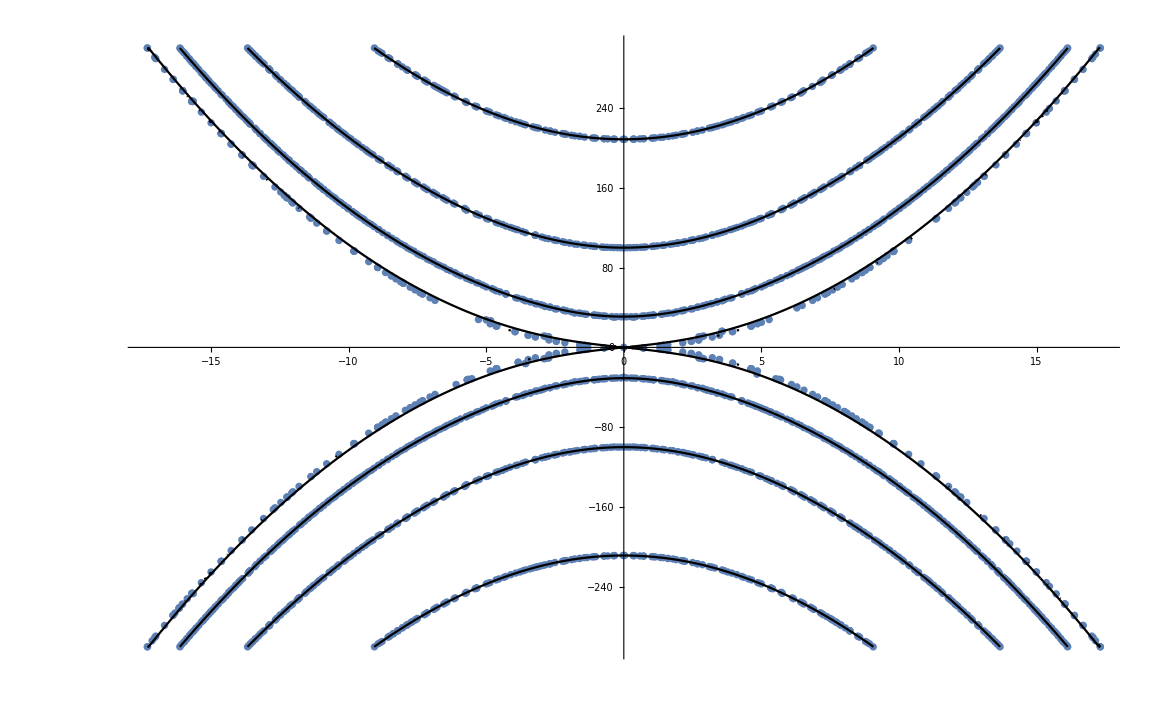

```mathematica
Show[Contornoasym,omegaAsym]
```

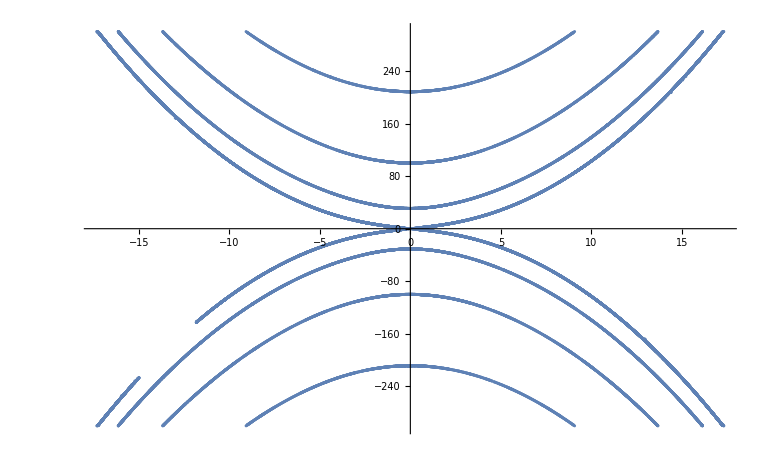

```mathematica
Contorno5l=ListPlot[{{-11.825432238293725,-142.4665178571429},{-11.824776785714285,-142.45114881166006},{-11.823030077244578,-142.40901312704563},{-11.819196428571427,-142.31979996717232},{-11.818315648746763,-142.29910714285717},{-11.816695307730685,-142.26159033024604},{-11.814311774787928,-142.20496623532392},{-11.811227180027128,-142.13169642857144},{-11.808035714285714,-142.05727182713719},{-11.805625939834359,-142.00043233105606},{-11.804092559187946,-141.96428571428572},{-11.801258526878556,-141.89853281110737},{-11.79688320315914,-141.7969980473871},{-11.796878045306952,-141.796875},{-11.796876854377913,-141.79684718433128},{-11.796875,-141.79680382209253},{-11.789806436573596,-141.62946428571428},{-11.788201628640506,-141.59215414182097},{-11.785714285714285,-141.53429235702967},{-11.782640656362808,-141.46205357142856},{-11.779460182142707,-141.38845441071652},{-11.776977802642842,-141.33100632535692},{-11.775448102591719,-141.29464285714286},{-11.77455357142857,-141.27379050431475},{-11.770857743543422,-141.1826695611344},{-11.768341988730908,-141.12723214285717},{-11.763392857142856,-141.01243523904287},{-11.76205747195896,-140.9798522063299},{-11.76119822854649,-140.95982142857144},{-11.756977474342065,-140.86359068655958},{-11.75332519460554,-140.77601493805975},{-11.752232142857142,-140.75193824571124},{-11.746834411780268,-140.625},{-11.744673582628932,-140.5709676891374},{-11.741071428571427,-140.4916767663892},{-11.739611619981849,-140.45758928571428},{-11.73688219368286,-140.39475076238577},{-11.735801426647706,-140.36922860028437},{-11.732453168001431,-140.29017857142856},{-11.729910714285712,-140.23122052522365},{-11.727162254779381,-140.1639947497378},{-11.718749999999998,-139.97158088053837},{-11.718050778984004,-139.95535714285714},{-11.716688175943617,-139.92442978201143},{-11.709654811725672,-139.7569635384006},{-11.707589285714285,-139.71161363436096},{-11.703691717907123,-139.62053571428572},{-11.7008258594196,-139.55457639442025},{-11.69642857142857,-139.45337304402807},{-11.696417882505864,-139.453125},{-11.696397605845025,-139.45266051624682},{-11.692069735096217,-139.35109683069956},{-11.68928224706175,-139.28571428571428},{-11.685267857142854,-139.19309637204654},{-11.683315265326787,-139.14759244866957},{-11.68205732762457,-139.11830357142856},{-11.678915712232797,-139.04617503079368},{-11.676005332792066,-138.97936570616673},{-11.674796826910507,-138.95089285714283},{-11.674525430689778,-138.94461853965328},{-11.67410714285714,-138.93494136625387},{-11.667631967582441,-138.7834821428571},{-11.665782958326774,-138.74093419652692},{-11.662946428571427,-138.67564978120114},{-11.66038127839731,-138.61607142857142},{-11.656979641269736,-138.53816252381105},{-11.6555116507631,-138.5045497614465},{-11.65313198976657,-138.44866071428572},{-11.651785714285712,-138.41759980668377},{-11.648320723029077,-138.33322486884953},{-11.645938942333737,-138.28125},{-11.640624999999998,-138.1592569209089},{-11.639463616174604,-138.13126004309518},{-11.634912944456005,-138.02815845255438},{-11.631491849365807,-137.94642857142856},{-11.629464285714285,-137.8999754902943},{-11.621974687062584,-137.72395112263263},{-11.61830357142857,-137.6439026690688},{-11.616904959872835,-137.61160714285714},{-11.613191853134806,-137.52087220297787},{-11.609670685276724,-137.44419642857144},{-11.607142857142856,-137.38615600471138},{-11.604351656183933,-137.31865372866957},{-11.602425653416995,-137.27678571428572},{-11.595982142857142,-137.12957355128466},{-11.595463529786475,-137.11715419606003},{-11.593403438123993,-137.07069442900277},{-11.587874820701845,-136.94196428571428},{-11.586724571950617,-136.91341713502644},{-11.584821428571427,-136.8699450213957},{-11.57356138205709,-136.60714285714286},{-11.56915269401322,-136.50735244694457},{-11.5625,-136.35667580406238},{-11.558829266206653,-136.27232142857144},{-11.551464163597975,-136.10678388254107},{-11.55138385087572,-136.10491071428572},{-11.551367116582028,-136.1044932512696},{-11.551339285714285,-136.10388951118793},{-11.544153698275194,-135.9375},{-11.542576323346463,-135.9015337212316},{-11.540178571428571,-135.84686327278706},{-11.536839912520623,-135.77008928571428},{-11.533727194046266,-135.69944923216318},{-11.530326414694516,-135.62230693470343},{-11.529482302996843,-135.60267857142858},{-11.52929828403037,-135.5984721681159},{-11.529017857142858,-135.59205981981853},{-11.524902844882936,-135.4969930410417},{-11.5234375,-135.4643390427408},{-11.522168722905635,-135.4352678571429},{-11.520491713148097,-135.39574930277857},{-11.518505139296849,-135.35156250000003},{-11.517857142857142,-135.33675237306196},{-11.516066217898764,-135.29472101723283},{-11.514856169169498,-135.26785714285717},{-11.512276785714285,-135.20906612887194},{-11.511627562452418,-135.1938901346423},{-11.50907557665528,-135.13613364982925},{-11.507536705622046,-135.10044642857144},{-11.50720334503372,-135.09284268163705},{-11.506696428571427,-135.0812774496842},{-11.500260793589515,-134.93303571428572},{-11.498380902255557,-134.8903578947381},{-11.495535714285714,-134.8257793489712},{-11.49290623891361,-134.765625},{-11.489502378140848,-134.68871432788728},{-11.487709887324495,-134.64823759558172},{-11.485547148499965,-134.5982142857143},{-11.484375,-134.571532562272},{-11.480764932098351,-134.48495458995333},{-11.478250025279513,-134.4308035714286},{-11.473214285714285,-134.31674376523037},{-11.471837485330184,-134.2840448629044},{-11.470876388565934,-134.2633928571429},{-11.46622402828356,-134.15853899568205},{-11.46351367167252,-134.09598214285717},{-11.462961059500238,-134.08236982178215},{-11.45636013480006,-133.92857142857144},{-11.454174878079167,-133.87934111452677},{-11.450892857142856,-133.80530074313032},{-11.445323547614638,-133.67728964292328},{-11.441436269056467,-133.59375},{-11.439732142857142,-133.5551227623552},{-11.436417502086003,-133.47605889728135},{-11.434099701050384,-133.42633928571428},{-11.428571428571427,-133.30165233504104},{-11.427438895576117,-133.27591656635826},{-11.426690224992432,-133.25892857142858},{-11.422973824474374,-133.17548191859865},{-11.422904237555107,-133.1739207061838},{-11.41931489145579,-133.0915178571429},{-11.418555683520735,-133.07434331861754},{-11.417410714285712,-133.04844479852372},{-11.411959972741101,-132.92410714285717},{-11.40977635629738,-132.87121179839644},{-11.406249999999998,-132.7919701938058},{-11.397377196334077,-132.58928571428572},{-11.391967887677081,-132.46869597055806},{-11.38392857142857,-132.2896046121833},{-11.38236760282415,-132.25446428571428},{-11.379082105378947,-132.18176729496994},{-11.374939813456619,-132.08705357142856},{-11.374112335239719,-132.0668863999756},{-11.372767857142854,-132.03811896979906},{-11.367550702315102,-131.91964285714286},{-11.365168633305558,-131.86622050041657},{-11.36160714285714,-131.78639688531214},{-11.360092644090773,-131.75223214285717},{-11.356989407768927,-131.68296611653395},{-11.356225916433209,-131.66553982493045},{-11.356026785714285,-131.6611572068886},{-11.352654713078707,-131.58482142857144},{-11.351789838789317,-131.56467027530311},{-11.350446428571427,-131.53515829681658},{-11.348937909152754,-131.50111607142858},{-11.347339258426835,-131.46401826645462},{-11.34521364398097,-131.41741071428572},{-11.34486607142857,-131.4095804414291},{-11.342875339523994,-131.36356633571148},{-11.341510877315022,-131.33370535714286},{-11.339285714285712,-131.28371172736433},{-11.338399141029521,-131.26329859884285},{-11.337790300823865,-131.25},{-11.336152530428043,-131.21329240072217},{-11.334762463626868,-131.18215124011735},{-11.334062586715929,-131.16629464285714},{-11.33391973569247,-131.1630789646129},{-11.333705357142854,-131.15825462765915},{-11.330356020802064,-131.08258928571428},{-11.329481123605731,-131.06224743162826},{-11.328124999999996,-131.03181444059973},{-11.325025075183929,-130.96167744366957},{-11.322967075478926,-130.91517857142856},{-11.320555844211352,-130.8613051939725},{-11.316964285714283,-130.78111744814254},{-11.31547972493833,-130.74776785714283},{-11.312402589123431,-130.67934240828006},{-11.311592637255417,-130.66093186974012},{-11.308043914866222,-130.58035714285714},{-11.30580357142857,-130.53016704141865},{-11.302684341324815,-130.45973488012777},{-11.30060929055685,-130.41294642857144},{-11.294642857142854,-130.2799426512085},{-11.293723735130595,-130.2593225444696},{-11.293108163235898,-130.24553571428572},{-11.289909240578057,-130.17453146581377},{-11.289235186285453,-130.15924006286102},{-11.28565549743305,-130.078125},{-11.284783092995,-130.0586107479321},{-11.28348214285714,-130.02952327296578},{-11.27820715306552,-129.91071428571428},{-11.275937685149048,-129.85647043704998},{-11.272321428571427,-129.77974548903993},{-11.270692813650108,-129.74330357142856},{-11.267279421028705,-129.66767345828774},{-11.266850372565454,-129.65795869723246},{-11.263221707241364,-129.57589285714286},{-11.262393547171852,-129.55740036385077},{-11.261160714285712,-129.52988469922403},{-11.257922765598302,-129.4570513731683},{-11.255760348074062,-129.40848214285717},{-11.253439116912176,-129.35689538917447},{-11.249999999999998,-129.28052782801657},{-11.248943594002169,-129.2569175185389},{-11.248233355934,-129.24107142857144},{-11.244502844075988,-129.15861408971128},{-11.24074220371433,-129.07366071428572},{-11.239976788926215,-129.05659816610677},{-11.238839285714285,-129.03125391162786},{-11.2332685311643,-128.90625},{-11.231108354153426,-128.85480325912715},{-11.22767857142857,-128.77882313533536},{-11.21844592054488,-128.57142857142858},{-11.213138307039188,-128.45471110869792},{-11.205357142857142,-128.28383509213256},{-11.203224783402527,-128.23660714285717},{-11.198536350899289,-128.13429526348935},{-11.195644514790768,-128.06919642857144},{-11.195087477785483,-128.0558306903606},{-11.194196428571427,-128.0370313141395},{-11.188148331522415,-127.90178571428572},{-11.186082033770196,-127.85609092201848},{-11.183035714285714,-127.78878404289856},{-11.180586753096437,-127.734375},{-11.177055865122213,-127.6566620231668},{-11.175339623090174,-127.6189336320669},{-11.173025464983391,-127.56696428571429},{-11.172561381415841,-127.55666856447668},{-11.171875,-127.541804589686},{-11.169242202015859,-127.48325892857144},{-11.168074782521323,-127.45655683360873},{-11.166294642857142,-127.41807963592842},{-11.165458986351199,-127.39955357142858},{-11.163575403724028,-127.35663680128243},{-11.161684718656621,-127.31584821428572},{-11.160714285714285,-127.29434838558038},{-11.1590642063008,-127.25689404834515},{-11.157914688383585,-127.23214285714286},{-11.155133928571427,-127.17069978579654},{-11.154542069774953,-127.1573153819471},{-11.151986794751036,-127.10123049269414},{-11.15035896959903,-127.06473214285714},{-11.150033789142661,-127.05752887714577},{-11.14955357142857,-127.04714660381087},{-11.14657549905383,-126.98102678571428},{-11.145543932585385,-126.95746601121917},{-11.142843171398193,-126.89732142857143},{-11.141041260152681,-126.85759538342404},{-11.138999324033598,-126.81361607142858},{-11.138392857142856,-126.8002002362716},{-11.136526730211948,-126.75790261824936},{-11.135261441698853,-126.72991071428572},{-11.132001219830997,-126.65837455967792},{-11.128481742770779,-126.58124399870455},{-11.127644494494433,-126.5625},{-11.127232142857142,-126.55338243458431},{-11.123090533435606,-126.45721342703732},{-11.120120023719226,-126.39508928571429},{-11.116071428571427,-126.3060116210998},{-11.114010610756148,-126.25859083865777},{-11.112529144049192,-126.22767857142858},{-11.104910714285712,-126.06087986095416},{-11.104894528664593,-126.06051064145964},{-11.104882864259638,-126.06026785714286},{-11.104821312746965,-126.05892683406167},{-11.097455287280143,-125.89285714285715},{-11.095951384505664,-125.85983637527215},{-11.093749999999998,-125.8115079527686},{-11.08695191840356,-125.66000693823231},{-11.082589285714285,-125.5688965318731},{-11.082094349439513,-125.55803571428572},{-11.077902742111966,-125.46092315403479},{-11.0745298417357,-125.39062500000001},{-11.07142857142857,-125.32258021574525},{-11.068747966195312,-125.26342336421315},{-11.066922653433181,-125.2232142857143},{-11.060267857142854,-125.07791790151103},{-11.059682211389772,-125.06458825772481},{-11.057008441663568,-125.00691233923929},{-11.051661577053178,-124.88839285714288},{-11.050668494377469,-124.86497258433795},{-11.04910714285714,-124.8307864082738},{-11.036616398116106,-124.55357142857144},{-11.032602588595473,-124.46631831392502},{-11.026785714285712,-124.34006352989257},{-11.021242854457789,-124.21875000000001},{-11.01436094430213,-124.07030012118231},{-11.013443867256546,-124.0513392857143},{-11.008539504664915,-123.94505685568807},{-11.005815189129677,-123.88392857142858},{-11.005265204596101,-123.8719147882013},{-11.004464285714283,-123.85442186198048},{-10.9962522905701,-123.6722870700199},{-10.990676650805508,-123.54910714285715},{-10.987187193406152,-123.47344209890768},{-10.982142857142854,-123.36422515391469},{-10.978077144940857,-123.27527139731568},{-10.975276706556754,-123.21428571428572},{-10.96892823770063,-123.07768357734763},{-10.959821428571425,-122.88223794653005},{-10.959745641878508,-122.88060108610806},{-10.959690337916106,-122.87946428571429},{-10.959388523517271,-122.87297070990196},{-10.952049578470833,-122.71205357142858},{-10.95072231865618,-122.68112950587155},{-10.948660714285712,-122.63850781182317},{-10.946110503804004,-122.58289601436847},{-10.944352841888598,-122.54464285714286},{-10.941545435408877,-122.48396132600968},{-10.937499999999996,-122.3966458997558},{-10.936970654796628,-122.38517232090767},{-10.936603533332805,-122.37723214285714},{-10.934538816305102,-122.33281438743371},{-10.932410668789654,-122.28616139672656},{-10.928922184125595,-122.20982142857143},{-10.926339285714283,-122.15382507263199},{-10.923310599030621,-122.08784101454066},{-10.921221239233299,-122.04241071428572},{-10.91517857142857,-121.91204595296516},{-10.914167896961935,-121.89016011699952},{-10.913466306968068,-121.875},{-10.909496261353702,-121.789765348877},{-10.905066523678512,-121.6918592876794},{-10.904017857142854,-121.67025085325186},{-10.898037615169354,-121.54017857142857},{-10.895996294627237,-121.49309129487712},{-10.89285714285714,-121.42852432540646},{-10.890277859985435,-121.37276785714286},{-10.886748245928047,-121.29699059679356},{-10.884283846077004,-121.24416840544079},{-10.88250748202529,-121.20535714285714},{-10.881696428571427,-121.18780718285933},{-10.87761864481444,-121.09911318492622},{-10.87480103182465,-121.03794642857143},{-10.873050586447752,-121.00022334614084},{-10.870865395163802,-120.95424107142858},{-10.870535714285712,-120.94711714251149},{-10.868472144635565,-120.90148925903793},{-10.867037329620242,-120.87053571428572},{-10.863884017025768,-120.80290045889916},{-10.859374999999998,-120.7063417226672},{-10.859286847624208,-120.70444728563686},{-10.859225178502188,-120.703125},{-10.858871158193397,-120.69556737290098},{-10.854725392702262,-120.60545839518035},{-10.851510471118734,-120.53571428571429},{-10.850157048522307,-120.50657284359397},{-10.848214285714285,-120.46479843115588},{-10.843743781616386,-120.36830357142858},{-10.841092822747589,-120.30771480164329},{-10.83705357142857,-120.22506419067436},{-10.83592696521416,-120.20089285714286},{-10.83325701501185,-120.14394451089207},{-10.831799724593003,-120.11228984539062},{-10.828164825132498,-120.03348214285715},{-10.825892857142856,-119.98464092326998},{-10.8227273768608,-119.91355363280226},{-10.820396201621666,-119.86607142857144},{-10.814732142857142,-119.74489923245619},{-10.813491569342277,-119.71726931700869},{-10.812575624879075,-119.69866071428572},{-10.80743295784643,-119.58917293912505},{-10.804797456491366,-119.53125000000001},{-10.804293677859675,-119.52041626067627},{-10.803571428571427,-119.50490086743017},{-10.795178277444034,-119.32232583833948},{-10.789365317156783,-119.19642857142858},{-10.786015747249523,-119.1249423626857},{-10.781249999999998,-119.02345489221088},{-10.776812175537199,-118.92817450979916},{-10.773534427551532,-118.86160714285715},{-10.770089285714285,-118.7880086655464},{-10.767514730594849,-118.73281475536298},{-10.76566072117073,-118.69419642857144},{-10.764508928571427,-118.66957031249501},{-10.762905962718452,-118.63453555922321},{-10.76174937844733,-118.61049107142858},{-10.75892857142857,-118.55033518400577},{-10.75828831393114,-118.53638957674718},{-10.757825446656836,-118.52678571428572},{-10.755186930925904,-118.47066110674572},{-10.753678085762076,-118.43813228499742},{-10.753348214285712,-118.43124160808235},{-10.749990628070941,-118.359375},{-10.749089758830173,-118.33954647469021},{-10.747767857142854,-118.31198583336511},{-10.746066318793302,-118.27566964285714},{-10.74449093894907,-118.24111805862104},{-10.742187499999996,-118.1931851539638},{-10.742130135826555,-118.19196428571429},{-10.739882305985484,-118.14283683878914},{-10.738217434705005,-118.10825892857144},{-10.73660714285714,-118.07393663916783},{-10.735264488383466,-118.0446933885337},{-10.734292900816312,-118.02455357142858},{-10.731026785714285,-117.95511655346327},{-10.73063806794852,-117.94667898077219},{-10.728735408660535,-117.90647755847948},{-10.726441881523956,-117.85714285714286},{-10.725446428571427,-117.83590151149667},{-10.721433277461848,-117.74992940950081},{-10.718617336272922,-117.68973214285714},{-10.714285714285712,-117.59774799887659},{-10.712207644810297,-117.55349247070266},{-10.710740645581627,-117.52232142857143},{-10.703124999999996,-117.36137449858475},{-10.702946311442677,-117.35759104264552},{-10.70281638201252,-117.35491071428572},{-10.702062679637606,-117.33897590884987},{-10.69834082102929,-117.25926268456058},{-10.697544642857139,-117.24272506234038},{-10.694947969009576,-117.1875},{-10.693733818932401,-117.1609570017282},{-10.691964285714283,-117.12427173415242},{-10.690998735756258,-117.10379464285714},{-10.689116940792978,-117.06279945953386},{-10.687052826158094,-117.02008928571428},{-10.686383928571427,-117.00588090385372},{-10.684490809670942,-116.96478071207869},{-10.68080357142857,-116.88695003524704},{-10.679182934080446,-116.85267857142857},{-10.67521305514229,-116.76912560143704},{-10.675162309542484,-116.76805964313732},{-10.67128825141941,-116.68526785714286},{-10.669642857142854,-116.65035800691912},{-10.665991445602536,-116.57262831596192},{-10.663412855577246,-116.51785714285714},{-10.661366138621272,-116.47459720639516},{-10.658482142857139,-116.4137453736504},{-10.656769746862874,-116.37613236848537},{-10.648021612628078,-116.1935384751355},{-10.6475307343715,-116.18303571428571},{-10.647447633981644,-116.18114263313242},{-10.647321428571425,-116.17846441003631},{-10.631898317793983,-115.84821428571428},{-10.629031268327939,-115.78774526079513},{-10.624999999999996,-115.70293964046395},{-10.61603230175051,-115.51339285714286},{-10.610456529958416,-115.39672347919512},{-10.602678571428568,-115.23452110350995},{-10.599998615371657,-115.17857142857143},{-10.593014281329957,-115.03360707709227},{-10.591783194339545,-115.00718065633536},{-10.591517857142854,-115.00185315913164},{-10.584040519375643,-114.84375},{-10.582564509208186,-114.81063950473428},{-10.580357142857139,-114.7664090925413},{-10.576072437131153,-114.67633928571429},{-10.573201143418137,-114.6162685630136},{-10.569196428571425,-114.53264689719286},{-10.568061645380737,-114.50892857142858},{-10.56513904617193,-114.44806783543615},{-10.563875795760808,-114.42132734930215},{-10.5600972487158,-114.34151785714286},{-10.559238650255898,-114.32347381759008},{-10.558035714285712,-114.29823650786521},{-10.554592025525057,-114.22576247426696},{-10.552131850796542,-114.17410714285715},{-10.546874999999996,-114.06426509727893},{-10.545272574369065,-114.03073281303543},{-10.544121120595594,-114.00669642857144},{-10.54060076794956,-113.93339919504227},{-10.536998523362334,-113.85854927900648},{-10.53608681148621,-113.83928571428572},{-10.535931653124562,-113.83602520313153},{-10.535714285714283,-113.83157204602631},{-10.532090156204841,-113.75558035714286},{-10.531287514061912,-113.73827657478557},{-10.530133928571427,-113.71468818461301},{-10.528086484368156,-113.671875},{-10.526634020816298,-113.64066825918407},{-10.52455357142857,-113.59820865388495},{-10.524072164018493,-113.58816964285714},{-10.521971728700281,-113.5431919266386},{-10.520070491103441,-113.50446428571429},{-10.518973214285712,-113.48152639129239},{-10.517301153718805,-113.44583983707506},{-10.513392857142854,-113.36463307390414},{-10.512066396400252,-113.33705357142858},{-10.50858987183797,-113.26500879185532},{-10.507943120897444,-113.25138890082401},{-10.504052658845724,-113.16964285714286},{-10.50223214285714,-113.13160383633374},{-10.49863230592361,-113.0562296968601},{-10.496047302953864,-113.00223214285714},{-10.491071428571427,-112.89875449470752},{-10.48928660593129,-112.86159376817346},{-10.487997544402068,-112.83482142857143},{-10.479910714285712,-112.66743872892366},{-10.479909929676813,-112.6674224834192},{-10.479909359793448,-112.66741071428572},{-10.479905749625724,-112.6673362443859},{-10.475252818191352,-112.5698684414154},{-10.47190968736129,-112.5},{-10.470586563911572,-112.47245154132638},{-10.468749999999998,-112.43428457804242},{-10.465911661941439,-112.37516435659266},{-10.463862664629637,-112.33258928571428},{-10.461228608470623,-112.27799944436921},{-10.4597896743721,-112.24888392857142},{-10.457589285714285,-112.20321268894475},{-10.45653786565441,-112.18094987232669},{-10.45575691587096,-112.16517857142857},{-10.452008928571427,-112.08757752973858},{-10.45183986447814,-112.08400917568501},{-10.450931705329387,-112.06531486565511},{-10.44770161662694,-111.99776785714286},{-10.44642857142857,-111.97128595570958},{-10.442496423386508,-111.88933936348806},{-10.439659429102946,-111.83035714285714},{-10.435267857142854,-111.73943355658831},{-10.433172521197895,-111.69437646774583},{-10.431573198175618,-111.66294642857143},{-10.42410714285714,-111.50909121733265},{-10.42372647813193,-111.50124568516388},{-10.42344254360625,-111.49553571428572},{-10.421665285482339,-111.4589078536637},{-10.419039181551272,-111.40414441958806},{-10.415385224269432,-111.328125},{-10.41436145602615,-111.30689958817915},{-10.412946428571427,-111.27761836848632},{-10.409675143939827,-111.20978355518827},{-10.407302998208742,-111.16071428571429},{-10.40498072809002,-111.11278907864967},{-10.401785714285712,-111.04698804653695},{-10.400278658530793,-111.01590940775237},{-10.39917965884195,-110.99330357142858},{-10.395569355295294,-110.91913824199914},{-10.392098966129751,-110.84800234908919},{-10.391037107256096,-110.82589285714286},{-10.390624999999996,-110.81735521721198},{-10.386181173240717,-110.72513954424635},{-10.382961244381216,-110.65848214285715},{-10.379464285714283,-110.58637514917534},{-10.376789945543578,-110.53118653113202},{-10.374841154115446,-110.49107142857144},{-10.36830357142857,-110.35689468834471},{-10.36736803114684,-110.33769381851165},{-10.366667183991034,-110.32366071428572},{-10.362723214285712,-110.24270717422704},{-10.362646591476086,-110.24110469928725},{-10.362221658545199,-110.23243202103517},{-10.358529298476661,-110.15625000000001},{-10.35795502189639,-110.14406752869698},{-10.357142857142854,-110.12771481592483},{-10.354461725142977,-110.07254464285717},{-10.353258532851365,-110.04710415008664},{-10.351562499999996,-110.01301967334521},{-10.35038426852274,-109.9888392857143},{-10.348553906678449,-109.95026282839467},{-10.346304027625095,-109.90513392857144},{-10.345982142857139,-109.89850708726807},{-10.343816745073726,-109.85390953817979},{-10.3422377786423,-109.82142857142858},{-10.340401785714281,-109.78372228842433},{-10.339107532699531,-109.75713700950698},{-10.338161258877989,-109.73772321428572},{-10.334821428571425,-109.6692991420852},{-10.334390812562383,-109.66047709727849},{-10.334075136709565,-109.65401785714286},{-10.332016462189111,-109.61194336140814},{-10.329682379009638,-109.56369288628397},{-10.325944397616297,-109.48660714285715},{-10.324981287673516,-109.46679854204008},{-10.323660714285712,-109.44031302247703},{-10.3218344015733,-109.4029017857143},{-10.32027201207438,-109.37002696174142},{-10.318080357142854,-109.3261542995068},{-10.31773979869229,-109.31919642857144},{-10.315554994382389,-109.27337151283555},{-10.313659071725555,-109.23549107142858},{-10.312499999999996,-109.21172949449338},{-10.310830647613964,-109.17682600007622},{-10.309574978019489,-109.15178571428572},{-10.306919642857139,-109.09748215316178},{-10.306099357985614,-109.08038463021572},{-10.305481162890272,-109.06808035714286},{-10.301486351656271,-108.9865809891298},{-10.301379043963719,-108.984375},{-10.30136254529499,-108.98402610628939},{-10.301339285714283,-108.98355964080922},{-10.297296446995945,-108.90066964285714},{-10.296657194962938,-108.88719564698448},{-10.295758928571427,-108.86921502179257},{-10.293203730194355,-108.81696428571429},{-10.291943592520072,-108.79048896934177},{-10.29017857142857,-108.7552252406948},{-10.289101538703646,-108.73325892857144},{-10.287191893290018,-108.69435374350685},{-10.286089889549128,-108.67192870037982},{-10.284998361883137,-108.64955357142858},{-10.284598214285712,-108.64136419689005},{-10.282469158315907,-108.5977840538328},{-10.280907073708324,-108.56584821428572},{-10.279017857142854,-108.52727744610425},{-10.277743433086263,-108.50125921799174},{-10.276805915415842,-108.48214285714286},{-10.273437499999996,-108.41353824631886},{-10.273010474484135,-108.40484288273792},{-10.272695511975703,-108.3984375},{-10.270641400664582,-108.35667363288839},{-10.270607937421808,-108.35599406132714},{-10.268590738237576,-108.31473214285714},{-10.268285490200151,-108.30830693271197},{-10.26785714285714,-108.29974878087991},{-10.264490945881452,-108.23102678571428},{-10.263552438243718,-108.21189199777278},{-10.262276785714285,-108.18591279270353},{-10.26038151562756,-108.14732142857143},{-10.258842415740709,-108.11513162103222},{-10.256696428571427,-108.07241751070252},{-10.25626305354345,-108.06361607142858},{-10.254109446764142,-108.01871544139499},{-10.252200324916485,-107.97991071428572},{-10.249369382598283,-107.92240568959716},{-10.245535714285712,-107.84470635312233},{-10.244622586360556,-107.82619691887734},{-10.243930500441927,-107.8125},{-10.239955357142854,-107.73185973463646},{-10.239869398419795,-107.73008402370301},{-10.239371012165618,-107.7200294681986},{-10.23570904725668,-107.64508928571429},{-10.235144107792761,-107.63355266882283},{-10.234374999999998,-107.6178790977518},{-10.22749608526193,-107.47767857142858},{-10.225740685910418,-107.43978256848658},{-10.223214285714285,-107.39074557312006},{-10.219244276878223,-107.31026785714286},{-10.216183242629057,-107.24832278913554},{-10.21205357142857,-107.16494255151721},{-10.210958278509098,-107.14285714285715},{-10.20776549286155,-107.07853596435189},{-10.206671282876497,-107.05618075685253},{-10.202709755870947,-106.97544642857144},{-10.200892857142856,-106.93852526829765},{-10.197198404334076,-106.86345250641745},{-10.194464220482658,-106.80803571428572},{-10.189732142857142,-106.71231533101593},{-10.187696219768467,-106.67116384633013},{-10.186181334840795,-106.64062500000001},{-10.178571428571427,-106.48739175869362},{-10.178167593834416,-106.47927180676948},{-10.177865511319418,-106.4732142857143},{-10.175766657902349,-106.43114272567814},{-10.168702370116415,-106.28642873396804},{-10.167410714285712,-106.26145987496102},{-10.161323869480203,-106.13839285714288},{-10.159232886888699,-106.09364955381237},{-10.156249999999998,-106.0333421076407},{-10.14487686536126,-105.80357142857144},{-10.140202265672274,-105.70946601491588},{-10.13392857142857,-105.58369636770418},{-10.12817492869375,-105.46875000000001},{-10.121068318705545,-105.32683236227393},{-10.11160714285714,-105.13875665311195},{-10.111362842382059,-105.13392857142858},{-10.110600819085187,-105.11883371484927},{-10.101977722992464,-104.9435484408273},{-10.094833783580977,-104.79910714285715},{-10.089285714285712,-104.68747848923014},{-10.08292677943774,-104.55966973700531},{-10.078154425039305,-104.46428571428572},{-10.066964285714283,-104.24098302558109},{-10.063767195598274,-104.17742063745442},{-10.06124476633662,-104.12946428571429},{-10.05580357142857,-104.02088570240653},{-10.054152757153028,-103.9868157855617},{-10.052846634906984,-103.96205357142858},{-10.044642857142854,-103.79907823984337},{-10.044517924099065,-103.7965168527997},{-10.044418791483054,-103.79464285714286},{-10.0437153294313,-103.78072994146957},{-10.034990027893393,-103.60461386731338},{-10.027777571661488,-103.45982142857144},{-10.025442322666681,-103.41300801714263},{-10.022321428571427,-103.35356807749952},{-10.019237500915983,-103.29241071428572},{-10.015759380674343,-103.22343071845626},{-10.011160714285712,-103.13244950416717},{-10.010783155950008,-103.12500000000001},{-10.009589785403834,-103.10143606677185},{-10.006152712946621,-103.03270930580068},{-10.002386041085867,-102.9575892857143},{-9.999999999999998,-102.91005142500092},{-9.996564557963536,-102.84171020197553},{-9.993967160731222,-102.79017857142858},{-9.988839285714285,-102.68846896214285},{-9.986950901718405,-102.65109361708107},{-9.985515828801041,-102.62276785714288},{-9.97767857142857,-102.46800589325126},{-9.977313983750642,-102.46082595802608},{-9.977035511266866,-102.45535714285717},{-9.97496564889281,-102.41466330482078},{-9.96773634012044,-102.26966918390767},{-9.960259916174854,-102.12053571428574},{-9.958154954636399,-102.0785685375969},{-9.955357142857142,-102.02301694691369},{-9.948545552430959,-101.88788814210706},{-9.943365963262435,-101.7857142857143},{-9.938910625243311,-101.69759062135032},{-9.933035714285714,-101.58190715067121},{-9.929252381029375,-101.50764285598795},{-9.926231044179278,-101.45089285714288},{-9.92435086967275,-101.41375481205162},{-9.921875,-101.3649675624291},{-9.919525210130226,-101.31872899090376},{-9.917692040544456,-101.28348214285717},{-9.916294642857142,-101.25592353092156},{-9.914693829837958,-101.22378898100206},{-9.913442651515885,-101.1997767857143},{-9.910714285714285,-101.1460922343877},{-9.909856972408997,-101.12893112815077},{-9.90919838477476,-101.11607142857144},{-9.905014867903953,-101.03415198144069},{-9.904226753996454,-101.018758452804},{-9.900681312822204,-100.94866071428572},{-9.900195054919768,-100.93903846191773},{-9.89955357142857,-100.9263741760117},{-9.89537415184282,-100.84394129378626},{-9.892187074665449,-100.78125000000001},{-9.890599861912925,-100.748144928449},{-9.888392857142856,-100.70454444422187},{-9.88096050105478,-100.55791391274973},{-9.875277547800755,-100.44642857142858},{-9.871295853527265,-100.36806219709104},{-9.866071428571427,-100.26569901087456},{-9.861608044055146,-100.17855791060136},{-9.858158920241276,-100.11160714285715},{-9.851898965008033,-99.98937266773662},{-9.843749999999998,-99.83101079400633},{-9.84093700189706,-99.77678571428572},{-9.832423583836079,-99.6118605281731},{-9.831260977359452,-99.58945037467753},{-9.823788191540375,-99.4419642857143},{-9.82276964006754,-99.42184825612976},{-9.82142857142857,-99.39547378482176},{-9.813103397587406,-99.23202046476031},{-9.806707055236686,-99.10714285714288},{-9.803411776822832,-99.04257334765751},{-9.79910714285714,-98.95860590955364},{-9.793696856355796,-98.85347572609163},{-9.789328228431867,-98.77232142857144},{-9.787946428571427,-98.74531817909438},{-9.783960490011788,-98.66469979268031},{-9.780733137686985,-98.60491071428574},{-9.776785714285712,-98.52810256704048},{-9.774151448615223,-98.47701398505737},{-9.772108368235392,-98.43750000000003},{-9.769281476408501,-98.38265285387247},{-9.765624999999998,-98.31188840915608},{-9.76440640586063,-98.28836819780483},{-9.763456719119304,-98.2700892857143},{-9.759526433480843,-98.19415706921593},{-9.755885917722583,-98.12400305155307},{-9.754791934162613,-98.1026785714286},{-9.754649603413984,-98.09989880593311},{-9.754464285714285,-98.09637354894915},{-9.750472498300983,-98.01897321428575},{-9.749790164932019,-98.00537966887687},{-9.748883928571427,-97.98817161743149},{-9.746149088301552,-97.93526785714289},{-9.744924915572517,-97.91094769498368},{-9.74330357142857,-97.8794949667191},{-9.73752888864675,-97.76785714285717},{-9.73517789724131,-97.72233154138034},{-9.732142857142856,-97.66370697081379},{-9.73029655431242,-97.62814097102802},{-9.72885487073818,-97.60044642857144},{-9.725410254164391,-97.53402475896272},{-9.724491753220772,-97.51674107142858},{-9.720982142857142,-97.44905348035647},{-9.720519182784566,-97.4399801153744},{-9.720155961474083,-97.43303571428574},{-9.717206611625823,-97.37640274581594},{-9.715633275058545,-97.34585801697898},{-9.711489316069219,-97.26562500000003},{-9.709821428571427,-97.23329253519725},{-9.705885663654835,-97.1572507594632},{-9.70282166785066,-97.0982142857143},{-9.698660714285714,-97.01789603328037},{-9.696116311876956,-96.96896960755994},{-9.694125994078671,-96.93080357142858},{-9.6875,-96.80344324488156},{-9.686326839077168,-96.78099027098536},{-9.685404806474804,-96.76339285714288},{-9.677814684418722,-96.61811312342374},{-9.676671521497807,-96.59598214285717},{-9.676531302105603,-96.59310189698739},{-9.676339285714285,-96.58955211499628},{-9.667983767501168,-96.42857142857144},{-9.66675696186903,-96.40489557196456},{-9.665178571428571,-96.37451027814126},{-9.659267252658308,-96.26116071428572},{-9.656966095287686,-96.21693714211331},{-9.654017857142858,-96.16042120426287},{-9.650524502310478,-96.09375000000001},{-9.647155514581641,-96.02927442413254},{-9.642857142857142,-95.94722332914483},{-9.641757793312381,-95.9263392857143},{-9.63769488852941,-95.84890547079831},{-9.637368314132914,-95.84263392857144},{-9.6373287936501,-95.84185380953421},{-9.633011914868757,-95.75892857142858},{-9.632436139405357,-95.74783290891963},{-9.631696428571427,-95.733613340569},{-9.62753806766257,-95.65389327077573},{-9.62611607142857,-95.62724574124123},{-9.624242827006562,-95.59151785714286},{-9.622634778854188,-95.56003188861574},{-9.620535714285714,-95.52076642263813},{-9.619854990226665,-95.5078125},{-9.617726463020395,-95.46624591183695},{-9.615512012535294,-95.42410714285715},{-9.609375,-95.30699164190986},{-9.60789546232047,-95.27888949376438},{-9.606723767596895,-95.25669642857144},{-9.598214285714285,-95.09497821815407},{-9.598046401521847,-95.09180397717229},{-9.597912837685001,-95.08928571428572},{-9.59676922745397,-95.06760984038101},{-9.593136200763727,-94.99804627425836},{-9.589147198007604,-94.921875},{-9.58822803058217,-94.90425811269598},{-9.58705357142857,-94.88180454687314},{-9.58036395041563,-94.75446428571429},{-9.578454806171807,-94.71603505028001},{-9.575892857142856,-94.66693828449294},{-9.562882123590477,-94.41964285714286},{-9.558787165758117,-94.34140679934251},{-9.553571428571427,-94.2422374943903},{-9.545209437759974,-94.08482142857144},{-9.539043545117963,-93.96791825180196},{-9.531249999999998,-93.82088836083712},{-9.527448923161913,-93.75000000000001},{-9.519233602376675,-93.59542453577846},{-9.512332896818592,-93.4662434522789},{-9.509645416936102,-93.41517857142858},{-9.509339471161503,-93.40901507543457},{-9.50892857142857,-93.40154213913321},{-9.500798378266698,-93.24776785714288},{-9.499460271140832,-93.22238164717324},{-9.497767857142856,-93.19035495680471},{-9.49192571676789,-93.08035714285717},{-9.489572002400624,-93.03588424970494},{-9.486607142857142,-92.98000735368561},{-9.483029421724977,-92.91294642857144},{-9.479666036365689,-92.84965231165752},{-9.475446428571427,-92.77045055435241},{-9.474111297671234,-92.74553571428574},{-9.469743479454563,-92.663669236753},{-9.468747947314812,-92.64505849543653},{-9.465201669559857,-92.57812500000003},{-9.464285714285714,-92.56078401228524},{-9.459851087168932,-92.47723369246606},{-9.456310729602759,-92.4107142857143},{-9.453125,-92.3506463024642},{-9.449945079376972,-92.291002380774},{-9.447395005932936,-92.24330357142858},{-9.441964285714285,-92.14131816681657},{-9.44002136281045,-92.1050367007004},{-9.438456353644835,-92.07589285714288},{-9.430803571428571,-91.93275402268969},{-9.430081023423465,-91.91932036293376},{-9.429486859791842,-91.90848214285717},{-9.425223214285715,-91.82879419343169},{-9.425104932045475,-91.82655101931793},{-9.424121446021282,-91.8082502617478},{-9.420536846486707,-91.74107142857144},{-9.420145373809307,-91.7335336785747},{-9.419642857142858,-91.7242973141238},{-9.416063727325746,-91.65736607142858},{-9.415186153310335,-91.64051127177355},{-9.4140625,-91.6198938339577},{-9.411584863764737,-91.57366071428572},{-9.410222344562836,-91.54755768870031},{-9.408482142857142,-91.51492949481569},{-9.40265306973865,-91.40625000000001},{-9.400281531024618,-91.36184846320218},{-9.397321428571429,-91.30656966678856},{-9.393672752717283,-91.2388392857143},{-9.390324004680672,-91.17638992978998},{-9.386160714285715,-91.09895116527588},{-9.384671620173226,-91.07142857142858},{-9.380350739610458,-90.9911674772717},{-9.378397590713758,-90.95498171784924},{-9.375671750118869,-90.90401785714286},{-9.375,-90.8914115800156},{-9.370401617361882,-90.80558288242892},{-9.366696063479102,-90.73660714285715},{-9.363839285714285,-90.68320923409429},{-9.360444406293883,-90.62011961987746},{-9.357696705515824,-90.56919642857144},{-9.352678571428571,-90.47576986770534},{-9.350470333919874,-90.43490927691619},{-9.34867532009894,-90.40178571428572},{-9.341517857142858,-90.26905286981655},{-9.340480367128405,-90.24993735021678},{-9.339619732482243,-90.234375},{-9.3359375,-90.16614277059116},{-9.335475214639388,-90.15760392326634},{-9.335099291830563,-90.15066964285714},{-9.332976348460656,-90.11138155880444},{-9.331503356129783,-90.08415748480391},{-9.330577197749554,-90.06696428571429},{-9.330480371545503,-90.06511585538887},{-9.330357142857142,-90.0628701104104},{-9.326062773660622,-89.98325892857144},{-9.32549614470172,-89.97246854375992},{-9.324776785714285,-89.95938100199957},{-9.321542785485182,-89.89955357142858},{-9.320507522578968,-89.87988716131547},{-9.319196428571427,-89.85550533917572},{-9.312522243360066,-89.73214285714286},{-9.310517603748524,-89.69491451520071},{-9.308035714285714,-89.64894102208932},{-9.305516548132493,-89.60251963515545},{-9.303460325164275,-89.56473214285714},{-9.30051158004811,-89.5101834421355},{-9.298895338470281,-89.48102678571428},{-9.296875,-89.44366076285486},{-9.295502806883043,-89.41790432532578},{-9.294359899188288,-89.39732142857143},{-9.291294642857142,-89.34074249193665},{-9.290482410371636,-89.32579955871115},{-9.28981927905633,-89.31361607142858},{-9.285714285714285,-89.23799570526366},{-9.285474251276504,-89.23351123085244},{-9.285273646383464,-89.22991071428572},{-9.28332113309491,-89.1940134249951},{-9.280468024253112,-89.14119392191759},{-9.276205766731588,-89.0625},{-9.27455357142857,-89.03185332372938},{-9.270463032099599,-88.95644737564884},{-9.268973214285712,-88.92953949152036},{-9.267095984721822,-88.89508928571429},{-9.265454339177548,-88.8641670551939},{-9.263392857142856,-88.82699671919207},{-9.262540349527306,-88.81138392857144},{-9.260441667290005,-88.77194641922135},{-9.258023577666425,-88.72767857142858},{-9.252232142857142,-88.62108149270179},{-9.250404813216683,-88.58767780174976},{-9.248901300328802,-88.56026785714286},{-9.241071428571427,-88.41670301252506},{-9.240353276895549,-88.40362941799532},{-9.239759935771412,-88.39285714285715},{-9.235322236115794,-88.31168431540594},{-9.233761121483964,-88.28320253654523},{-9.230621576711798,-88.22544642857144},{-9.230303391910224,-88.21955626420375},{-9.229910714285712,-88.21230548331577},{-9.225287470366005,-88.1273843730813},{-9.221501837797707,-88.05803571428572},{-9.220267488748002,-88.03527338306567},{-9.218749999999998,-88.00736080616075},{-9.21236037993409,-87.89062500000001},{-9.210274058994566,-87.85035340079581},{-9.207589285714285,-87.80310078106822},{-9.203198516646045,-87.7232142857143},{-9.200149069453891,-87.66740681533447},{-9.19642857142857,-87.59949257161058},{-9.194017449828445,-87.55580357142858},{-9.19006811476554,-87.48379970708831},{-9.185267857142854,-87.39650606188025},{-9.184818280575518,-87.38839285714288},{-9.180092078537278,-87.29861882194082},{-9.17410714285714,-87.18924896840305},{-9.166570980932931,-87.05357142857144},{-9.159897665578772,-86.93189215917556},{-9.151785714285712,-86.78471657815263},{-9.148091117478357,-86.71875000000001},{-9.139651072361493,-86.56594820029187},{-9.129957014488456,-86.39131950304115},{-9.129551648302037,-86.38392857142858},{-9.12951346883791,-86.3831908245742},{-9.129464285714285,-86.38232919355143},{-9.12033285771222,-86.21651785714286},{-9.11944328278543,-86.19942218678996},{-9.11830357142857,-86.17950604323777},{-9.111093208630631,-86.04910714285715},{-9.109308206945771,-86.01662689581342},{-9.107142857142856,-85.97732523033655},{-9.101833839737457,-85.88169642857144},{-9.099253329364961,-85.83262863095416},{-9.095982142857142,-85.77575798690023},{-9.092555795545229,-85.71428571428572},{-9.089135200258687,-85.64957913897683},{-9.084821428571427,-85.57477783291714},{-9.08326003515183,-85.546875},{-9.07900261510543,-85.46674648770426},{-9.074112526975721,-85.37946428571429},{-9.068856232960448,-85.28412079130756},{-9.0625,-85.16939120991051},{-9.058696659631835,-85.10169296266534},{-9.055474443922419,-85.04464285714286},{-9.048524452635546,-84.91945463903824},{-9.040178571428571,-84.76986188187824},{-9.038340125606185,-84.73739811590723},{-9.036728427955868,-84.70982142857143},{-9.029017857142858,-84.5715662544184},{-9.0281441522321,-84.55551628794707},{-9.018784169924091,-84.38890540600424},{-9.018011669695182,-84.375},{-9.017941674079804,-84.37373203166007},{-9.017857142857142,-84.37220456474886},{-9.008676081531803,-84.20758928571428},{-9.007802010944243,-84.19100555012206},{-9.006696428571427,-84.17190655794232},{-8.999320907197399,-84.04017857142857},{-8.997644879181962,-84.00854109798485},{-8.995535714285714,-83.97035550433117},{-8.987472952673732,-83.82629856703687},{-8.980668119695823,-83.70535714285714},{-8.977286882464453,-83.64426819160461},{-8.973214285714285,-83.57104414325428},{-8.967087267804702,-83.46244098292944},{-8.96187511051094,-83.37053571428572},{-8.956874660903754,-83.28080865787223},{-8.952319717368272,-83.203125},{-8.950892857142856,-83.17754096221998},{-8.946649571168074,-83.09936357533603},{-8.942907734678812,-83.03571428571429},{-8.939732142857142,-82.97897661136318},{-8.936349193054264,-82.91904781847177},{-8.933477373196498,-82.86830357142858},{-8.928571428571427,-82.78095848853125},{-8.926119072905339,-82.73767819213418},{-8.924029424539572,-82.70089285714286},{-8.917410714285712,-82.58346597750858},{-8.915903933798782,-82.5560838501611},{-8.906249999999998,-82.38600487441768},{-8.90563327532616,-82.37532229867901},{-8.905096507443377,-82.36607142857144},{-8.898402977195287,-82.24836608650077},{-8.895373700840821,-82.19439448738767},{-8.886169105225127,-82.03125000000001},{-8.88392857142857,-81.990980109571},{-8.874914792338817,-81.83163525777488},{-8.867227005017007,-81.69642857142858},{-8.86160714285714,-81.59609544940544},{-8.854401641594876,-81.46968966179112},{-8.848209224091443,-81.36160714285715},{-8.839285714285712,-81.20334575299766},{-8.833838257783958,-81.10849756181203},{-8.829121665217336,-81.02678571428572},{-8.816964285714283,-80.81258111638729},{-8.813228072393269,-80.7480074855295},{-8.809969351417271,-80.69196428571429},{-8.794642857142854,-80.4236718303448},{-8.79257403248505,-80.38817522700992},{-8.790756563098947,-80.35714285714286},{-8.772321428571427,-80.0365051318305},{-8.771878676467756,-80.02896271012649},{-8.77147807662073,-80.02232142857143},{-8.766103175008237,-79.92904762512357},{-8.761544822356372,-79.84914909322582},{-8.752276137313658,-79.6875},{-8.751234178502672,-79.6689873224599},{-8.749999999999998,-79.64716188019318},{-8.733035818470874,-79.35267857142857},{-8.730574844205949,-79.3092344797679},{-8.72767857142857,-79.25834363911399},{-8.713724499087073,-79.01785714285714},{-8.709867524096826,-78.95020142426188},{-8.705357142857142,-78.87144954733772},{-8.69434668370291,-78.68303571428571},{-8.689115110585119,-78.59184476979462},{-8.683035714285714,-78.486360845771},{-8.674906221029968,-78.34821428571428},{-8.66832010305576,-78.23412702559214},{-8.660714285714285,-78.10297377974038},{-8.655406399687923,-78.01339285714286},{-8.647484666552987,-77.87701571599086},{-8.638392857142856,-77.72119733240096},{-8.635850027441945,-77.67857142857143},{-8.626610680291163,-77.5204826527754},{-8.617446995176563,-77.36438349907702},{-8.616248253611177,-77.34375},{-8.616071428571427,-77.3406519894315},{-8.60576147757257,-77.16357783641142},{-8.596714506574417,-77.00892857142858},{-8.595344401679148,-76.98501254624135},{-8.593749999999998,-76.95730675767086},{-8.584915902401265,-76.80661860683816},{-8.57711122460861,-76.67410714285715},{-8.574476286623993,-76.62839141492582},{-8.57142857142857,-76.57575011972332},{-8.564025840391924,-76.4503266798354},{-8.557442014529174,-76.33928571428572},{-8.553564830473254,-76.272420400044},{-8.54910714285714,-76.19588317716719},{-8.54309350578587,-76.09466884178335},{-8.537946428571427,-76.01066053445601},{-8.53757609701483,-76.00446428571429},{-8.53261209869947,-75.91706851950792},{-8.527697946477234,-75.83705357142858},{-8.526785714285712,-75.82143416089244},{-8.522032566930648,-75.74094006746883},{-8.517813080117902,-75.66964285714286},{-8.515624999999996,-75.63229133895754},{-8.511545490308361,-75.56342478823166},{-8.507912535860461,-75.50223214285714},{-8.504464285714283,-75.44354565140355},{-8.501048276012746,-75.38606157409448},{-8.498883928571427,-75.35019294495392},{-8.497967794692245,-75.33482142857143},{-8.495795934519393,-75.29743598220908},{-8.49330357142857,-75.25618726268128},{-8.493000865760955,-75.25111607142858},{-8.490541137570796,-75.20884722215233},{-8.488065656804057,-75.16741071428572},{-8.485283909693768,-75.12029492602201},{-8.482142857142854,-75.06720786609596},{-8.480024274607123,-75.03177873803595},{-8.478119885705404,-75.},{-8.474762255249923,-74.94329831410825},{-8.470982142857139,-74.87959822274364},{-8.469497873808553,-74.85485332144304},{-8.468143520013632,-74.83258928571428},{-8.465401785714281,-74.7863923512524},{-8.464231151742716,-74.76644343814489},{-8.463161547967694,-74.74888392857142},{-8.459821428571425,-74.69268794970071},{-8.45896210981034,-74.67806835284486},{-8.458175902023534,-74.66517857142857},{-8.45424107142857,-74.59907470474143},{-8.453685833355527,-74.58980178538135},{-8.453186611590432,-74.58147321428572},{-8.45105069891197,-74.54562344489183},{-8.45068843333897,-74.53962053571429},{-8.448660714285712,-74.50560028991568},{-8.448414980088192,-74.50145387010566},{-8.448192378514566,-74.49776785714286},{-8.445870535714283,-74.45884175695039},{-8.445778679438707,-74.45729302270509},{-8.444196733949576,-74.43080815210084},{-8.443198233611197,-74.4140625},{-8.443142962757022,-74.41312341578747},{-8.443080357142854,-74.41208080114885},{-8.440701169926653,-74.37220982142857},{-8.440508380350416,-74.36893679474372},{-8.440290178571425,-74.36530548726431},{-8.438203174509074,-74.33035714285714},{-8.43787139983333,-74.32478614535714},{-8.437499999999996,-74.31855308417508},{-8.435704251067992,-74.28850446428571},{-8.435237390528856,-74.28059092778136},{-8.434709821428568,-74.2718234683678},{-8.43320440323946,-74.24665178571428},{-8.432600988807444,-74.2364315964597},{-8.431919642857139,-74.22511651809388},{-8.430703634587257,-74.20479910714285},{-8.42996398626379,-74.19228127747168},{-8.428207574324608,-74.16294642857142},{-8.427326385629602,-74.14813992984165},{-8.426339285714283,-74.13177013579204},{-8.425699348712799,-74.12109374999999},{-8.424688189591986,-74.10400751326301},{-8.423203095328429,-74.07924107142856},{-8.422049400794217,-74.0598839880867},{-8.420758928571427,-74.03825471322051},{-8.418194929955412,-73.99553571428571},{-8.416785427234755,-73.97143287719291},{-8.41517857142857,-73.94502768006573},{-8.413183105307281,-73.91183035714286},{-8.411506477478275,-73.88320640925441},{-8.409598214285712,-73.85188927607645},{-8.408167647405591,-73.828125},{-8.406225140760549,-73.79501574573456},{-8.404017857142854,-73.75883860700534},{-8.4031485812266,-73.74441964285714},{-8.400918054354607,-73.70721132753798},{-8.398437499999996,-73.66587480337091},{-8.398125930734789,-73.66071428571428},{-8.395629462644731,-73.61912948890043},{-8.395302854295664,-73.61369460014929},{-8.393102561127035,-73.57700892857142},{-8.39285714285714,-73.57289424068199},{-8.390343693297735,-73.53100531481962},{-8.388079133734559,-73.49330357142856},{-8.387276785714285,-73.47987069301134},{-8.385076330531895,-73.44260504202154},{-8.383051974225147,-73.4095982142857},{-8.381696428571427,-73.38693618054913},{-8.37978335806725,-73.3545889147055},{-8.378021108698544,-73.32589285714285},{-8.37611607142857,-73.29408980729258},{-8.374488113878469,-73.26660686325151},{-8.372986562214567,-73.2421875},{-8.370535714285712,-73.20133070197086},{-8.36919061507395,-73.17865863103356},{-8.367948358826402,-73.15848214285714},{-8.364955357142854,-73.10865801721829},{-8.363890878214482,-73.09074396963986},{-8.362906521612613,-73.07477678571428},{-8.359374999999998,-73.01607092878024},{-8.358588919330991,-73.00286263860653},{-8.357861072707948,-72.99107142857142},{-8.353794642857142,-72.92356863475058},{-8.353280229902087,-72.91508226575439},{-8.352812033332983,-72.90736607142856},{-8.348214285714285,-72.83115035483895},{-8.347978397068122,-72.82719904397814},{-8.347759423822668,-72.82366071428571},{-8.343367727116192,-72.75096233531433},{-8.342671225396725,-72.73939590476341},{-8.337654122358911,-72.65625},{-8.33705357142857,-72.64618375791103},{-8.332067720080786,-72.56362705593102},{-8.327541900003734,-72.48883928571428},{-8.325892857142856,-72.46127473645915},{-8.321454767048452,-72.38799992284463},{-8.317414605014173,-72.32142857142857},{-8.314732142857142,-72.2767126464729},{-8.310832512202182,-72.21251231696725},{-8.307272420348538,-72.15401785714286},{-8.303571428571427,-72.09249102884563},{-8.300201092371982,-72.03716218584881},{-8.297115514375752,-71.98660714285714},{-8.292410714285712,-71.90860376608067},{-8.289560635891284,-71.86194760448784},{-8.286944041768091,-71.81919642857143},{-8.281249999999998,-71.72504506066693},{-8.2789112631302,-71.68686676733272},{-8.27675814432966,-71.65178571428572},{-8.270089285714285,-71.54180941507936},{-8.268253086989763,-71.51191798086782},{-8.266538892115394,-71.484375},{-8.264508928571427,-71.45093651978821},{-8.262906373822492,-71.42470796409117},{-8.261436238359632,-71.40066964285714},{-8.260240542397856,-71.38099007831786},{-8.25892857142857,-71.35941746028614},{-8.25757415948574,-71.33728046485675},{-8.256329970320996,-71.31696428571429},{-8.253348214285712,-71.26797850676269},{-8.252249546266771,-71.24973894885554},{-8.251220103298824,-71.23325892857144},{-8.247767857142854,-71.17661902112852},{-8.246903145904513,-71.1625242400037},{-8.246106651901462,-71.14955357142858},{-8.242187499999996,-71.08533838162208},{-8.241564372290087,-71.07519512993436},{-8.240989630066712,-71.06584821428572},{-8.238894174184964,-71.03154274436837},{-8.23660714285714,-70.99413598231186},{-8.236223437209595,-70.98789844185605},{-8.235869051081574,-70.98214285714286},{-8.231026785714285,-70.90301123261683},{-8.230881614328142,-70.90061507079216},{-8.2275431110521,-70.84618238006722},{-8.225619165760822,-70.81473214285714},{-8.22553766027276,-70.81336366733714},{-8.225446428571427,-70.81185470170553},{-8.215369494366925,-70.64732142857143},{-8.214853877146831,-70.63879898565465},{-8.214285714285712,-70.62942587337011},{-8.20510382866971,-70.47991071428572},{-8.204161108163037,-70.46436909184011},{-8.203124999999996,-70.44731998229865},{-8.194823365441007,-70.3125},{-8.19345945894593,-70.29007240152526},{-8.191964285714283,-70.26553198702375},{-8.184528217274657,-70.14508928571428},{-8.182749028633983,-70.11590742763306},{-8.18080357142857,-70.08405709937195},{-8.177390549869816,-70.02887389480986},{-8.174218486589872,-69.97767857142857},{-8.172029910263916,-69.94187277461263},{-8.169642857142854,-69.90289076954633},{-8.166667120551157,-69.85490390601832},{-8.16389426621345,-69.81026785714286},{-8.161302191128406,-69.76796713307385},{-8.158482142857139,-69.72202867226582},{-8.153555639923363,-69.64285714285714},{-8.150565953109275,-69.59418927478936},{-8.147321428571425,-69.54146669387558},{-8.143202682956689,-69.47544642857142},{-8.139821272988101,-69.42053804803558},{-8.136160714285712,-69.36120092035173},{-8.13283546248464,-69.30803571428571},{-8.129068222735961,-69.24701237324624},{-8.124999999999996,-69.18122762612987},{-8.122454038057215,-69.140625},{-8.11830686978397,-69.07361123895467},{-8.113839285714281,-69.00154326369329},{-8.11205846201973,-68.97321428571428},{-8.107537277275984,-68.90033369800302},{-8.102678571428568,-68.82214445386262},{-8.101648779903353,-68.80580357142857},{-8.096759504304869,-68.72717886399838},{-8.091517857142854,-68.64302797673345},{-8.091225030791504,-68.63839285714286},{-8.087012447671093,-68.57081171506645},{-8.085974940550907,-68.55412589173636},{-8.080796327567517,-68.47098214285714},{-8.080357142857139,-68.4638379023318},{-8.075287097938078,-68.37962210235735},{-8.07046145511956,-68.30357142857143},{-8.064490420462901,-68.2067508359136},{-8.059906913911833,-68.13616071428572},{-8.058035714285712,-68.10586479003699},{-8.0536855329308,-68.03400272032367},{-8.04952476315293,-67.96875},{-8.042872486876114,-67.86137698257252},{-8.035714285714283,-67.74621415074853},{-8.032051330404332,-67.68887290107783},{-8.028530980770554,-67.63392857142858},{-8.021222108371338,-67.51648980300133},{-8.013392857142854,-67.39108849398612},{-8.010384862551417,-67.34422706172872},{-8.007480275064552,-67.29910714285715},{-7.991071428571426,-67.03703974594089},{-7.988686452175464,-67.00006036022516},{-7.986372733728994,-66.96428571428572},{-7.968749999999998,-66.68404935183084},{-7.966956377586886,-66.65636862191097},{-7.965208372973429,-66.62946428571429},{-7.946428571428569,-66.33210043021452},{-7.945194876914714,-66.3131482748507},{-7.943987144556274,-66.29464285714286},{-7.924107142857141,-65.98117762241061},{-7.923402151907969,-65.970396292809},{-7.922697706253228,-65.95982142857143},{-7.912946428571426,-65.80642450372562},{-7.912486857370292,-65.79930428230274},{-7.91204132865784,-65.79241071428572},{-7.907031947240591,-65.71371721996255},{-7.901785714285712,-65.6314165097405},{-7.901575058154526,-65.62815984196779},{-7.9013685690850135,-65.625},{-7.896205357142854,-65.54404250635268},{-7.896116192826725,-65.54263210759908},{-7.892034326529642,-65.47872918365896},{-7.890686095298993,-65.45758928571428},{-7.890656455484142,-65.45711745345211},{-7.890624999999997,-65.45661744855644},{-7.879995011865476,-65.29017857142857},{-7.879737262607397,-65.28608391803186},{-7.879464285714283,-65.28175358706264},{-7.8692887862014596,-65.12276785714286},{-7.868820008457149,-65.11502130171417},{-7.868303571428569,-65.10715972769248},{-7.8585674164308985,-64.95535714285714},{-7.857874131733886,-64.94438802399168},{-7.857142857142855,-64.93283393632936},{-7.847830896731493,-64.78794642857143},{-7.846949098791519,-64.77344208955576},{-7.845982142857141,-64.75877437775341},{-7.837079217514731,-64.62053571428572},{-7.835978186578643,-64.60318434417748},{-7.834821428571427,-64.5849793116766},{-7.826312365595239,-64.453125},{-7.825017967056443,-64.43276620843905},{-7.823660714285713,-64.41144708903816},{-7.815530324350028,-64.28571428571429},{-7.8140496096373635,-64.26247014115383},{-7.812499999999998,-64.23817614854529},{-7.804733073868198,-64.11830357142858},{-7.803073131762887,-64.09229588069952},{-7.801339285714284,-64.06516501344419},{-7.793920591091645,-63.95089285714286},{-7.792088548884431,-63.922243195304944},{-7.790178571428569,-63.89315986417687},{-7.788489546644031,-63.8671875},{-7.786593222371453,-63.83726237871388},{-7.784598214285712,-63.80691184318533},{-7.783073075222106,-63.783482142857146},{-7.78109587453742,-63.75231188193867},{-7.779017857142855,-63.71991665723292},{-7.775596506786209,-63.667391683921124},{-7.7722498214707425,-63.61607142857143},{-7.770095120410308,-63.582501765273925},{-7.767857142857141,-63.54767687922099},{-7.764591716592715,-63.497642108252094},{-7.761391473923461,-63.448660714285715},{-7.759086296408767,-63.41281269672561},{-7.756696428571426,-63.37569178775614},{-7.753578860827894,-63.328013516152986},{-7.750517772900988,-63.28125},{-7.7480694107153205,-63.243244553555876},{-7.745535714285712,-63.203960287547176},{-7.742557946833685,-63.15850579749469},{-7.7396286814354065,-63.11383928571429},{-7.737044469844613,-63.073797238045074},{-7.734374999999998,-63.0335091129549},{-7.7341534323831596,-63.03013392857143},{-7.731528980310212,-62.989118866775364},{-7.728794642857141,-62.947887528537166},{-7.7286987805719445,-62.94642857142858},{-7.725987119452162,-62.9048360653604},{-7.724411335540675,-62.8806789616816},{-7.723240522255013,-62.86272321428572},{-7.723214285714284,-62.862317706824555},{-7.720467884195793,-62.82021387992023},{-7.717779256094515,-62.77901785714286},{-7.717633928571427,-62.7767736815675},{-7.714970440593313,-62.73526481967171},{-7.712053571428569,-62.69027741014541},{-7.70944690455767,-62.65070714592064},{-7.706868658206246,-62.61160714285715},{-7.703921357342972,-62.566179639855406},{-7.700892857142856,-62.51955068068775},{-7.698393798942499,-62.48168230157678},{-7.695917587224225,-62.44419642857144},{-7.692864229258909,-62.39721513254493},{-7.690414251453963,-62.360491071428584},{-7.6897321428571415,-62.35000339621862},{-7.6873326481052855,-62.31277813556357},{-7.684929476443022,-62.27678571428572},{-7.684151785714285,-62.264838609523544},{-7.681778492459633,-62.228679755962645},{-7.679440762961759,-62.19308035714286},{-7.678571428571427,-62.17973669931151},{-7.676243309252969,-62.144296789776874},{-7.673948104826272,-62.10937500000001},{-7.672991071428569,-62.09469758199694},{-7.670725832632091,-62.05964822480433},{-7.667410714285713,-62.00886244128979},{-7.665186201971622,-61.97533197042566},{-7.662970506318249,-61.94196428571429},{-7.659644557596143,-61.89104592177213},{-7.656249999999998,-61.83912819176212},{-7.651956681476178,-61.77455357142858},{-7.648555224795994,-61.722564485202916},{-7.645089285714284,-61.66964059410179},{-7.640927031861151,-61.60714285714286},{-7.6374578275909775,-61.55420401470674},{-7.633928571428569,-61.50039917617196},{-7.62988149913817,-61.439732142857146},{-7.626352358022366,-61.38596462966448},{-7.622767857142855,-61.33140352190795},{-7.618820023142706,-61.27232142857143},{-7.615238806830779,-61.21784646896687},{-7.611607142857141,-61.162653270644356},{-7.607742541916793,-61.10491071428572},{-7.604117163470721,-61.04984969079631},{-7.600446428571427,-60.99414811654708},{-7.596648991740524,-60.93750000000001},{-7.592987416122336,-60.881974472450665},{-7.589285714285713,-60.82588780814773},{-7.585539307159036,-60.77008928571429},{-7.5818495517003885,-60.71422101020844},{-7.578124999999998,-60.65787214797885},{-7.574413421005002,-60.602678571428584},{-7.570703555860546,-60.54658951923466},{-7.566964285714285,-60.490100992308015},{-7.565127503832959,-60.46281958536275},{-7.563271264416709,-60.43526785714287},{-7.559549413002949,-60.37908023352718},{-7.557678735308459,-60.351562500000014},{-7.55580357142857,-60.32327363465195},{-7.553969281224509,-60.29537149591808},{-7.552097470333976,-60.26785714285715},{-7.5502232142857135,-60.23960244863459},{-7.548371423845458,-60.211928642318135},{-7.546512083702915,-60.18415178571429},{-7.544642857142856,-60.155993162695054},{-7.542787175960531,-60.128281646306306},{-7.540922566304442,-60.10044642857144},{-7.539062499999998,-60.07244578123952},{-7.537216617560241,-60.04442930802494},{-7.5334821428571415,-59.98825391813283},{-7.531628298955947,-59.960843372803645},{-7.529746458269262,-59.93303571428572},{-7.526037927492686,-59.877288230466846},{-7.522321428571427,-59.82146041397779},{-7.518538497824596,-59.76562500000001},{-7.514917638865867,-59.70927113129768},{-7.511160714285713,-59.65491149918006},{-7.5073138975452505,-59.59821428571429},{-7.50365585945818,-59.54337639384156},{-7.499999999999998,-59.48860735226149},{-7.498055182803668,-59.459975829373526},{-7.496072578535824,-59.43080357142858},{-7.49245243636715,-59.376606311635584},{-7.488839285714284,-59.32254820632451},{-7.4848144602093685,-59.26339285714286},{-7.481305039495628,-59.20899583613699},{-7.477678571428569,-59.15389598991633},{-7.462310503181065,-58.92857142857144},{-7.458854402802017,-58.87611252939829},{-7.455357142857141,-58.82310253211505},{-7.439672311710189,-58.593750000000014},{-7.43636970690468,-58.543740110715504},{-7.433035714285712,-58.49332054128304},{-7.416964671815925,-58.258928571428584},{-7.413850692255694,-58.21188247330743},{-7.410714285714284,-58.16455497785925},{-7.394186826135551,-57.92410714285715},{-7.391297072744935,-57.88054390882596},{-7.388392857142856,-57.83681188898721},{-7.371337980267292,-57.58928571428572},{-7.368708534361136,-57.549729127440095},{-7.366071428571427,-57.51009845636916},{-7.348417300586459,-57.25446428571429},{-7.346084733604054,-57.21944328165345},{-7.343749999999998,-57.18442305317371},{-7.325423911627197,-56.91964285714287},{-7.323425295628523,-56.88969199414357},{-7.321428571428569,-56.859795310722035},{-7.302356892994542,-56.584821428571445},{-7.3007298120972814,-56.560481389969326},{-7.299107142857141,-56.53622619582734},{-7.279215275765052,-56.250000000000014},{-7.277997838715192,-56.23181813355781},{-7.276785714285712,-56.213728099831734},{-7.255998038326962,-55.915178571428584},{-7.255228892412459,-55.90370947095594},{-7.254464285714283,-55.89293969518387},{-7.24435082396036,-55.74776785714287},{-7.243830392073848,-55.739865547463694},{-7.243303571428569,-55.7324521138916},{-7.232698816308983,-55.58035714285715},{-7.232417218777575,-55.57624171833636},{-7.232142857142855,-55.572232518262716},{-7.221027582332862,-55.41294642857144},{-7.22100455855721,-55.41261019307039},{-7.220982142857141,-55.41228286930122},{-7.2200083503813675,-55.398339541434844},{-7.215298284449546,-55.33079359039965},{-7.215187243312232,-55.329241071428584},{-7.209821428571427,-55.252331294877415},{-7.209590503682942,-55.248999587613},{-7.209344227724779,-55.24553571428572},{-7.198660714285713,-55.092434040694286},{-7.198168159019696,-55.08551332899027},{-7.197642446813519,-55.078125000000014},{-7.192453579715384,-55.003821304269245},{-7.187499999999998,-54.93287968879694},{-7.1867367185747,-54.922163507093764},{-7.185921436360548,-54.9107142857143},{-7.176339285714284,-54.77358567903615},{-7.175296118293408,-54.75895108274172},{-7.17418106479229,-54.743303571428584},{-7.165178571428569,-54.61455398268389},{-7.163846291591321,-54.595877054701596},{-7.162421197071925,-54.575892857142875},{-7.154017857142855,-54.45578667076441},{-7.152387169234479,-54.4329424614828},{-7.1506416945081,-54.40848214285716},{-7.142857142857141,-54.29728591841298},{-7.140918679212741,-54.27014838323743},{-7.138842414551702,-54.241071428571445},{-7.131696428571426,-54.139054009504804},{-7.1294759846567555,-54.10696737300579},{-7.127023210579937,-54.07366071428573},{-7.120535714285712,-53.98109334157178},{-7.117993893228843,-53.944377315853046},{-7.115217142648403,-53.906250000000014},{-7.106502427700123,-53.781927870212414},{-7.098214285714283,-53.66362840029168},{-7.095001511754397,-53.61962018082687},{-7.0914875357360865,-53.571428571428584},{-7.083491065964841,-53.45745543909879},{-7.075892857142854,-53.349091737117156},{-7.071971007636237,-53.29543488545642},{-7.0676228834020085,-53.23660714285715},{-7.064732142857141,-53.19545117274167},{-7.060441250637583,-53.13355981186481},{-7.055680797354302,-53.06919642857144},{-7.053571428571426,-53.03917536514774},{-7.048823851341718,-52.97299937273136},{-7.043717625681171,-52.90178571428572},{-7.042410714285712,-52.883191246821006},{-7.037267280307958,-52.81152650966632},{-7.031733179589253,-52.73437500000001},{-7.031249999999998,-52.727502343282346},{-7.0257928709658835,-52.64882122122601},{-7.0198065069508715,-52.56696428571429},{-7.008928571428569,-52.41215501388401},{-7.002643707166558,-52.32641582107304},{-6.995744210778706,-52.23214285714287},{-6.986607142857141,-52.10215208684437},{-6.979453344944614,-52.00462839725934},{-6.971595086101094,-51.897321428571445},{-6.964285714285712,-51.79335279091069},{-6.956220836253398,-51.68347317048471},{-6.947357450264359,-51.562500000000014},{-6.941964285714283,-51.48579102919883},{-6.932945144831237,-51.362965684674265},{-6.923029486177492,-51.227678571428584},{-6.919642857142854,-51.179504194059426},{-6.9096251359088345,-51.043122961367445},{-6.898609225363264,-50.89285714285715},{-6.897321428571425,-50.874533573181346},{-6.886259564473299,-50.72396367575762},{-6.884079457668732,-50.694227579316745},{-6.874999999999997,-50.56962874265697},{-6.874587783554511,-50.56421896096801},{-6.874117888639428,-50.55803571428572},{-6.862911914552747,-50.404535567423046},{-6.861844753460637,-50.39062500000001},{-6.852678571428569,-50.2651072163562},{-6.851225502783049,-50.245010315397096},{-6.84955292500859,-50.22321428571429},{-6.841517857142855,-50.11317075898396},{-6.83949750802782,-50.0861088081541},{-6.837237852427422,-50.05580357142858},{-6.830357142857141,-49.96155320709957},{-6.827780672950773,-49.92703990573837},{-6.824899284855802,-49.88839285714286},{-6.819196428571426,-49.81025993020915},{-6.816052507976456,-49.76814095178172},{-6.812536960185937,-49.72098214285715},{-6.808035714285712,-49.65929657401342},{-6.804312846856839,-49.60941444000452},{-6.800150604344765,-49.55357142857144},{-6.796874999999997,-49.508669077022276},{-6.792561515079118,-49.45086298809892},{-6.787739930525422,-49.38616071428572},{-6.785714285714283,-49.35838368840291},{-6.780798329358326,-49.29248934533936},{-6.775304638364922,-49.218750000000014},{-6.7745535714285685,-49.208446987170056},{-6.7690230970930125,-49.13429640074764},{-6.768072139068888,-49.1215285146048},{-6.763392857142854,-49.05847743530625},{-6.762851025879451,-49.0513392857143},{-6.75725444938297,-48.97600468782685},{-6.75223214285714,-48.90830744180599},{-6.750382085058815,-48.883928571428584},{-6.745475863937827,-48.81786204093255},{-6.741071428571425,-48.75846971246623},{-6.737888701828027,-48.71651785714287},{-6.7336855531188515,-48.659895274645756},{-6.729910714285711,-48.60897050766166},{-6.725370580853968,-48.54910714285715},{-6.721883329205837,-48.50210720476955},{-6.7187499999999964,-48.45981641897332},{-6.712827412171151,-48.38169642857144},{-6.710068994768703,-48.34450079275514},{-6.707589285714283,-48.3110143900636},{-6.700258870216023,-48.21428571428572},{-6.698242342050862,-48.18707915495131},{-6.6964285714285685,-48.16257173916996},{-6.687664612791112,-48.04687500000001},{-6.686403152305987,-48.029845572553015},{-6.685267857142854,-48.01449618336658},{-6.675044279953002,-47.87946428571429},{-6.6745592725656095,-47.87268234008726},{-6.674107142857141,-47.86679586475824},{-6.6670102367819295,-47.77301069458613},{-6.66269831194686,-47.71577532079706},{-6.6624037616695215,-47.71205357142858},{-6.651785714285712,-47.571092502524564},{-6.6508540206525355,-47.558618261640504},{-6.649748113189572,-47.54464285714286},{-6.640624999999997,-47.423448124674174},{-6.638997779132028,-47.40164045587668},{-6.637066607344416,-47.377232142857146},{-6.629464285714283,-47.276168921734374},{-6.62712938495859,-47.24484493990683},{-6.624383016065642,-47.20982142857143},{-6.607142857142854,-46.979958936921044},{-6.6033552739887265,-46.93181374731192},{-6.59890525966977,-46.87500000000001},{-6.584821428571425,-46.68689610090618},{-6.579529838204823,-46.61955242692762},{-6.573320862069366,-46.540178571428584},{-6.562499999999997,-46.39537563271199},{-6.5556510172587314,-46.30809188397614},{-6.551339285714283,-46.25348372335117},{-6.547583370809245,-46.20535714285715},{-6.543632341660808,-46.153550589373566},{-6.540178571428569,-46.108170109707366},{-6.534702719378007,-46.03794642857144},{-6.531670824825686,-45.998151913328975},{-6.529017857142855,-45.96325774676081},{-6.521794026501696,-45.87053571428572},{-6.519695409772115,-45.8429617105611},{-6.517857142857141,-45.81875712508536},{-6.508856816752417,-45.70312500000001},{-6.507705784091504,-45.68798466719883},{-6.506696428571426,-45.67467935652096},{-6.495890586404872,-45.53571428571429},{-6.495701616942125,-45.53322574586809},{-6.495535714285712,-45.53103621954397},{-6.493335836029028,-45.50271611186403},{-6.484374999999997,-45.38681113943289},{-6.4837147357665215,-45.378207534930716},{-6.482910409053286,-45.36830357142858},{-6.473214285714283,-45.242745896513604},{-6.471699608863045,-45.223613009911425},{-6.469905566110807,-45.20089285714286},{-6.4620535714285685,-45.09909463250544},{-6.459680155780679,-45.0690833775755},{-6.45685909127195,-45.03348214285715},{-6.456473214285712,-45.02848043016808},{-6.453665016715684,-44.991899749264704},{-6.450892857142854,-44.95689984401155},{-6.450331527358161,-44.94977678571429},{-6.4476462120601,-44.91477110481275},{-6.443809119730386,-44.86607142857144},{-6.441623697279718,-44.83769811223277},{-6.439732142857141,-44.81379382877494},{-6.437258348481951,-44.782366071428584},{-6.435597426501973,-44.76068145961323},{-6.43071645530387,-44.69866071428572},{-6.428571428571426,-44.67074265020444},{-6.423533426476909,-44.60682003141778},{-6.4175934006225415,-44.531250000000014},{-6.417410714285712,-44.52886891928088},{-6.4163736785085845,-44.51569446334311},{-6.4114658550468615,-44.45301217429706},{-6.406249999999998,-44.386220793959176},{-6.405435182533442,-44.37606154771264},{-6.404457697013644,-44.3638392857143},{-6.399400846694021,-44.299165871018246},{-6.395089285714284,-44.24387793995558},{-6.3912942153530885,-44.196428571428584},{-6.387321003916209,-44.14554208411399},{-6.383928571428569,-44.10197752300283},{-6.381275402958703,-44.06881538419085},{-6.378100618603216,-44.02901785714287},{-6.375225950534552,-43.992146456267406},{-6.372767857142855,-43.96053292762755},{-6.364876306640049,-43.86160714285715},{-6.363115286898268,-43.83898498224024},{-6.361607142857141,-43.8195583829797},{-6.351620640354166,-43.69419642857144},{-6.350998241564426,-43.685919233676444},{-6.344217617582939,-43.60076426374414},{-6.339285714285712,-43.53813869344145},{-6.338865656802913,-43.53308657652771},{-6.3383452392434565,-43.52678571428572},{-6.316964285714283,-43.25526324427654},{-6.314624879664624,-43.22705537645918},{-6.311734213139532,-43.19196428571429},{-6.294642857142855,-42.974170488709646},{-6.290323036713075,-42.92194016358957},{-6.285000561869808,-42.85714285714287},{-6.272321428571427,-42.694975257928064},{-6.26595673697156,-42.61779180256944},{-6.258138983020503,-42.522321428571445},{-6.249999999999998,-42.4178078235466},{-6.241522132929709,-42.31466800605435},{-6.231143425408174,-42.187500000000014},{-6.227678571428569,-42.142816544505024},{-6.217014844114224,-42.01263448114377},{-6.211499205169587,-41.94480950611528},{-6.205357142857141,-41.86834474514126},{-6.204771708515873,-41.86146008654761},{-6.204030784983409,-41.852678571428584},{-6.192543277691456,-41.71006512034242},{-6.190442006684416,-41.68526785714287},{-6.183035714285712,-41.593179944755484},{-6.180298441029515,-41.55891624170012},{-6.176823778145573,-41.51785714285715},{-6.171874999999998,-41.45619293657855},{-6.167976328289767,-41.40892650422489},{-6.163171085352161,-41.35044642857144},{-6.160714285714284,-41.319765313183304},{-6.155677867088547,-41.25858199367179},{-6.149860345849905,-41.187637330605746},{-6.149553571428569,-41.18387185242906},{-6.149483584903331,-41.18303571428572},{-6.14337976990992,-41.10823202277975},{-6.138392857142856,-41.04688638830156},{-6.135781419751835,-41.015625000000014},{-6.131081025861353,-40.95789175493683},{-6.1272321428571415,-40.91043810140836},{-6.122044936193605,-40.8482142857143},{-6.118764116103641,-40.8078239727311},{-6.116071428571427,-40.77454750478053},{-6.108273212629791,-40.680803571428584},{-6.106428421584479,-40.65803796194709},{-6.104910714285713,-40.63923656776011},{-6.100253324647353,-40.58325370171828},{-6.09446525946596,-40.513392857142875},{-6.094073279215292,-40.50854366891347},{-6.093749999999998,-40.50465361065912},{-6.090747876483584,-40.46836100439667},{-6.088169642857141,-40.437092218196405},{-6.08789707946392,-40.43377595089833},{-6.082589285714284,-40.36912412059563},{-6.081726427545629,-40.358925015386994},{-6.080632740086729,-40.34598214285716},{-6.077008928571427,-40.30192718250418},{-6.0755511530022535,-40.28414341925191},{-6.07370524113104,-40.262276785714306},{-6.071428571428569,-40.23456513749384},{-6.069354875668077,-40.209676864978825},{-6.066768635138192,-40.178571428571445},{-6.065848214285712,-40.16735406768247},{-6.063165083176577,-40.1351130380656},{-6.062079513345781,-40.122040914472485},{-6.060267857142855,-40.10014913955029},{-6.059824503157072,-40.094866071428584},{-6.056996782363631,-40.0602268359741},{-6.054687499999998,-40.032786422065904},{-6.0528748228679214,-40.01116071428573},{-6.050802191545931,-39.98573498395387},{-6.049107142857141,-39.965571862773935},{-6.045916041434452,-39.927455357142875},{-6.0446025502550835,-39.91131888903086},{-6.043526785714283,-39.89850850415},{-6.041494533019022,-39.87423379042893},{-6.038948024025162,-39.843750000000014},{-6.038394037105604,-39.83703587198735},{-6.037946428571426,-39.83159949931764},{-6.0339309164130865,-39.78351731762491},{-6.032366071428569,-39.764717015139276},{-6.03219334420713,-39.76263555117874},{-6.03197211959035,-39.76004464285715},{-6.026785714285712,-39.69765425954251},{-6.02599824338546,-39.68815134921808},{-6.0249907507845375,-39.6763392857143},{-6.021205357142854,-39.63074306264833},{-6.019798336306708,-39.61373924111365},{-6.015624999999997,-39.56323631988883},{-6.011008397512765,-39.508928571428584},{-6.007383751821302,-39.465136579823294},{-6.004464285714283,-39.42971062781696},{-5.996985871563843,-39.34151785714287},{-5.994948855423354,-39.31683859722109},{-5.993303571428569,-39.296817763757375},{-5.982924946264771,-39.17410714285715},{-5.982492856969558,-39.16885714545661},{-5.982142857142855,-39.16458572788171},{-5.979145167953407,-39.12914180501543},{-5.97626631486567,-39.094844562729214},{-5.970982142857141,-39.03160412365455},{-5.9700457385398735,-39.020742493330445},{-5.968840644145188,-39.006696428571445},{-5.959821428571427,-38.89872289417468},{-5.957589421116315,-38.872765826112406},{-5.954724524988681,-38.83928571428573},{-5.948660714285713,-38.766480064403744},{-5.945112226644393,-38.72510231461982},{-5.940569919036759,-38.671875000000014},{-5.937499999999998,-38.6349043005466},{-5.932613313952015,-38.57776457643404},{-5.926375524299663,-38.504464285714306},{-5.926339285714284,-38.50402650628115},{-5.926205558595453,-38.50245837893184},{-5.920112907813451,-38.43044923994108},{-5.915178571428569,-38.37184784071209},{-5.912162432549704,-38.33705357142859},{-5.907672557627436,-38.28223306415989},{-5.904017857142855,-38.24029171738696},{-5.8979109416293936,-38.169642857142875},{-5.89509202264557,-38.13611966031643},{-5.892857142857141,-38.1094113652985},{-5.883619461756242,-38.00223214285716},{-5.882563155031978,-37.989231245948886},{-5.874858676493017,-37.899665861681015},{-5.870535714285712,-37.848986393137466},{-5.870006578019113,-37.84275847257043},{-5.869297781408634,-37.834821428571445},{-5.857482598474714,-37.69579673716497},{-5.848214285714283,-37.58563264830219},{-5.844937695660943,-37.549148850800115},{-5.840573308552896,-37.500000000000014},{-5.832371002070305,-37.40282782608824},{-5.825892857142854,-37.325291188008684},{-5.8197815822103705,-37.25684769541585},{-5.814732142857141,-37.19998534840405},{-5.811662312617188,-37.165178571428584},{-5.807168425969417,-37.11122361045872},{-5.803571428571426,-37.070613788026265},{-5.7971671596486,-36.99776785714287},{-5.794495145166682,-36.966501393928326},{-5.792410714285712,-36.94197751246228},{-5.782629782542208,-36.83035714285715},{-5.781866445301015,-36.8211104633419},{-5.781249999999998,-36.814113709572865},{-5.776673425166602,-36.761708520356216},{-5.770089285714284,-36.6857239131392},{-5.769232407474217,-36.67579960217245},{-5.768061397629345,-36.66294642857144},{-5.758928571428569,-36.557167649065754},{-5.756579022058788,-36.53077895483244},{-5.75345977295541,-36.49553571428572},{-5.747767857142855,-36.42936503504613},{-5.7439140111460825,-36.38593268995161},{-5.738815368262689,-36.328125000000014},{-5.736607142857141,-36.30235505623509},{-5.731223534958558,-36.24146840419303},{-5.729593738421254,-36.22292393346172},{-5.725446428571426,-36.17552452072193},{-5.724886597523663,-36.16911175143074},{-5.724132631786465,-36.1607142857143},{-5.719866071428569,-36.11186051618511},{-5.7185395819524905,-36.09690627071262},{-5.716780004678487,-36.077008928571445},{-5.714285714285712,-36.04839398116271},{-5.712190555549477,-36.024730952472105},{-5.709416444829568,-35.993303571428584},{-5.708705357142854,-35.98513008823138},{-5.705857852448931,-35.95231078469458},{-5.703124999999997,-35.92172297885691},{-5.702044831533583,-35.90959821428573},{-5.699502358178676,-35.880232484462695},{-5.697544642857141,-35.858283553594845},{-5.694664349916766,-35.825892857142875},{-5.693140320560974,-35.80825233444251},{-5.691964285714283,-35.795044670934416},{-5.687272838614071,-35.742187500000014},{-5.6867715778127845,-35.73637276137963},{-5.6836424842572875,-35.70106583528795},{-5.6808035714285685,-35.66874531157155},{-5.6804087797464335,-35.664404018089186},{-5.67987371576155,-35.65848214285716},{-5.674051875337444,-35.59234686993832},{-5.669642857142854,-35.541951216691025},{-5.667688694519048,-35.52038386792854},{-5.665049976544437,-35.491071428571445},{-5.65848214285714,-35.41595781474697},{-5.654997052877129,-35.37593706398588},{-5.650181952719386,-35.32366071428573},{-5.647321428571425,-35.29080865625267},{-5.642251163053695,-35.23230398276597},{-5.6352998469723925,-35.156250000000014},{-5.62947885582117,-35.089067162682426},{-5.624999999999997,-35.036727012894374},{-5.616678769554274,-34.946247028114435},{-5.6053572169914405,-34.821428571428584},{-5.6038494226416296,-34.80386580323268},{-5.602678571428569,-34.790054273198926},{-5.594914127287175,-34.70496190930766},{-5.591022069079396,-34.661454678094756},{-5.580357142857141,-34.54065895313801},{-5.575273459859977,-34.48660714285715},{-5.5654341540568995,-34.375630546289344},{-5.558035714285712,-34.29106432688072},{-5.552600274484727,-34.23331731130049},{-5.545038461899067,-34.15178571428572},{-5.539737897702407,-34.091431534463865},{-5.535714285714283,-34.044993322492886},{-5.5268454535302,-33.94999676847554},{-5.5245535714285685,-33.92521508390151},{-5.514606402139065,-33.81696428571429},{-5.5139212278983765,-33.80903872438146},{-5.513392857142854,-33.80330425179691},{-5.510035435630834,-33.766602963033996},{-5.50223214285714,-33.6805317282933},{-5.501043219399825,-33.66738742328831},{-5.499342128428132,-33.649553571428584},{-5.491071428571425,-33.55789069689138},{-5.488126221379325,-33.526320965024375},{-5.4840360468287885,-33.48214285714287},{-5.479910714285711,-33.436197429426066},{-5.475196868186867,-33.38543983433982},{-5.468931732889358,-33.317458136197565},{-5.4687499999999964,-33.3154660885173},{-5.46868080203759,-33.31473214285715},{-5.462265303173631,-33.24459188096694},{-5.457589285714283,-33.1930851892108},{-5.453294082361985,-33.147321428571445},{-5.449379604231609,-33.10305593652584},{-5.4464285714285685,-33.071645732304184},{-5.4378586899212795,-32.97991071428573},{-5.436385366802872,-32.963148069385454},{-5.435267857142854,-32.95120550213856},{-5.428504542614116,-32.87846099635465},{-5.424107142857141,-32.830721827577996},{-5.423402915772063,-32.82306340627618},{-5.422381368121836,-32.812500000000014},{-5.410460417916237,-32.682379445542125},{-5.406861329565092,-32.6450892857143},{-5.401785714285712,-32.58941346562025},{-5.397420618464121,-32.543155008752436},{-5.391292643196412,-32.477678571428584},{-5.390624999999997,-32.47031526480166},{-5.38893209249664,-32.452284958878224},{-5.3844063104626585,-32.40354820020296},{-5.379464285714283,-32.3499009735547},{-5.377906414484137,-32.33363592559506},{-5.375686939728163,-32.31026785714287},{-5.371398640998432,-32.263841813594915},{-5.3683035714285685,-32.23122537069467},{-5.367861924110893,-32.226562500000014},{-5.36488275715983,-32.19416935688824},{-5.360033637537929,-32.14285714285715},{-5.358358519244216,-32.124622211336735},{-5.357142857142854,-32.111749795442805},{-5.352186598034553,-32.05915178571429},{-5.351825672009106,-32.05520420557765},{-5.3500162370830395,-32.035957841959934},{-5.34598214285714,-31.99282531841368},{-5.345306065377948,-31.985587590759312},{-5.344333622039731,-31.975446428571438},{-5.338786780446411,-31.915966150446657},{-5.334821428571425,-31.87308970962942},{-5.332259376943056,-31.846466488711258},{-5.328593128592946,-31.808035714285722},{-5.323660714285711,-31.754660028166143},{-5.3191792194492935,-31.707847422546266},{-5.312800112807856,-31.640625000000007},{-5.3124999999999964,-31.637358440714177},{-5.3061674225077615,-31.56820294809781},{-5.296982702776785,-31.473214285714295},{-5.293050555970028,-31.430134517592386},{-5.290178571428568,-31.400396968703262},{-5.281086738558499,-31.305803571428584},{-5.279896391756658,-31.292625552221516},{-5.2741000685177495,-31.232036742052014},{-5.26785714285714,-31.165295865382372},{-5.265161037408769,-31.13839285714287},{-5.253676270464443,-31.016284514461887},{-5.245535714285712,-30.928202746912522},{-5.233175160266829,-30.803571428571438},{-5.2273763049817665,-30.741141139559183},{-5.223214285714283,-30.695529030599385},{-5.200968949145348,-30.46875000000001},{-5.200924897559433,-30.46826939375133},{-5.200892857142854,-30.46793977965395},{-5.200718834573015,-30.466139661452427},{-5.187770079255962,-30.330770239731965},{-5.184804349203195,-30.3013392857143},{-5.181134803467084,-30.26288866227942},{-5.178571428571425,-30.23675171762057},{-5.176699191689754,-30.21763392857144},{-5.1745200964006415,-30.19469855399033},{-5.172991071428568,-30.17906375954509},{-5.1685842915219755,-30.133928571428584},{-5.167895609740348,-30.126655139609035},{-5.167410714285711,-30.12168260662264},{-5.164819649521107,-30.095062599959522},{-5.161279090183143,-30.058492218681394},{-5.1562499999999964,-30.006043592041795},{-5.152319736286469,-29.96651785714287},{-5.14804909083373,-29.922120780351158},{-5.145089285714283,-29.89105066614271},{-5.136002119349512,-29.799107142857153},{-5.134795470008677,-29.78610366415553},{-5.1339285714285685,-29.77731927132305},{-5.129407051399634,-29.73128434242314},{-5.1215317490180565,-29.6502380504434},{-5.119634444734278,-29.631696428571438},{-5.111607142857141,-29.548538939298115},{-5.108234061473529,-29.5148819350399},{-5.103216031891529,-29.464285714285726},{-5.100446428571426,-29.435396960655343},{-5.094914797031796,-29.37984947309446},{-5.09461351861424,-29.376792064927926},{-5.089285714285712,-29.322038279529526},{-5.086744919113807,-29.296875000000014},{-5.081622583211179,-29.244411251832286},{-5.078124999999997,-29.208219297052256},{-5.07022347702041,-29.1294642857143},{-5.0683150580951475,-29.109202700001326},{-5.066964285714283,-29.09570696751608},{-5.060168409384657,-29.027526140769904},{-5.054960379595521,-28.9747014489243},{-5.053647434976515,-28.962053571428584},{-5.044642857142854,-28.870077602079153},{-5.041651858715843,-28.839507833548033},{-5.037025826290222,-28.79464285714287},{-5.022321428571425,-28.642024123039185},{-5.0149155732917166,-28.570909257767084},{-5.00360917186989,-28.45982142857144},{-4.999999999999997,-28.421773495678362},{-4.99277829949554,-28.351495921004577},{-4.9880532704568905,-28.304200943146622},{-4.977678571428569,-28.198072423821277},{-4.9699729951952465,-28.125000000000014},{-4.961260279543952,-28.036452949697843},{-4.955357142857141,-27.975120162334907},{-4.936115988046799,-27.790178571428584},{-4.934291816883994,-27.771337032454344},{-4.933035714285712,-27.759096506083747},{-4.927083356129823,-27.700893199090252},{-4.920805942925763,-27.638803713256387},{-4.919098201814086,-27.62276785714287},{-4.910714285714283,-27.539184598776135},{-4.90730381087813,-27.506514265399453},{-4.902028326075851,-27.455357142857157},{-4.8995535714285685,-27.430486067116252},{-4.893865156385804,-27.373272654212908},{-4.888392857142854,-27.321222150629836},{-4.884899937674984,-27.287946428571445},{-4.880275322619442,-27.24229873213691},{-4.877232142857141,-27.2130714702729},{-4.876313234006184,-27.204241071428587},{-4.873506883880766,-27.176414598931345},{-4.871651785714283,-27.158532856407287},{-4.867712892484921,-27.12053571428573},{-4.866726367310565,-27.11071163319864},{-4.866071428571426,-27.104375146662328},{-4.863031245225677,-27.07493296409949},{-4.85995124415124,-27.044927766302806},{-4.854910714285712,-26.99522052773543},{-4.853185642944951,-26.979001070111426},{-4.850468368484098,-26.953125000000014},{-4.843749999999998,-26.886813747953617},{-4.839619211227873,-26.84767611729617},{-4.8331629724593,-26.7857142857143},{-4.832589285714284,-26.78000351237472},{-4.831541481722491,-26.7699972258374},{-4.826035328817609,-26.71661292487872},{-4.824488018476245,-26.70200892857144},{-4.821428571428569,-26.672222826035384},{-4.8192488941588465,-26.65099873047443},{-4.815848214285712,-26.618781094470314},{-4.8157978276263504,-26.618303571428584},{-4.812450427605734,-26.585565014485393},{-4.810267857142855,-26.56395406768828},{-4.805639450835223,-26.520318951757357},{-4.804687499999998,-26.511230729124133},{-4.800396640078308,-26.47023531546037},{-4.799107142857141,-26.45784033425236},{-4.798824841129397,-26.45512738305902},{-4.798372370502866,-26.45089285714287},{-4.792028696227589,-26.38965884230043},{-4.787946428571426,-26.349744844065103},{-4.785220510627748,-26.324370912012323},{-4.78088633456685,-26.283482142857153},{-4.776785714285712,-26.24334977841163},{-4.771650712260238,-26.19309645895355},{-4.763340127327975,-26.11607142857144},{-4.757988296982888,-26.063211259542367},{-4.754464285714283,-26.030327959049174},{-4.745725974178205,-25.94866071428573},{-4.74427161215827,-25.934140103340212},{-4.7390663365603425,-25.88510219126233},{-4.732142857142855,-25.8178886121229},{-4.730602887801906,-25.804349540114245},{-4.728049503928534,-25.781250000000014},{-4.716947998504145,-25.674351451009233},{-4.710312478213355,-25.6138392857143},{-4.709821428571427,-25.609066012544123},{-4.708982599172516,-25.601256844730624},{-4.703167537051624,-25.546236944225615},{-4.698660714285713,-25.503006216293848},{-4.692509424611174,-25.446428571428584},{-4.689448610045859,-25.417199420740683},{-4.687499999999998,-25.39833204892684},{-4.679094139256326,-25.320340660273498},{-4.675706079796596,-25.28851594590818},{-4.6746407142576425,-25.27901785714287},{-4.665178571428569,-25.189271838033466},{-4.662005064520075,-25.15920974648456},{-4.656704813225642,-25.111607142857153},{-4.642857142857141,-24.977540885017245},{-4.634444678372841,-24.902972681550214},{-4.6206376272845375,-24.776785714285726},{-4.620535714285712,-24.775778228996028},{-4.620367117200641,-24.774256758009667},{-4.606822643823424,-24.647660342648617},{-4.598214285714283,-24.564840043181537},{-4.593019455404836,-24.51988674035601},{-4.584294510729013,-24.4419642857143},{-4.579159188657027,-24.392969313001707},{-4.575892857142854,-24.36354539718825},{-4.566020907259541,-24.274553571428584},{-4.565227810985029,-24.267118549510265},{-4.564732142857141,-24.262400873350558},{-4.562702454465499,-24.244108245553964},{-4.558295670549177,-24.20368994176231},{-4.553571428571426,-24.15969362222359},{-4.551365571548577,-24.140230712485607},{-4.547674845750803,-24.10714285714287},{-4.542410714285712,-24.058075287914104},{-4.537460880071374,-24.01397965607222},{-4.534280130885906,-23.985184106145784},{-4.531249999999998,-23.95728123005313},{-4.529258452233285,-23.939732142857153},{-4.5236253821332575,-23.88669069657255},{-4.510770780665758,-23.772321428571438},{-4.509644109244862,-23.761588361327046},{-4.508928571428569,-23.75455775421571},{-4.506075327421327,-23.72952276846281},{-4.495737158274506,-23.635371197310967},{-4.492208342411258,-23.604910714285722},{-4.486607142857141,-23.553324902050697},{-4.481739471156571,-23.51051507550855},{-4.478209322245996,-23.478943405118557},{-4.475446428571426,-23.453796530072758},{-4.473573805191136,-23.43750000000001},{-4.467781278706712,-23.385066533685},{-4.464285714285712,-23.352905344786315},{-4.45486493740033,-23.2700892857143},{-4.453784331261125,-23.260199316797387},{-4.453124999999997,-23.254064940952844},{-4.45054572058375,-23.231400094470587},{-4.446786932420437,-23.197749585121997},{-4.441964285714283,-23.15385444854864},{-4.439795913057808,-23.1352041612757},{-4.4360791925930325,-23.102678571428584},{-4.4308035714285685,-23.05462061007054},{-4.425765663577388,-23.010836474910583},{-4.423122119007168,-22.987456785107568},{-4.419642857142854,-22.956124310868784},{-4.417218533104568,-22.93526785714287},{-4.411747867642027,-22.886281985369553},{-4.40848214285714,-22.856539563285782},{-4.398281617908545,-22.767857142857153},{-4.397682938489192,-22.762434494090652},{-4.397321428571425,-22.75910351201626},{-4.395912111320606,-22.746717384094865},{-4.386160714285712,-22.659774648400433},{-4.383677396337256,-22.63769619779828},{-4.37926419628838,-22.600446428571438},{-4.374999999999997,-22.56198212251315},{-4.369535540307599,-22.515002609671715},{-4.3689787749924935,-22.51012805345888},{-4.363839285714283,-22.46428264928459},{-4.360168955417598,-22.433035714285726},{-4.355461500578849,-22.39129177703153},{-4.352678571428569,-22.366174133803245},{-4.3484011064659605,-22.329786974439138},{-4.342230790508458,-22.276319000484055},{-4.341517857142855,-22.270023868222058},{-4.3413292773249195,-22.26845369726904},{-4.340996107503385,-22.265625000000014},{-4.335937499999998,-22.221220232193833},{-4.33428398277443,-22.206722401240672},{-4.3313783083519715,-22.181919642857157},{-4.330357142857141,-22.172902506427473},{-4.327221854464178,-22.145243611608723},{-4.321739057155879,-22.0982142857143},{-4.319196428571426,-22.075476478665983},{-4.315690757249456,-22.045629215884745},{-4.313063066687144,-22.02280399969282},{-4.308035714285712,-21.97833136131551},{-4.302400390208533,-21.930803571428584},{-4.298953398679112,-21.89962759124186},{-4.289313582361622,-21.81738230685296},{-4.285714285714283,-21.785485434441046},{-4.282976329048055,-21.76339285714287},{-4.270612634629467,-21.65509619484368},{-4.263478344325713,-21.595982142857153},{-4.263392857142854,-21.595223282546673},{-4.256407684329707,-21.533349020768647},{-4.25223214285714,-21.498376779919703},{-4.243887090702862,-21.42857142857144},{-4.242107173593851,-21.413035253235055},{-4.241071428571425,-21.403819886375356},{-4.237344937826697,-21.37267406740053},{-4.234981805410065,-21.352505061706122},{-4.229910714285711,-21.308382125810024},{-4.227873338249638,-21.291721354826823},{-4.2242108069078315,-21.26116071428573},{-4.220746489085583,-21.231213378001943},{-4.2187499999999964,-21.213615837464385},{-4.213600333546005,-21.170994996809892},{-4.211628694204859,-21.154341127358656},{-4.207589285714283,-21.119520844190596},{-4.204448851824204,-21.093750000000014},{-4.199395185892824,-21.04925078303619},{-4.1964285714285685,-21.024578779556705},{-4.186094123709396,-20.938733284212436},{-4.185035956813137,-20.92981779066005},{-4.18460045092356,-20.9263392857143},{-4.174107142857141,-20.836678870704276},{-4.170744088184596,-20.809374391516748},{-4.1646599027106275,-20.758928571428584},{-4.162946428571426,-20.74408816407845},{-4.160756923994199,-20.726086002770163},{-4.157366071428569,-20.69757731605483},{-4.156410494209515,-20.689556872571544},{-4.151785714285712,-20.649888554460833},{-4.149252584394654,-20.629514805508727},{-4.144628034133715,-20.59151785714287},{-4.1420749364373375,-20.569768810582765},{-4.140624999999997,-20.557160628901695},{-4.13561236528955,-20.516328336486158},{-4.134882277519156,-20.51024798006978},{-4.129464285714283,-20.464182358628307},{-4.127748353297016,-20.449846129116164},{-4.124505570501423,-20.424107142857157},{-4.1183035714285685,-20.37134928138004},{-4.113419995407717,-20.32995006888422},{-4.107142857142854,-20.279536718044326},{-4.104291497292135,-20.256696428571445},{-4.099011523236981,-20.21125572287383},{-4.09598214285714,-20.186629104949528},{-4.085804845384613,-20.104036966483555},{-4.084821428571425,-20.095929818425077},{-4.084535095595039,-20.093580708931523},{-4.083984699250695,-20.08928571428573},{-4.073660714285711,-20.002977011343447},{-4.070183854671087,-19.974027894219375},{-4.0635804801845605,-19.921875000000014},{-4.0624999999999964,-19.912710245129436},{-4.055753157313969,-19.855666926004705},{-4.051339285714282,-19.820371688064824},{-4.043077830093787,-19.7544642857143},{-4.0412343485737905,-19.73862762853596},{-4.040178571428568,-19.729139184217413},{-4.036650241890551,-19.701539342644047},{-4.0267860920096465,-19.6205300484267},{-4.01785714285714,-19.543920437688868},{-4.012329597715693,-19.50255603426457},{-4.001770574571422,-19.419642857142872},{-3.9955357142857113,-19.365984085510924},{-3.9881973444679026,-19.30956730987574},{-3.9832289350142878,-19.269423117642802},{-3.973214285714283,-19.18476904410949},{-3.9687432643572005,-19.151886748927677},{-3.9600663470897923,-19.084821428571445},{-3.954169572199422,-19.035670702722925},{-3.950892857142854,-19.00993598418033},{-3.9404426655629727,-18.928068554873224},{-3.939514060278538,-18.92068195296475},{-3.939079838339387,-18.91741071428573},{-3.9322327154939867,-18.862491410447316},{-3.9285714285714257,-18.832415609144174},{-3.924932345205577,-18.80458625048774},{-3.9179711088211135,-18.750000000000014},{-3.9174107142857117,-18.74539439988421},{-3.916774395685131,-18.740455220991304},{-3.9103147994764615,-18.689028007853054},{-3.9062499999999973,-18.655872471848955},{-3.903005716271381,-18.631253541643545},{-3.8967539765071693,-18.5825892857143},{-3.895683723651783,-18.573672716651796},{-3.893193418491678,-18.554151277375222},{-3.8839285714285685,-18.480294495664364},{-3.8810889454485813,-18.45777296112839},{-3.8754292713461775,-18.415178571428584},{-3.872767857142854,-18.39361311445334},{-3.8698350692845387,-18.371186753553847},{-3.8663587194335554,-18.343904922782357},{-3.86160714285714,-18.30567079770546},{-3.853995391567723,-18.24776785714287},{-3.8516785523753545,-18.229286000083942},{-3.850446428571426,-18.21920562416072},{-3.8465910416441154,-18.18993705323321},{-3.844320717180033,-18.172242813728055},{-3.8392857142857117,-18.13199164490224},{-3.8370229853860645,-18.11429807635186},{-3.832450686036354,-18.080357142857157},{-3.8281249999999973,-18.04577354332981},{-3.823490314349235,-18.010836858095722},{-3.822242798755224,-18.001179447243047},{-3.816964285714283,-17.959248418728667},{-3.810793458203691,-17.912946428571445},{-3.8075539536343896,-17.88669069548413},{-3.8004297821348625,-17.83233958916585},{-3.7946428571428545,-17.78592701777728},{-3.7927983882482823,-17.773202747704314},{-3.7890081100762383,-17.74553571428573},{-3.7780708158932157,-17.659294904458886},{-3.772321428571426,-17.616540690165387},{-3.7671344438291188,-17.578125000000014},{-3.763199918970441,-17.54753692972908},{-3.7611607142857117,-17.5312513474725},{-3.7557765738737166,-17.491476391894228},{-3.754981139295741,-17.48543137515045},{-3.7499999999999973,-17.446564318458606},{-3.7483866259123615,-17.434914897028836},{-3.745129068232008,-17.4107142857143},{-3.738839285714283,-17.361648536639727},{-3.7336396972573085,-17.321297398283203},{-3.7276785714285685,-17.2775001187081},{-3.72300399796912,-17.243303571428584},{-3.7187574774692855,-17.20970926653211},{-3.709863217498792,-17.143483976767648},{-3.70535714285714,-17.108121065373645},{-3.7007449019414933,-17.07589285714287},{-3.689285150648058,-16.98215131170768},{-3.6830357142857117,-16.93680862539656},{-3.6651601327777357,-16.807759134523234},{-3.660714285714283,-16.774469929197732},{-3.659169254055588,-16.764246903451863},{-3.6558782328148904,-16.74107142857144},{-3.638392857142854,-16.605084686156985},{-3.6292885394742402,-16.54281476502922},{-3.6212876714252307,-16.48449364280709},{-3.6160714285714257,-16.44430246414628},{-3.6143043465106275,-16.43275623091199},{-3.6105007084728347,-16.406250000000014},{-3.599360571363704,-16.322091429544415},{-3.5937499999999973,-16.2821615857534},{-3.5876331003909034,-16.2388392857143},{-3.5842639485906176,-16.21371934256928},{-3.582589285714283,-16.20084597637027},{-3.5778052668559965,-16.16707900284},{-3.5767329994663624,-16.159272865147393},{-3.576147774790036,-16.15513392857144},{-3.5714285714285685,-16.120416558658526},{-3.569235265869782,-16.104328154810375},{-3.564616197978424,-16.071428571428584},{-3.560267857142854,-16.038807384104377},{-3.556177563755881,-16.010074170623987},{-3.554168378489986,-15.995510036935894},{-3.5491071428571397,-15.95765874240838},{-3.5466535177246095,-15.940822234130822},{-3.541463893702149,-15.904017857142868},{-3.5391315115237942,-15.886241612857335},{-3.534596503848199,-15.853768986294469},{-3.5267857142857113,-15.796789271699145},{-3.524080408432509,-15.777186730655194},{-3.5181741216757456,-15.736607142857155},{-3.5156249999999973,-15.717624744500128},{-3.513263157977311,-15.701179512516864},{-3.5089122216938513,-15.669888103163629},{-3.504464285714283,-15.636850802621462},{-3.5013609006309725,-15.615747204821096},{-3.494744793563959,-15.569196428571441},{-3.4937771892213947,-15.562092161679049},{-3.4933035714285685,-15.558720470560948},{-3.4919773043376283,-15.549302422207337},{-3.486219793827184,-15.50804237830649},{-3.4829782820370303,-15.485491071428584},{-3.482142857142854,-15.479436878509617},{-3.4786490515936475,-15.454192797523826},{-3.476562499999997,-15.439535061785193},{-3.471174060775017,-15.401785714285726},{-3.471044989975329,-15.400843007512888},{-3.4709821428571397,-15.40039712287459},{-3.4708068832346504,-15.399156819948384},{-3.4634837893509047,-15.346850302593541},{-3.4598214285714257,-15.319805271365727},{-3.4496872810737362,-15.24977350182038},{-3.4486607142857117,-15.242537199352675},{-3.448289632724229,-15.239941223422255},{-3.4374999999999973,-15.158875880303379},{-3.4331771260328376,-15.131807395221694},{-3.423557092574955,-15.066964285714299},{-3.4179339243733287,-15.0256339915429},{-3.4151785714285685,-15.00661630478658},{-3.4077577792979117,-14.955652403754451},{-3.402656702477875,-14.919970891403274},{-3.3995631036723424,-14.899553571428584},{-3.39285714285714,-14.851505792077718},{-3.38735063172302,-14.814740524154663},{-3.387076146850881,-14.8128386313347},{-3.381696428571426,-14.774311298129124},{-3.3753931078494572,-14.73214285714287},{-3.372124162553473,-14.708316133126454},{-3.3705357142857117,-14.697409070875125},{-3.366282886334952,-14.668350437881475},{-3.35684726961279,-14.602648098665265},{-3.3510697635620583,-14.564732142857157},{-3.348214285714283,-14.544347563617626},{-3.3415588914753913,-14.497152342154813},{-3.3370535714285685,-14.466982254621602},{-3.3265908325988907,-14.397321428571441},{-3.326120707295082,-14.393903676288028},{-3.3258928571428545,-14.392345431053162},{-3.3252986875472326,-14.38840888463711},{-3.318459801931744,-14.341406542452383},{-3.3147321428571406,-14.314821974598198},{-3.3108553975720603,-14.288061893561931},{-3.303571428571426,-14.240476858914048},{-3.301943390136544,-14.229910714285728},{-3.2954660586056956,-14.184080549485971},{-3.2924107142857117,-14.16369605877268},{-3.2844957714237535,-14.111186571356354},{-3.2812499999999973,-14.08918921931676},{-3.2799969187403644,-14.081296218894508},{-3.2771304091406255,-14.062500000000014},{-3.270089285714283,-14.013631814899412},{-3.264560482871316,-13.978021328358807},{-3.2643739594610905,-13.976770106202125},{-3.258928571428569,-13.93891348820362},{-3.256869794654064,-13.925970937331876},{-3.2521542570349977,-13.895089285714299},{-3.249143280421351,-13.874457936536857},{-3.247767857142855,-13.865325295964888},{-3.2442165950707755,-13.841820354633109},{-3.2414093448612418,-13.823056255652778},{-3.2396093590349966,-13.811383928571441},{-3.2366071428571406,-13.791052039712048},{-3.2336931568703906,-13.771388361229834},{-3.2310267857142834,-13.753900471844164},{-3.2270152594619868,-13.727678571428585},{-3.2259374329175543,-13.720313506236666},{-3.225446428571426,-13.717055594589592},{-3.2241796147532704,-13.70867636415625},{-3.219866071428569,-13.67982748404366},{-3.2182109701352526,-13.668799733685473},{-3.214379159968041,-13.64397321428573},{-3.2142857142857117,-13.643340504528268},{-3.210465745574125,-13.617567387816676},{-3.2042239076981684,-13.57675147261544},{-3.2031249999999973,-13.569295353562865},{-3.2026975152929014,-13.56668012774931},{-3.201693094331197,-13.560267857142872},{-3.191964285714283,-13.494449092533648},{-3.1871861711078524,-13.464528861953616},{-3.184342110769864,-13.44593523297659},{-3.1808035714285685,-13.4219164764438},{-3.176191537899197,-13.392857142857157},{-3.1716611091057616,-13.362583363413552},{-3.1696428571428545,-13.348530287477255},{-3.164572201794719,-13.316797312635119},{-3.163861572298894,-13.312165701230848},{-3.1584821428571406,-13.275622366774444},{-3.156104809321727,-13.261106431602645},{-3.1505167899526985,-13.225446428571441},{-3.147321428571426,-13.203797484667756},{-3.140611717338892,-13.158681382773738},{-3.125241570537538,-13.06165927234884},{-3.1249999999999973,-13.06010273937937},{-3.1249013626056397,-13.059515275201093},{-3.1246639239986322,-13.058035714285728},{-3.113839285714283,-12.986447572640497},{-3.1092986268396583,-12.958734883119384},{-3.1056764635215077,-12.935593381394105},{-3.1026785714285685,-12.915668093514277},{-3.1014834518447834,-12.908551793756795},{-3.0986082581120864,-12.890625000000014},{-3.093717706587463,-12.85762725833088},{-3.091517857142854,-12.84365846764371},{-3.086113479354431,-12.809559333173663},{-3.08035714285714,-12.77238292666152},{-3.0780108028403426,-12.75840938596626},{-3.0723716481031667,-12.723214285714299},{-3.069196428571426,-12.702138531898576},{-3.062417048335656,-12.657494274965138},{-3.0580357142857117,-12.630295901027276},{-3.047519272717348,-12.565467662188848},{-3.0468749999999973,-12.561402677661551},{-3.0466115267393055,-12.559755670338964},{-3.035714285714283,-12.484891097395833},{-3.030998136113152,-12.45913510115983},{-3.019283256172829,-12.38839285714287},{-3.0152041847747926,-12.361222942663792},{-3.013392857142854,-12.34994102863684},{-3.009029640662167,-12.322944609932565},{-2.9994656680060507,-12.26247926562349},{-2.992478238283133,-12.220982142857157},{-2.9914936205626823,-12.214649262988308},{-2.9910714285714257,-12.211803121828794},{-2.9900532120476866,-12.20570889500107},{-2.9836181387570067,-12.165370775787727},{-2.9799107142857117,-12.141005080144101},{-2.9757141836490413,-12.116519388121496},{-2.971029407318064,-12.087762538342437},{-2.9687499999999973,-12.073151694171193},{-2.96782376482333,-12.067464956221453},{-2.965418727882235,-12.053571428571441},{-2.952086070204132,-11.968708946937996},{-2.9464285714285685,-11.934964813619448},{-2.9440710013590623,-11.921524265328319},{-2.938182409942672,-11.886160714285726},{-2.936131202352487,-11.873210536141237},{-2.935267857142854,-11.867486159056668},{-2.9332239690004154,-11.855502392149141},{-2.9282082563537863,-11.824644011836034},{-2.9244842404172973,-11.802455357142868},{-2.92410714285714,-11.800097532936261},{-2.9202747799480053,-11.776235443637031},{-2.914431330864091,-11.741023534389983},{-2.912946428571426,-11.731663893248665},{-2.910716677761289,-11.718750000000012},{-2.9043909933483474,-11.679670814060476},{-2.9017857142857117,-11.662747278902316},{-2.8955918478324794,-11.625842003201525},{-2.888527672267154,-11.582799201706955},{-2.8830270486326524,-11.551339285714299},{-2.879464285714283,-11.528885321346639},{-2.877036322372245,-11.514919835583731},{-2.872543125921777,-11.487745968316174},{-2.8683035714285685,-11.460752591821015},{-2.864575201743242,-11.439854116708487},{-2.8584532914670575,-11.40358508629163},{-2.8571428571428545,-11.395449436372012},{-2.8565798794126067,-11.392373237382301},{-2.8551182778823354,-11.383928571428584},{-2.8459821428571406,-11.327534636827096},{-2.8407247504653355,-11.295378743019944},{-2.834821428571426,-11.261362819786996},{-2.826974050802359,-11.21651785714287},{-2.8246436118123808,-11.201774394242834},{-2.821401959882497,-11.182636541094649},{-2.8124999999999973,-11.128795442464801},{-2.8086138896847306,-11.107398797586157},{-2.803068521496151,-11.075045679585171},{-2.801339285714283,-11.064453069920479},{-2.8005857795072604,-11.060409735962496},{-2.798598855203773,-11.049107142857157},{-2.792581791012005,-11.013058849105619},{-2.790178571428569,-10.999135208130435},{-2.784765132322292,-10.967905556263004},{-2.7845982142857117,-10.966929909548265},{-2.784524806470106,-10.966502902948386},{-2.779017857142855,-10.932543017548655},{-2.776524126710878,-10.919102385051096},{-2.769984620761152,-10.881696428571441},{-2.7678571428571406,-10.8686538392506},{-2.7605324195767587,-10.824156563491456},{-2.756696428571426,-10.802259576788348},{-2.748189882082718,-10.754098231240821},{-2.7455357142857117,-10.73866518045437},{-2.7443334475311865,-10.732319715603609},{-2.7411190021264216,-10.714285714285728},{-2.7343749999999973,-10.673725434661675},{-2.7301286634843085,-10.650590666550391},{-2.72820106048982,-10.63948409265268},{-2.7232142857142834,-10.609051261655832},{-2.7201523942432524,-10.592803372065477},{-2.7120740852795175,-10.547182707764234},{-2.7120535714285694,-10.547060677068593},{-2.7120443659160496,-10.547013082687812},{-2.7120192827602483,-10.546875000000014},{-2.700892857142855,-10.481195079407184},{-2.6958910803374403,-10.454490937795521},{-2.69402694836121,-10.443886368275342},{-2.6897321428571406,-10.419145999546773},{-2.687818170064752,-10.40817387760013},{-2.6841517857142834,-10.38778466432469},{-2.6826486651108383,-10.379464285714299},{-2.679713310480754,-10.362336057074382},{-2.678571428571426,-10.355879632857809},{-2.676054572503093,-10.341711444689304},{-2.6716146302787047,-10.316405545819403},{-2.6678681654210052,-10.295758928571441},{-2.6674107142857117,-10.293101267964229},{-2.6635108829480685,-10.270551041493231},{-2.6581551764743154,-10.240631218543358},{-2.6562499999999973,-10.229394828708955},{-2.65538715323337,-10.224996272927994},{-2.6530097348681436,-10.212053571428585},{-2.6472840667167743,-10.179131856391214},{-2.645089285714283,-10.166941080977747},{-2.640326028576489,-10.140604714361674},{-2.6391359824248837,-10.133942406483868},{-2.6381026524405966,-10.12834821428573},{-2.633928571428569,-10.104521940510047},{-2.6310331156613147,-10.088074693651684},{-2.6231201343839414,-10.044642857142872},{-2.622767857142855,-10.042560990329843},{-2.622552904355819,-10.041418565337327},{-2.6147582693843607,-9.997375959234573},{-2.6116071428571406,-9.980174196363611},{-2.608066517675325,-9.960937500000014},{-2.6065911179086476,-9.952472517084548},{-2.604801788942889,-9.9425625484291},{-2.600446428571426,-9.91812391219872},{-2.5984597539652805,-9.907032261949341},{-2.592936167954498,-9.877232142857157},{-2.5892857142857117,-9.856016121975461},{-2.582241741693627,-9.815481017452711},{-2.569425392578155,-9.746738031529526},{-2.566964285714283,-9.733188936115912},{-2.5658213413657247,-9.726965593799818},{-2.5624798271883114,-9.709821428571443},{-2.5558035714285685,-9.671641331688674},{-2.5519379834565186,-9.651837608990688},{-2.549424264405925,-9.638100319625389},{-2.547154604692847,-9.626116071428587},{-2.5446428571428545,-9.612102758903163},{-2.5412517127039265,-9.593277880869651},{-2.5344395109776054,-9.556771236092706},{-2.5334821428571406,-9.551325988822201},{-2.5330330847779923,-9.549146585472952},{-2.5317427164153434,-9.54241071428573},{-2.522321428571426,-9.489365689227146},{-2.5169992388297926,-9.462577868161224},{-2.516619184643866,-9.460533658913414},{-2.5162673715828845,-9.458705357142872},{-2.5111607142857117,-9.430654116391828},{-2.5084412224215296,-9.415792377962749},{-2.5055803571428545,-9.400649466769295},{-2.5007106319295653,-9.375000000000014},{-2.5001925813476467,-9.37211127978527},{-2.4999999999999973,-9.37107244800182},{-2.4995981802203464,-9.36897270330525},{-2.496085976510003,-9.350004995207073},{-2.49441964285714,-9.340683748356781},{-2.491969133967245,-9.328052276205586},{-2.4909133857403423,-9.322406143248047},{-2.488839285714283,-9.310958148162063},{-2.485077267318016,-9.291294642857157},{-2.4837490254807206,-9.283943189217734},{-2.482227461489906,-9.275822636634356},{-2.4776785714285685,-9.249988232327695},{-2.46936134485718,-9.207589285714299},{-2.467282107669415,-9.196125527815882},{-2.466517857142854,-9.191604255108256},{-2.4649189560805413,-9.183605769779605},{-2.459053249926292,-9.152147679677018},{-2.45535714285714,-9.13086618639608},{-2.450791960595871,-9.108656305347623},{-2.449776785714283,-9.103299033545028},{-2.447665179450621,-9.092209834616506},{-2.444196428571426,-9.072762215639601},{-2.437708360699521,-9.040178571428585},{-2.4342787046764154,-9.021533715568035},{-2.4330357142857117,-9.015020167531029},{-2.430464732291094,-9.001613841509323},{-2.4260146867119787,-8.978083270748867},{-2.4218749999999973,-8.954536954839242},{-2.417742448185242,-8.9347561343642},{-2.4133163128498114,-8.911798264175799},{-2.410714285714283,-8.89738757994416},{-2.405740879676398,-8.872767857142872},{-2.4011832873167145,-8.848322118820683},{-2.3995535714285685,-8.83989755972391},{-2.396218712562181,-8.822744974147062},{-2.3928865577901446,-8.805362347433514},{-2.3896477850492057,-8.789062500000014},{-2.388392857142854,-8.782363467859179},{-2.384601306186611,-8.762230407200802},{-2.3791708121904143,-8.734437182856272},{-2.3772321428571397,-8.72437143590632},{-2.376289129331811,-8.71950234573709},{-2.3734597667018695,-8.705357142857157},{-2.371651785714283,-8.695766368750476},{-2.367996576772158,-8.676479919846177},{-2.3660714285714257,-8.666656823149456},{-2.3638124357994172,-8.655536677294426},{-2.3621980420725546,-8.647256345374087},{-2.3604910714285685,-8.638189258956968},{-2.3596581504321823,-8.634145600660096},{-2.3571886885055675,-8.621651785714299},{-2.3549107142857117,-8.609641631275338},{-2.351369158790188,-8.591069761004297},{-2.3452200610457474,-8.559997344257695},{-2.3437499999999973,-8.552036765434547},{-2.3408254785556104,-8.537946428571441},{-2.3347190995122795,-8.505999221601492},{-2.332589285714283,-8.493946373223508},{-2.3283153902590032,-8.47383799674225},{-2.326364200487713,-8.463911992684277},{-2.3214285714285685,-8.436734421361324},{-2.3180464335151862,-8.421267782986462},{-2.3114567748029424,-8.38836947918705},{-2.310267857142854,-8.381996521767032},{-2.3078588621726746,-8.370535714285728},{-2.3013511823643324,-8.336875121677837},{-2.2991071428571397,-8.325697514746137},{-2.2946435002036223,-8.303581074482967},{-2.2929708339974786,-8.295169632894932},{-2.2879464285714253,-8.267759939360898},{-2.28463335422756,-8.252821115157994},{-2.277874927539561,-8.219463198807759},{-2.2767857142857113,-8.213679478745686},{-2.2745404550138946,-8.203125000000014},{-2.267961177090041,-8.168082343649361},{-2.2610033156640603,-8.13379973496096},{-2.254464285714283,-8.100563035826797},{-2.2511299298456793,-8.085729623743351},{-2.2444697053964004,-8.053206295231776},{-2.2433035714285685,-8.047067434796778},{-2.240860907593911,-8.035714285714299},{-2.2343442784217844,-8.002692966530347},{-2.232142857142854,-7.990544192989684},{-2.2278321502140552,-7.971053681782319},{-2.225920489648071,-7.96163908385033},{-2.2209821428571397,-7.935131938225121},{-2.217535938328553,-7.9199966393573895},{-2.211237485914968,-7.88954443158172},{-2.2098214285714257,-7.882148017431705},{-2.2068109562526916,-7.8683035714285845},{-2.200768443785543,-7.8366876289311165},{-2.1945500539783445,-7.806643666818077},{-2.1874999999999973,-7.771461728818798},{-2.1838509053636583,-7.755629276687952},{-2.17817584393311,-7.728441230425274},{-2.176339285714283,-7.718915019683794},{-2.172381470174117,-7.70089285714287},{-2.167030945148504,-7.673107251343841},{-2.1651785714285685,-7.66417391331334},{-2.161708566832469,-7.64884278820138},{-2.158517265327773,-7.63340173436909},{-2.154017857142854,-7.6095548673820925},{-2.1501934411952575,-7.590848382071108},{-2.14285714285714,-7.557368867067559},{-2.1375634977616573,-7.533482142857157},{-2.133197964195155,-7.510959108501223},{-2.131696428571426,-7.5037732249378655},{-2.1288018423403527,-7.490063349391056},{-2.1205357142857117,-7.449421888259291},{-2.116338178857032,-7.429034460001638},{-2.1093749999999973,-7.397517236724041},{-2.102348312294115,-7.366071428571442},{-2.0992342847700467,-7.350771442734983},{-2.098214285714283,-7.34525720916281},{-2.0962633999752067,-7.336808142485299},{-2.090756035711639,-7.310534464325391},{-2.0870535714285685,-7.291082305375372},{-2.082240403458673,-7.270858233834163},{-2.0800090369835864,-7.260403411896711},{-2.075892857142854,-7.239375857850871},{-2.066727456742074,-7.198660714285728},{-2.0652390751637992,-7.191056729685837},{-2.0637634855776437,-7.18413085509329},{-2.0535714285714257,-7.13456577010383},{-2.04818029621273,-7.112116985380453},{-2.047631300407887,-7.109558791832649},{-2.0424107142857117,-7.082969532124182},{-2.03969436742359,-7.071995202931835},{-2.0368303571428545,-7.058982141797857},{-2.0314908156083322,-7.034862234125036},{-2.0312499999999973,-7.033753170560247},{-2.0311221351293938,-7.033167973059066},{-2.030686122750928,-7.031250000000014},{-2.0226267773047613,-6.993187626142842},{-2.020089285714283,-6.979913541803698},{-2.01422255059281,-6.951840312536391},{-2.0089285714285685,-6.928333425460226},{-2.0055351963508867,-6.914739911879529},{-1.999283695176952,-6.886576856225765},{-1.9977678571428543,-6.879084321099114},{-1.9969606723466207,-6.875947057657803},{-1.9941942106731843,-6.8638392857143},{-1.9866071428571401,-6.827180350828276},{-1.9832436022115916,-6.813386176031071},{-1.9798449711671309,-6.797861146778725},{-1.9758017382234112,-6.780133928571443},{-1.9754464285714257,-6.778460068199366},{-1.9752893166516092,-6.777777249774197},{-1.9712549498462038,-6.759300752306916},{-1.9698660714285685,-6.752579727568578},{-1.9672956540788833,-6.741577668326162},{-1.9669577700928889,-6.740053091463782},{-1.9642857142857115,-6.727309973846526},{-1.9626786420633116,-6.7205346547645854},{-1.9593070176363272,-6.705453478830674},{-1.9587053571428545,-6.702625379258686},{-1.957280745822435,-6.696428571428585},{-1.9541129822738301,-6.681608837321092},{-1.9531249999999973,-6.677163304535583},{-1.9512948523344802,-6.668976356445827},{-1.945541987070328,-6.642763051087908},{-1.941964285714283,-6.624574572927019},{-1.9369217128791942,-6.6046564496692},{-1.9353884185711139,-6.597790564281051},{-1.9308035714285687,-6.575142357048032},{-1.928353936118272,-6.5657623867973225},{-1.9199010007295072,-6.529017857142871},{-1.9197043780914655,-6.528095042913707},{-1.9196428571428545,-6.527772176164335},{-1.9195290277674093,-6.527310416511191},{-1.9111409307057363,-6.48913603941393},{-1.9084821428571401,-6.47754412290775},{-1.9036563980312533,-6.456631684754571},{-1.9024903913046374,-6.451483416144697},{-1.9010329014276424,-6.445312500000014},{-1.897321428571426,-6.4283862159358165},{-1.8939024760418137,-6.4128914308013405},{-1.891741071428569,-6.4034738320031},{-1.8878196003276742,-6.3864904334865935},{-1.8861607142857117,-6.3791515554182325},{-1.8852561504720897,-6.375175600061488},{-1.8820487950571345,-6.361607142857157},{-1.8805803571428545,-6.354908473865507},{-1.8799611310861817,-6.352318752007062},{-1.8766091030423055,-6.337470597222533},{-1.8749999999999973,-6.3299015737867945},{-1.872028608815506,-6.317036275089788},{-1.8679970500309329,-6.299240678107409},{-1.863839285714283,-6.278601563996609},{-1.8593469734426142,-6.261581112646472},{-1.8562850954864787,-6.248294289440093},{-1.8526785714285687,-6.230903198764073},{-1.8507125521552694,-6.223686717670934},{-1.8437090469484718,-6.194196428571442},{-1.8420286531567833,-6.186534488362511},{-1.8415178571428545,-6.184308278056597},{-1.8405909465325987,-6.180292769417605},{-1.8334020621982396,-6.148522638454948},{-1.8303571428571401,-6.135647176200932},{-1.8249347978969093,-6.1128612541679805},{-1.8246890001783396,-6.111807854467737},{-1.8243681867186368,-6.110491071428585},{-1.8191964285714257,-6.087556256897946},{-1.8160649227842065,-6.073758301094014},{-1.8092536339530445,-6.0450545092957215},{-1.8080357142857115,-6.039817750732019},{-1.8073594749556432,-6.036929304236755},{-1.8048788541549674,-6.026785714285728},{-1.7987004071338948,-5.999404607277268},{-1.7968749999999973,-5.99167387821324},{-1.7936212331858965,-5.977979212074216},{-1.7900038951577752,-5.962441572633342},{-1.785714285714283,-5.944816551045998},{-1.7852890104429695,-5.94308035714287},{-1.7812857140362388,-5.925803575170675},{-1.7801339285714257,-5.920495677598306},{-1.7780832371224744,-5.9123199854086},{-1.776930729923997,-5.907422979711445},{-1.7745535714285685,-5.8966333567383025},{-1.7725846983391387,-5.888908096341462},{-1.7703003768556556,-5.879282438549176},{-1.7689732142857113,-5.873348690555547},{-1.7655542338464778,-5.859375000000013},{-1.7638765447430282,-5.852119685997403},{-1.7633928571428543,-5.849883700079697},{-1.762512199101574,-5.846165129380808},{-1.755211630338771,-5.8146826877755515},{-1.7522321428571401,-5.802408496582432},{-1.7470090307889068,-5.7810283189765155},{-1.7464502352006472,-5.778692900561693},{-1.745693738793955,-5.775669642857157},{-1.7410714285714257,-5.755636901202476},{-1.7392615875736603,-5.748522027890677},{-1.7377298664694585,-5.742087717243808},{-1.7354910714285685,-5.73201650722176},{-1.7333683363458718,-5.7238053119547505},{-1.731520101661246,-5.716105096347316},{-1.7299107142857115,-5.708974577700072},{-1.7290234273045781,-5.7052735904313},{-1.7256848225399108,-5.691964285714299},{-1.7203055056196848,-5.668631701418989},{-1.7187499999999973,-5.662195645272617},{-1.7160160573561674,-5.650955146056852},{-1.7131696428571401,-5.638968162626963},{-1.711568782674197,-5.632271831315589},{-1.707589285714283,-5.616308254782032},{-1.7055695477038528,-5.608258928571442},{-1.7028072438939834,-5.596284198733078},{-1.7006033872455488,-5.587175808683287},{-1.6964285714285687,-5.567684398875002},{-1.685309665163047,-5.524553571428585},{-1.6852776916484167,-5.524406053845155},{-1.685250436382592,-5.524292260024648},{-1.6741071428571401,-5.475586497597394},{-1.6698388947664893,-5.460529850068824},{-1.667777734543584,-5.4520839818462115},{-1.6649044737127026,-5.440848214285728},{-1.662946428571426,-5.4325069580355},{-1.6621991963471419,-5.429639730921466},{-1.6589942717297026,-5.416425209768721},{-1.657366071428569,-5.40919731788878},{-1.65459335630993,-5.398733583922455},{-1.6545453352283077,-5.398537171281811},{-1.6517857142857117,-5.38647599921689},{-1.6502496382159195,-5.3801839981897555},{-1.6462053571428545,-5.364318098774813},{-1.6443641469308623,-5.357142857142871},{-1.6414509403177868,-5.344753752376028},{-1.6406249999999973,-5.341396219737728},{-1.6392208833600763,-5.336081107544057},{-1.6370409646718587,-5.3271980299220925},{-1.6350446428571401,-5.318425309541907},{-1.6326417891026106,-5.309480306317959},{-1.631581354781266,-5.305193536004757},{-1.6294642857142831,-5.296034262124184},{-1.6239531966226775,-5.274476520768784},{-1.6238438360649485,-5.274038887597178},{-1.623686253639508,-5.273437500000014},{-1.618303571428569,-5.251020870489511},{-1.6151008246441971,-5.237773344622733},{-1.6086526632278597,-5.212379234132234},{-1.6071428571428545,-5.206292975616022},{-1.6062713748509383,-5.202804377235902},{-1.602859405305728,-5.189732142857157},{-1.6015624999999973,-5.184299842957292},{-1.5974773372696296,-5.167304226669816},{-1.5959821428571401,-5.160042270222882},{-1.5934152465160143,-5.15122869774027},{-1.5886677687081707,-5.132037040805985},{-1.584821428571426,-5.117234638559221},{-1.58188936320932,-5.1060267857143},{-1.57981901058612,-5.097357698351034},{-1.578245779463583,-5.09109740623951},{-1.5736607142857117,-5.070169938025545},{-1.571031565229793,-5.061758664410221},{-1.5630899247891823,-5.031170300409216},{-1.5624999999999973,-5.028842797878656},{-1.5621552723878407,-5.027492342753792},{-1.5607750043504693,-5.022321428571443},{-1.5569196428571401,-5.006498033780165},{-1.5533611397887916,-4.991993617453813},{-1.551339285714283,-4.98412863441035},{-1.547909612283418,-4.970876327108469},{-1.5445065675794525,-4.957401486308184},{-1.5401785714285687,-4.937313780981117},{-1.535654671581868,-4.9227692119862425},{-1.5327998011508146,-4.91163987440513},{-1.5290178571428545,-4.894620722469898},{-1.5268242344582625,-4.887815054554608},{-1.5181012172724844,-4.854910714285729},{-1.5179101155417594,-4.854116124016438},{-1.5178571428571401,-4.853857078119083},{-1.5092185244586864,-4.81707927597682},{-1.5066964285714257,-4.807352080362728},{-1.5024474660275884,-4.791176276128168},{-1.4955357142857115,-4.763331798158736},{-1.491351190409461,-4.750267858143774},{-1.4876040286734638,-4.7359354301020105},{-1.4843749999999973,-4.723260148027171},{-1.4824826665219693,-4.715885002170435},{-1.4787946428571401,-4.702181555647034},{-1.4748157754451423,-4.687500000000014},{-1.4735482341578123,-4.682490773347071},{-1.473214285714283,-4.681048566935725},{-1.4726358783118247,-4.678823888963143},{-1.4647168508943686,-4.647550808013015},{-1.4620535714285687,-4.6375801508897005},{-1.4576288730662006,-4.6211295245644886},{-1.4557863658267676,-4.614097369741318},{-1.4529416497360872,-4.603794642857157},{-1.4508928571428545,-4.595605247143415},{-1.4469118151626057,-4.579804915418031},{-1.442643633877852,-4.563761651024979},{-1.4397321428571401,-4.552519516446324},{-1.4380101828417384,-4.545918685945324},{-1.430902568506601,-4.5200892857143},{-1.428571428571426,-4.51031311173568},{-1.4277437938885214,-4.50767476547073},{-1.4201953245698735,-4.478320131451875},{-1.4174107142857117,-4.468068638386722},{-1.412825098390634,-4.451305047288135},{-1.4112340672344594,-4.445328277197371},{-1.4087214343259884,-4.436383928571443},{-1.4062499999999973,-4.426643613524601},{-1.4023391693109557,-4.41134103176421},{-1.4006696428571401,-4.405136386435228},{-1.3979066927686843,-4.3949396772446025},{-1.3950892857142831,-4.384219025445163},{-1.3934095657554302,-4.377874370811382},{-1.3895089285714262,-4.3638654280995315},{-1.3863716670173725,-4.352678571428585},{-1.3844261660722952,-4.345214651772691},{-1.383928571428569,-4.343110373878978},{-1.3831026108246003,-4.3402891623690545},{-1.3799631107247674,-4.328455124842752},{-1.3783482142857117,-4.321741194975493},{-1.375691959060143,-4.312834743045054},{-1.375477155849635,-4.312039090826877},{-1.3727678571428545,-4.3009633396077875},{-1.368231096310555,-4.284627158944092},{-1.3671874999999973,-4.280750491616775},{-1.3665572600260183,-4.278426813895413},{-1.3638598796740626,-4.268973214285728},{-1.3616071428571404,-4.260201199673365},{-1.3608519046879308,-4.257644641747584},{-1.3575952408661647,-4.245446387007507},{-1.3560267857142834,-4.239736102093097},{-1.35345591291723,-4.230410122329929},{-1.3531037119077653,-4.229113964240641},{-1.3504464285714262,-4.218295447935652},{-1.3486378132025025,-4.212397087676726},{-1.346042693375556,-4.202917186347675},{-1.344866071428569,-4.1982066493255665},{-1.3411845586137021,-4.185267857142871},{-1.3396688393646383,-4.179520980958973},{-1.3392857142857117,-4.177912194264128},{-1.3386357670270923,-4.17551864826358},{-1.3307654212722244,-4.145661538059465},{-1.3281249999999973,-4.136210489829346},{-1.3238391616009642,-4.120980281157374},{-1.3217579532660144,-4.113362843866901},{-1.3183443421520094,-4.101562500000014},{-1.3169642857142831,-4.096241060601143},{-1.3128010321376598,-4.08030594650651},{-1.3090696079727218,-4.066847691019448},{-1.305803571428569,-4.054704962036088},{-1.3038320349591115,-4.047430189899017},{-1.3002232142857117,-4.034812415817598},{-1.295338033279691,-4.017857142857157},{-1.2947820578103735,-4.015769132844374},{-1.2946428571428545,-4.01518723514638},{-1.2944145808385452,-4.0144329982925155},{-1.2903017759428816,-3.9992680037138935},{-1.2890624999999973,-3.994178151138026},{-1.2870488846298433,-3.9876529123048465},{-1.285797766299839,-3.983122791216672},{-1.2834821428571401,-3.9737768242866727},{-1.281302407152638,-3.9668478212818314},{-1.2796967187745654,-3.961075781618536},{-1.277901785714283,-3.953955331547223},{-1.2768088010640115,-3.950546555468372},{-1.2723696931458515,-3.9348757543306827},{-1.272321428571426,-3.9346875320526493},{-1.272163435215222,-3.9341517857142994},{-1.2678369235440037,-3.9177140039827787},{-1.2649600366057367,-3.9074362633718156},{-1.2611607142857117,-3.8934256291808325},{-1.258857383950774,-3.884996383595508},{-1.2503494959509938,-3.855688867836387},{-1.2499999999999973,-3.8542283140122615},{-1.2497841131410377,-3.853684731455839},{-1.2488098549403317,-3.850446428571442},{-1.240827126411304,-3.820628818116128},{-1.238839285714283,-3.8114209476887635},{-1.235644405957742,-3.8025232322233293},{-1.231796419828744,-3.7886787025688085},{-1.2276785714285687,-3.7747446327907537},{-1.2252953593507487,-3.7667410714285854},{-1.2227419616894915,-3.7570848603718883},{-1.2210556591054067,-3.7511027437240108},{-1.2165178571428545,-3.7314766485103856},{-1.2137588395075587,-3.7244209788151648},{-1.2064513504086714,-3.699448827558696},{-1.2053571428571401,-3.694870234581819},{-1.204679043777265,-3.6932072004838563},{-1.201605992087418,-3.683035714285728},{-1.199776785714283,-3.676208196042577},{-1.1956665273469222,-3.66098423265328},{-1.1941964285714257,-3.655856699524994},{-1.1918408479775005,-3.6477020053768485},{-1.1866343179345955,-3.629056659552467},{-1.1830357142857115,-3.616966430143659},{-1.177746069005204,-3.599330357142871},{-1.1775138200468598,-3.598453413582793},{-1.1773608762949066,-3.597913144423652},{-1.1718749999999973,-3.574065029697366},{-1.168534992612635,-3.565725110810448},{-1.1627414315192002,-3.546032187073773},{-1.160714285714283,-3.5375127681498326},{-1.153688412912898,-3.515625000000014},{-1.150427773068604,-3.5025119753994796},{-1.1495535714285685,-3.4994262185632965},{-1.1481475607461489,-3.4945348397637197},{-1.1383928571428543,-3.457839541247508},{-1.1337494368191676,-3.4459736951447124},{-1.1322250595387797,-3.4407312497754203},{-1.1272321428571401,-3.4188371726190048},{-1.1231829001005618,-3.4089529270629733},{-1.1192261724520212,-3.3955354439232326},{-1.1160714285714257,-3.3821736456534617},{-1.1141122034298234,-3.3776026628383344},{-1.105101878088262,-3.3482142857143},{-1.1049107142857115,-3.3474607064545623},{-1.0960834585914667,-3.313212406842258},{-1.0937499999999973,-3.3052979305644885},{-1.0900690300417895,-3.2929997363411814},{-1.082589285714283,-3.2658680428236724},{-1.0780080093861681,-3.249522716350307},{-1.0714285714285687,-3.228901926305981},{-1.0614148690288316,-3.198008749718242},{-1.0602678571428545,-3.1941661309081377},{-1.0595373914102117,-3.1917605574182284},{-1.0557660710109829,-3.1808035714285854},{-1.0491071428571401,-3.1554068450127355},{-1.0415337858013005,-3.1269932129804627},{-1.0323875875426751,-3.097420955997325},{-1.0267857142857115,-3.0777879762584215},{-1.0230481302545378,-3.0694566176104794},{-1.0183347952669601,-3.0540397861473125},{-1.0156249999999973,-3.042659505621714},{-1.0057481489072826,-3.013392857142871},{-1.004715008976499,-3.0096320082096297},{-1.004464285714283,-3.008787382284582},{-1.0040692443999588,-3.007467237428008},{-0.9956536789018725,-2.9781412450433145},{-0.9933035714285687,-2.9672824290360262},{-0.9896723731952082,-2.9589248836424624},{-0.9864838978866672,-2.948277245985679},{-0.9821428571428544,-2.9289785663580585},{-0.9750520427783255,-2.9070306416749356},{-0.968405563612792,-2.884630831522379},{-0.9598214285714259,-2.8597566373966194},{-0.9549869030214558,-2.8459821428571566},{-0.9498665124475745,-2.827895170429214},{-0.9486607142857116,-2.8221623647183733},{-0.9467901214617519,-2.81792325049776},{-0.9407343182006397,-2.7974673698475216},{-0.9374999999999973,-2.7827002522589153},{-0.9325783421386669,-2.7721572749372005},{-0.931494581903051,-2.768652700025637},{-0.926339285714283,-2.7460191760231605},{-0.9223779038350557,-2.7379921567598533},{-0.9182654902356282,-2.7248752106773337},{-0.9151785714285687,-2.711827663749325},{-0.9133545757144316,-2.705931364283501},{-0.9034490792275209,-2.6785714285714426},{-0.8950133650795993,-2.6462280952345547},{-0.8928571428571401,-2.6392966836021494},{-0.8895396181372799,-2.6288085577735387},{-0.8816964285714258,-2.60131313337951},{-0.8768081497012753,-2.5844848973379864},{-0.8705357142857115,-2.5660788304403344},{-0.8612513015103428,-2.5393052369409097},{-0.8593749999999973,-2.5333001358004243},{-0.8581545856132962,-2.5294669300862456},{-0.8513499030802674,-2.5111607142857286},{-0.848214285714283,-2.4992903970160074},{-0.8472957544093345,-2.497382744711501},{-0.8396746576259934,-2.471844421324359},{-0.8370535714285687,-2.4638135037933013},{-0.833095914807773,-2.451795864973792},{-0.8304204256965299,-2.4432471859805993},{-0.8258928571428545,-2.4300033854378964},{-0.8250137562850473,-2.4274553571428714},{-0.8211941899482508,-2.4142300079190706},{-0.8189613080110452,-2.407187477308589},{-0.8147321428571402,-2.3931268304008437},{-0.8120330340092624,-2.3842366327181823},{-0.8048273076688669,-2.362588186461628},{-0.8035714285714259,-2.35735670096093},{-0.8027521222845087,-2.3560395943037733},{-0.7984631807107823,-2.343750000000014},{-0.7924107142857116,-2.321187178761737},{-0.7846474303874731,-2.292788544187878},{-0.7812499999999973,-2.26927097204599},{-0.7761505550556704,-2.267258325835111},{-0.7662328244299899,-2.234186204978698},{-0.7589285714285687,-2.214085955342865},{-0.7483866621278977,-2.185621360489949},{-0.7473565369817807,-2.1825090881304052},{-0.7448939018052935,-2.1763392857143},{-0.7366071428571401,-2.145787862678145},{-0.7292549067558056,-2.1192121129486043},{-0.7254464285714259,-2.1079328934302617},{-0.7203357142417783,-2.0996785707695875},{-0.7195552078956706,-2.0972968815649136},{-0.7142857142857116,-2.0733032246685026},{-0.7103829345602698,-2.067470267310213},{-0.7061860650362881,-2.0548445469729466},{-0.7031249999999973,-2.0450494128443406},{-0.7011367746517237,-2.038751951652689},{-0.6922662360060629,-2.0134578258052818},{-0.6919642857142831,-2.0125416906999294},{-0.6917635860641873,-2.011939066180023},{-0.6906581227276336,-2.0089285714285854},{-0.6863839285714259,-1.9945649322771175},{-0.6826001798226442,-1.9819794455174555},{-0.6808035714285688,-1.9765971802871674},{-0.6781169804177488,-1.968629706266285},{-0.6733373007665668,-1.9535119170729014},{-0.6696428571428545,-1.9430371993327311},{-0.6642392193983798,-1.9278740052614647},{-0.6640624999999973,-1.9273426540952823},{-0.6639445881355692,-1.9269918922521496},{-0.6632865054934775,-1.9252232142857282},{-0.6584821428571402,-1.909154498675993},{-0.6547880675111704,-1.8969289873324204},{-0.6500921578996354,-1.8830787970660126},{-0.6473214285714259,-1.8743366458907549},{-0.6455103742847889,-1.8686836714424264},{-0.6362520576314374,-1.8428880073287577},{-0.6361607142857116,-1.842615628212096},{-0.6360995548587536,-1.8424352485472422},{-0.6357515975598074,-1.8415178571428712},{-0.6249999999999973,-1.802134751372359},{-0.6221091124880701,-1.7981545444639637},{-0.6176573074703506,-1.7842475308018568},{-0.613839285714283,-1.7653424062896477},{-0.6083022774879625,-1.758462733748062},{-0.6082298129620778,-1.7582492341402363},{-0.6026785714285687,-1.7321057821440848},{-0.5990806528077252,-1.7280759221698103},{-0.5941655326600436,-1.7138222756149943},{-0.5915178571428544,-1.7019362641483013},{-0.5897793921836711,-1.7001841172449068},{-0.5803875257362714,-1.674562886044126},{-0.5803571428571401,-1.674432607448689},{-0.5803366793033736,-1.6744140961636542},{-0.5802173008136244,-1.674107142857157},{-0.5691964285714258,-1.633463410477762},{-0.5662592764667957,-1.6300498612877061},{-0.5618779026914751,-1.6164743167707036},{-0.5580357142857115,-1.606022738837435},{-0.552505556361754,-1.591154773997794},{-0.5524553571428544,-1.5910080358852008},{-0.5524214656567874,-1.5909101580053056},{-0.5468749999999973,-1.5640198615039582},{-0.5432699686554674,-1.5607718987393915},{-0.5383883720957103,-1.5468077242928517},{-0.535714285714283,-1.5385006106893722},{-0.5339540987096765,-1.5330992336405418},{-0.5246542183279331,-1.5082061320619082},{-0.5245535714285687,-1.5077643445560658},{-0.5244854844421698,-1.5077177333674272},{-0.5240786513830937,-1.5066964285714426},{-0.5133928571428544,-1.466663811457267},{-0.5105510241942568,-1.4640689343424773},{-0.5060092288446177,-1.4500401387592785},{-0.5022321428571401,-1.439942449954743},{-0.4968314435294536,-1.425685938656144},{-0.4965300558354893,-1.4248170196104912},{-0.4957997036073566,-1.4229910714285854},{-0.4910714285714259,-1.4071504578487373},{-0.48736438085283756,-1.3948914300645532},{-0.48549107142856873,-1.3895448231925105},{-0.48274562807284793,-1.3818094210927732},{-0.47991071428571164,-1.3730004898632513},{-0.4780445346723628,-1.3672784084859613},{-0.4743303571428545,-1.3574258445514735},{-0.4690352345060702,-1.3435642318768215},{-0.46874999999999734,-1.3427396909174731},{-0.46855651690540423,-1.3421879607046252},{-0.46737333761623046,-1.3392857142857284},{-0.45758928571428303,-1.301607656241262},{-0.4549707952393615,-1.300008357161906},{-0.45006125581651574,-1.2847954484665238},{-0.44642857142856873,-1.2752276915768856},{-0.44126365132545065,-1.2618119127389575},{-0.44056623374986237,-1.2598100651806092},{-0.43883645144755623,-1.2555803571428714},{-0.43526785714285443,-1.2434195667776997},{-0.4313709741094122,-1.2303282455016478},{-0.42722539599302173,-1.2186487970382378},{-0.4241071428571402,-1.2030367107514945},{-0.4220606365855944,-1.202572594073201},{-0.41351479676635483,-1.1804005229239478},{-0.41294642857142594,-1.1777101965058665},{-0.41256061814201894,-1.177662156441119},{-0.41014689874530197,-1.1718750000000142},{-0.40178571428571164,-1.1382271985255141},{-0.39470949575618264,-1.1106075636572346},{-0.3848057625582225,-1.084586438373392},{-0.37946428571428303,-1.0668129231888406},{-0.37604255885954413,-1.0557901885353829},{-0.3579084660255488,-1.015948418954715},{-0.3571428571428545,-1.0138034244666587},{-0.35661543182050304,-1.012375665549572},{-0.35245322335095225,-1.0044642857142998},{-0.34598214285714024,-0.9765722628817968},{-0.33870166892237985,-0.9462606804499912},{-0.33482142857142594,-0.8940544132503622},{-0.3293111405316008,-0.921809965116923},{-0.3200946354549992,-0.8905447538892713},{-0.31249999999999734,-0.15530226496522326},{-0.3119913231829041,-0.14558718538734472},{-0.29017857142856873,-0.7494187050525429},{-0.2711975223849766,-0.7197485500604168},{-0.2678571428571402,-0.6871141805513575},{-0.26563199300276624,-0.7030201049584806},{-0.2351087129234493,-0.6696428571428713},{-0.26121889546539406,-0.09957371087620626},{-0.22321428571428303,-0.08886244700720725},{-0.17916928367810986,-0.05026001600918584},{-0.1785714285714259,-0.04198873225305144},{-0.17847703455836383,-0.04318009438012815},{-0.13392857142856876,-0.0428851497414221},{-0.08932055524163507,-0.04234262951411616},{-0.08928571428571162,-0.04189741479019715},{-0.000043596540175906894,-1.4210854715202004*^-14},{0.08928571428571695,-0.04189741479019715},{-0.000043596540175906894,-1.4210854715202004*^-14},{-0.08928571428571162,-0.04180505614502672},{-0.08932055524163507,-0.04129740083641287},{-0.13392857142856876,-0.040682544578799384},{-0.15481510679813887,0.35634482659929134},{-0.15843753138246788,0.36763439930847264},{-0.1785714285714259,-0.03947636223502771},{-0.1960817446719912,0.4069881156343637},{-0.2126500535316867,0.5111793744038978},{-0.22321428571428303,-0.03129901715879402},{-0.2612188954653992,0.09957371087610056},{-0.2665873675935104,0.09020559141253937},{-0.26783089376897606,0.07433726664683282},{-0.2678571428571402,0.07360272341850238},{-0.2678988341437043,0.0749814958613314},{-0.29017857142856873,0.7494187050525329},{-0.30059682715566904,0.8481904498077675},{-0.30241844465369616,0.853240955519754},{-0.31249999999999734,0.15530226496518118},{-0.3200946354549979,0.8905447538892636},{-0.3293111405316033,0.921809965116932},{-0.33482142857142594,0.8940544132503813},{-0.33870166892237796,0.9462606804499915},{-0.35237195146885325,1.0044642857142714},{-0.35661543182050187,1.0123756655495606},{-0.3571428571428545,1.0110662897030351},{-0.3579084660255505,1.0159484189547117},{-0.37604255885954274,1.0557901885353753},{-0.37946428571428303,1.0668129231888381},{-0.38480576255822496,1.0845864383734},{-0.3947094957561808,1.1106075636572337},{-0.40178571428571164,1.1382271985255217},{-0.41014689874529237,1.1718749999999858},{-0.4125606181420176,1.177662156441111},{-0.41294642857142594,1.1777101965058585},{-0.41351479676635683,1.1804005229239494},{-0.4220606365855929,1.202572594073195},{-0.4241071428571402,1.203036710751489},{-0.42722539599302417,1.2186487970382454},{-0.4313709741094105,1.2303282455016449},{-0.43526785714285443,1.2316542806658772},{-0.44056623374986104,1.2598100651806012},{-0.4412636513254527,1.2618119127389595},{-0.44642857142856873,1.2752276915768832},{-0.4500612558165142,1.2847954484665185},{-0.45497079523936396,1.300008357161914},{-0.45758928571428303,1.3073598559246784},{-0.4593782797509651,1.312450803735469},{-0.4631696428571402,1.3250706311925757},{-0.46738262781442247,1.3392857142857},{-0.46855651690540284,1.3421879607046172},{-0.46874999999999734,1.3427396909174694},{-0.46903523450607226,1.3435642318768235},{-0.4743303571428545,1.357425844551472},{-0.47596901077439824,1.3638655187588564},{-0.4778989868711793,1.3694616255036844},{-0.47991071428571164,1.3730004898632506},{-0.4827456280728503,1.3818094210927805},{-0.48549107142856873,1.3895448231925116},{-0.48736438085283584,1.3948914300645503},{-0.4910714285714259,1.3972891276490376},{-0.49600003774990503,1.413214851962887},{-0.5022321428571401,1.4298588469006923},{-0.5060092288446163,1.4500401387592727},{-0.5105510241942591,1.4640689343424844},{-0.5133928571428544,1.466663811457272},{-0.5240786513830841,1.5066964285714142},{-0.5244934843451506,1.5075977348226854},{-0.5245535714285687,1.5077643445560591},{-0.5246414254469234,1.5080142388467344},{-0.535714285714283,1.5344862374627923},{-0.5383883720957127,1.5468077242928582},{-0.5432699686554657,1.5607718987393875},{-0.5468749999999973,1.5640198615039558},{-0.552421465656786,1.590910158005298},{-0.5525055563617561,1.5911547739977965},{-0.5580357142857115,1.6060227388374333},{-0.5618779026914736,1.6164743167706979},{-0.5662592764667982,1.6300498612877132},{-0.5691964285714258,1.6334634104777668},{-0.5802173008136147,1.6741071428571286},{-0.5803366793033722,1.6744140961636471},{-0.5803571428571401,1.6744326074486833},{-0.5803875257362735,1.6745628860441293},{-0.5897793921836696,1.7001841172449008},{-0.5915178571428544,1.701936264148297},{-0.5941655326600459,1.713822275615001},{-0.5990806528077235,1.7280759221698065},{-0.6026785714285687,1.739906960113919},{-0.6080631469376069,1.7578124999999858},{-0.6082298129620763,1.758249234140229},{-0.6083022774879646,1.7584627337480652},{-0.613839285714283,1.7653424062896483},{-0.6176573074703491,1.7842475308018513},{-0.6221091124880725,1.7981545444639713},{-0.6249999999999973,1.8021347513723633},{-0.6357515975597978,1.8415178571428428},{-0.6360995548587521,1.8424352485472355},{-0.6361607142857116,1.8426156282120936},{-0.6362520576314395,1.8428880073287615},{-0.6455103742847874,1.8686836714424206},{-0.6473214285714259,1.874336645890754},{-0.6500921578996378,1.8830787970660197},{-0.6547880675111687,1.8969289873324164},{-0.6584821428571402,1.9091544986759943},{-0.6632865054934681,1.9252232142856998},{-0.6639445881355678,1.9269918922521427},{-0.6642392193983819,1.9278740052614685},{-0.6696428571428545,1.9430371993327298},{-0.6733373007665653,1.9535119170728956},{-0.6781169804177513,1.9686297062662923},{-0.6808035714285688,1.976597180287168},{-0.6826001798226425,1.9819794455174513},{-0.6863839285714259,1.9945649322771204},{-0.6906581227276242,2.008928571428557},{-0.6917635860641859,2.0119390661800165},{-0.6919642857142831,2.0125416906999267},{-0.6922662360060651,2.0134578258052858},{-0.7011367746517222,2.0387519516526837},{-0.7031249999999973,2.0450494128443406},{-0.7061860650362906,2.054844546972954},{-0.7103829345602682,2.067470267310209},{-0.7142857142857116,2.0733032246685013},{-0.7197903351220566,2.091497883973732},{-0.7292549067558038,2.1192121129486017},{-0.7366071428571401,2.1457878626781492},{-0.7448939018052841,2.1763392857142714},{-0.7473565369817794,2.182509088130397},{-0.7483866621278997,2.1856213604899506},{-0.7589285714285687,2.214085955342862},{-0.7662328244299884,2.2341862049786916},{-0.7761505550556729,2.2672583258351193},{-0.7812499999999973,2.282468969162434},{-0.7846474303874714,2.292788544187875},{-0.7924107142857116,2.3211871787617406},{-0.7984631807107734,2.343749999999986},{-0.8028179415259789,2.355052305681692},{-0.8035714285714259,2.357356700960926},{-0.8048273076688691,2.3625881864616334},{-0.8120330340092609,2.384236632718177},{-0.8147321428571402,2.3888593891385788},{-0.8189613080110477,2.407187477308598},{-0.8203124999999973,2.4114340179580522},{-0.8211941899482491,2.414230007919067},{-0.8250137562850384,2.427455357142843},{-0.8258928571428545,2.4300033854378933},{-0.8304204256965283,2.443247185980593},{-0.8330959148077753,2.4517958649737985},{-0.8370535714285687,2.459498781917279},{-0.8396746576259918,2.471844421324354},{-0.8472957544093371,2.497382744711511},{-0.848214285714283,2.5003084203243744},{-0.8488101295220656,2.5022230571689623},{-0.8513640605957931,2.5111607142857},{-0.8537946428571401,2.518316683478252},{-0.854427044751572,2.5206467427021786},{-0.8579996922756378,2.5317903301510936},{-0.8593749999999973,2.5352224301699726},{-0.8615162527736986,2.5432795058912188},{-0.8625863319934892,2.5466960915261785},{-0.8649553571428544,2.5527620324311227},{-0.8671897069122897,2.5613508248870267},{-0.8686044759689264,2.565897496676781},{-0.8705357142857115,2.57097257431139},{-0.8717980365668553,2.5759312372114005},{-0.8757119287128771,2.5888039306931816},{-0.8761160714285687,2.5901011912606093},{-0.8763775330434073,2.5909441472059798},{-0.87754550611415,2.594866071428557},{-0.8789062499999973,2.5990690965783476},{-0.880986055305669,2.6055216704149102},{-0.8816964285714258,2.607293875798658},{-0.8827976571665911,2.611384500356036},{-0.8844866071428543,2.6167210267066108},{-0.8855869813334406,2.6202131371411914},{-0.8872767857142829,2.625793659345074},{-0.8899240477401413,2.6345750018164327},{-0.8901591251382135,2.6353363372124563},{-0.8905680954064616,2.636718749999986},{-0.8928571428571401,2.6438437927129343},{-0.8947730061388409,2.649833479345902},{-0.8970070919615043,2.657115307994019},{-0.8984374999999973,2.6609634925257923},{-0.9035445986486089,2.678571428571414},{-0.9039373662942326,2.6797787913007416},{-0.9040178571428544,2.679979748314982},{-0.9041371632004986,2.6803610194360776},{-0.9095982142857115,2.69696930072013},{-0.9132128188626399,2.708057717060346},{-0.9151785714285687,2.7145653009495136},{-0.9182654902356305,2.7248752106773413},{-0.9223779038350541,2.737992156759849},{-0.926339285714283,2.751715115241408},{-0.9293617744372138,2.7622767857142714},{-0.9314945819030496,2.7686527000256302},{-0.9325783421386692,2.7721572749372068},{-0.9374999999999973,2.782700252258917},{-0.946631086665756,2.8155377285577945},{-0.9486607142857116,2.822162364718377},{-0.9498665124475728,2.8278951704292097},{-0.9549869030214471,2.845982142857128},{-0.9590096399061931,2.8581589728356205},{-0.9598214285714259,2.8597566373966163},{-0.9684055636127906,2.884630831522372},{-0.9709821428571401,2.8932210287961238},{-0.9750520427783277,2.907030641674942},{-0.9821428571428544,2.9289785663580585},{-0.9864838978866657,2.9482772459856728},{-0.9896723731952105,2.95892488364247},{-0.9933035714285687,2.967282429036029},{-0.9956536789018708,2.97814124504331},{-1.0040692443999613,3.0074672374280187},{-1.004464285714283,3.0087873822845843},{-1.0047150089764973,3.009632008209626},{-1.005748148907274,3.0133928571428426},{-1.0156249999999973,3.042659505621711},{-1.0183347952669626,3.05403978614732},{-1.0230481302545362,3.069456617610475},{-1.0267857142857115,3.0777879762584206},{-1.0321085006463426,3.100961776019089},{-1.0327698984334037,3.103155619358229},{-1.0379464285714257,3.119660361391481},{-1.0413033041060336,3.13045043840944},{-1.047081191157921,3.1504142959402697},{-1.0491071428571401,3.157142835832374},{-1.050396722732296,3.1614598733012205},{-1.0546874999999973,3.176839999456787},{-1.0557843066075026,3.180803571428557},{-1.0594898253484462,3.1924740483446823},{-1.0602678571428545,3.195088514226053},{-1.0614980912103593,3.199257082441129},{-1.0658482142857117,3.2133954269926575},{-1.0686449531718907,3.22255784527873},{-1.0714285714285687,3.232298914549249},{-1.0759174014966286,3.248136022449459},{-1.0776975929458696,3.2541789629547564},{-1.0805295188973052,3.264508928571414},{-1.082589285714283,3.271072568263512},{-1.0868250022741135,3.284678537316815},{-1.0903147765888284,3.2966859345467387},{-1.0937499999999973,3.308071120187141},{-1.0959387922537644,3.3153824019077662},{-1.1048497845808638,3.3473003401415564},{-1.1049107142857115,3.3475105497163136},{-1.1049488022771727,3.347642965842355},{-1.10510263368967,3.3482142857142714},{-1.1104910714285685,3.3657351985184736},{-1.1141122034298219,3.377602662838329},{-1.1160714285714257,3.3821736456534595},{-1.1192261724520238,3.395535443923241},{-1.1231829001005602,3.408952927062969},{-1.1272321428571401,3.4188371726190043},{-1.1322250595387784,3.440731249775414},{-1.13374943681917,3.445973695144719},{-1.1383928571428543,3.4613853551756515},{-1.1413495275529526,3.4712749438485115},{-1.1439732142857113,3.4806094267570358},{-1.1482390639122313,3.4959073872549267},{-1.1495535714285685,3.500442802417925},{-1.1503752737829755,3.5032994646838818},{-1.1537045663488292,3.515624999999986},{-1.1551339285714257,3.5202896269321626},{-1.1594557083310717,3.534503660748154},{-1.160714285714283,3.5388978866939076},{-1.1627414315192026,3.5460321870737816},{-1.1685349926126334,3.5657251108104426},{-1.1718749999999973,3.5778469885870052},{-1.1773608762949093,3.597913144423662},{-1.1775138200468582,3.5984534135827886},{-1.177746069005196,3.5993303571428426},{-1.1830357142857115,3.616966430143658},{-1.186634317934594,3.629056659552462},{-1.1886160714285685,3.636119119884402},{-1.191840847977503,3.647702005376858},{-1.1941964285714257,3.6558566995249944},{-1.1956665273469207,3.6609842326532753},{-1.199776785714283,3.676208196042578},{-1.200134193752151,3.6776745937176787},{-1.20160599208741,3.6830357142856998},{-1.2046596851694469,3.6934975796011},{-1.2053571428571401,3.695583680527033},{-1.2064513504086738,3.6994488275587036},{-1.2109374999999973,3.7147349065783493},{-1.2137588395075571,3.724420978815159},{-1.2165178571428545,3.7314766485103843},{-1.2210556591054094,3.751102743724021},{-1.2220982142857117,3.7547907835151095},{-1.22274196168949,3.757084860371884},{-1.225295359350741,3.766741071428557},{-1.2276785714285687,3.774744632790752},{-1.2283987948095512,3.7775444221432926},{-1.231755230728645,3.789296539070268},{-1.2332589285714257,3.793915302268441},{-1.2356444059577445,3.802523232223338},{-1.238839285714283,3.811420947688765},{-1.2408271264113024,3.8206288181161225},{-1.2488098549403237,3.8504464285714137},{-1.2499999999999973,3.854228314012259},{-1.2589778441900608,3.8831894800061777},{-1.2611607142857117,3.8910355865446387},{-1.2647373847614949,3.9040964857081604},{-1.272321428571426,3.9299638865603574},{-1.276837489975645,3.950116221793843},{-1.2796442862830888,3.9602892942463597},{-1.2834821428571401,3.9737768242866722},{-1.2858597049318046,3.9821937117371635},{-1.294407730219726,4.014330239010201},{-1.2946428571428545,4.0151872351463815},{-1.2947820578103717,4.015769132844369},{-1.2953380332796833,4.017857142857128},{-1.3002232142857117,4.034812415817598},{-1.3017613318838779,4.04092890682962},{-1.3037794817208213,4.048218488473342},{-1.305803571428569,4.054704962036089},{-1.3090696079727242,4.066847691019458},{-1.3128010321376582,4.080305946506504},{-1.3169642857142831,4.096241060601145},{-1.3183443421520018,4.101562499999986},{-1.3217579532660129,4.113362843866894},{-1.3238391616009666,4.120980281157382},{-1.3281249999999973,4.136210489829346},{-1.3307654212722229,4.14566153805946},{-1.338635767027095,4.175518648263591},{-1.3392857142857117,4.177912194264129},{-1.3396688393646368,4.1795209809589675},{-1.3411845586136943,4.1852678571428426},{-1.344866071428569,4.198206649325566},{-1.3460426933755585,4.202917186347684},{-1.348637813202501,4.21239708767672},{-1.3504464285714262,4.218295447935652},{-1.3531037119077638,4.229113964240635},{-1.3534559129172326,4.230410122329936},{-1.3560267857142834,4.238951431434658},{-1.3575952408661631,4.245446387007501},{-1.3608519046879333,4.257644641747594},{-1.3616071428571404,4.260201199673367},{-1.3638598796740549,4.268973214285699},{-1.366557260026017,4.278426813895407},{-1.3671874999999973,4.280750491616774},{-1.3682310963105573,4.2846271589441},{-1.3727678571428545,4.3009633396077875},{-1.3754771558496337,4.312039090826871},{-1.3756919590601455,4.312834743045062},{-1.3783482142857117,4.321741194975493},{-1.3799631107247659,4.328455124842746},{-1.3831026108246027,4.340289162369064},{-1.383928571428569,4.343110373878979},{-1.3844261660722936,4.345214651772686},{-1.386371667017365,4.352678571428557},{-1.3888964523328478,4.361865715007232},{-1.3895089285714262,4.363865428099531},{-1.390529609649345,4.367988787597341},{-1.3933680555873231,4.378497023332957},{-1.3950892857142831,4.384219025445163},{-1.3978194000199404,4.395432213986555},{-1.3979792876024975,4.396028599751772},{-1.4006696428571401,4.405136386435228},{-1.4022991151729882,4.411941843833693},{-1.4054068305637561,4.423736387027796},{-1.4062499999999973,4.426643613524602},{-1.4087214343259808,4.436383928571415},{-1.4112340672344579,4.445328277197365},{-1.4128250983906365,4.451305047288144},{-1.4174107142857117,4.468068638386721},{-1.420195324569872,4.47832013145187},{-1.427743793888524,4.507674765470742},{-1.428571428571426,4.510313111735683},{-1.4309025685065935,4.520089285714271},{-1.4380101828417369,4.545918685945318},{-1.4397321428571401,4.552519516446324},{-1.4426436338778548,4.56376165102499},{-1.4469118151626041,4.579804915418026},{-1.4508928571428545,4.595605247143417},{-1.4529416497360796,4.603794642857128},{-1.4557863658267662,4.614097369741311},{-1.457628873066203,4.621129524564497},{-1.4620535714285687,4.6375801508897005},{-1.464716850894367,4.647550808013008},{-1.4726358783118274,4.678823888963153},{-1.473214285714283,4.681048566935726},{-1.473548234157811,4.682490773347066},{-1.4748157754451348,4.687499999999986},{-1.4787946428571401,4.702181555647033},{-1.4824826665219677,4.715885002170428},{-1.4843749999999973,4.723260148027171},{-1.4876040286734664,4.73593543010202},{-1.4913511904094594,4.7502678581437685},{-1.4955357142857115,4.763331798158736},{-1.502447466027591,4.79117627612818},{-1.5066964285714257,4.807352080362729},{-1.5092185244586849,4.817079275976815},{-1.5178571428571401,4.853857078119086},{-1.517910115541758,4.854116124016433},{-1.5181012172724773,4.8549107142857},{-1.526824234458261,4.8878150545546015},{-1.5290178571428545,4.894620722469896},{-1.5327998011508173,4.9116398744051395},{-1.5356546715818664,4.922769211986236},{-1.5401785714285687,4.937313780981117},{-1.5445065675794512,4.957401486308178},{-1.5479096122834206,4.970876327108479},{-1.551339285714283,4.98412863441035},{-1.55336113978879,4.991993617453807},{-1.5569196428571401,5.006498033780167},{-1.5607750043504622,5.022321428571415},{-1.5621552723878394,5.027492342753785},{-1.5624999999999973,5.028557632953562},{-1.5630899247891847,5.031170300409224},{-1.5710315652297917,5.061758664410216},{-1.5736607142857117,5.070169938025544},{-1.5782457794635856,5.091097406239522},{-1.5798190105861185,5.097357698351029},{-1.584821428571426,5.113933321623994},{-1.593291076522741,5.1493661478411425},{-1.597543363076548,5.16631383956601},{-1.6028448677021543,5.189732142857128},{-1.6071428571428545,5.205584689878773},{-1.6086526632278624,5.212379234132244},{-1.6151008246441956,5.2377733446227275},{-1.618303571428569,5.251020870489511},{-1.623686253639501,5.273437499999986},{-1.6238438360649472,5.274038887597171},{-1.62395319662268,5.2744765207687925},{-1.6294642857142831,5.296034262124184},{-1.6326911047439598,5.308740571697689},{-1.6391883912339156,5.3355937256516155},{-1.6406249999999973,5.341396219737729},{-1.6414509403177853,5.344753752376023},{-1.6443641469308552,5.3571428571428426},{-1.6462053571428545,5.364318098774812},{-1.650249638215918,5.380183998189748},{-1.6517857142857117,5.386475999216889},{-1.6544828557095432,5.397599978500315},{-1.6590276714286134,5.415924214285031},{-1.662946428571426,5.42928286960923},{-1.6677777345435825,5.452083981846205},{-1.669838894766492,5.460529850068834},{-1.6741071428571401,5.475586497597395},{-1.6852504363825949,5.524292260024663},{-1.6852678571428545,5.524364680946875},{-1.685277691648415,5.5244060538451505},{-1.6853096651630401,5.524553571428557},{-1.6964285714285687,5.567684398875001},{-1.7006033872455515,5.587175808683299},{-1.7028072438939819,5.5962841987330725},{-1.707589285714283,5.6131283032375},{-1.7115687826741954,5.632271831315582},{-1.71601605735617,5.650955146056862},{-1.7187499999999973,5.662195645272618},{-1.7203055056196832,5.668631701418984},{-1.7243303571428545,5.686015663934632},{-1.7256986251098634,5.6919642857142705},{-1.7290234273045766,5.705273590431294},{-1.7299107142857115,5.708974577700072},{-1.731485657124127,5.715588428290506},{-1.7354910714285685,5.73201650722176},{-1.737773274895498,5.741436590853186},{-1.7410714285714257,5.755636901202478},{-1.7456937387939482,5.775669642857128},{-1.7464502352006457,5.778692900561686},{-1.7470090307889095,5.781028318976526},{-1.7522321428571401,5.802408496582432},{-1.7552116303387695,5.814682687775545},{-1.7625121991015766,5.846165129380821},{-1.7633928571428543,5.849482122721266},{-1.7638859466046575,5.851978658072938},{-1.7655473238147634,5.859374999999985},{-1.772621544517057,5.888355403672657},{-1.7745535714285685,5.896633356738302},{-1.7780398927229837,5.911669819416211},{-1.781307711504404,5.925473613148167},{-1.785289010442963,5.943080357142842},{-1.785714285714283,5.944816551045995},{-1.790003895157774,5.962441572633335},{-1.7912946428571401,5.9679621724428955},{-1.7936212331858992,5.977979212074226},{-1.7968749999999973,5.99167387821324},{-1.7987004071338932,5.9994046072772615},{-1.8024553571428545,6.015976291417526},{-1.8048889617957258,6.026785714285699},{-1.8073594749556416,6.036929304236748},{-1.8080357142857115,6.039817750732018},{-1.809253633953047,6.045054509295732},{-1.8160649227842052,6.073758301094008},{-1.8191964285714257,6.087556256897947},{-1.8243681867186299,6.110491071428557},{-1.824689000178338,6.111807854467731},{-1.824934797896912,6.112861254167992},{-1.8303571428571401,6.135647176200932},{-1.8334020621982383,6.148522638454942},{-1.8405909465326014,6.180292769417617},{-1.8415178571428545,6.184308278056597},{-1.8420286531567818,6.186534488362506},{-1.8437159110414028,6.194196428571414},{-1.8470982142857117,6.20840657852157},{-1.8507125521552679,6.223686717670927},{-1.8526785714285687,6.232332134997597},{-1.8562850954864814,6.248294289440104},{-1.8593469734426127,6.261581112646467},{-1.863839285714283,6.278601563996609},{-1.8679970500309313,6.2992406781074015},{-1.8720286088155087,6.3170362750898},{-1.8749999999999973,6.3299015737867945},{-1.8766091030423042,6.337470597222526},{-1.8799611310861843,6.352318752007075},{-1.8805803571428545,6.354908473865508},{-1.882048795057128,6.361607142857128},{-1.8852561504720882,6.375175600061482},{-1.8861607142857117,6.3791515554182325},{-1.8878196003276768,6.386490433486604},{-1.891741071428569,6.403473832003099},{-1.8939024760418124,6.412891430801333},{-1.897321428571426,6.4283862159358165},{-1.8981775761483033,6.432470286346827},{-1.9010329014276361,6.445312499999986},{-1.902490391304636,6.45148341614469},{-1.903656398031256,6.456631684754582},{-1.9084821428571401,6.47754412290775},{-1.9111409307057348,6.489136039413923},{-1.919529027767412,6.527310416511205},{-1.9196428571428545,6.527818715636996},{-1.919704378091464,6.5280950429137015},{-1.9199010007295008,6.5290178571428426},{-1.9284358968582977,6.564532975696907},{-1.9308035714285687,6.57514235704803},{-1.9352133048183493,6.595163857989552},{-1.941964285714283,6.624574572927019},{-1.9455419870703266,6.642763051087901},{-1.9475446428571401,6.651850965168708},{-1.9512948523344829,6.668976356445841},{-1.9531249999999973,6.6771633045355845},{-1.9541129822738288,6.681608837321087},{-1.9572807458224288,6.696428571428557},{-1.9587053571428545,6.702625379258684},{-1.9593070176363296,6.705453478830686},{-1.96267864206331,6.720534654764578},{-1.9642857142857115,6.727309973846525},{-1.9669577700928875,6.740053091463775},{-1.967295654078886,6.7415776683261734},{-1.9698660714285685,6.752579727568578},{-1.9712549498462022,6.759300752306909},{-1.9752893166516121,6.77777724977421},{-1.9754464285714257,6.778460068199367},{-1.975801738223405,6.780133928571415},{-1.9798449711671293,6.797861146778718},{-1.981026785714283,6.803237618801454},{-1.9832436022115942,6.813386176031083},{-1.9866071428571401,6.827180350828277},{-1.994194210673178,6.863839285714271},{-1.9969606723466193,6.875947057657796},{-1.9977678571428543,6.879084321099112},{-1.9992836951769546,6.886576856225777},{-2.005535196350885,6.914739911879522},{-2.0089285714285685,6.928333425460226},{-2.0142225505928084,6.951840312536385},{-2.020089285714283,6.979913541803698},{-2.0306861227509216,7.031249999999986},{-2.0311221351293924,7.033167973059059},{-2.0312499999999973,7.033753170560246},{-2.031490815608335,7.034862234125049},{-2.039694367423589,7.071995202931828},{-2.0424107142857117,7.082969532124182},{-2.0476313004078897,7.109558791832662},{-2.048180296212728,7.112116985380447},{-2.0535714285714257,7.134565770103831},{-2.0637634855776468,7.184130855093305},{-2.0647321428571397,7.1886610139806955},{-2.0652390751637975,7.191056729685831},{-2.066727456742068,7.198660714285699},{-2.075892857142854,7.23937585785087},{-2.080009036983589,7.260403411896726},{-2.0822404034586715,7.270858233834158},{-2.0870535714285685,7.291082305375373},{-2.090756035711637,7.310534464325384},{-2.0962633999752094,7.336808142485312},{-2.098214285714283,7.345257209162812},{-2.0992342847700454,7.350771442734977},{-2.1023483122941093,7.366071428571414},{-2.1093749999999973,7.397517236724039},{-2.1163381788570303,7.429034460001631},{-2.1205357142857117,7.449421888259291},{-2.1288018423403554,7.490063349391071},{-2.131696428571426,7.503773224937867},{-2.1331979641951535,7.510959108501217},{-2.1375634977616516,7.533482142857128},{-2.14285714285714,7.557368867067558},{-2.150193441195256,7.5908483820711},{-2.161588068340166,7.647035310816804},{-2.1651785714285685,7.664173913313341},{-2.167030945148502,7.6731072513438345},{-2.172381470174111,7.700892857142842},{-2.176339285714283,7.718915019683793},{-2.1839592561798655,7.754004014444817},{-2.1874999999999973,7.771461728818797},{-2.1945500539783476,7.806643666818092},{-2.1986607142857117,7.826435485194088},{-2.2007684437855413,7.83668762893111},{-2.206810956252686,7.868303571428556},{-2.2098214285714257,7.882148017431703},{-2.211237485914971,7.889544431581732},{-2.2175359383285516,7.919996639357382},{-2.2209821428571397,7.937312993006531},{-2.2238903595637174,7.952008928571413},{-2.2259204896480695,7.961639083850322},{-2.2278321502140583,7.971053681782332},{-2.232142857142854,7.991959017660625},{-2.234312042172133,8.003176510275091},{-2.236165730556433,8.01235202977509},{-2.2377232142857113,8.019750469836316},{-2.240867759530824,8.03571428571427},{-2.2427160491201126,8.044527120341108},{-2.2433035714285685,8.047423602723327},{-2.244469705396403,8.053206295231789},{-2.2488839285714257,8.07472278972961},{-2.251129929845678,8.085729623743344},{-2.254464285714283,8.100563035826797},{-2.2610033156640634,8.133799734960975},{-2.2656249999999973,8.156495304822531},{-2.267961177090039,8.168082343649354},{-2.274540455013889,8.203124999999986},{-2.2767857142857113,8.213679478745684},{-2.2778749275395636,8.219463198807771},{-2.2846333542275588,8.252821115157987},{-2.2879464285714253,8.267759939360898},{-2.292970833997477,8.295169632894925},{-2.294643500203625,8.303581074482981},{-2.2991071428571397,8.325697514746137},{-2.301351182364331,8.33687512167783},{-2.304687499999997,8.354068277169791},{-2.3078654678737904,8.3705357142857},{-2.309678504428342,8.379376005003381},{-2.310267857142854,8.381996521767032},{-2.311456774802945,8.388369479187064},{-2.3158482142857113,8.410254991989605},{-2.318046433515185,8.421267782986455},{-2.3214285714285685,8.436734421361322},{-2.3263642004877116,8.463911992684269},{-2.3283153902590064,8.473837996742262},{-2.332589285714283,8.495265521282496},{-2.334719099512278,8.505999221601485},{-2.33816964285714,8.523985715242777},{-2.340833388908769,8.537946428571413},{-2.3430278966509976,8.54877797880641},{-2.3437499999999973,8.552459704066644},{-2.3452200610457505,8.55999734425771},{-2.3513691587901864,8.59106976100429},{-2.3549107142857117,8.60964163127534},{-2.357188688505562,8.62165178571427},{-2.359669555761221,8.633974520724486},{-2.362171578442339,8.646859390920827},{-2.3660714285714257,8.666656823149456},{-2.3679965767721565,8.67647991984617},{-2.371651785714283,8.695766368750476},{-2.373459766701864,8.705357142857128},{-2.3762891293318096,8.719502345737084},{-2.3772321428571397,8.72437143590632},{-2.379170812190417,8.734437182856288},{-2.38460130618661,8.762230407200795},{-2.388392857142854,8.782363467859179},{-2.3896477850492004,8.789062499999986},{-2.3928865577901433,8.805362347433507},{-2.396218712562184,8.822744974147076},{-2.3995535714285685,8.83989755972391},{-2.401183287316713,8.848322118820676},{-2.4051339285714257,8.869436884083765},{-2.4057539009713005,8.872767857142843},{-2.409444680879968,8.891811929657568},{-2.410714285714283,8.898109103937369},{-2.413316312849814,8.911798264175813},{-2.4177424481852405,8.934756134364193},{-2.421778766978794,8.956473214285701},{-2.4218749999999973,8.956961669332548},{-2.4260146867119774,8.978083270748858},{-2.4274553571428545,8.985673247989032},{-2.4304647322910973,9.001613841509338},{-2.4330357142857117,9.01502016753103},{-2.4342787046764136,9.021533715568028},{-2.437720424347698,9.040178571428557},{-2.438616071428569,9.04475715268665},{-2.442545214000612,9.064946789990772},{-2.444196428571426,9.073707323932688},{-2.4466464746949246,9.087133236718937},{-2.447696558534534,9.092680520875177},{-2.449776785714283,9.103299033545028},{-2.4507782655677,9.108861730770162},{-2.4535832956532917,9.123883928571413},{-2.45535714285714,9.133018019703481},{-2.4590532499262907,9.152147679677011},{-2.4649189560805445,9.183605769779621},{-2.466517857142854,9.19206339813691},{-2.467282107669414,9.196125527815875},{-2.4693613448571745,9.20758928571427},{-2.4776785714285685,9.249988232327695},{-2.482227461489909,9.275822636634373},{-2.483749025480719,9.283943189217728},{-2.485077267318011,9.291294642857128},{-2.488839285714283,9.310958148162063},{-2.4909133857403454,9.322406143248063},{-2.4919691339672436,9.328052276205579},{-2.49441964285714,9.340683748356781},{-2.496085976510001,9.350004995207065},{-2.4995981802203495,9.368972703305266},{-2.4999999999999973,9.37107244800182},{-2.5001900134940183,9.372149797589673},{-2.50071063192956,9.374999999999986},{-2.5055803571428545,9.400649466769295},{-2.508441222421528,9.415792377962742},{-2.5111607142857117,9.430654116391828},{-2.516267371582879,9.458705357142843},{-2.5166191846438646,9.460533658913405},{-2.5169992388297953,9.462577868161238},{-2.522321428571426,9.489365689227148},{-2.5317427164153377,9.542410714285701},{-2.5330441819620515,9.54898012771204},{-2.5344124595812763,9.556365465147735},{-2.5446428571428545,9.610184419403655},{-2.5494242644059235,9.63810031962538},{-2.5519379834565212,9.651837608990704},{-2.5558035714285685,9.672688971671612},{-2.557622037588571,9.682544436171376},{-2.5613839285714257,9.70359605026225},{-2.5624909002565293,9.709821428571415},{-2.56579255635967,9.727397368890612},{-2.566964285714283,9.73318893611591},{-2.5694965119106232,9.747804821516516},{-2.5739688447018905,9.772163758043016},{-2.5781249999999973,9.793264870313774},{-2.58213778263175,9.817040403380837},{-2.587117076237892,9.844702572139834},{-2.5892857142857117,9.856016121975463},{-2.592936167954493,9.877232142857128},{-2.598459753965279,9.907032261949333},{-2.600446428571426,9.91812391219872},{-2.604801788942892,9.942562548429116},{-2.6065911179086463,9.95247251708454},{-2.6080665176753195,9.960937499999986},{-2.6116071428571406,9.980174196363611},{-2.6147582693843594,9.997375959234564},{-2.6225529043558216,10.041418565337345},{-2.622767857142855,10.042617595193445},{-2.62286615715537,10.043168356955114},{-2.623120956799386,10.044642857142843},{-2.6283482142857117,10.07329120152837},{-2.6310331156613134,10.088074693651675},{-2.633928571428569,10.104521940510049},{-2.6381026524405917,10.128348214285701},{-2.6391359824248823,10.13394240648386},{-2.640326028576492,10.14060471436169},{-2.645089285714283,10.166941080977745},{-2.647284066716773,10.179131856391207},{-2.6530097348681387,10.212053571428557},{-2.6562499999999973,10.229394828708953},{-2.6581551764743185,10.240631218543374},{-2.663510882948067,10.270551041493224},{-2.6674107142857117,10.290962402501172},{-2.6716146302787034,10.316405545819395},{-2.676054572503096,10.34171144468932},{-2.678571428571426,10.355241023805736},{-2.6797133104807527,10.362336057074373},{-2.6826392149014233,10.37946428571427},{-2.6897321428571406,10.418126716465807},{-2.694026948361213,10.44388636827536},{-2.6958910803374385,10.454490937795514},{-2.700892857142855,10.481195079407186},{-2.703997515339562,10.500305127049383},{-2.7120192827602434,10.546874999999986},{-2.7120443659160482,10.547013082687803},{-2.7120535714285694,10.547060677068592},{-2.71207408527952,10.54718270776425},{-2.720152394243251,10.59280337206547},{-2.7232142857142834,10.609051261655832},{-2.728201060489819,10.639484092652673},{-2.7301286634843116,10.650590666550409},{-2.7343749999999973,10.673725434661677},{-2.7411190021264167,10.7142857142857},{-2.744333447531185,10.7323197156036},{-2.7455357142857117,10.738665180454369},{-2.748189882082721,10.754098231240835},{-2.756696428571426,10.802259576788348},{-2.7605324195767573,10.82415656349145},{-2.7678571428571406,10.868653839250602},{-2.769984620761147,10.881696428571413},{-2.7765241267108767,10.919102385051087},{-2.779017857142855,10.932543017548655},{-2.7845248064701047,10.96650290294838},{-2.784765132322295,10.967905556263023},{-2.790178571428569,10.999135208130435},{-2.792581791012003,11.013058849105612},{-2.798598855203768,11.049107142857128},{-2.801339285714283,11.064453069920479},{-2.803068521496154,11.075045679585191},{-2.8086138896847292,11.10739879758615},{-2.8124999999999973,11.128795442464801},{-2.8214019598825004,11.18263654109467},{-2.8236607142857117,11.195941950465707},{-2.8246436118123794,11.201774394242827},{-2.826974050802354,11.216517857142842},{-2.834821428571426,11.261362819786996},{-2.840724750465334,11.295378743019935},{-2.8459821428571406,11.327534636827096},{-2.8551182778823305,11.383928571428555},{-2.8565798794126054,11.392373237382294},{-2.8571428571428545,11.395449436372012},{-2.8584532914670606,11.403585086291649},{-2.8645752017432407,11.439854116708478},{-2.8683035714285685,11.460752591821015},{-2.8725431259217755,11.487745968316165},{-2.8770363223722484,11.51491983558375},{-2.879464285714283,11.52888532134664},{-2.880507077544709,11.53569740825788},{-2.8830270486326475,11.55133928571427},{-2.8885276722671525,11.582799201706946},{-2.8955918478324825,11.625842003201544},{-2.9017857142857117,11.662747278902316},{-2.904390993348346,11.679670814060469},{-2.9107166777612847,11.718749999999984},{-2.912946428571426,11.731663893248664},{-2.914431330864094,11.741023534390003},{-2.920274779948004,11.776235443637024},{-2.92410714285714,11.800097532936261},{-2.924484240417293,11.80245535714284},{-2.928208256353785,11.824644011836027},{-2.9296874999999973,11.833716629590612},{-2.9332239690004185,11.85550239214916},{-2.935267857142854,11.867937676080059},{-2.9361312023524855,11.87321053614123},{-2.9381824099426677,11.886160714285698},{-2.944071001359061,11.92152426532831},{-2.9464285714285685,11.934964813619448},{-2.951961932318599,11.970571015220957},{-2.952120888997163,11.97154547781461},{-2.957589285714283,12.003521726002694},{-2.9654330635898383,12.053571428571413},{-2.9678036366086387,12.067766879441791},{-2.9687499999999973,12.073151694171193},{-2.9709745352423678,12.086939457206967},{-2.9799107142857117,12.141005080144101},{-2.983702166370753,12.16411036158151},{-2.9910714285714257,12.211803121828796},{-2.9924782382831285,12.220982142857128},{-2.9994656680060494,12.262479265623481},{-3.0090296406621704,12.322944609932586},{-3.013392857142854,12.349941028636842},{-3.0152041847747912,12.361222942663785},{-3.019283256172824,12.388392857142842},{-3.035714285714283,12.484891097395833},{-3.046611526739304,12.559755670338955},{-3.0475192727173517,12.565467662188867},{-3.0580357142857117,12.630295901027278},{-3.0624170483356545,12.657494274965131},{-3.069196428571426,12.702138531898576},{-3.072371648103162,12.72321428571427},{-3.0780108028403412,12.758409385966253},{-3.08035714285714,12.77238292666152},{-3.086113479354434,12.809559333173684},{-3.091517857142854,12.843658467643712},{-3.0937177065874617,12.85762725833087},{-3.098608258112082,12.890624999999986},{-3.1026785714285685,12.915668093514276},{-3.1056764635215113,12.935593381394126},{-3.109298626839657,12.958734883119375},{-3.113839285714283,12.986447572640497},{-3.1246639239986274,13.0580357142857},{-3.1249013626056383,13.059515275201084},{-3.1249999999999973,13.060102739379369},{-3.125241570537541,13.061659272348859},{-3.1406117173388908,13.158681382773729},{-3.147321428571426,13.203797484667758},{-3.150516789952694,13.225446428571413},{-3.156153335019338,13.260378546138456},{-3.164456236323079,13.31505783056049},{-3.1696428571428545,13.348530287477255},{-3.1716611091057603,13.362583363413544},{-3.1761915378991925,13.392857142857128},{-3.1808035714285685,13.421916476443798},{-3.1872853931746694,13.463040530951332},{-3.191964285714283,13.49444909253365},{-3.2016930943311928,13.560267857142843},{-3.202705950434538,13.56655360062473},{-3.204199622087847,13.576387188460588},{-3.2142857142857117,13.637568441831581},{-3.2182940625778427,13.667553347046594},{-3.2269784220704874,13.727678571428557},{-3.233751723529145,13.770509861348495},{-3.2366071428571406,13.789677122579015},{-3.2441370403169425,13.840627033325587},{-3.247767857142855,13.86465985244631},{-3.2491730240937824,13.874011781450362},{-3.2521542570349937,13.89508928571427},{-3.258928571428569,13.93891348820362},{-3.264373959461094,13.97677010620215},{-3.264560482871315,13.978021328358798},{-3.270089285714283,14.013631814899414},{-3.277130409140621,14.062499999999986},{-3.279996918740363,14.081296218894499},{-3.2812499999999973,14.089189219316758},{-3.2844957714237566,14.111186571356377},{-3.2924107142857117,14.16369605877268},{-3.2954660586056943,14.184080549485962},{-3.30194339013654,14.2299107142857},{-3.303571428571426,14.240476858914048},{-3.304885937983977,14.249628355473957},{-3.310776578519358,14.28924417935244},{-3.3142901766515296,14.313616071428555},{-3.3147321428571406,14.316553090808533},{-3.318459801931743,14.341406542452376},{-3.325298687547236,14.388408884637135},{-3.3258928571428545,14.392453085054193},{-3.3261159089479566,14.393975651494882},{-3.3265908325988867,14.397321428571413},{-3.3370535714285685,14.466982254621602},{-3.34155889147539,14.497152342154804},{-3.348214285714283,14.544347563617626},{-3.3510697635620543,14.564732142857128},{-3.3568472696127887,14.602648098665254},{-3.3593749999999973,14.620152571621556},{-3.3662828863349556,14.668350437881498},{-3.3705357142857117,14.697409070875127},{-3.372091563190587,14.70880512356972},{-3.3753931078494532,14.732142857142842},{-3.381696428571426,14.774311298129124},{-3.3870761468508848,14.812838631334726},{-3.387350631723019,14.814740524154656},{-3.39285714285714,14.851505792077718},{-3.3995631036723384,14.899553571428555},{-3.4026304391695423,14.920364841028231},{-3.404017857142854,14.929439260504754},{-3.407837622346258,14.956850049479614},{-3.4102442890191855,14.973567807569301},{-3.4151785714285685,15.00661630478658},{-3.417878688531185,15.026462529175028},{-3.423581957951304,15.06696428571427},{-3.426339285714283,15.085519523211508},{-3.4287159162961998,15.10261374444302},{-3.4330914105029633,15.133093128169783},{-3.4374999999999973,15.16272168063517},{-3.4474518505138576,15.234374999999984},{-3.4482896327242276,15.239941223422244},{-3.4486607142857117,15.242537199352675},{-3.44968728107374,15.249773501820403},{-3.4598214285714257,15.319805271365729},{-3.4634837893509034,15.346850302593532},{-3.470806883234654,15.399156819948413},{-3.4709821428571397,15.400367556029629},{-3.4710449899753275,15.40084300751288},{-3.471173797553196,15.401785714285698},{-3.478649051593646,15.454192797523815},{-3.482142857142854,15.479436878509619},{-3.4829782820370263,15.485491071428555},{-3.486219793827183,15.508042378306481},{-3.491977304337632,15.549302422207361},{-3.4933035714285685,15.55849961552898},{-3.4937771892213934,15.56209216167904},{-3.4947447935639553,15.569196428571413},{-3.504464285714283,15.636850802621462},{-3.508999564648079,15.668577958850182},{-3.5181486972279146,15.736607142857126},{-3.5267857142857113,15.794462891614069},{-3.5345965038482023,15.853768986294495},{-3.5379464285714253,15.877730774428718},{-3.539131511523793,15.886241612857324},{-3.541463893702145,15.90401785714284},{-3.5491071428571397,15.957658742408379},{-3.5541683784899845,15.995510036935883},{-3.5561775637558846,16.010074170624016},{-3.560267857142854,16.038807384104377},{-3.5646161979784203,16.071428571428555},{-3.5692352658697812,16.104328154810368},{-3.5714285714285685,16.120416558658526},{-3.576147774790032,16.155133928571413},{-3.576732999466361,16.159272865147386},{-3.577805266856,16.16707900284003},{-3.582589285714283,16.20084597637027},{-3.5842639485906163,16.213719342569274},{-3.5876331003908994,16.23883928571427},{-3.5937499999999973,16.2821615857534},{-3.599360571363703,16.322091429544404},{-3.6049107142857117,16.3638395712595},{-3.6105166449540183,16.406249999999986},{-3.614304346510626,16.43275623091198},{-3.6160714285714257,16.44578395248572},{-3.6212876714252342,16.484493642807116},{-3.629288539474239,16.54281476502921},{-3.63326885396997,16.5736607142857},{-3.638392857142854,16.61031515437287},{-3.6442861383866276,16.65267220991481},{-3.6495535714285685,16.69267139553259},{-3.655891727801062,16.741071428571413},{-3.659141080780135,16.764669502583633},{-3.660714285714283,16.77575290534929},{-3.665426609810664,16.81175629001713},{-3.666587563469508,16.820382976528748},{-3.6718749999999973,16.858502987272082},{-3.67410779790423,16.874990174293636},{-3.6830357142857117,16.936808625396562},{-3.689045233625202,16.985750067050486},{-3.7007449019414893,17.07589285714284},{-3.70535714285714,17.10812106537364},{-3.7098632174987958,17.143483976767676},{-3.718757477469284,17.2097092665321},{-3.7276785714285685,17.272289452020477},{-3.733639697257307,17.321297398283193},{-3.7451164170003794,17.41071428571427},{-3.7484150215030376,17.434488963168665},{-3.7499999999999973,17.446564318458602},{-3.7548872391485326,17.484022872942298},{-3.763239193302036,17.54694781475512},{-3.772321428571426,17.61153721650985},{-3.778070815893215,17.659294904458875},{-3.7890081100762343,17.7455357142857},{-3.792798388248281,17.773202747704303},{-3.7946428571428545,17.785927017777276},{-3.8004297821348665,17.832339589165883},{-3.8075539536343883,17.88669069548412},{-3.8107934582036873,17.912946428571416},{-3.816964285714283,17.959248418728667},{-3.822339355568343,17.99973109504623},{-3.8281249999999973,18.04577354332981},{-3.8324506860363505,18.080357142857128},{-3.8370229853860636,18.11429807635185},{-3.8392857142857117,18.13199164490224},{-3.8465197500816726,18.188867679796534},{-3.851702182580197,18.228931547011275},{-3.853995391567719,18.24776785714284},{-3.86160714285714,18.30567079770546},{-3.8664455777194098,18.342602048494506},{-3.8754111151426036,18.415178571428555},{-3.8839285714285685,18.477976742106712},{-3.893193418491682,18.554151277375254},{-3.8956837236517816,18.57367271665179},{-3.8967539765071653,18.58258928571427},{-3.9062499999999973,18.655872471848955},{-3.91031479947646,18.689028007853043},{-3.916774395685135,18.740455220991333},{-3.9174107142857117,18.74539439988421},{-3.91797110882111,18.749999999999986},{-3.9249323452055758,18.80458625048773},{-3.9285714285714257,18.832415609144174},{-3.9322327154939853,18.862491410447305},{-3.9390798383393832,18.9174107142857},{-3.9395140602785372,18.92068195296474},{-3.9404426655629763,18.928068554873253},{-3.950892857142854,19.00993598418033},{-3.9541695721994206,19.035670702722918},{-3.9600663470897888,19.084821428571416},{-3.9687432643571996,19.15188674892767},{-3.973214285714283,19.184769044109487},{-3.983228935014287,19.26942311764279},{-3.9881973444679066,19.30956730987577},{-3.9955357142857113,19.367963051866152},{-3.9977852544666033,19.385899754429463},{-4.0017796671088055,19.419642857142843},{-4.006696428571425,19.45822419313328},{-4.012329597715691,19.50255603426456},{-4.01785714285714,19.54850039609718},{-4.022477988375275,19.587053571428555},{-4.026747722227906,19.621105595152773},{-4.029017857142854,19.63879346429615},{-4.033973824116109,19.68012478111544},{-4.0367109607817815,19.70245012601248},{-4.040178571428568,19.730076441329807},{-4.041214962000541,19.73891842713468},{-4.043077830093783,19.75446428571427},{-4.051339285714282,19.820371688064824},{-4.055753157313968,19.855666926004695},{-4.0624999999999964,19.912710245129436},{-4.063580480184557,19.921874999999986},{-4.07012348536931,19.974933433746013},{-4.073660714285711,20.002977011343447},{-4.083984699250692,20.0892857142857},{-4.084535095595038,20.093580708931512},{-4.084821428571425,20.095929818425073},{-4.085804845384618,20.104036966483584},{-4.099011523236979,20.21125572287382},{-4.107142857142854,20.274351966581794},{-4.113419995407716,20.329950068884212},{-4.1244969993542,20.424107142857128},{-4.127748353297014,20.449846129116153},{-4.129464285714283,20.464182358628307},{-4.135527472671591,20.515054947216758},{-4.140624999999997,20.557160628901695},{-4.142101562110669,20.569369425482755},{-4.144628034133712,20.59151785714284},{-4.149252584394653,20.629514805508716},{-4.151785714285712,20.649888554460833},{-4.1564104942095135,20.689556872571533},{-4.160756923994202,20.7260860027702},{-4.162946428571426,20.74408816407845},{-4.164659902710624,20.758928571428555},{-4.170800543519403,20.80852756149463},{-4.174107142857141,20.836678870704276},{-4.184600450923557,20.92633928571427},{-4.185035956813136,20.92981779066004},{-4.186094123709401,20.938733284212468},{-4.1964285714285685,21.022053552825707},{-4.204440538738779,21.093749999999986},{-4.21368836123561,21.169674581465785},{-4.2187499999999964,21.21361583746439},{-4.224210806907829,21.2611607142857},{-4.22790668559598,21.291221144631667},{-4.237283375663062,21.371750634945972},{-4.241071428571425,21.403819886375356},{-4.24210717359385,21.413035253235044},{-4.243887090702859,21.428571428571413},{-4.25223214285714,21.4983767799197},{-4.256336031146745,21.534423818513044},{-4.263277152748402,21.59424657694034},{-4.263392857142854,21.595223282546673},{-4.263478344325709,21.595982142857125},{-4.270612634629465,21.65509619484367},{-4.282976329048052,21.76339285714284},{-4.285714285714283,21.785485434441043},{-4.289313582361626,21.817382306852995},{-4.298953398679111,21.89962759124185},{-4.302400390208529,21.930803571428555},{-4.308035714285712,21.97833136131551},{-4.313149151018222,22.02151273472662},{-4.319196428571426,22.075476478665983},{-4.321739057155876,22.09821428571427},{-4.327221854464177,22.145243611608713},{-4.330357142857141,22.17163692931415},{-4.334283982774429,22.20672240124066},{-4.340995804570239,22.265624999999986},{-4.341329277324919,22.26845369726903},{-4.341517857142855,22.270023868222058},{-4.342230790508462,22.276319000484097},{-4.34840110646596,22.329786974439127},{-4.352678571428569,22.366174133803245},{-4.355461500578848,22.39129177703152},{-4.358258928571426,22.416079846849506},{-4.360170672410152,22.433035714285698},{-4.362504772021378,22.45305341967927},{-4.363839285714283,22.464807816775743},{-4.368978774992498,22.510128053458924},{-4.369535540307598,22.515002609671704},{-4.374999999999997,22.56198212251315},{-4.379264196288377,22.60044642857141},{-4.383636603282841,22.638308093614476},{-4.386160714285712,22.659774648400433},{-4.390661766354337,22.700341361827746},{-4.395934181137503,22.747048431348286},{-4.397321428571425,22.75910351201626},{-4.397689501022756,22.76233605608716},{-4.398281617908541,22.767857142857125},{-4.40848214285714,22.856539563285782},{-4.411747867642026,22.886281985369543},{-4.417218533104565,22.93526785714284},{-4.419642857142854,22.956124310868784},{-4.425849587463047,23.00957761662567},{-4.4308035714285685,23.05462061007054},{-4.436079192593029,23.102678571428555},{-4.439795913057807,23.135204161275688},{-4.441964285714283,23.15385444854864},{-4.446786932420435,23.197749585121986},{-4.450545720583754,23.231400094470626},{-4.453124999999997,23.254064940952844},{-4.453784331261123,23.26019931679738},{-4.454864937400328,23.27008928571427},{-4.4607908963924965,23.32251155411249},{-4.464285714285712,23.352905344786315},{-4.4677812787067115,23.385066533684988},{-4.473573805191133,23.437499999999982},{-4.474756189714324,23.447853582856506},{-4.475446428571426,23.453796530072754},{-4.478209322246,23.4789434051186},{-4.48173947115657,23.51051507550854},{-4.486607142857141,23.553324902050697},{-4.4922083424112556,23.604910714285694},{-4.495737158274504,23.635371197310956},{-4.506075327421333,23.729522768462854},{-4.508928571428569,23.75455775421571},{-4.509644109244861,23.761588361327036},{-4.510770780665754,23.77232142857141},{-4.523625382133256,23.88669069657254},{-4.529258452233282,23.939732142857125},{-4.531249999999998,23.95728123005313},{-4.534280130885912,23.98518410614583},{-4.537460880071373,24.01397965607221},{-4.542410714285712,24.058075287914104},{-4.5476748457508,24.10714285714284},{-4.551365571548576,24.140230712485597},{-4.553571428571426,24.15969362222359},{-4.56267168988887,24.243646776904498},{-4.56523667033502,24.266985659260367},{-4.566020907259538,24.274553571428555},{-4.575892857142854,24.36354539718825},{-4.579159188657026,24.392969313001696},{-4.58429451072901,24.44196428571427},{-4.593019455404835,24.519886740356},{-4.598214285714283,24.564840043181533},{-4.606822643823422,24.647660342648607},{-4.609374999999997,24.6714830820414},{-4.620367117200646,24.774256758009713},{-4.620535714285712,24.77577822899603},{-4.620637627284535,24.776785714285698},{-4.63444467837284,24.902972681550203},{-4.642857142857141,24.977540885017245},{-4.656704813225638,25.111607142857125},{-4.662098218746295,25.157812433091244},{-4.665178571428569,25.186868410699727},{-4.678847958532593,25.31664794941748},{-4.687499999999998,25.396698985431005},{-4.689482391124422,25.41669270456221},{-4.6925116757957674,25.446428571428555},{-4.709821428571427,25.603876795810862},{-4.7169479985041445,25.674351451009223},{-4.720982142857141,25.713174693877026},{-4.723737135223937,25.73992511449804},{-4.728050935894088,25.781249999999986},{-4.730578790979414,25.804710992451604},{-4.732142857142855,25.819025594217127},{-4.739066336560348,25.88510219126238},{-4.743303571428569,25.925038522080023},{-4.744271612158269,25.934140103340205},{-4.745725974178201,25.9486607142857},{-4.754464285714283,26.030327959049174},{-4.757929860401899,26.064087808257174},{-4.76333684166263,26.116071428571413},{-4.765624999999997,26.13728177663887},{-4.769594163907826,26.175608887188847},{-4.771566066104737,26.194366151286033},{-4.776785714285712,26.24334977841163},{-4.780886334566848,26.283482142857125},{-4.785220510627747,26.324370912012313},{-4.787946428571426,26.349744844065103},{-4.798372370502863,26.45089285714284},{-4.798824841129396,26.455127383059008},{-4.799107142857141,26.45784033425236},{-4.800396640078313,26.47023531546042},{-4.805639450835222,26.520318951757346},{-4.810267857142855,26.56395406768828},{-4.812450427605733,26.585565014485383},{-4.8157987880123825,26.618303571428555},{-4.819248894158845,26.65099873047442},{-4.821428571428569,26.671386317598625},{-4.826035328817607,26.71661292487871},{-4.827008928571427,26.726052062922314},{-4.831541481722496,26.769997225837454},{-4.832589285714284,26.780095029178085},{-4.832817452262825,26.78229178748616},{-4.833162756753588,26.78571428571427},{-4.838169642857141,26.833772894679708},{-4.839607299301553,26.847854796190944},{-4.841822696636077,26.869419642857128},{-4.843749999999998,26.88784584633333},{-4.846408449157275,26.91324826264083},{-4.849330357142855,26.94195579677339},{-4.8504675824239305,26.953124999999986},{-4.85318564294495,26.979001070111416},{-4.854910714285712,26.995877308828153},{-4.859097569287281,27.036830357142843},{-4.859951244151239,27.04492776630279},{-4.863031245225682,27.07493296409954},{-4.866071428571426,27.104375146662328},{-4.866726367310564,27.11071163319863},{-4.867712892484918,27.1205357142857},{-4.871651785714283,27.158532856407287},{-4.873506883880765,27.176414598931334},{-4.876313234006181,27.20424107142856},{-4.877232142857141,27.2130714702729},{-4.8802753226194415,27.2422987321369},{-4.884899937674981,27.287946428571416},{-4.888392857142854,27.321222150629836},{-4.893865156385803,27.373272654212897},{-4.8995535714285685,27.430486067116252},{-4.900543621245913,27.440506395596962},{-4.902028326075849,27.455357142857128},{-4.907303810878129,27.506514265399442},{-4.910714285714283,27.539184598776135},{-4.919098201814084,27.62276785714284},{-4.920789575109169,27.63904923050526},{-4.921874999999997,27.649371858059542},{-4.927155007651033,27.70196797190838},{-4.927517973528722,27.70553396849769},{-4.927610913938376,27.706473214285698},{-4.933035714285712,27.759582229281584},{-4.934270444111606,27.771657624040138},{-4.936110729447297,27.790178571428555},{-4.938616071428569,27.81461573526557},{-4.941011157126417,27.837957643103692},{-4.944196428571426,27.868654603082582},{-4.94774054322261,27.90442756594651},{-4.953067723539206,27.95758928571427},{-4.955357142857141,27.979655888691305},{-4.961260279543951,28.036452949697832},{-4.966517857142855,28.089930378548463},{-4.969969140189099,28.124999999999986},{-4.974677152300588,28.170021286919702},{-4.977678571428569,28.20029675476418},{-4.986812929335815,28.2924107142857},{-4.988053270456889,28.304200943146608},{-4.988839285714283,28.312065711330057},{-4.992831338342379,28.35229150370714},{-4.9947416437359,28.37128605824717},{-4.999999999999997,28.42297827466268},{-5.001456865451324,28.437968446801513},{-5.003603983810302,28.459821428571413},{-5.008160961907043,28.50481771425144},{-5.011160714285712,28.5341047705709},{-5.014915573291715,28.570909257767074},{-5.020338112936428,28.627232142857125},{-5.022321428571425,28.646597771323755},{-5.028304519559662,28.704896492319282},{-5.03348214285714,28.758236514443755},{-5.0349181054894645,28.773103417657968},{-5.0370188263846805,28.79464285714284},{-5.0390624999999964,28.81496116939659},{-5.041604975243414,28.84021108563443},{-5.044642857142854,28.870077602079153},{-5.048281361482663,28.907476006331425},{-5.053647434976512,28.962053571428555},{-5.054947624309585,28.974892778213306},{-5.0558035714285685,28.983253313788804},{-5.060168409384662,29.02752614076996},{-5.066964285714283,29.09570696751608},{-5.068292212831723,29.109545378952664},{-5.070223477020407,29.12946428571427},{-5.078124999999997,29.208219297052256},{-5.081622583211177,29.244411251832275},{-5.086744919113803,29.296874999999986},{-5.089285714285712,29.322038279529526},{-5.094613518614246,29.376792064927987},{-5.094914797031795,29.37984947309445},{-5.100446428571426,29.435396960655343},{-5.1032160318915265,29.464285714285698},{-5.108234061473527,29.514881935039888},{-5.111607142857141,29.548538939298115},{-5.119634444734276,29.63169642857141},{-5.121512997359441,29.6505193253226},{-5.122767857142854,29.663431326939243},{-5.127822566683242,29.715401785714267},{-5.128138173455876,29.718552398161798},{-5.129464509472993,29.732146213523485},{-5.1339285714285685,29.777652704301314},{-5.134780719114858,29.786324927562788},{-5.136000584129356,29.799107142857125},{-5.139508928571425,29.834758540613038},{-5.14141986295587,29.85414848423331},{-5.144165021656381,29.882812499999982},{-5.145089285714283,29.892175628208523},{-5.148049090833729,29.922120780351147},{-5.152319736286467,29.96651785714284},{-5.154668729552663,29.99023691385285},{-5.1562499999999964,30.006043592041795},{-5.161279090183142,30.05849221868138},{-5.161830357142854,30.0641898573503},{-5.164819649521113,30.09506259995959},{-5.167410714285711,30.121492207873686},{-5.167895609740346,30.126655139609024},{-5.168585259335188,30.133928571428555},{-5.174520096400641,30.19469855399032},{-5.178571428571425,30.235773764831826},{-5.181134803467083,30.26288866227941},{-5.184804349203192,30.30133928571427},{-5.187740049385122,30.33122068779454},{-5.18973214285714,30.351299351529878},{-5.194336137376138,30.399690082215},{-5.200721023347353,30.466172493067468},{-5.200892857142854,30.467939779653953},{-5.2009243456056,30.468277673058797},{-5.200968771757586,30.468749999999982},{-5.2120535714285685,30.582732851437417},{-5.214170795595412,30.604402351783044},{-5.217091652282617,30.636160714285694},{-5.223214285714283,30.69875565418715},{-5.227309316105542,30.742145972702527},{-5.2331595715735295,30.80357142857141},{-5.23388289167302,30.81095305347607},{-5.234374999999997,30.815927730240265},{-5.240544014161157,30.878446930439743},{-5.245535714285712,30.93195813828592},{-5.2491848063055455,30.970982142857125},{-5.253676270464442,31.016284514461873},{-5.265161037408767,31.13839285714284},{-5.266775207539566,31.154621886906448},{-5.26785714285714,31.16529586538237},{-5.274100068517756,31.23203674205208},{-5.279896391756657,31.292625552221505},{-5.281086738558496,31.305803571428555},{-5.290178571428568,31.40039696870326},{-5.293003402000279,31.430841827138607},{-5.296968974303285,31.473214285714267},{-5.301339285714282,31.518440521195316},{-5.306090694523732,31.569353867858233},{-5.311773772957311,31.629731594359704},{-5.3124999999999964,31.637358440714177},{-5.312800112807853,31.64062499999998},{-5.319179219449293,31.707847422546255},{-5.323660714285711,31.754660028166143},{-5.328593128592943,31.808035714285694},{-5.332259376943055,31.846466488711247},{-5.334821428571425,31.874054424926822},{-5.336466594492722,31.89174107142855},{-5.3387867804464095,31.915966150446646},{-5.340401785714283,31.93330551296416},{-5.3443324436048,31.97544642857141},{-5.345306065377947,31.985587590759298},{-5.34598214285714,31.992825318413683},{-5.350016237083046,32.035957841960006},{-5.3515624999999964,32.0524107044803},{-5.351825672009104,32.055204205577645},{-5.35218659803455,32.05915178571426},{-5.357142857142854,32.111749795442805},{-5.358348672785617,32.12476990821569},{-5.360030681801926,32.142857142857125},{-5.362723214285712,32.17135745543033},{-5.364882757159829,32.19416935688823},{-5.3678619241108905,32.226562499999986},{-5.3683035714285685,32.23122537069467},{-5.371398640998431,32.2638418135949},{-5.373883928571425,32.29078733865531},{-5.375683737131003,32.31026785714284},{-5.377906414484135,32.33363592559505},{-5.379464285714283,32.35047863343254},{-5.383493463017218,32.393973214285694},{-5.384406310462657,32.40354820020295},{-5.388932092496646,32.452284958878295},{-5.390624999999997,32.47031526480166},{-5.391292643196409,32.477678571428555},{-5.39742061846412,32.54315500875242},{-5.401785714285712,32.58941346562025},{-5.406861329565089,32.64508928571427},{-5.410422318691402,32.68295093391464},{-5.412946428571426,32.70957007396093},{-5.42237933855623,32.812499999999986},{-5.42339245474129,32.82322032173775},{-5.424107142857141,32.830721827577996},{-5.428504542614123,32.87846099635472},{-5.435267857142854,32.95120550213856},{-5.436385366802871,32.96314806938545},{-5.4464285714285685,33.069339014069136},{-5.449379604231607,33.10305593652583},{-5.453311053010691,33.147321428571416},{-5.462340734441017,33.24346041195612},{-5.468680802037587,33.314732142857125},{-5.4687499999999964,33.3154660885173},{-5.468931732889364,33.31745813619764},{-5.475196868186866,33.38543983433981},{-5.479910714285711,33.43619742942607},{-5.481665415985203,33.45582233165046},{-5.484036046828786,33.48214285714284},{-5.488126221379323,33.52632096502436},{-5.491071428571425,33.55789069689138},{-5.494579496505548,33.596932552416725},{-5.499342128428129,33.649553571428555},{-5.501025444368109,33.66765404876403},{-5.50223214285714,33.6805317282933},{-5.507464259321591,33.738482538747505},{-5.510073778701783,33.767178109098204},{-5.513392857142854,33.803505643374905},{-5.513912212412432,33.8091739566706},{-5.5146047944648195,33.81696428571426},{-5.518973214285712,33.86466901235035},{-5.520363660201334,33.879812954122784},{-5.5245535714285685,33.92521508390152},{-5.526807514160229,33.950565859025076},{-5.529834684050034,33.98437499999998},{-5.535714285714283,34.04808248227183},{-5.539673248937286,34.092401265940644},{-5.545015142157562,34.151785714285694},{-5.546095512624439,34.16347802491907},{-5.546874999999997,34.171852847195},{-5.552078492223998,34.22983809764572},{-5.552512739657792,34.23463033370449},{-5.558035714285712,34.295145606904164},{-5.560159280780948,34.31919642857141},{-5.565375349667856,34.37651261212496},{-5.569196428571426,34.418202917629},{-5.57526401639443,34.486607142857125},{-5.578208862416727,34.51883134946332},{-5.580357142857141,34.54217393512771},{-5.590322312705748,34.65401785714284},{-5.591014760589271,34.661564305446596},{-5.591517857142855,34.667191656024585},{-5.594952450178949,34.70553675268426},{-5.597417707131035,34.732930821605855},{-5.5978371836087755,34.737723214285694},{-5.602678571428569,34.79143059496343},{-5.603829651303029,34.80416237331166},{-5.605344559701433,34.821428571428555},{-5.608258928571426,34.85369239687939},{-5.610234418462088,34.875501580211484},{-5.6128404178280284,34.905133928571416},{-5.613839285714283,34.91616961314659},{-5.616632192412899,34.946945685235036},{-5.619419642857141,34.978568155102735},{-5.6203272401989945,34.98883928571427},{-5.623023149339927,35.01849204561533},{-5.624999999999997,35.04086763176122},{-5.627805031444396,35.072544642857125},{-5.629407458193981,35.09013812709022},{-5.630580357142854,35.10338421909971},{-5.635271443267984,35.156249999999986},{-5.63578528105536,35.16188149845526},{-5.636160714285712,35.166112087280545},{-5.638788001106396,35.195659302310254},{-5.642170070709235,35.23352036793285},{-5.647321428571425,35.29080865625267},{-5.648559941884511,35.305083014589414},{-5.650177822985635,35.3236607142857},{-5.652901785714283,35.354046648437304},{-5.654942889428624,35.376749515713435},{-5.657615193357279,35.407366071428555},{-5.65848214285714,35.417018249358684},{-5.661319085317989,35.44851729165867},{-5.6640624999999964,35.479879157887055},{-5.6650440732948155,35.491071428571416},{-5.667688694519047,35.52038386792852},{-5.669642857142854,35.541951216691025},{-5.6798737157615475,35.65848214285713},{-5.680408779746432,35.66440401808918},{-5.6808035714285685,35.66874531157155},{-5.683611708959753,35.7006042058249},{-5.691964285714283,35.794594746803654},{-5.693140320560973,35.80825233444249},{-5.6946643499167635,35.82589285714285},{-5.697544642857141,35.858283553594845},{-5.699502358178675,35.88023248446269},{-5.7020448315335805,35.9095982142857},{-5.703124999999997,35.92172297885691},{-5.705857852448929,35.952310784694575},{-5.708705357142854,35.98513008823138},{-5.709416444829565,35.993303571428555},{-5.712206958663405,36.02448490576317},{-5.714285714285712,36.04839398116271},{-5.716780004678484,36.077008928571416},{-5.7185498259403005,36.09675261089545},{-5.719866071428569,36.11186051618511},{-5.724132631786462,36.16071428571427},{-5.724886597523662,36.169111751430734},{-5.725446428571426,36.17552452072193},{-5.729593738421262,36.22292393346181},{-5.731223534958557,36.241468404193014},{-5.736607142857141,36.30235505623509},{-5.738815368262686,36.328124999999986},{-5.743914011146081,36.385932689951595},{-5.747767857142855,36.42936503504613},{-5.753459772955408,36.495535714285694},{-5.756579022058787,36.53077895483243},{-5.758928571428569,36.557167649065754},{-5.768061397629342,36.66294642857141},{-5.769232407474216,36.67579960217243},{-5.770089285714284,36.6857239131392},{-5.776673425166611,36.761708520356315},{-5.781249999999998,36.81361894755969},{-5.782635394003809,36.830357142857125},{-5.794530441184975,36.96597195365389},{-5.803571428571426,37.067852315495855},{-5.811689957767547,37.165178571428555},{-5.819781582210369,37.256847695415836},{-5.825892857142854,37.32991173423719},{-5.82611821205932,37.33258928571427},{-5.832371002070304,37.402827826088235},{-5.8370535714285685,37.458581890738444},{-5.840551748993759,37.499999999999986},{-5.844886964638304,37.54990981613966},{-5.848214285714283,37.58800771718475},{-5.854943505026676,37.6674107142857},{-5.857482598474713,37.695796737164954},{-5.859374999999997,37.71815354559176},{-5.869294986956323,37.834821428571416},{-5.870006578019112,37.84275847257042},{-5.870535714285712,37.848618011598525},{-5.874858676493025,37.899665861681115},{-5.882563155031977,37.98923124594887},{-5.883619461756239,38.00223214285713},{-5.892857142857141,38.1094113652985},{-5.895092022645569,38.136119660316425},{-5.897910941629391,38.16964285714285},{-5.904017857142855,38.24029171738696},{-5.907672557627434,38.282233064159875},{-5.912162432549701,38.33705357142856},{-5.915178571428569,38.37184784071209},{-5.92011290781345,38.43044923994107},{-5.926205558595462,38.50245837893195},{-5.926339285714284,38.50402650628115},{-5.926375524299661,38.50446428571428},{-5.932690031762151,38.57661380928198},{-5.937499999999998,38.6349043005466},{-5.940569919036757,38.671874999999986},{-5.945112226644391,38.72510231461981},{-5.948660714285713,38.766480064403744},{-5.954724524988678,38.8392857142857},{-5.957589421116314,38.87276582611239},{-5.959821428571427,38.898722894174675},{-5.968840644145186,39.006696428571416},{-5.970059416972694,39.02053731683812},{-5.979115494671564,39.12869670578777},{-5.982142857142855,39.16458572788171},{-5.982492856969556,39.1688571454566},{-5.9829249462647685,39.174107142857125},{-5.993303571428569,39.296817763757375},{-5.994948855423353,39.31683859722108},{-5.99698587156384,39.34151785714284},{-6.004464285714283,39.42971062781696},{-6.007383751821301,39.46513657982328},{-6.011008397512763,39.508928571428555},{-6.015624999999997,39.56323631988883},{-6.01986662043548,39.61271497918202},{-6.024993702172464,39.67633928571427},{-6.026785714285712,39.697368815110906},{-6.032279780271516,39.76133901021292},{-6.037946428571426,39.83142563288597},{-6.038950167207947,39.843749999999986},{-6.044672911222682,39.910263474516874},{-6.049107142857141,39.9649311099053},{-6.052882354215312,40.0111607142857},{-6.05699678236363,40.060226835974085},{-6.060267857142855,40.099066109441296},{-6.0667773159313505,40.178571428571416},{-6.06937117612274,40.209432358158864},{-6.071428571428569,40.23380505216891},{-6.075551153002253,40.2841434192519},{-6.080636127447237,40.34598214285713},{-6.081739026944636,40.35873602440185},{-6.090719402209992,40.467933890292755},{-6.093749999999998,40.504528846862975},{-6.094078991280292,40.50845798793844},{-6.094468979610533,40.51339285714285},{-6.106454634484666,40.65764476844426},{-6.116071428571427,40.77242471986086},{-6.118809590622332,40.80714185495069},{-6.122072585555547,40.84821428571427},{-6.138392857142856,41.
```

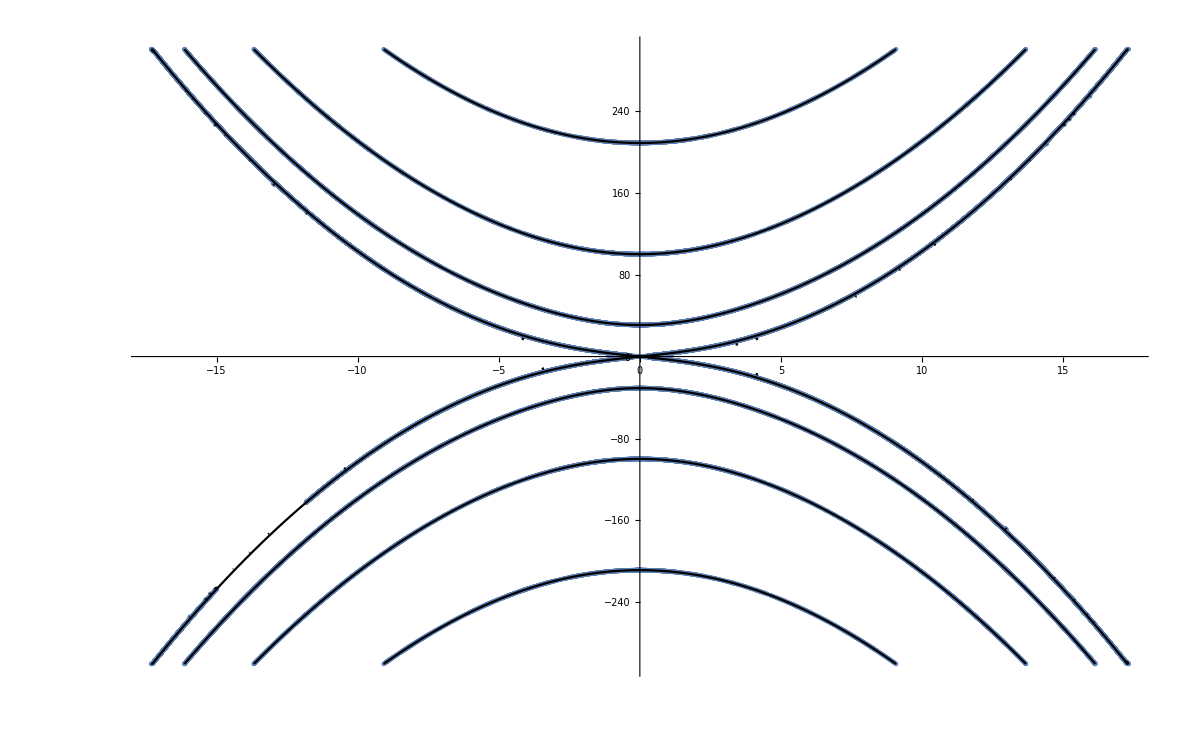

```mathematica
Show[Contorno5l,omegaAsym]
```